```mathematica
Quit[]
```

#### Kernels Control

```mathematica
LaunchKernels[8]
```

```mathematica
CloseKernels[Kernels[]]
```

```mathematica
Kernels[]
```

### Main

#### Declaration

```mathematica
ParallelEvaluate[Off[General::stop]];
```

```mathematica
ParallelEvaluate[On[General::stop]];
```

```mathematica
If[$OperatingSystem=="Windows",{dir="D:/Documents/2-d-data";},{dir="/home/huangys/mount/DATA/Documents/2-d-data";}];
```

```mathematica
Kernel[x_?NumberQ]:=NIntegrate[ϕ3[p]/(p-x)^2,{p,0,1}]
```

```mathematica
A[ω_][ϕ1_,ϕ2_,ϕ3_]:=1/(1-ω)NIntegrate[ϕ1[x]ϕ2[x/ω] ϕ3[p]/(p-(x-ω)/(1-ω))^2,{p,0,1},{x,0,ω},AccuracyGoal->12,Method->"LocalAdaptive"]-1/ω NIntegrate[ϕ1[x]ϕ3[(x-ω)/(1-ω)] ϕ2[p]/(p-x/ω)^2,{p,0,1},{x,ω,1},AccuracyGoal->12,Method->"LocalAdaptive"](*r1=1*)
```

```mathematica
Clear[m1,m2,β,Nx]; (*β=1 unit*)
Nx=500;(*the size of the working matrix*)
β=1; (*the mass unit,definition β^2=g^2/(2Pi)Nc*)
(*m1=3.2*β;(*m1 and m2 are the bare masses of the quark and the anti-quark.*)
m2=3.2*β;*)
```

```mathematica
Nc=1000;ℂ=0;(*ℂ denotes the interchange of final states.*)
```

```mathematica
vMatx[n_,m_]:=(vMatx[n-1,m-1] m/(m-1)+(8m)/(n+m-1)((1+(-1)^(n+m))/2))
vMatx[1,m_]:=4(1+(-1)^(m+1));
vMatx[n_,1]:=4/n(1+(-1)^(n+1));
```

```mathematica
Determineϕx[m1_,m2_,β_,Nx_]:=
Module[{HMatx,VMatx,vals,vecs,g,ϕx,ϕ},
SetSharedVariable[vecs,m1,m2,β,g];
SetSharedFunction[g];
HMatx=ParallelTable[4Min[n,m]((-1)^(n+m)(m1^2-β^2)+(m2^2-β^2)),{n,1,Nx},{m,1,Nx}];
VMatx=ParallelTable[vMatx[n,m],{n,1,Nx},{m,1,Nx}];
{vals,vecs}=Eigensystem[N[HMatx+VMatx]];
Do[g[j]=Dot[ParallelTable[Sin[i ArcCos[2x-1]],{i,1,Nx}],vecs[[j]]],{j,1,Nx}];
ϕx=ParallelTable[Quiet[g[Nx-n]/√NIntegrate[g[Nx-n]^2,{x,0,1}]],{n,0,20}];
Clear[g];
{√Reverse[vals] β,ϕx}
]
```

```mathematica
ϕn[n_][ϕ_][x_]:=ϕ[x][[n+1]];
```

```mathematica
Mn[n_][vals_]:=vals[[n+1]];
```

```mathematica
ω[M1_,M2_,M3_]:=(*-*)(√((M1^2+M2^2-M3^2)^2-4 M1^2 M2^2))/(2 M1^2)+M2^2/(2 M1^2)-M3^2/(2 M1^2)+1/2
```

```mathematica
ASin[n_][m1_]:=
Module[{ϕx,m2,ϕ,Vals,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,ωnow,filename},
(*SetSharedVariable[m2,m1];*)
m2=m1;
filename="/eigenstate_m-"<>ToString[m1]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Vals,ϕx}=Determineϕx[m1,m2,β,Nx];
ϕ[x_]=ϕx;
Export[dir<>filename,{Vals,ϕx},"TSV"]
},
{
{Vals,ϕx}=Import[dir<>filename,"TSV"];
ϕ[x_]=ϕx;
}
];
{M1,ϕ1}={Mn[#][Vals],ϕn[#][ϕ]}&[n];{M2,ϕ2}={Mn[#][Vals],ϕn[#][ϕ]}&[1];{M3,ϕ3}={Mn[#][Vals],ϕn[#][ϕ]}&[1];
Print[ω[M1,M2,M3]];
Ares=A[ω[M1,M2,M3]][ϕ1,ϕ2,ϕ3];
Print[{m1^2,Ares}];
{m1^2,Ares}
]
```

```mathematica
At[n_][ma_,mb_,δm_]:=Table[
Module[{ϕx,m2,ϕ,Vals,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,ωnow,filename},
(*SetSharedVariable[m2,m1];*)
m2=m1;
filename="/eigenstate_m-"<>ToString[m1]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Vals,ϕx}=Determineϕx[m1,m2,β,Nx];
ϕ[x_]=ϕx;
Export[dir<>filename,{Vals,ϕx},"TSV"]
},
{
{Vals,ϕx}=Import[dir<>filename,"TSV"];
ϕ[x_]=ϕx;
}
];
{M1,ϕ1}={Mn[#][Vals],ϕn[#][ϕ]}&[n];{M2,ϕ2}={Mn[#][Vals],ϕn[#][ϕ]}&[1];{M3,ϕ3}={Mn[#][Vals],ϕn[#][ϕ]}&[1];
Print[ω[M1,M2,M3]];
Ares=A[ω[M1,M2,M3]][ϕ1,ϕ2,ϕ3];
Print[{m1^2,Ares}];
{m1^2,Ares}
],{m1,ma,mb,δm}]
```

```mathematica
B2toB0π0[mQ_,mq_]:=
Module[{ϕxB,ΦB,ValsB,ϕxπ,Φπ,Valsπ,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow,m1,m2},
(*SetSharedVariable[m2,m1];*)
m1=mQ;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
ΦB[x_]=ϕxB;
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
ΦB[x_]=ϕxB;
}
];
m1=mq;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Valsπ,ϕxπ}=Determineϕx[m1,m2,β,Nx];
Φπ[x_]=ϕxπ;
Export[dir<>filename,{Valsπ,ϕxπ}]
},
{
{Valsπ,ϕxπ}=Import[dir<>filename];
Φπ[x_]=ϕxπ;
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M3,ϕ3}={Mn[#][Valsπ],ϕn[#][Φπ]}&[0];
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[2];
ParallelTable[{Print["ω=",ω];{ω,A[ω][ϕ1,ϕ2,ϕ3]}},{ω,0,0.5,0.1}]~Join~ParallelTable[{Print["ω=",ω];{ω,A[ω][ϕ1,ϕ2,ϕ3]}},{ω,0.6,0.8,0.02}]~Join~ParallelTable[{Print["ω=",ω];{ω,A[ω][ϕ1,ϕ2,ϕ3]}},{ω,0.8,0.9,0.005}]~Join~ParallelTable[{Print["ω=",ω];{ω,A[ω][ϕ1,ϕ2,ϕ3]}},{ω,0.9,1,0.001}]
]
```

#### Calc

```mathematica
Clear["Global`g$*"]
```

```mathematica
Information["Global`g$*"]
```

```mathematica
Clear[ϕx,m2,ϕ,vals,M1,M2,M3,ϕ1,ϕ2,ϕ3];
```

```mathematica
ParallelEvaluate[Information[ϕn]]
```

```mathematica
ASin[5][0.5]
```

```mathematica
ωt=B2toB0π0[√2000,√0.3136]
```

Wavefunction build complete.

ω=0.

ω=0.1

ω=0.2

ω=0.3

ω=0.4

ω=0.5

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.0999957}. NIntegrate obtained -4.17686×10^-9 and 4.86456×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.0999961}. NIntegrate obtained -4.79405×10^-9 and 8.34368×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.0999965}. NIntegrate obtained -5.56774×10^-9 and 1.49236×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.0999969}. NIntegrate obtained -6.55841×10^-9 and 2.80446×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.0999973}. NIntegrate obtained -7.86042×10^-9 and 5.5921×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.0999977}. NIntegrate obtained -9.62874×10^-9 and 1.19921×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.099998}. NIntegrate obtained -1.21357×10^-8 and 2.81934×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.0999984}. NIntegrate obtained -1.59049×10^-8 and 7.48106×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.0999988}. NIntegrate obtained -2.20831×10^-8 and 2.35146×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.0999992}. NIntegrate obtained -3.37516×10^-8 and 9.61026×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {7.03477×10^-6,0.0999992}. NIntegrate obtained -4.05134×10^-9 and 4.71809×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.0999996}. NIntegrate obtained -6.31145×10^-8 and 6.48517×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.0999999}. NIntegrate obtained -3.218×10^-7 and 3.17589×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {7.03477×10^-6,0.0999996}. NIntegrate obtained -4.6497×10^-9 and 8.09201×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {7.03477×10^-6,0.0999999}. NIntegrate obtained -5.39977×10^-9 and 1.44726×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.199997}. NIntegrate obtained -1.5307×10^-9 and 6.45447×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.199998}. NIntegrate obtained -2.29222×10^-9 and 2.84196×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.199998}. NIntegrate obtained -3.82417×10^-9 and 1.83216×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.299998}. NIntegrate obtained -6.87653×10^-9 and 8.62722×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.199999}. NIntegrate obtained -7.9519×10^-9 and 2.45796×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.299999}. NIntegrate obtained -1.45913×10^-8 and 1.69373×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.499996}. NIntegrate obtained -3.82879×10^-7 and 7.01268×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.2}. NIntegrate obtained -6.82476×10^-8 and 8.67867×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.3}. NIntegrate obtained -1.68774×10^-7 and 2.32483×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.499998}. NIntegrate obtained -9.3656×10^-7 and 2.41016×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {7.03477×10^-6,0.2}. NIntegrate obtained -1.67628×10^-9 and 7.06008×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {7.03477×10^-6,0.3}. NIntegrate obtained -5.37079×10^-9 and 3.79465×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.5}. NIntegrate obtained -0.0000191435 and 0.000027672 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.499998}. NIntegrate obtained -3.83418×10^-7 and 7.02246×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.5}. NIntegrate obtained -9.37867×10^-7 and 2.4135×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.5}. NIntegrate obtained -3.83953×10^-7 and 7.03217×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.399992}. NIntegrate obtained -1.29061×10^-7 and 9.90359×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.399994}. NIntegrate obtained -1.8483×10^-7 and 4.12624×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.399995}. NIntegrate obtained -2.8713×10^-7 and 2.37083×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.399997}. NIntegrate obtained -5.09401×10^-7 and 2.29366×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {7.03477×10^-6,0.399995}. NIntegrate obtained -1.5351×10^-7 and 1.96102×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {7.03477×10^-6,0.399997}. NIntegrate obtained -2.27986×10^-7 and 9.43501×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.399998}. NIntegrate obtained -1.1804×10^-6 and 6.21945×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.4}. NIntegrate obtained -0.0000188562 and 0.0000269953 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {7.03477×10^-6,0.399998}. NIntegrate obtained -3.75016×10^-7 and 6.78903×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {7.03477×10^-6,0.4}. NIntegrate obtained -7.39445×10^-7 and 9.90332×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.0000108495,0.399997}. NIntegrate obtained -1.29602×10^-7 and 9.94471×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.0000108495,0.399998}. NIntegrate obtained -1.85602×10^-7 and 4.14332×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.0000108495,0.4}. NIntegrate obtained -2.88323×10^-7 and 2.38062×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.0000146642,0.4}. NIntegrate obtained -1.54148×10^-7 and 1.96909×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.999996,0.100003}. NIntegrate obtained -6.93396×10^-9 and 7.19263×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.999999,0.100003}. NIntegrate obtained -3.56287×10^-8 and 3.52651×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.999999,0.300002}. NIntegrate obtained -7.15884×10^-8 and 9.94761×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.999999,0.200003}. NIntegrate obtained -1.7284×10^-8 and 2.1741×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.500002}. NIntegrate obtained -0.0000191499 and 0.0000276734 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.999999,0.400002}. NIntegrate obtained -0.000012576 and 0.000017998 for the integral and error estimates.

ω=0.6

ω=0.64

ω=0.68

ω=0.72

ω=0.74

ω=0.76

ω=0.78

ω=0.8

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.779994}. NIntegrate obtained -0.0000160495 and 3.74697×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.779997}. NIntegrate obtained -0.0000445134 and 2.04001×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.78}. NIntegrate obtained -0.0017086 and 0.00221843 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.779997}. NIntegrate obtained -0.0000314428 and 5.26385×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.78}. NIntegrate obtained -0.000189005 and 4.69805×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.779997}. NIntegrate obtained -0.0000234651 and 1.66974×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.78}. NIntegrate obtained -0.0000916651 and 3.23846×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.779997}. NIntegrate obtained -0.0000182134 and 6.15264×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.78}. NIntegrate obtained -0.0000556506 and 4.8207×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.779997}. NIntegrate obtained -0.0000145626 and 2.54144×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.78}. NIntegrate obtained -0.0000377439 and 1.07024×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.799993}. NIntegrate obtained -0.0000325724 and 6.71076×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.78}. NIntegrate obtained -0.0000274045 and 3.06077×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.799993}. NIntegrate obtained -0.0000269729 and 3.18305×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.78}. NIntegrate obtained -0.000020851 and 1.045×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.799996}. NIntegrate obtained -0.0000910073 and 3.74235×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.78}. NIntegrate obtained -0.0000164197 and 4.07034×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.8}. NIntegrate obtained -0.00368605 and 0.00466969 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.799996}. NIntegrate obtained -0.000066476 and 1.10391×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.8}. NIntegrate obtained -0.000441415 and 0.0000134772 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.799996}. NIntegrate obtained -0.0000508238 and 3.86028×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.8}. NIntegrate obtained -0.000217245 and 1.02361×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.799996}. NIntegrate obtained -0.0000401816 and 1.5326×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.8}. NIntegrate obtained -0.000133257 and 1.61802×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.799996}. NIntegrate obtained -0.000032598 and 6.71606×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.8}. NIntegrate obtained -0.0000910791 and 3.74531×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.799996}. NIntegrate obtained -0.0000269941 and 3.18556×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.8}. NIntegrate obtained -0.0000665285 and 1.10478×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.8}. NIntegrate obtained -0.0000508639 and 3.86333×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.8}. NIntegrate obtained -0.0000402134 and 1.53381×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.8}. NIntegrate obtained -0.0000326237 and 6.72138×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.8}. NIntegrate obtained -0.0000270154 and 3.18809×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.739994}. NIntegrate obtained -3.97753×10^-6 and 1.20025×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.739997}. NIntegrate obtained -0.0000108197 and 6.19779×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.74}. NIntegrate obtained -0.000374531 and 0.000504499 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.739997}. NIntegrate obtained -7.13634×10^-6 and 1.21407×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.74}. NIntegrate obtained -0.0000358168 and 6.04238×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.739997}. NIntegrate obtained -5.07996×10^-6 and 3.17861×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.74}. NIntegrate obtained -0.0000168926 and 3.50479×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.74}. NIntegrate obtained -0.0000100633 and 4.69737×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.74}. NIntegrate obtained -6.73143×10^-6 and 9.7033×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.74}. NIntegrate obtained -4.83598×10^-6 and 2.63173×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.759994}. NIntegrate obtained -0.0000118577 and 3.14567×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.759994}. NIntegrate obtained -9.39582×10^-6 and 1.2512×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.759997}. NIntegrate obtained -0.0000326014 and 1.66943×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.76}. NIntegrate obtained -0.00118817 and 0.00157415 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.759997}. NIntegrate obtained -0.0000222584 and 3.7585×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.76}. NIntegrate obtained -0.000121954 and 2.48868×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.759997}. NIntegrate obtained -0.0000162203 and 1.08266×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.76}. NIntegrate obtained -0.0000583123 and 1.56874×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.759997}. NIntegrate obtained -0.0000123686 and 3.71137×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.76}. NIntegrate obtained -0.000035059 and 2.21098×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.759997}. NIntegrate obtained -9.75391×10^-6 and 1.44902×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.76}. NIntegrate obtained -0.0000236081 and 4.72717×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.759997}. NIntegrate obtained -7.89441×10^-6 and 6.26031×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.76}. NIntegrate obtained -0.0000170467 and 1.31492×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.76}. NIntegrate obtained -0.0000129134 and 4.39448×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.76}. NIntegrate obtained -0.0000101329 and 1.68281×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.76}. NIntegrate obtained -8.16907×10^-6 and 7.15995×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.599997}. NIntegrate obtained -2.63137×10^-7 and 3.5258×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.6}. NIntegrate obtained -6.72465×10^-6 and 9.62758×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.6}. NIntegrate obtained -4.21483×10^-7 and 2.22149×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.6}. NIntegrate obtained -1.82136×10^-7 and 8.20528×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.679994}. NIntegrate obtained -8.53788×10^-7 and 3.93998×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.679997}. NIntegrate obtained -2.27942×10^-6 and 1.87185×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.68}. NIntegrate obtained -0.0000694521 and 0.0000969869 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.679997}. NIntegrate obtained -1.35009×10^-6 and 2.38498×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.68}. NIntegrate obtained -5.4568×10^-6 and 5.44288×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.679997}. NIntegrate obtained -8.9729×10^-7 and 4.7373×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.68}. NIntegrate obtained -2.47366×10^-6 and 2.54605×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.68}. NIntegrate obtained -1.4367×10^-6 and 3.0101×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.68}. NIntegrate obtained -9.44042×10^-7 and 5.72052×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.68}. NIntegrate obtained -6.69291×10^-7 and 1.46175×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.719994}. NIntegrate obtained -1.71215×10^-6 and 5.9655×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.719994}. NIntegrate obtained -1.29468×10^-6 and 1.96951×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.719997}. NIntegrate obtained -4.64308×10^-6 and 3.00262×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.72}. NIntegrate obtained -0.000154423 and 0.000211033 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.719997}. NIntegrate obtained -2.95633×10^-6 and 5.11304×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.72}. NIntegrate obtained -0.0000137825 and 1.94268×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.719994}. NIntegrate obtained -1.01414×10^-6 and 7.46552×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.719997}. NIntegrate obtained -2.05616×10^-6 and 1.22024×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.72}. NIntegrate obtained -6.41184×10^-6 and 1.04449×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.719997}. NIntegrate obtained -1.51591×10^-6 and 3.64953×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.72}. NIntegrate obtained -3.78565×10^-6 and 1.33886×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.719997}. NIntegrate obtained -1.16515×10^-6 and 1.28434×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.72}. NIntegrate obtained -2.51618×10^-6 and 2.68473×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.72}. NIntegrate obtained -1.79905×10^-6 and 7.12868×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.72}. NIntegrate obtained -1.35237×10^-6 and 2.29976×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.72}. NIntegrate obtained -1.05461×10^-6 and 8.5658×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.639992}. NIntegrate obtained -9.70932×10^-7 and 8.9524×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.639995}. NIntegrate obtained -1.83111×10^-6 and 1.11953×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.639995}. NIntegrate obtained -1.24943×10^-6 and 2.44779×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.639997}. NIntegrate obtained -4.7802×10^-6 and 4.98473×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.64}. NIntegrate obtained -0.000132744 and 0.000188091 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.639997}. NIntegrate obtained -2.62638×10^-6 and 4.68835×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.64}. NIntegrate obtained -9.28596×10^-6 and 6.66301×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.639995}. NIntegrate obtained -9.08048×10^-7 and 6.8636×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.639997}. NIntegrate obtained -1.6699×10^-6 and 7.77171×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.64}. NIntegrate obtained -4.1082×10^-6 and 2.74958×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.639997}. NIntegrate obtained -1.15799×10^-6 and 1.81084×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.64}. NIntegrate obtained -2.35089×10^-6 and 3.0258×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.639997}. NIntegrate obtained -8.51092×10^-7 and 5.30794×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.64}. NIntegrate obtained -1.52925×10^-6 and 5.48441×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.64}. NIntegrate obtained -1.07628×10^-6 and 1.35466×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.64}. NIntegrate obtained -7.99337×10^-7 and 4.13826×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.780001}. NIntegrate obtained -0.00605891 and 0.00786559 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.780002}. NIntegrate obtained -0.000670697 and 0.0000166588 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.780002}. NIntegrate obtained -0.000325418 and 1.1484×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.780003}. NIntegrate obtained -0.000197641 and 1.70957×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.740001}. NIntegrate obtained -0.00106564 and 0.00143581 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.740002}. NIntegrate obtained -0.000101776 and 1.71936×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.800001}. NIntegrate obtained -0.000364464 and 1.4972×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.800001}. NIntegrate obtained -0.000266278 and 4.41652×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.800001}. NIntegrate obtained -0.0147459 and 0.0186791 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.800001}. NIntegrate obtained -0.00176656 and 0.0000539128 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.800002}. NIntegrate obtained -0.000869637 and 4.09487×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.800003}. NIntegrate obtained -0.000533551 and 6.47299×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.800004}. NIntegrate obtained -0.000364753 and 1.49838×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.800004}. NIntegrate obtained -0.000266489 and 4.42002×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.600001}. NIntegrate obtained -0.000010091 and 0.0000144423 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.760001}. NIntegrate obtained -0.00376282 and 0.00498487 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.760002}. NIntegrate obtained -0.000386336 and 7.88126×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.760003}. NIntegrate obtained -0.000184762 and 4.96809×10^-7 for the integral and error estimates.

ω=0.62

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.680001}. NIntegrate obtained -0.000147697 and 0.000206121 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.680002}. NIntegrate obtained -0.0000116461 and 1.15732×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.619997}. NIntegrate obtained -4.87841×10^-7 and 5.80127×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.62}. NIntegrate obtained -0.0000131278 and 0.0000187212 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.619997}. NIntegrate obtained -2.57757×10^-7 and 4.68139×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.62}. NIntegrate obtained -8.66717×10^-7 and 5.34609×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.62}. NIntegrate obtained -3.78785×10^-7 and 2.08925×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.62}. NIntegrate obtained -2.15207×10^-7 and 2.23326×10^-11 for the integral and error estimates.

ω=0.7

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.720001}. NIntegrate obtained -0.000397288 and 0.000542698 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.720002}. NIntegrate obtained -0.0000355356 and 4.99734×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.699994}. NIntegrate obtained -2.19086×10^-6 and 8.69426×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.699997}. NIntegrate obtained -5.85892×10^-6 and 4.24315×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.7}. NIntegrate obtained -0.000184983 and 0.000255654 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.699997}. NIntegrate obtained -3.59968×10^-6 and 6.24948×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.7}. NIntegrate obtained -0.0000154913 and 1.82587×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.699997}. NIntegrate obtained -2.44723×10^-6 and 1.35784×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.7}. NIntegrate obtained -7.11492×10^-6 and 9.12342×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.7}. NIntegrate obtained -4.16622×10^-6 and 1.11974×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.7}. NIntegrate obtained -2.75309×10^-6 and 2.18012×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.640001}. NIntegrate obtained -0.00023597 and 0.00033438 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.640003}. NIntegrate obtained -0.0000165 and 1.18445×10^-7 for the integral and error estimates.

ω=0.66

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.620001}. NIntegrate obtained -0.0000214548 and 0.000030553 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.700001}. NIntegrate obtained -0.000431453 and 0.000596489 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.700002}. NIntegrate obtained -0.0000360661 and 4.25904×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.659995}. NIntegrate obtained -8.41482×10^-8 and 4.37907×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.659995}. NIntegrate obtained -5.89932×10^-8 and 1.06336×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.659997}. NIntegrate obtained -2.19183×10^-7 and 2.00336×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.66}. NIntegrate obtained -6.26751×10^-6 and 8.81205×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.659997}. NIntegrate obtained -1.25123×10^-7 and 2.18852×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.66}. NIntegrate obtained -4.65647×10^-7 and 3.90046×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.659997}. NIntegrate obtained -8.1342×10^-8 and 3.95456×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.66}. NIntegrate obtained -2.08624×10^-7 and 1.70459×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.659997}. NIntegrate obtained -5.7244×10^-8 and 9.74773×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.66}. NIntegrate obtained -1.20289×10^-7 and 1.93489×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.66}. NIntegrate obtained -7.86465×10^-8 and 3.57476×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.66}. NIntegrate obtained -5.5554×10^-8 and 8.94168×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.660001}. NIntegrate obtained -0.0000121415 and 0.0000171003 for the integral and error estimates.

ω=0.8

ω=0.81

ω=0.82

ω=0.83

ω=0.84

ω=0.85

ω=0.855

ω=0.86

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.854993}. NIntegrate obtained -0.000472211 and 7.15904×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.854993}. NIntegrate obtained -0.000413869 and 4.25614×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.854996}. NIntegrate obtained -0.00134607 and 4.24146×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.859993}. NIntegrate obtained -0.000573083 and 8.48242×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.849993}. NIntegrate obtained -0.000389003 and 6.04674×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.854999}. NIntegrate obtained -0.0651242 and 0.0745698 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.859993}. NIntegrate obtained -0.000504773 and 5.14322×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.849996}. NIntegrate obtained -0.00110689 and 3.56389×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.854996}. NIntegrate obtained -0.00107565 and 1.78727×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.859996}. NIntegrate obtained -0.00163681 and 5.05165×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.849999}. NIntegrate obtained -0.0525594 and 0.0609054 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.854999}. NIntegrate obtained -0.00996641 and 0.000567356 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.859999}. NIntegrate obtained -0.080758 and 0.091309 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.849996}. NIntegrate obtained -0.000877436 and 1.45483×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.854996}. NIntegrate obtained -0.000880755 and 8.22977×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.859996}. NIntegrate obtained -0.00131849 and 2.19706×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.849999}. NIntegrate obtained -0.00785064 and 0.000420588 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.854999}. NIntegrate obtained -0.00511821 and 0.0000593051 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.859999}. NIntegrate obtained -0.0126684 and 0.000767056 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.849996}. NIntegrate obtained -0.000713895 and 6.53071×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.854996}. NIntegrate obtained -0.000735263 and 4.07043×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.859996}. NIntegrate obtained -0.00108653 and 1.03785×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.849999}. NIntegrate obtained -0.00401557 and 0.0000425385 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.854999}. NIntegrate obtained -0.00323978 and 0.0000114943 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.859999}. NIntegrate obtained -0.00653196 and 0.000082945 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.839993}. NIntegrate obtained -0.000247875 and 4.06002×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.849996}. NIntegrate obtained -0.000592877 and 3.16323×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.854996}. NIntegrate obtained -0.000623565 and 2.13561×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.859996}. NIntegrate obtained -0.000911822 and 5.24281×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.839993}. NIntegrate obtained -0.000214002 and 2.27352×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.849999}. NIntegrate obtained -0.00253404 and 8.06981×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.854999}. NIntegrate obtained -0.00226919 and 3.0764×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.859999}. NIntegrate obtained -0.00414753 and 0.0000164363 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.839996}. NIntegrate obtained -0.000702921 and 2.36792×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.849996}. NIntegrate obtained -0.000500635 and 1.63079×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.854996}. NIntegrate obtained -0.00053583 and 1.17746×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.859996}. NIntegrate obtained -0.000776712 and 2.80011×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.84}. NIntegrate obtained -0.0322197 and 0.0381638 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.849999}. NIntegrate obtained -0.00177054 and 2.12661×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.854999}. NIntegrate obtained -0.0016904 and 1.01268×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.859999}. NIntegrate obtained -0.00291225 and 4.47046×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.819993}. NIntegrate obtained -0.0000862391 and 1.57843×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.839996}. NIntegrate obtained -0.000548283 and 9.06822×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.849996}. NIntegrate obtained -0.000428617 and 8.85813×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.854996}. NIntegrate obtained -0.000465592 and 6.7727×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.859996}. NIntegrate obtained -0.000669935 and 1.56751×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.819996}. NIntegrate obtained -0.000242792 and 9.00702×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.84}. NIntegrate obtained -0.00459046 and 0.000218407 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.849999}. NIntegrate obtained -0.00131629 and 6.91776×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.854999}. NIntegrate obtained -0.0013134 and 3.86012×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.859999}. NIntegrate obtained -0.00217389 and 1.48987×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.82}. NIntegrate obtained -0.0104298 and 0.0128218 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.839996}. NIntegrate obtained -0.00044048 and 3.86982×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.849996}. NIntegrate obtained -0.000371256 and 5.02996×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.854996}. NIntegrate obtained -0.000408445 and 4.04079×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.859996}. NIntegrate obtained -0.000584003 and 9.13581×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.819996}. NIntegrate obtained -0.000183304 and 3.03067×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.84}. NIntegrate obtained -0.00232945 and 0.0000207363 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.849999}. NIntegrate obtained -0.00102102 and 2.61216×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.854999}. NIntegrate obtained -0.0010525 and 1.64319×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.859999}. NIntegrate obtained -0.00169198 and 5.73521×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.82}. NIntegrate obtained -0.00135853 and 0.0000514786 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.839996}. NIntegrate obtained -0.000362085 and 1.7987×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.849999}. NIntegrate obtained -0.000817035 and 1.10344×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.854999}. NIntegrate obtained -0.0008637 and 7.62787×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.859996}. NIntegrate obtained -0.000513772 and 5.51388×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.819996}. NIntegrate obtained -0.000143629 and 1.16998×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.829993}. NIntegrate obtained -0.000146987 and 2.54264×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.84}. NIntegrate obtained -0.0014612 and 3.77623×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.849999}. NIntegrate obtained -0.000669659 and 5.08959×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.854999}. NIntegrate obtained -0.000722309 and 3.7978×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.859999}. NIntegrate obtained -0.00135785 and 2.46112×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.82}. NIntegrate obtained -0.000678769 and 4.34781×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.829993}. NIntegrate obtained -0.000125611 and 1.36717×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.839996}. NIntegrate obtained -0.000303169 and 8.96046×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.849999}. NIntegrate obtained -0.00055944 and 2.52032×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.854999}. NIntegrate obtained -0.00061348 and 2.00361×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.859999}. NIntegrate obtained -0.00111569 and 1.15018×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.819996}. NIntegrate obtained -0.000115744 and 5.01878×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.829996}. NIntegrate obtained -0.00041536 and 1.46706×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.84}. NIntegrate obtained -0.0010161 and 9.66298×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.849999}. NIntegrate obtained -0.000474709 and 1.32348×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.854999}. NIntegrate obtained -0.000527815 and 1.10988×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.859999}. NIntegrate obtained -0.000934071 and 5.7593×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.82}. NIntegrate obtained -0.000420903 and 7.3473×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.83}. NIntegrate obtained -0.0184163 and 0.0222457 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.839996}. NIntegrate obtained -0.000257708 and 4.72791×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.849999}. NIntegrate obtained -0.000408088 and 7.30168×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.854999}. NIntegrate obtained -0.000459112 and 6.40971×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.859999}. NIntegrate obtained -0.0007941 and 3.05337×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.819996}. NIntegrate obtained -0.0000953513 and 2.34087×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.829996}. NIntegrate obtained -0.000318762 and 5.26779×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.84}. NIntegrate obtained -0.000752493 and 3.07369×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.849999}. NIntegrate obtained -0.000354709 and 4.20193×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.854999}. NIntegrate obtained -0.000403128 and 3.83764×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.859999}. NIntegrate obtained -0.000683798 and 1.69861×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.82}. NIntegrate obtained -0.000290079 and 1.78257×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.83}. NIntegrate obtained -0.00250688 and 0.00010628 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.839996}. NIntegrate obtained -0.000221856 and 2.61864×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.859999}. NIntegrate obtained -0.000595244 and 9.84655×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.809993}. NIntegrate obtained -0.0000519529 and 1.00794×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.819996}. NIntegrate obtained -0.0000799627 and 1.16894×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.829996}. NIntegrate obtained -0.000252894 and 2.13778×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.84}. NIntegrate obtained -0.00058182 and 1.14025×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.859999}. NIntegrate obtained -0.000523018 and 5.91495×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.809993}. NIntegrate obtained -0.0000434818 and 4.98793×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.82}. NIntegrate obtained -0.000213283 and 5.44643×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.83}. NIntegrate obtained -0.00126222 and 9.50314×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.84}. NIntegrate obtained -0.00046432 and 4.7478×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.809996}. NIntegrate obtained -0.000145707 and 5.68662×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.82}. NIntegrate obtained -0.000163935 and 1.95754×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.829996}. NIntegrate obtained -0.00020581 and 9.5423×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.84}. NIntegrate obtained -0.000379685 and 2.16387×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.81}. NIntegrate obtained -0.00607338 and 0.00758518 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.82}. NIntegrate obtained -0.000130182 and 7.94496×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.83}. NIntegrate obtained -0.000787146 and 1.66528×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.84}. NIntegrate obtained -0.000316557 and 1.06076×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.809996}. NIntegrate obtained -0.00010821 and 1.79203×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.82}. NIntegrate obtained -0.000106005 and 3.54524×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.829996}. NIntegrate obtained -0.000170909 and 4.59766×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.84}. NIntegrate obtained -0.000268141 and 5.52233×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.81}. NIntegrate obtained -0.000758043 and 0.0000257484 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.82}. NIntegrate obtained -0.0000880611 and 1.70729×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.83}. NIntegrate obtained -0.000544875 and 4.14573×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.84}. NIntegrate obtained -0.000230153 and 3.02395×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.809996}. NIntegrate obtained -0.0000837496 and 6.58311×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.829996}. NIntegrate obtained -0.000144283 and 2.3589×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.81}. NIntegrate obtained -0.00037588 and 2.05967×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.83}. NIntegrate obtained -0.000402034 and 1.29154×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.809996}. NIntegrate obtained -0.0000668424 and 2.71577×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.829996}. NIntegrate obtained -0.000123484 and 1.27569×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.81}. NIntegrate obtained -0.000231802 and 3.3632×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.83}. NIntegrate obtained -0.000309906 and 4.71329×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.809996}. NIntegrate obtained -0.0000546388 and 1.22727×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.83}. NIntegrate obtained -0.00024669 and 1.93664×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.81}. NIntegrate obtained -0.00015908 and 7.96441×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.83}. NIntegrate obtained -0.000201286 and 8.72999×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.809996}. NIntegrate obtained -0.0000455275 and 5.97025×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.83}. NIntegrate obtained -0.000167505 and 4.24014×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.81}. NIntegrate obtained -0.000116573 and 2.38962×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.83}. NIntegrate obtained -0.000141655 and 2.19003×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.81}. NIntegrate obtained -0.0000893568 and 8.46765×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.83}. NIntegrate obtained -0.000121413 and 1.19106×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.81}. NIntegrate obtained -0.0000707978 and 3.39769×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.81}. NIntegrate obtained -0.0000575396 and 1.50194×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.81}. NIntegrate obtained -0.0000477213 and 7.17613×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.799993}. NIntegrate obtained -0.0000325724 and 6.71076×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.799993}. NIntegrate obtained -0.0000269729 and 3.18305×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.799996}. NIntegrate obtained -0.0000910073 and 3.74235×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.8}. NIntegrate obtained -0.00368605 and 0.00466969 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.799996}. NIntegrate obtained -0.000066476 and 1.10391×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.8}. NIntegrate obtained -0.000441415 and 0.0000134772 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.799996}. NIntegrate obtained -0.0000508238 and 3.86028×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.8}. NIntegrate obtained -0.000217245 and 1.02361×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.799996}. NIntegrate obtained -0.0000401816 and 1.5326×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.8}. NIntegrate obtained -0.000133257 and 1.61802×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.799996}. NIntegrate obtained -0.000032598 and 6.71606×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.8}. NIntegrate obtained -0.0000910791 and 3.74531×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.799996}. NIntegrate obtained -0.0000269941 and 3.18556×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.8}. NIntegrate obtained -0.0000665285 and 1.10478×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.8}. NIntegrate obtained -0.0000508639 and 3.86333×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.8}. NIntegrate obtained -0.0000402134 and 1.53381×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.8}. NIntegrate obtained -0.0000326237 and 6.72138×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.8}. NIntegrate obtained -0.0000270154 and 3.18809×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.85}. NIntegrate obtained -0.00627248 and 2.01954×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.850001}. NIntegrate obtained -0.00497223 and 8.24407×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.85}. NIntegrate obtained -0.297837 and 0.345131 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.850001}. NIntegrate obtained -0.0444872 and 0.00238333 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.850002}. NIntegrate obtained -0.0227551 and 0.000241052 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.850002}. NIntegrate obtained -0.0143597 and 0.000045729 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.850003}. NIntegrate obtained -0.0100332 and 0.0000120508 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.850003}. NIntegrate obtained -0.00745909 and 3.92007×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.850004}. NIntegrate obtained -0.00578587 and 1.48023×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.850004}. NIntegrate obtained -0.00462994 and 6.25284×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.86}. NIntegrate obtained -0.0100553 and 3.10318×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.860001}. NIntegrate obtained -0.0080999 and 1.34963×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.86}. NIntegrate obtained -0.496088 and 0.560899 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.860001}. NIntegrate obtained -0.0778217 and 0.00471193 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.860002}. NIntegrate obtained -0.00667494 and 6.37544×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.860002}. NIntegrate obtained -0.0401262 and 0.000509522 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.860002}. NIntegrate obtained -0.0254787 and 0.000100967 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.840001}. NIntegrate obtained -0.00369222 and 1.24325×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.860003}. NIntegrate obtained -0.0178904 and 0.0000274616 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.840001}. NIntegrate obtained -0.169161 and 0.200361 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.860003}. NIntegrate obtained -0.0133547 and 9.15216×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.840001}. NIntegrate obtained -0.0241043 and 0.00114667 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.860004}. NIntegrate obtained -0.0103942 and 3.52309×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.840002}. NIntegrate obtained -0.0122329 and 0.00010887 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.860004}. NIntegrate obtained -0.00834171 and 1.51185×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.840002}. NIntegrate obtained -0.00767395 and 0.0000198262 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.860005}. NIntegrate obtained -0.00685407 and 7.06547×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.840003}. NIntegrate obtained -0.00533674 and 5.07337×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.840004}. NIntegrate obtained -0.00395252 and 1.6138×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.840004}. NIntegrate obtained -0.00305627 and 5.98679×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.855}. NIntegrate obtained -0.00793662 and 2.50097×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.855001}. NIntegrate obtained -0.00634209 and 1.05386×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.855}. NIntegrate obtained -0.384006 and 0.439704 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.855001}. NIntegrate obtained -0.0587661 and 0.00334543 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.855002}. NIntegrate obtained -0.00519295 and 4.85266×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.855002}. NIntegrate obtained -0.0301787 and 0.000349694 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.855002}. NIntegrate obtained -0.0191027 and 0.0000677764 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.855003}. NIntegrate obtained -0.0133796 and 0.00001814 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.855003}. NIntegrate obtained -0.00996687 and 5.97129×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.855004}. NIntegrate obtained -0.00774397 and 2.27611×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.855004}. NIntegrate obtained -0.00620559 and 9.68906×10^-7 for the integral and error estimates.

ω=0.865

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.830001}. NIntegrate obtained -0.00202975 and 7.16364×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.830001}. NIntegrate obtained -0.0899223 and 0.108613 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.830001}. NIntegrate obtained -0.0122436 and 0.000518923 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.830002}. NIntegrate obtained -0.00616565 and 0.000046401 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.830002}. NIntegrate obtained -0.00384558 and 8.13125×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.830003}. NIntegrate obtained -0.00266234 and 2.02432×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.830004}. NIntegrate obtained -0.00196466 and 6.30656×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.820001}. NIntegrate obtained -0.00110718 and 4.1038×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.820001}. NIntegrate obtained -0.047518 and 0.0584113 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.820001}. NIntegrate obtained -0.00619134 and 0.000234527 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.820002}. NIntegrate obtained -0.00309401 and 0.0000198084 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.820003}. NIntegrate obtained -0.00191892 and 3.34747×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.820003}. NIntegrate obtained -0.0013227 and 8.12168×10^-7 for the integral and error estimates.

ω=0.845

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.820004}. NIntegrate obtained -0.000972686 and 2.48154×10^-7 for the integral and error estimates.

ω=0.87

ω=0.875

ω=0.835

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.864993}. NIntegrate obtained -0.000713723 and 1.03235×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.864996}. NIntegrate obtained -0.0020427 and 6.17994×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.810001}. NIntegrate obtained -0.000621826 and 2.42467×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.864999}. NIntegrate obtained -0.102871 and 0.114761 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.810001}. NIntegrate obtained -0.0258944 and 0.0323373 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.864996}. NIntegrate obtained -0.00165864 and 2.77378×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.810001}. NIntegrate obtained -0.00323306 and 0.000109776 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.864999}. NIntegrate obtained -0.0165493 and 0.00106685 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.810002}. NIntegrate obtained -0.00160346 and 8.78151×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.864996}. NIntegrate obtained -0.00137565 and 1.34432×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.810003}. NIntegrate obtained -0.000989028 and 1.43396×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.864999}. NIntegrate obtained -0.00856748 and 0.000119462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.810004}. NIntegrate obtained -0.000678868 and 3.39585×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.864996}. NIntegrate obtained -0.00116059 and 6.93743×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.864999}. NIntegrate obtained -0.00545715 and 0.000024221 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.864996}. NIntegrate obtained -0.000993047 and 3.77273×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.864999}. NIntegrate obtained -0.00384157 and 6.69873×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.864996}. NIntegrate obtained -0.000859808 and 2.14501×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.864999}. NIntegrate obtained -0.00287364 and 2.2614×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.864996}. NIntegrate obtained -0.000752006 and 1.26713×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.864999}. NIntegrate obtained -0.00224057 and 8.79507×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.864996}. NIntegrate obtained -0.000663491 and 7.73871×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.864999}. NIntegrate obtained -0.00180083 and 3.80611×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.864999}. NIntegrate obtained -0.00148159 and 1.79132×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.864999}. NIntegrate obtained -0.00124183 and 9.02361×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.864999}. NIntegrate obtained -0.0010568 and 4.80875×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.864999}. NIntegrate obtained -0.000910815 and 2.68719×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.864999}. NIntegrate obtained -0.000793491 and 1.56389×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.864999}. NIntegrate obtained -0.000697707 and 9.42752×10^-9 for the integral and error estimates.

ω=0.825

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.844993}. NIntegrate obtained -0.00031428 and 5.01303×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.869993}. NIntegrate obtained -0.000916635 and 1.2965×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.844993}. NIntegrate obtained -0.000272707 and 2.86413×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.869993}. NIntegrate obtained -0.000815336 and 8.17379×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.844996}. NIntegrate obtained -0.00089274 and 2.93922×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.869996}. NIntegrate obtained -0.00262862 and 7.80083×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.844999}. NIntegrate obtained -0.0416363 and 0.0487949 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.869999}. NIntegrate obtained -0.135216 and 0.148709 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.844996}. NIntegrate obtained -0.000701997 and 1.16221×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.869996}. NIntegrate obtained -0.00215146 and 3.6128×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.844999}. NIntegrate obtained -0.0060726 and 0.000306454 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.869999}. NIntegrate obtained -0.0223205 and 0.00153345 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.844996}. NIntegrate obtained -0.000567543 and 5.08654×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.869996}. NIntegrate obtained -0.00179595 and 1.79656×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.844999}. NIntegrate obtained -0.00309378 and 0.0000300175 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.869999}. NIntegrate obtained -0.0116023 and 0.000177992 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.844996}. NIntegrate obtained -0.000468916 and 2.41323×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.869996}. NIntegrate obtained -0.00152334 and 9.47302×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.844999}. NIntegrate obtained -0.00194644 and 5.5775×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.869999}. NIntegrate obtained -0.00741384 and 0.0000369528 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.844996}. NIntegrate obtained -0.000394273 and 1.22283×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.869996}. NIntegrate obtained -0.00130935 and 5.24688×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.844999}. NIntegrate obtained -0.00135672 and 1.448×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.869999}. NIntegrate obtained -0.00523257 and 0.0000103985 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.844996}. NIntegrate obtained -0.00033634 and 6.54559×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.869996}. NIntegrate obtained -0.0011381 and 3.03064×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.844999}. NIntegrate obtained -0.00100667 and 4.65682×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.869999}. NIntegrate obtained -0.00392262 and 3.55768×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.844996}. NIntegrate obtained -0.000290427 and 3.67033×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.869996}. NIntegrate obtained -0.000998782 and 1.81512×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.844999}. NIntegrate obtained -0.00077958 and 1.7426×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.869999}. NIntegrate obtained -0.00306404 and 1.39857×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.844996}. NIntegrate obtained -0.000253398 and 2.14182×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.869996}. NIntegrate obtained -0.000883845 and 1.12207×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.844999}. NIntegrate obtained -0.000622973 and 7.30725×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.869999}. NIntegrate obtained -0.00246654 and 6.10588×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.844999}. NIntegrate obtained -0.00051 and 3.34991×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.869999}. NIntegrate obtained -0.00203204 and 2.89498×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.844999}. NIntegrate obtained -0.000425625 and 1.6503×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.869999}. NIntegrate obtained -0.00170521 and 1.46751×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.844999}. NIntegrate obtained -0.000360838 and 8.62781×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.874993}. NIntegrate obtained -0.00117136 and 1.62077×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.869999}. NIntegrate obtained -0.00145265 and 7.86293×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.844999}. NIntegrate obtained -0.000309953 and 4.74177×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.874996}. NIntegrate obtained -0.00336495 and 9.80088×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.869999}. NIntegrate obtained -0.00125315 and 4.41472×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.844999}. NIntegrate obtained -0.000269222 and 2.71962×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.874999}. NIntegrate obtained -0.176915 and 0.191638 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.869999}. NIntegrate obtained -0.00109264 and 2.57999×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.874996}. NIntegrate obtained -0.00277609 and 4.6829×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.869999}. NIntegrate obtained -0.000961461 and 1.56103×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.874999}. NIntegrate obtained -0.029984 and 0.00219738 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.869999}. NIntegrate obtained -0.000852815 and 9.73664×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.874996}. NIntegrate obtained -0.00233245 and 2.3895×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.874999}. NIntegrate obtained -0.0156497 and 0.000264675 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.874996}. NIntegrate obtained -0.00198917 and 1.28759×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.874999}. NIntegrate obtained -0.0100327 and 0.0000563105 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.874996}. NIntegrate obtained -0.00171765 and 7.26526×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.874999}. NIntegrate obtained -0.00709976 and 0.000016133 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.874996}. NIntegrate obtained -0.00149894 and 4.26445×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.874999}. NIntegrate obtained -0.0053342 and 5.59706×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.874996}. NIntegrate obtained -0.00132002 and 2.59024×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.874999}. NIntegrate obtained -0.0041745 and 2.22499×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.874996}. NIntegrate obtained -0.00117169 and 1.62123×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.874999}. NIntegrate obtained -0.0033659 and 9.80364×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.874999}. NIntegrate obtained -0.00277687 and 4.68422×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.874999}. NIntegrate obtained -0.00233311 and 2.39017×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.874999}. NIntegrate obtained -0.00198973 and 1.28796×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.874999}. NIntegrate obtained -0.00171813 and 7.26731×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.874999}. NIntegrate obtained -0.00149936 and 4.26565×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.874999}. NIntegrate obtained -0.00132039 and 2.59097×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.874999}. NIntegrate obtained -0.00117202 and 1.62168×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.834993}. NIntegrate obtained -0.000191851 and 3.22857×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.834996}. NIntegrate obtained -0.000543108 and 1.87295×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.835}. NIntegrate obtained -0.0244787 and 0.0292882 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.834996}. NIntegrate obtained -0.000420206 and 6.94585×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.835}. NIntegrate obtained -0.00340827 and 0.000153012 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.834996}. NIntegrate obtained -0.000335469 and 2.89042×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.835}. NIntegrate obtained -0.00172277 and 0.0000140928 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.834996}. NIntegrate obtained -0.000274377 and 1.31643×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.835}. NIntegrate obtained -0.00107747 and 2.5168×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.834996}. NIntegrate obtained -0.000228782 and 6.44879×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.835}. NIntegrate obtained -0.000747531 and 6.35088×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.834996}. NIntegrate obtained -0.0001938 and 3.35492×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.835}. NIntegrate obtained -0.000552569 and 1.99886×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.835}. NIntegrate obtained -0.000426583 and 7.35348×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.835}. NIntegrate obtained -0.000339994 and 3.0412×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.835}. NIntegrate obtained -0.000277713 and 1.37832×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.835}. NIntegrate obtained -0.000231319 and 6.72487×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.835}. NIntegrate obtained -0.000195778 and 3.48685×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.835}. NIntegrate obtained -0.000167919 and 1.9027×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.800001}. NIntegrate obtained -0.000364464 and 1.4972×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.800001}. NIntegrate obtained -0.000266278 and 4.41652×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.800001}. NIntegrate obtained -0.0147459 and 0.0186791 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.800001}. NIntegrate obtained -0.00176656 and 0.0000539128 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.800002}. NIntegrate obtained -0.000869637 and 4.09487×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.800003}. NIntegrate obtained -0.000533551 and 6.47299×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.800004}. NIntegrate obtained -0.000364753 and 1.49838×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.800004}. NIntegrate obtained -0.000266489 and 4.42002×10^-8 for the integral and error estimates.

ω=0.815

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.824993}. NIntegrate obtained -0.00011238 and 1.9992×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.824993}. NIntegrate obtained -0.0000955429 and 1.05313×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.824996}. NIntegrate obtained -0.000316984 and 1.14718×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.825}. NIntegrate obtained -0.0138313 and 0.0168588 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.824996}. NIntegrate obtained -0.000241286 and 3.98778×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.825}. NIntegrate obtained -0.0018414 and 0.0000737775 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.824996}. NIntegrate obtained -0.000190238 and 1.57834×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.825}. NIntegrate obtained -0.000923565 and 6.40915×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.824996}. NIntegrate obtained -0.000154056 and 6.90587×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.825}. NIntegrate obtained -0.000574314 and 1.10262×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.824996}. NIntegrate obtained -0.000127418 and 3.27342×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.825}. NIntegrate obtained -0.000396668 and 2.70928×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.824996}. NIntegrate obtained -0.000107207 and 1.65671×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.825}. NIntegrate obtained -0.000292161 and 8.35734×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.825}. NIntegrate obtained -0.000224882 and 3.02633×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.825}. NIntegrate obtained -0.000178791 and 1.23572×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.825}. NIntegrate obtained -0.000145734 and 5.54161×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.825}. NIntegrate obtained -0.000121168 and 2.67986×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.825}. NIntegrate obtained -0.00010239 and 1.37902×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.814993}. NIntegrate obtained -0.0000666452 and 1.25557×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.814993}. NIntegrate obtained -0.0000560729 and 6.34512×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.814996}. NIntegrate obtained -0.00018727 and 7.12434×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.815}. NIntegrate obtained -0.00792293 and 0.0098193 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.814996}. NIntegrate obtained -0.000140229 and 2.32006×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.815}. NIntegrate obtained -0.00101005 and 0.000036224 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.814996}. NIntegrate obtained -0.000109201 and 8.73661×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.815}. NIntegrate obtained -0.000502737 and 2.97647×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.814996}. NIntegrate obtained -0.0000875749 and 3.6749×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.815}. NIntegrate obtained -0.000310882 and 4.94315×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.814996}. NIntegrate obtained -0.000071863 and 1.68699×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.815}. NIntegrate obtained -0.000213798 and 1.18463×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.814996}. NIntegrate obtained -0.0000600703 and 8.31377×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.815}. NIntegrate obtained -0.00015693 and 3.58622×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.815}. NIntegrate obtained -0.000120454 and 1.27967×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.815}. NIntegrate obtained -0.0000955433 and 5.16362×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.815}. NIntegrate obtained -0.0000777242 and 2.29312×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.815}. NIntegrate obtained -0.0000645136 and 1.09987×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.815}. NIntegrate obtained -0.0000544357 and 5.62037×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.865}. NIntegrate obtained -0.0130931 and 3.95995×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.865001}. NIntegrate obtained -0.0106318 and 1.77738×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.865}. NIntegrate obtained -0.659156 and 0.735324 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.865001}. NIntegrate obtained -0.10605 and 0.00683588 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.865001}. NIntegrate obtained -0.00881821 and 8.61414×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.865001}. NIntegrate obtained -0.0549045 and 0.000765459 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.865002}. NIntegrate obtained -0.0349736 and 0.000155199 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.865002}. NIntegrate obtained -0.0246209 and 0.0000429231 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.865003}. NIntegrate obtained -0.0184181 and 0.0000144903 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.865004}. NIntegrate obtained -0.0143611 and 5.63564×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.865004}. NIntegrate obtained -0.0115431 and 2.43886×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.865005}. NIntegrate obtained -0.00949722 and 1.14784×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.865005}. NIntegrate obtained -0.00796058 and 5.78218×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.87}. NIntegrate obtained -0.017601 and 5.22096×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.870001}. NIntegrate obtained -0.0144068 and 2.41801×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.87}. NIntegrate obtained -0.904952 and 0.995217 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.870001}. NIntegrate obtained -0.149401 and 0.0102626 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.870001}. NIntegrate obtained -0.0120269 and 1.20243×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.870002}. NIntegrate obtained -0.0102019 and 6.34029×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.870001}. NIntegrate obtained -0.0776648 and 0.00119122 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.870002}. NIntegrate obtained -0.0496311 and 0.000247311 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.870002}. NIntegrate obtained -0.0350311 and 0.0000695938 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.870003}. NIntegrate obtained -0.0262629 and 0.0000238106 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.870003}. NIntegrate obtained -0.0205157 and 9.36032×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.870004}. NIntegrate obtained -0.016516 and 4.08657×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.870004}. NIntegrate obtained -0.0136074 and 1.93758×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.870005}. NIntegrate obtained -0.0114195 and 9.82195×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.870005}. NIntegrate obtained -0.00972871 and 5.26267×10^-7 for the integral and error estimates.

ω=0.805

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.875}. NIntegrate obtained -0.0235643 and 6.86103×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.875001}. NIntegrate obtained -0.0194415 and 3.27824×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.875}. NIntegrate obtained -1.23845 and 1.34147 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.875001}. NIntegrate obtained -0.209914 and 0.015382 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.875001}. NIntegrate obtained -0.0163353 and 1.67277×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.875002}. NIntegrate obtained -0.0139317 and 9.01386×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.875001}. NIntegrate obtained -0.109568 and 0.00185278 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.875002}. NIntegrate obtained -0.070245 and 0.000394187 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.875002}. NIntegrate obtained -0.0120305 and 5.08611×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.875002}. NIntegrate obtained -0.0497121 and 0.000112936 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.875003}. NIntegrate obtained -0.0373515 and 0.0000391812 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.875003}. NIntegrate obtained -0.0292323 and 0.0000155758 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.875004}. NIntegrate obtained -0.023571 and 6.86296×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.875004}. NIntegrate obtained -0.0194469 and 3.27917×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.875005}. NIntegrate obtained -0.0163399 and 1.67324×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.875005}. NIntegrate obtained -0.0139356 and 9.0164×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.875006}. NIntegrate obtained -0.0120339 and 5.08754×10^-7 for the integral and error estimates.

ω=0.88

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.845}. NIntegrate obtained -0.00486807 and 1.60241×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.845001}. NIntegrate obtained -0.00382808 and 6.33615×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.845}. NIntegrate obtained -0.22699 and 0.266012 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.845001}. NIntegrate obtained -0.0331083 and 0.00167069 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.845002}. NIntegrate obtained -0.0168682 and 0.000163647 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.845002}. NIntegrate obtained -0.0106129 and 0.0000304071 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.845003}. NIntegrate obtained -0.00739774 and 7.89414×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.845003}. NIntegrate obtained -0.00548922 and 2.5388×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.845004}. NIntegrate obtained -0.00425108 and 9.50036×10^-7 for the integral and error estimates.

ω=0.885

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.835001}. NIntegrate obtained -0.00275048 and 9.47929×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.835001}. NIntegrate obtained -0.123885 and 0.148218 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.835001}. NIntegrate obtained -0.0172526 and 0.000774365 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.835002}. NIntegrate obtained -0.00872172 and 0.0000713225 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.835002}. NIntegrate obtained -0.00545546 and 0.0000127375 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.835003}. NIntegrate obtained -0.00378532 and 3.21422×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.835004}. NIntegrate obtained -0.00279837 and 1.01165×10^-6 for the integral and error estimates.

ω=0.89

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.804993}. NIntegrate obtained -0.0000408999 and 8.17517×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.804996}. NIntegrate obtained -0.000114489 and 4.58571×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.805}. NIntegrate obtained -0.00470335 and 0.0059172 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.804996}. NIntegrate obtained -0.0000843258 and 1.39822×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.805}. NIntegrate obtained -0.000574931 and 0.0000185086 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.804996}. NIntegrate obtained -0.0000648654 and 5.0112×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.805}. NIntegrate obtained -0.000284013 and 1.44223×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.804996}. NIntegrate obtained -0.0000515251 and 2.02786×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.805}. NIntegrate obtained -0.000174677 and 2.31655×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.804996}. NIntegrate obtained -0.0000419579 and 9.02319×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.805}. NIntegrate obtained -0.00011963 and 5.42275×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.805}. NIntegrate obtained -0.0000875223 and 1.61303×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.805}. NIntegrate obtained -0.0000670004 and 5.67742×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.805}. NIntegrate obtained -0.0000530271 and 2.26582×10^-9 for the integral and error estimates.

ω=0.895

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.805}. NIntegrate obtained -0.0000430573 and 9.97165×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.805}. NIntegrate obtained -0.0000356824 and 4.74668×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.879993}. NIntegrate obtained -0.00142365 and 1.92831×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.879996}. NIntegrate obtained -0.0040964 and 1.17185×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.879999}. NIntegrate obtained -0.220312 and 0.234821 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.879996}. NIntegrate obtained -0.00340641 and 5.77568×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.879999}. NIntegrate obtained -0.0383606 and 0.00300192 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.879996}. NIntegrate obtained -0.00288078 and 3.02427×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.879999}. NIntegrate obtained -0.0201045 and 0.000375648 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.879996}. NIntegrate obtained -0.0024703 and 1.66573×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.879999}. NIntegrate obtained -0.0129311 and 0.0000819711 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.879996}. NIntegrate obtained -0.00214312 and 9.57745×10^-8 for the integral and error estimates.

ω=0.9

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.879999}. NIntegrate obtained -0.00917579 and 0.0000239274 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.879996}. NIntegrate obtained -0.00187784 and 5.71437×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.879999}. NIntegrate obtained -0.00690971 and 8.42253×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.879996}. NIntegrate obtained -0.00165958 and 3.52118×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.879999}. NIntegrate obtained -0.00541799 and 3.38753×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.879996}. NIntegrate obtained -0.00147772 and 2.23213×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.879999}. NIntegrate obtained -0.00437585 and 1.50705×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.879999}. NIntegrate obtained -0.00361536 and 7.25933×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.879999}. NIntegrate obtained -0.00304151 and 3.72987×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.879999}. NIntegrate obtained -0.00259681 and 2.02192×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.879999}. NIntegrate obtained -0.00224463 and 1.14685×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.879999}. NIntegrate obtained -0.00196061 and 6.76272×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.879999}. NIntegrate obtained -0.001728 and 4.12456×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.879999}. NIntegrate obtained -0.00153497 and 2.59104×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.879999}. NIntegrate obtained -0.00137293 and 1.67081×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.884993}. NIntegrate obtained -0.00165462 and 2.19653×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.884996}. NIntegrate obtained -0.00476955 and 1.34148×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.884999}. NIntegrate obtained -0.262738 and 0.275263 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.884996}. NIntegrate obtained -0.00399762 and 6.81943×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.884999}. NIntegrate obtained -0.0470291 and 0.00393433 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.884996}. NIntegrate obtained -0.003403 and 3.66467×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.884999}. NIntegrate obtained -0.0247497 and 0.000512114 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.884996}. NIntegrate obtained -0.00293433 and 2.0636×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.884999}. NIntegrate obtained -0.0159722 and 0.000114725 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.884996}. NIntegrate obtained -0.00255784 and 1.20941×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.884999}. NIntegrate obtained -0.0113651 and 0.0000341459 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.884996}. NIntegrate obtained -0.00225053 and 7.33745×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.884999}. NIntegrate obtained -0.00857842 and 0.0000122032 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.884996}. NIntegrate obtained -0.00199619 and 4.58838×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.884999}. NIntegrate obtained -0.00673993 and 4.96862×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.884996}. NIntegrate obtained -0.00178319 and 2.94697×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.884999}. NIntegrate obtained -0.00545295 and 2.23296×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.884996}. NIntegrate obtained -0.00160293 and 1.93828×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.884999}. NIntegrate obtained -0.00451209 and 1.08483×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.884999}. NIntegrate obtained -0.00380098 and 5.61484×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.884999}. NIntegrate obtained -0.00324909 and 3.0631×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.884999}. NIntegrate obtained -0.00281143 and 1.74709×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.884999}. NIntegrate obtained -0.00245803 and 1.03528×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.884999}. NIntegrate obtained -0.00216829 and 6.34179×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.884999}. NIntegrate obtained -0.00192758 and 3.99951×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.884999}. NIntegrate obtained -0.00172533 and 2.58816×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.884999}. NIntegrate obtained -0.00155366 and 1.71377×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.889996}. NIntegrate obtained -0.0056285 and 1.5582×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.889999}. NIntegrate obtained -0.318026 and 0.327132 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.889996}. NIntegrate obtained -0.00475486 and 8.16895×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.889999}. NIntegrate obtained -0.0585602 and 0.00524326 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.889996}. NIntegrate obtained -0.00407434 and 4.50572×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.889999}. NIntegrate obtained -0.0309461 and 0.000710858 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.889996}. NIntegrate obtained -0.00353296 and 2.59456×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.889999}. NIntegrate obtained -0.0200386 and 0.00016365 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.889996}. NIntegrate obtained -0.0030946 and 1.5504×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.889999}. NIntegrate obtained -0.014299 and 0.000049705 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.889996}. NIntegrate obtained -0.00273432 and 9.56787×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.889999}. NIntegrate obtained -0.0108188 and 0.0000180481 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.889996}. NIntegrate obtained -0.00243437 and 6.0741×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.889999}. NIntegrate obtained -0.00851773 and 7.44352×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.889996}. NIntegrate obtained -0.00218184 and 3.95408×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.889999}. NIntegrate obtained -0.00690364 and 3.38112×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.889999}. NIntegrate obtained -0.00572147 and 1.65753×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.889999}. NIntegrate obtained -0.00482646 and 8.64567×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.889999}. NIntegrate obtained -0.00413079 and 4.74836×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.889999}. NIntegrate obtained -0.00357833 and 2.72433×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.889999}. NIntegrate obtained -0.00313167 and 1.62282×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.889999}. NIntegrate obtained -0.00276502 and 9.98726×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.889999}. NIntegrate obtained -0.00246011 and 6.32495×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.889999}. NIntegrate obtained -0.00220364 and 4.10848×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.825001}. NIntegrate obtained -0.00149582 and 5.40891×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.825001}. NIntegrate obtained -0.0652108 and 0.0794782 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.825001}. NIntegrate obtained -0.00868415 and 0.000347827 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.825002}. NIntegrate obtained -0.00435638 and 0.000030217 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.825003}. NIntegrate obtained -0.00270943 and 5.19862×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.825003}. NIntegrate obtained -0.00187165 and 1.27739×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.825004}. NIntegrate obtained -0.00137874 and 3.94047×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.894996}. NIntegrate obtained -0.00671993 and 1.83248×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.894999}. NIntegrate obtained -0.389863 and 0.393246 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.894996}. NIntegrate obtained -0.00572164 and 9.9059×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.894999}. NIntegrate obtained -0.0739089 and 0.00709028 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.894996}. NIntegrate obtained -0.00493532 and 5.6083×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.894999}. NIntegrate obtained -0.0392205 and 0.00100259 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.894996}. NIntegrate obtained -0.00430386 and 3.3031×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.894999}. NIntegrate obtained -0.025484 and 0.000237434 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.894996}. NIntegrate obtained -0.00378845 and 2.01304×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.894999}. NIntegrate obtained -0.0182373 and 0.0000736537 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.894996}. NIntegrate obtained -0.00336187 and 1.26404×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.894999}. NIntegrate obtained -0.0138327 and 0.0000271914 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.894996}. NIntegrate obtained -0.00300455 and 8.14944×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.894999}. NIntegrate obtained -0.0109138 and 0.0000113667 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.894996}. NIntegrate obtained -0.00270206 and 5.37884×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.894999}. NIntegrate obtained -0.00886214 and 5.22141×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.894996}. NIntegrate obtained -0.00244362 and 3.62563×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.894999}. NIntegrate obtained -0.00735663 and 2.58414×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.894999}. NIntegrate obtained -0.00621486 and 1.35894×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.894999}. NIntegrate obtained -0.00532598 and 7.5168×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.894999}. NIntegrate obtained -0.00461905 and 4.33971×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.894999}. NIntegrate obtained -0.00404674 and 2.59941×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.894999}. NIntegrate obtained -0.00357638 and 1.60766×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.894999}. NIntegrate obtained -0.00318477 and 1.02266×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.894999}. NIntegrate obtained -0.00285503 and 6.66957×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.894999}. NIntegrate obtained -0.00257463 and 4.44764×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.894999}. NIntegrate obtained -0.00233408 and 3.02587×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.899993}. NIntegrate obtained -0.00259253 and 3.25881×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.899996}. NIntegrate obtained -0.00751357 and 2.01986×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.899999}. NIntegrate obtained -0.448132 and 0.44265 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.899996}. NIntegrate obtained -0.0064477 and 1.1257×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.899999}. NIntegrate obtained -0.0875412 and 0.00900821 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.899996}. NIntegrate obtained -0.00559874 and 6.5423×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.899999}. NIntegrate obtained -0.0466505 and 0.00133048 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.899996}. NIntegrate obtained -0.00491048 and 3.94184×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.899999}. NIntegrate obtained -0.0304175 and 0.000324481 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.899996}. NIntegrate obtained -0.00434411 and 2.45076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.899999}. NIntegrate obtained -0.0218324 and 0.000102897 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.899996}. NIntegrate obtained -0.003872 and 1.56636×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.899999}. NIntegrate obtained -0.0166017 and 0.0000386531 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.899996}. NIntegrate obtained -0.00347405 and 1.02592×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.899999}. NIntegrate obtained -0.0131274 and 0.0000163884 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.899996}. NIntegrate obtained -0.00313529 and 6.86807×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.899999}. NIntegrate obtained -0.0106802 and 7.61765×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.899996}. NIntegrate obtained -0.0028444 and 4.68917×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.899999}. NIntegrate obtained -0.00888095 and 3.80808×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.899996}. NIntegrate obtained -0.00259267 and 3.25898×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.899999}. NIntegrate obtained -0.00751399 and 2.01997×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.899999}. NIntegrate obtained -0.00644806 and 1.12576×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.899999}. NIntegrate obtained -0.00559905 and 6.54266×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.899999}. NIntegrate obtained -0.00491076 and 3.94205×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.899999}. NIntegrate obtained -0.00434435 and 2.4509×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.899999}. NIntegrate obtained -0.00387222 and 1.56645×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.899999}. NIntegrate obtained -0.00347424 and 1.02598×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.899999}. NIntegrate obtained -0.00313547 and 6.86846×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.899999}. NIntegrate obtained -0.00284456 and 4.68944×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.899999}. NIntegrate obtained -0.00259282 and 3.25917×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.815001}. NIntegrate obtained -0.000825859 and 3.13903×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.815001}. NIntegrate obtained -0.0349071 and 0.0432587 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.815001}. NIntegrate obtained -0.00445153 and 0.000159591 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.815002}. NIntegrate obtained -0.00221612 and 0.0000131137 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.815003}. NIntegrate obtained -0.00137066 and 2.17791×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.815003}. NIntegrate obtained -0.000942781 and 5.2195×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.88}. NIntegrate obtained -0.0300445 and 8.59373×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.880001}. NIntegrate obtained -0.0249842 and 4.23559×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.88}. NIntegrate obtained -1.61564 and 1.72202 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.880001}. NIntegrate obtained -0.281322 and 0.0220142 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.880001}. NIntegrate obtained -0.0211293 and 2.21785×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.880002}. NIntegrate obtained -0.0181188 and 1.22157×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.880001}. NIntegrate obtained -0.147441 and 0.00275477 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.880002}. NIntegrate obtained -0.0948354 and 0.000601128 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.880002}. NIntegrate obtained -0.0157193 and 7.02366×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.880002}. NIntegrate obtained -0.0672953 and 0.00017547 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.880003}. NIntegrate obtained -0.0506766 and 0.0000617662 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.880003}. NIntegrate obtained -0.0397368 and 0.0000248423 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.880004}. NIntegrate obtained -0.0320939 and 0.0000110519 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.880004}. NIntegrate obtained -0.0265166 and 5.32362×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.880005}. NIntegrate obtained -0.022308 and 2.7353×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.880005}. NIntegrate obtained -0.0190466 and 1.48278×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.880005}. NIntegrate obtained -0.0164637 and 8.41049×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.880006}. NIntegrate obtained -0.0143807 and 4.95947×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.885}. NIntegrate obtained -0.0367089 and 0.0000103238 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.885001}. NIntegrate obtained -0.0307681 and 5.24809×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.885}. NIntegrate obtained -2.02196 and 2.11833 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.885001}. NIntegrate obtained -0.361931 and 0.0302774 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.885001}. NIntegrate obtained -0.0261918 and 2.82025×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.885002}. NIntegrate obtained -0.0225848 and 1.58811×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.885001}. NIntegrate obtained -0.190474 and 0.00394108 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.885002}. NIntegrate obtained -0.122924 and 0.00088289 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.885002}. NIntegrate obtained -0.0196873 and 9.30742×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.885003}. NIntegrate obtained -0.0173221 and 5.64678×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.885002}. NIntegrate obtained -0.0874684 and 0.000262778 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.89}. NIntegrate obtained -0.0157765 and 2.05423×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.885003}. NIntegrate obtained -0.066022 and 0.0000939128 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.890001}. NIntegrate obtained -0.0143063 and 1.39778×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.885003}. NIntegrate obtained -0.0153647 and 3.53114×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.89}. NIntegrate obtained -0.0455556 and 0.0000126079 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.885003}. NIntegrate obtained -0.051873 and 0.0000382373 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.890001}. NIntegrate obtained -0.0384858 and 6.60979×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.885003}. NIntegrate obtained -0.0419684 and 0.0000171844 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.89}. NIntegrate obtained -2.57319 and 2.64681 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.885004}. NIntegrate obtained -0.0347275 and 8.34863×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.890001}. NIntegrate obtained -0.47385 and 0.0424233 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.885004}. NIntegrate obtained -0.0292547 and 4.32106×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.890001}. NIntegrate obtained -0.0329787 and 3.64576×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.885005}. NIntegrate obtained -0.0250073 and 2.3573×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.890002}. NIntegrate obtained -0.0285975 and 2.09937×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.885005}. NIntegrate obtained -0.021639 and 1.34453×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.890001}. NIntegrate obtained -0.250417 and 0.00575161 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.885006}. NIntegrate obtained -0.0189191 and 7.96736×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.890002}. NIntegrate obtained -0.16216 and 0.00132412 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.885006}. NIntegrate obtained -0.0166892 and 4.88054×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.890002}. NIntegrate obtained -0.0250501 and 1.2545×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.885007}. NIntegrate obtained -0.0148367 and 3.07796×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.890002}. NIntegrate obtained -0.0221344 and 7.74185×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.890002}. NIntegrate obtained -0.115717 and 0.000402172 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.890002}. NIntegrate obtained -0.0875559 and 0.000146031 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.890003}. NIntegrate obtained -0.0197069 and 4.91488×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.890003}. NIntegrate obtained -0.0176631 and 3.19947×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.890003}. NIntegrate obtained -0.0689356 and 0.0000602273 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.890003}. NIntegrate obtained -0.0558743 and 0.0000273576 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.890004}. NIntegrate obtained -0.0159253 and 2.12996×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.890004}. NIntegrate obtained -0.0144346 and 1.4468×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.890004}. NIntegrate obtained -0.0463079 and 0.0000134116 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.890004}. NIntegrate obtained -0.0390653 and 6.99552×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.890005}. NIntegrate obtained -0.0334356 and 3.84208×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.890005}. NIntegrate obtained -0.0289648 and 2.20437×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.890005}. NIntegrate obtained -0.0253501 and 1.3131×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.890006}. NIntegrate obtained -0.0223829 and 8.08119×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.890006}. NIntegrate obtained -0.0199152 and 5.11786×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.890007}. NIntegrate obtained -0.0178396 and 3.3244×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.890007}. NIntegrate obtained -0.0160762 and 2.20885×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.890007}. NIntegrate obtained -0.0145647 and 1.49777×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.895}. NIntegrate obtained -0.0198071 and 2.53257×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.895001}. NIntegrate obtained -0.0180465 and 1.75587×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.895001}. NIntegrate obtained -0.016513 and 1.23744×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.895002}. NIntegrate obtained -0.0151687 and 8.85201×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.895}. NIntegrate obtained -0.0572977 and 0.0000156204 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.895001}. NIntegrate obtained -0.0487871 and 8.44403×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.895}. NIntegrate obtained -3.32321 and 3.35197 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.895001}. NIntegrate obtained -0.630038 and 0.060437 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.895001}. NIntegrate obtained -0.0420835 and 4.78067×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.895002}. NIntegrate obtained -0.0367001 and 2.81566×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.895001}. NIntegrate obtained -0.334349 and 0.00854604 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.895002}. NIntegrate obtained -0.217255 and 0.00202389 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.895002}. NIntegrate obtained -0.0139836 and 6.41953×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.895002}. NIntegrate obtained -0.0323059 and 1.71598×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.895002}. NIntegrate obtained -0.028669 and 1.07751×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.895002}. NIntegrate obtained -0.155481 and 0.000627827 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.895002}. NIntegrate obtained -0.117933 and 0.000231782 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.895003}. NIntegrate obtained -0.0256225 and 6.94691×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.895003}. NIntegrate obtained -0.0230436 and 4.58516×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.895003}. NIntegrate obtained -0.0930504 and 0.000096891 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.895003}. NIntegrate obtained -0.0755601 and 0.0000445081 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.895004}. NIntegrate obtained -0.0208401 and 3.09066×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.895004}. NIntegrate obtained -0.0189418 and 2.12315×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.895004}. NIntegrate obtained -0.0627256 and 0.0000220277 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.895004}. NIntegrate obtained -0.0529919 and 0.0000115839 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.895004}. NIntegrate obtained -0.0172942 and 1.4838×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.895005}. NIntegrate obtained -0.0158547 and 1.05334×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.895004}. NIntegrate obtained -0.045414 and 6.40751×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.895005}. NIntegrate obtained -0.0393871 and 3.6993×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.895005}. NIntegrate obtained -0.0145894 and 7.58541×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.895005}. NIntegrate obtained -0.0345079 and 2.21582×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.895006}. NIntegrate obtained -0.0304978 and 1.37043×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.895006}. NIntegrate obtained -0.0271591 and 8.71758×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.895006}. NIntegrate obtained -0.0243478 and 5.68542×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.895007}. NIntegrate obtained -0.0219571 and 3.79137×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.895007}. NIntegrate obtained -0.0199061 and 2.57939×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.895008}. NIntegrate obtained -0.0181328 and 1.78687×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.895008}. NIntegrate obtained -0.0165887 and 1.25835×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.895008}. NIntegrate obtained -0.0152356 and 8.99541×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.895009}. NIntegrate obtained -0.014043 and 6.51948×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.9}. NIntegrate obtained -0.023336 and 2.93299×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.9}. NIntegrate obtained -0.0676276 and 0.000018179 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.900001}. NIntegrate obtained -0.0580343 and 0.0000101315 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.9}. NIntegrate obtained -4.03322 and 3.98386 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900001}. NIntegrate obtained -0.787887 and 0.0810742 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.900001}. NIntegrate obtained -0.0503933 and 5.88815×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.900001}. NIntegrate obtained -0.0441988 and 3.5477×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900001}. NIntegrate obtained -0.419867 and 0.0119744 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900001}. NIntegrate obtained -0.273768 and 0.00292035 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.900002}. NIntegrate obtained -0.0391011 and 2.20572×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.900002}. NIntegrate obtained -0.034852 and 1.40975×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900002}. NIntegrate obtained -0.196501 and 0.000926081 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900002}. NIntegrate obtained -0.149423 and 0.000347881 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.900003}. NIntegrate obtained -0.0312702 and 9.23346×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.900003}. NIntegrate obtained -0.0282212 and 6.18138×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900003}. NIntegrate obtained -0.118153 and 0.000147497 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900003}. NIntegrate obtained -0.096128 and 0.0000685595 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.900003}. NIntegrate obtained -0.025603 and 4.22034×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.900004}. NIntegrate obtained -0.0233373 and 2.93314×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900003}. NIntegrate obtained -0.0799344 and 0.0000342731 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900004}. NIntegrate obtained -0.0676313 and 0.00001818 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900004}. NIntegrate obtained -0.0580375 and 0.000010132 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900005}. NIntegrate obtained -0.0503961 and 5.88847×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900005}. NIntegrate obtained -0.0442012 and 3.5479×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900005}. NIntegrate obtained -0.0391033 and 2.20584×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900006}. NIntegrate obtained -0.0348539 and 1.40983×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900006}. NIntegrate obtained -0.0312719 and 9.23397×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900006}. NIntegrate obtained -0.0282227 and 6.18172×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900007}. NIntegrate obtained -0.0256044 and 4.22057×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900007}. NIntegrate obtained -0.0233386 and 2.9333×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.805001}. NIntegrate obtained -0.000473156 and 1.89338×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.805001}. NIntegrate obtained -0.0194184 and 0.0244278 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.805001}. NIntegrate obtained -0.00237453 and 0.0000764125 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.805002}. NIntegrate obtained -0.00117327 and 5.95441×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.805003}. NIntegrate obtained -0.00072174 and 9.56441×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.805004}. NIntegrate obtained -0.000494391 and 2.23897×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.805004}. NIntegrate obtained -0.000361769 and 6.66012×10^-8 for the integral and error estimates.

ω=0.9

ω=0.905

ω=0.91

ω=0.915

ω=0.92

ω=0.925

ω=0.929

ω=0.933

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.928996}. NIntegrate obtained -0.00477027 and 1.20676×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.928999}. NIntegrate obtained -0.346813 and 0.293546 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.924996}. NIntegrate obtained -0.00642274 and 1.63481×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.928996}. NIntegrate obtained -0.00428222 and 8.00654×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.932996}. NIntegrate obtained -0.00281854 and 7.09069×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.904996}. NIntegrate obtained -0.0080466 and 2.13529×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.909996}. NIntegrate obtained -0.00862656 and 2.26185×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.914996}. NIntegrate obtained -0.00842186 and 2.18386×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.919996}. NIntegrate obtained -0.00779778 and 2.00252×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.924999}. NIntegrate obtained -0.452324 and 0.392631 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.928999}. NIntegrate obtained -0.0824692 and 0.0130562 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.932999}. NIntegrate obtained -0.211892 and 0.17462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.899993}. NIntegrate obtained -0.00259253 and 3.25881×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.904999}. NIntegrate obtained -0.494318 and 0.47746 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.909999}. NIntegrate obtained -0.546716 and 0.515558 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.914999}. NIntegrate obtained -0.551593 and 0.506957 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.919999}. NIntegrate obtained -0.529071 and 0.473041 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.924996}. NIntegrate obtained -0.00573011 and 1.05916×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.928996}. NIntegrate obtained -0.00386737 and 5.42528×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.932996}. NIntegrate obtained -0.00254583 and 4.81731×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.899996}. NIntegrate obtained -0.00751357 and 2.01986×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.904996}. NIntegrate obtained -0.00695928 and 1.22675×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.909996}. NIntegrate obtained -0.00751925 and 1.33937×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.914996}. NIntegrate obtained -0.00739813 and 1.33272×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.919996}. NIntegrate obtained -0.00690325 and 1.25926×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.924999}. NIntegrate obtained -0.10437 and 0.0155326 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.928999}. NIntegrate obtained -0.0450671 and 0.00257142 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.932999}. NIntegrate obtained -0.0519937 and 0.00876282 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.899999}. NIntegrate obtained -0.448132 and 0.44265 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.904999}. NIntegrate obtained -0.0995934 and 0.0110068 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.909999}. NIntegrate obtained -0.113727 and 0.013515 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.914999}. NIntegrate obtained -0.11861 and 0.0151742 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.919999}. NIntegrate obtained -0.117757 and 0.0162391 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.924996}. NIntegrate obtained -0.00514665 and 7.02542×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.928996}. NIntegrate obtained -0.00351147 and 3.74643×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.932996}. NIntegrate obtained -0.00231192 and 3.3348×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.899996}. NIntegrate obtained -0.0064477 and 1.1257×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.904996}. NIntegrate obtained -0.0060835 and 7.31945×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.909996}. NIntegrate obtained -0.00661734 and 8.20479×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.914996}. NIntegrate obtained -0.0065549 and 8.38265×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.919996}. NIntegrate obtained -0.00615812 and 8.13351×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.924999}. NIntegrate obtained -0.0568294 and 0.00292783 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.928999}. NIntegrate obtained -0.0300092 and 0.000763518 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.932999}. NIntegrate obtained -0.0285189 and 0.00180616 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.899999}. NIntegrate obtained -0.0875412 and 0.00900821 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.904999}. NIntegrate obtained -0.0532975 and 0.00170073 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.909999}. NIntegrate obtained -0.0611206 and 0.00218837 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.914999}. NIntegrate obtained -0.0640192 and 0.00257947 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.919999}. NIntegrate obtained -0.0638353 and 0.00290379 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.924996}. NIntegrate obtained -0.00465008 and 4.75883×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.928996}. NIntegrate obtained -0.00320362 and 2.6317×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.932996}. NIntegrate obtained -0.00210962 and 2.34798×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.899996}. NIntegrate obtained -0.00559874 and 6.5423×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.904996}. NIntegrate obtained -0.00536669 and 4.51262×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.909996}. NIntegrate obtained -0.005872 and 5.17717×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.914996}. NIntegrate obtained -0.00585124 and 5.41469×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.919996}. NIntegrate obtained -0.0055302 and 5.3795×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.924999}. NIntegrate obtained -0.037729 and 0.000843441 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.928999}. NIntegrate obtained -0.0219395 and 0.00028127 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.932999}. NIntegrate obtained -0.0190473 and 0.000553422 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.899999}. NIntegrate obtained -0.0466505 and 0.00133048 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.904999}. NIntegrate obtained -0.034874 and 0.00042766 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.909999}. NIntegrate obtained -0.0401359 and 0.000568085 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.914999}. NIntegrate obtained -0.0421914 and 0.000692209 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.919999}. NIntegrate obtained -0.0422239 and 0.000806737 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.924996}. NIntegrate obtained -0.00422362 and 3.28489×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.928996}. NIntegrate obtained -0.00293539 and 1.87758×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.932996}. NIntegrate obtained -0.00193336 and 1.67881×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.899996}. NIntegrate obtained -0.00491048 and 3.94184×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.904996}. NIntegrate obtained -0.00477192 and 2.86316×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.909996}. NIntegrate obtained -0.00524833 and 3.35315×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.914996}. NIntegrate obtained -0.00525741 and 3.58105×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.919996}. NIntegrate obtained -0.00499566 and 3.63416×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.924999}. NIntegrate obtained -0.0275098 and 0.000303557 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.928999}. NIntegrate obtained -0.0169554 and 0.000119134 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.932999}. NIntegrate obtained -0.0139631 and 0.00020889 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.899999}. NIntegrate obtained -0.0304175 and 0.000324481 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.904999}. NIntegrate obtained -0.0251067 and 0.000138775 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.909999}. NIntegrate obtained -0.028984 and 0.000188835 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.914999}. NIntegrate obtained -0.0305646 and 0.00023597 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.919999}. NIntegrate obtained -0.0306864 and 0.000282388 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.924996}. NIntegrate obtained -0.00385442 and 2.30649×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.928996}. NIntegrate obtained -0.00270013 and 1.35867×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.932996}. NIntegrate obtained -0.00177878 and 1.21734×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.899996}. NIntegrate obtained -0.00434411 and 2.45076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.904996}. NIntegrate obtained -0.00427253 and 1.86329×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.909996}. NIntegrate obtained -0.00472078 and 2.22274×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.914996}. NIntegrate obtained -0.00475128 and 2.41883×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.919996}. NIntegrate obtained -0.00453654 and 2.50227×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.924999}. NIntegrate obtained -0.0212095 and 0.000126172 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.928999}. NIntegrate obtained -0.0136007 and 0.0000557779 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.932999}. NIntegrate obtained -0.0108175 and 0.0000902422 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.899999}. NIntegrate obtained -0.0218324 and 0.000102897 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.904999}. NIntegrate obtained -0.0191413 and 0.0000530904 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.909999}. NIntegrate obtained -0.0221566 and 0.0000736385 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.914999}. NIntegrate obtained -0.0234295 and 0.0000938914 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.919999}. NIntegrate obtained -0.0235896 and 0.000114773 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.924996}. NIntegrate obtained -0.00353249 and 1.6448×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.928999}. NIntegrate obtained -0.0112074 and 0.0000281917 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.932999}. NIntegrate obtained -0.00869644 and 0.0000429552 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.899996}. NIntegrate obtained -0.003872 and 1.56636×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.904996}. NIntegrate obtained -0.00384886 and 1.24033×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.909996}. NIntegrate obtained -0.00427026 and 1.50434×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.914996}. NIntegrate obtained -0.00431612 and 1.6651×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.919996}. NIntegrate obtained -0.00413905 and 1.75283×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.924999}. NIntegrate obtained -0.0169765 and 0.0000581508 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.928999}. NIntegrate obtained -0.00942661 and 0.0000151437 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.932999}. NIntegrate obtained -0.00718056 and 0.0000220196 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.899999}. NIntegrate obtained -0.0166017 and 0.0000386531 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.904999}. NIntegrate obtained -0.01517 and 0.0000228481 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.909999}. NIntegrate obtained -0.0176011 and 0.0000321936 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.914999}. NIntegrate obtained -0.0186576 and 0.0000417349 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.919999}. NIntegrate obtained -0.0188324 and 0.0000519215 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.924999}. NIntegrate obtained -0.0139621 and 0.0000289998 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.928999}. NIntegrate obtained -0.00805835 and 8.55129×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.932999}. NIntegrate obtained -0.00605064 and 0.0000119741 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.899996}. NIntegrate obtained -0.00347405 and 1.02592×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.904996}. NIntegrate obtained -0.00348614 and 8.42558×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.909996}. NIntegrate obtained -0.00388227 and 1.03736×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.914996}. NIntegrate obtained -0.00393907 and 1.16609×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.919996}. NIntegrate obtained -0.00379247 and 1.24722×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.924999}. NIntegrate obtained -0.011723 and 0.0000153983 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.928999}. NIntegrate obtained -0.00698012 and 5.03512×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.932999}. NIntegrate obtained -0.00518102 and 6.83461×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.899999}. NIntegrate obtained -0.0131274 and 0.0000163884 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.904999}. NIntegrate obtained -0.0123667 and 0.0000107538 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.909999}. NIntegrate obtained -0.0143784 and 0.0000153539 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.914999}. NIntegrate obtained -0.0152745 and 0.0000201847 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.919999}. NIntegrate obtained -0.0154522 and 0.0000254874 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.924999}. NIntegrate obtained -0.0100054 and 8.60723×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.928999}. NIntegrate obtained -0.00611282 and 3.07251×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.932999}. NIntegrate obtained -0.00449465 and 4.06288×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.899996}. NIntegrate obtained -0.00313529 and 6.86807×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.904999}. NIntegrate obtained -0.0103016 and 5.4334×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.909996}. NIntegrate obtained -0.00354558 and 7.27577×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.914996}. NIntegrate obtained -0.00361007 and 8.29477×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.919996}. NIntegrate obtained -0.00348833 and 9.0023×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.924999}. NIntegrate obtained -0.00865397 and 5.02276×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.928999}. NIntegrate obtained -0.00540322 and 1.93371×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.932999}. NIntegrate obtained -0.00394172 and 2.50046×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.899999}. NIntegrate obtained -0.0106802 and 7.61765×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.904999}. NIntegrate obtained -0.00872981 and 2.90874×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.909999}. NIntegrate obtained -0.0119996 and 7.84563×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.914999}. NIntegrate obtained -0.012772 and 0.0000104384 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.919999}. NIntegrate obtained -0.0129468 and 0.0000133502 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.924999}. NIntegrate obtained -0.00756855 and 3.04053×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.928999}. NIntegrate obtained -0.00481425 and 1.25033×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.932999}. NIntegrate obtained -0.00348867 and 1.5858×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.899996}. NIntegrate obtained -0.0028444 and 4.68917×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.904999}. NIntegrate obtained -0.00750207 and 1.63417×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.909999}. NIntegrate obtained -0.0101856 and 4.24135×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.914996}. NIntegrate obtained -0.00332119 and 5.98518×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.919996}. NIntegrate obtained -0.00321988 and 6.58353×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.924999}. NIntegrate obtained -0.00668171 and 1.89986×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.928999}. NIntegrate obtained -0.00431934 and 8.27994×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.932999}. NIntegrate obtained -0.00311212 and 1.03252×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.899999}. NIntegrate obtained -0.00888095 and 3.80808×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.904999}. NIntegrate obtained -0.00652266 and 9.56491×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.909999}. NIntegrate obtained -0.00876621 and 2.40331×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.914999}. NIntegrate obtained -0.0108601 and 5.70201×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.919999}. NIntegrate obtained -0.0110288 and 7.37418×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.924999}. NIntegrate obtained -0.0059466 and 1.22048×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.928999}. NIntegrate obtained -0.00389902 and 5.60105×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.932999}. NIntegrate obtained -0.00279531 and 6.88097×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.899996}. NIntegrate obtained -0.00259267 and 3.25898×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.904999}. NIntegrate obtained -0.00572751 and 5.79944×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.909999}. NIntegrate obtained -0.00763208 and 1.41735×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.914999}. NIntegrate obtained -0.00936144 and 3.26061×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.919999}. NIntegrate obtained -0.00952251 and 4.2583×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.924999}. NIntegrate obtained -0.00532965 and 8.03467×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.928999}. NIntegrate obtained -0.00353868 and 3.86192×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.932999}. NIntegrate obtained -0.00252592 and 4.6817×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.899999}. NIntegrate obtained -0.00751399 and 2.01997×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.904999}. NIntegrate obtained -0.00507229 and 3.6261×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.909999}. NIntegrate obtained -0.00670995 and 8.65181×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.914999}. NIntegrate obtained -0.00816195 and 1.93855×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.919999}. NIntegrate obtained -0.00831489 and 2.55381×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.924999}. NIntegrate obtained -0.0048063 and 5.40589×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.928999}. NIntegrate obtained -0.00322721 and 2.70908×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.932999}. NIntegrate obtained -0.0022947 and 3.24521×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.899999}. NIntegrate obtained -0.00644806 and 1.12576×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.904999}. NIntegrate obtained -0.00452546 and 2.32938×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.909999}. NIntegrate obtained -0.00594904 and 5.44232×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.914999}. NIntegrate obtained -0.00718515 and 1.1919×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.919999}. NIntegrate obtained -0.00732988 and 1.58244×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.924999}. NIntegrate obtained -0.00435813 and 3.70895×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.928999}. NIntegrate obtained -0.00295597 and 1.93036×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.932999}. NIntegrate obtained -0.00209462 and 2.28765×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.899999}. NIntegrate obtained -0.00559905 and 6.54266×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.904999}. NIntegrate obtained -0.00406398 and 1.53272×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.909999}. NIntegrate obtained -0.00531317 and 3.51521×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.914999}. NIntegrate obtained -0.00637797 and 7.54623×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.919999}. NIntegrate obtained -0.00651467 and 1.00893×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.924999}. NIntegrate obtained -0.00397114 and 2.58995×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.928999}. NIntegrate obtained -0.00271821 and 1.39526×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.932999}. NIntegrate obtained -0.0019202 and 1.63746×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.899999}. NIntegrate obtained -0.00491076 and 3.94205×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.904999}. NIntegrate obtained -0.00367073 and 1.0304×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.909999}. NIntegrate obtained -0.00477591 and 2.32446×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.914999}. NIntegrate obtained -0.00570251 and 4.90276×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.919999}. NIntegrate obtained -0.00583153 and 6.59666×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.924999}. NIntegrate obtained -0.00363448 and 1.83772×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.899999}. NIntegrate obtained -0.00434435 and 2.4509×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.904999}. NIntegrate obtained -0.00333271 and 7.06213×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.909999}. NIntegrate obtained -0.00431756 and 1.56973×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.914999}. NIntegrate obtained -0.00513107 and 3.25929×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.919999}. NIntegrate obtained -0.00525283 and 4.41076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.924999}. NIntegrate obtained -0.00333964 and 1.32313×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.899999}. NIntegrate obtained -0.00387222 and 1.56645×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.909999}. NIntegrate obtained -0.00392318 and 1.0803×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.914999}. NIntegrate obtained -0.00464299 and 2.21174×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.919999}. NIntegrate obtained -0.00475792 and 3.00895×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.899999}. NIntegrate obtained -0.00347424 and 1.02598×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.909999}. NIntegrate obtained -0.00358122 and 7.56328×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.914999}. NIntegrate obtained -0.00422255 and 1.52894×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.919999}. NIntegrate obtained -0.0043311 and 2.09014×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.899999}. NIntegrate obtained -0.00313547 and 6.86846×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.914999}. NIntegrate obtained -0.00385762 and 1.07481×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.919999}. NIntegrate obtained -0.00396023 and 1.4759×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.899999}. NIntegrate obtained -0.00284456 and 4.68944×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.914999}. NIntegrate obtained -0.00353871 and 7.67212×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.919999}. NIntegrate obtained -0.00363578 and 1.05787×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.899999}. NIntegrate obtained -0.00259282 and 3.25917×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.919999}. NIntegrate obtained -0.00335023 and 7.68691×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.933}. NIntegrate obtained -0.0392224 and 9.87306×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.933}. NIntegrate obtained -0.035426 and 6.70758×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.933}. NIntegrate obtained -2.95053 and 2.43163 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.933}. NIntegrate obtained -0.723937 and 0.122023 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.933001}. NIntegrate obtained -0.0321698 and 4.64331×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.933001}. NIntegrate obtained -0.0293538 and 3.26927×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.933001}. NIntegrate obtained -0.397061 and 0.0251506 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.933001}. NIntegrate obtained -0.265176 and 0.00770631 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.933001}. NIntegrate obtained -0.0269004 and 2.33753×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.933001}. NIntegrate obtained -0.194386 and 0.00290874 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.933001}. NIntegrate obtained -0.150588 and 0.00125659 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.933002}. NIntegrate obtained -0.121055 and 0.000598132 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.933002}. NIntegrate obtained -0.0999501 and 0.000306611 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.929}. NIntegrate obtained -0.0623948 and 0.000015789 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.933002}. NIntegrate obtained -0.0842187 and 0.000166732 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.929}. NIntegrate obtained -0.05601 and 0.0000104756 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.933003}. NIntegrate obtained -0.0721117 and 0.0000951675 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.929}. NIntegrate obtained -4.53776 and 3.84089 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.933003}. NIntegrate obtained -0.062556 and 0.0000565726 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.929}. NIntegrate obtained -1.07899 and 0.170832 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.933003}. NIntegrate obtained -0.0548582 and 0.0000348169 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.929001}. NIntegrate obtained -0.0505829 and 7.09832×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.933003}. NIntegrate obtained -0.0485512 and 0.0000220809 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.929001}. NIntegrate obtained -0.045927 and 4.90172×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.933004}. NIntegrate obtained -0.0433092 and 0.0000143769 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.929001}. NIntegrate obtained -0.589621 and 0.0336452 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.933004}. NIntegrate obtained -0.0388989 and 9.58104×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.929001}. NIntegrate obtained -0.392605 and 0.00999006 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.933004}. NIntegrate obtained -0.0351488 and 6.51875×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.929001}. NIntegrate obtained -0.0418998 and 3.44323×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.933004}. NIntegrate obtained -0.0319301 and 4.51858×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.929002}. NIntegrate obtained -0.0383909 and 2.45656×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.933005}. NIntegrate obtained -0.029145 and 3.18526×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.929001}. NIntegrate obtained -0.287023 and 0.00368019 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.933005}. NIntegrate obtained -0.0267172 and 2.27995×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.905}. NIntegrate obtained -0.0766701 and 0.000020342 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.929002}. NIntegrate obtained -0.221814 and 0.00155877 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.905001}. NIntegrate obtained -0.0663109 and 0.0000116868 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.929002}. NIntegrate obtained -0.177922 and 0.000729804 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.905}. NIntegrate obtained -4.70911 and 4.54845 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.915}. NIntegrate obtained -0.0906576 and 0.0000235086 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.925}. NIntegrate obtained -0.0791954 and 0.0000201619 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.929002}. NIntegrate obtained -0.146611 and 0.000368862 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.905001}. NIntegrate obtained -0.948806 and 0.104855 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.915001}. NIntegrate obtained -0.0796375 and 0.0000143463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.925001}. NIntegrate obtained -0.070654 and 0.0000130625 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.929002}. NIntegrate obtained -0.123312 and 0.000198141 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.905001}. NIntegrate obtained -0.057967 and 6.97298×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.915}. NIntegrate obtained -5.93773 and 5.45724 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.925}. NIntegrate obtained -5.57857 and 4.84243 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.929003}. NIntegrate obtained -0.105412 and 0.000111885 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.905001}. NIntegrate obtained -0.0511377 and 4.29903×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.91}. NIntegrate obtained -0.0872406 and 0.0000228704 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.915001}. NIntegrate obtained -1.27679 and 0.163346 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.92}. NIntegrate obtained -0.0896828 and 0.0000230293 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.925001}. NIntegrate obtained -1.28717 and 0.191567 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.929003}. NIntegrate obtained -0.0913052 and 0.0000658792 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.905001}. NIntegrate obtained -0.507766 and 0.0162019 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.910001}. NIntegrate obtained -0.0760434 and 0.0000135429 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.915001}. NIntegrate obtained -0.0705604 and 9.02366×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.920001}. NIntegrate obtained -0.0793951 and 0.0000144817 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.925001}. NIntegrate obtained -0.0634589 and 8.66436×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.929003}. NIntegrate obtained -0.0799587 and 0.0000402005 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.905001}. NIntegrate obtained -0.332252 and 0.00407409 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.91}. NIntegrate obtained -5.52798 and 5.21288 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.915001}. NIntegrate obtained -0.0629859 and 5.82874×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.92}. NIntegrate obtained -6.08436 and 5.43998 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.925001}. NIntegrate obtained -0.0573353 and 5.86899×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.929003}. NIntegrate obtained -0.0706753 and 0.0000253004 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.905002}. NIntegrate obtained -0.045471 and 2.72764×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.910001}. NIntegrate obtained -1.14996 and 0.136652 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.915001}. NIntegrate obtained -0.689145 and 0.0277672 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.920001}. NIntegrate obtained -1.35423 and 0.186751 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.925001}. NIntegrate obtained -0.700847 and 0.0361094 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.929004}. NIntegrate obtained -0.0629701 and 0.0000163591 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.905002}. NIntegrate obtained -0.040713 and 1.77511×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.910001}. NIntegrate obtained -0.0669231 and 8.29622×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.915001}. NIntegrate obtained -0.454176 and 0.00745142 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.920001}. NIntegrate obtained -0.0708257 and 9.35368×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.925001}. NIntegrate obtained -0.465283 and 0.0104023 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.929004}. NIntegrate obtained -0.0564957 and 0.0000108333 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.905002}. NIntegrate obtained -0.239201 and 0.00132204 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.910001}. NIntegrate obtained -0.0593861 and 5.23487×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.915002}. NIntegrate obtained -0.0565935 and 3.85489×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.920001}. NIntegrate obtained -0.0636043 and 6.18653×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.925001}. NIntegrate obtained -0.0520763 and 4.0512×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.929004}. NIntegrate obtained -0.0509969 and 7.32829×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.905002}. NIntegrate obtained -0.18237 and 0.000505766 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.910001}. NIntegrate obtained -0.618037 and 0.0221271 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.915002}. NIntegrate obtained -0.0511452 and 2.60379×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.920001}. NIntegrate obtained -0.734127 and 0.0333937 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.925002}. NIntegrate obtained -0.0475235 and 2.84454×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.929005}. NIntegrate obtained -0.046283 and 5.05283×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.905002}. NIntegrate obtained -0.0366765 and 1.18163×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.910001}. NIntegrate obtained -0.405851 and 0.00574404 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.915002}. NIntegrate obtained -0.329017 and 0.00254015 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.920001}. NIntegrate obtained -0.485592 and 0.00927753 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.925001}. NIntegrate obtained -0.339252 and 0.00374381 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.929005}. NIntegrate obtained -0.0422084 and 3.54448×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.905003}. NIntegrate obtained -0.0332205 and 8.02685×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.910002}. NIntegrate obtained -0.0530793 and 3.39052×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.915002}. NIntegrate obtained -0.252209 and 0.00101071 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.920001}. NIntegrate obtained -0.0574568 and 4.17935×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.925002}. NIntegrate obtained -0.261552 and 0.00155609 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.929005}. NIntegrate obtained -0.0386601 and 2.52562×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.905002}. NIntegrate obtained -0.144535 and 0.000217663 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.910002}. NIntegrate obtained -0.0477446 and 2.24752×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.915002}. NIntegrate obtained -0.0464609 and 1.79242×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.920002}. NIntegrate obtained -0.0521766 and 2.87766×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.925002}. NIntegrate obtained -0.0435537 and 2.0285×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.905003}. NIntegrate obtained -0.117828 and 0.000102447 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.910002}. NIntegrate obtained -0.29309 and 0.00190936 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.915003}. NIntegrate obtained -0.0424021 and 1.25525×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.920001}. NIntegrate obtained -0.352909 and 0.00324748 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.925002}. NIntegrate obtained -0.209348 and 0.000717178 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.905003}. NIntegrate obtained -0.0302376 and 5.55341×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.910002}. NIntegrate obtained -0.224054 and 0.00074458 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.915002}. NIntegrate obtained -0.200841 and 0.000449264 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.920002}. NIntegrate obtained -0.271294 and 0.0013199 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.925002}. NIntegrate obtained -0.172173 and 0.000357656 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.905003}. NIntegrate obtained -0.0981542 and 0.0000517617 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.910002}. NIntegrate obtained -0.0431887 and 1.52111×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.915003}. NIntegrate obtained -0.164423 and 0.000217282 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.920002}. NIntegrate obtained -0.0476052 and 2.01579×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.925003}. NIntegrate obtained -0.144559 and 0.000189908 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.905004}. NIntegrate obtained -0.0831793 and 0.0000277104 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.910003}. NIntegrate obtained -0.0392651 and 1.04893×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.915003}. NIntegrate obtained -0.137486 and 0.000112366 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.920002}. NIntegrate obtained -0.216585 and 0.000597102 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.925003}. NIntegrate obtained -0.123377 and 0.000106153 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.905004}. NIntegrate obtained -0.0714823 and 0.0000155681 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.910002}. NIntegrate obtained -0.177989 and 0.00032552 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.915003}. NIntegrate obtained -0.116905 and 0.0000613804 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.920002}. NIntegrate obtained -0.177712 and 0.000293108 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.925003}. NIntegrate obtained -0.106711 and 0.0000619456 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.905004}. NIntegrate obtained -0.0621511 and 9.11214×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.910003}. NIntegrate obtained -0.145403 and 0.000155248 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.915004}. NIntegrate obtained -0.100772 and 0.0000350994 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.920003}. NIntegrate obtained -0.148898 and 0.000153529 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.925003}. NIntegrate obtained -0.0933255 and 0.0000374987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.905005}. NIntegrate obtained -0.0545754 and 5.52493×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.910003}. NIntegrate obtained -0.121348 and 0.0000793298 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.915004}. NIntegrate obtained -0.0878598 and 0.0000208678 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.920003}. NIntegrate obtained -0.12684 and 0.000084804 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.925004}. NIntegrate obtained -0.082389 and 0.0000234308 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.905005}. NIntegrate obtained -0.0483329 and 3.45447×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.910003}. NIntegrate obtained -0.103005 and 0.0000428858 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.915004}. NIntegrate obtained -0.0773449 and 0.0000128304 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.920003}. NIntegrate obtained -0.109518 and 0.000048971 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.925004}. NIntegrate obtained -0.0733236 and 0.0000150521 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.905005}. NIntegrate obtained -0.0431229 and 2.21913×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.910004}. NIntegrate obtained -0.0886526 and 0.0000243008 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.915004}. NIntegrate obtained -0.0686559 and 8.12327×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.920004}. NIntegrate obtained -0.0956298 and 0.0000293692 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.925004}. NIntegrate obtained -0.0657156 and 9.90906×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.905006}. NIntegrate obtained -0.0387261 and 1.46018×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.910004}. NIntegrate obtained -0.0771842 and 0.0000143314 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.915005}. NIntegrate obtained -0.0613848 and 5.27767×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.920004}. NIntegrate obtained -0.0843016 and 0.0000181983 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.925005}. NIntegrate obtained -0.0592617 and 6.667×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.905006}. NIntegrate obtained -0.0349793 and 9.81638×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.910004}. NIntegrate obtained -0.0678595 and 8.74821×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.915005}. NIntegrate obtained -0.0552335 and 3.50853×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.920004}. NIntegrate obtained -0.0749263 and 0.0000116028 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.925005}. NIntegrate obtained -0.0537351 and 4.57418×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.905006}. NIntegrate obtained -0.0317587 and 6.72792×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.910005}. NIntegrate obtained -0.0601651 and 5.50297×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.915005}. NIntegrate obtained -0.0499795 and 2.38087×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.920005}. NIntegrate obtained -0.0670698 and 7.58628×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.925005}. NIntegrate obtained -0.0489629 and 3.19413×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.910005}. NIntegrate obtained -0.053735 and 3.55439×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.915006}. NIntegrate obtained -0.0454536 and 1.64585×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.920005}. NIntegrate obtained -0.0604144 and 5.07245×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.925005}. NIntegrate obtained -0.0448113 and 2.26642×10^-6 for the integral and error estimates.

ω=0.934

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.910005}. NIntegrate obtained -0.0483021 and 2.35038×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.915006}. NIntegrate obtained -0.0415253 and 1.157×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.920005}. NIntegrate obtained -0.0547226 and 3.46036×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.910006}. NIntegrate obtained -0.0436671 and 1.58723×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.920005}. NIntegrate obtained -0.0498139 and 2.4037×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.910006}. NIntegrate obtained -0.0396788 and 1.09235×10^-6 for the integral and error estimates.

ω=0.93

ω=0.926

ω=0.921

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.9}. NIntegrate obtained -0.023336 and 2.93299×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.9}. NIntegrate obtained -0.0676276 and 0.000018179 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.900001}. NIntegrate obtained -0.0580343 and 0.0000101315 for the integral and error estimates.

ω=0.916

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.9}. NIntegrate obtained -4.03322 and 3.98386 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900001}. NIntegrate obtained -0.787887 and 0.0810742 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.900001}. NIntegrate obtained -0.0503933 and 5.88815×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.900001}. NIntegrate obtained -0.0441988 and 3.5477×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900001}. NIntegrate obtained -0.419867 and 0.0119744 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900001}. NIntegrate obtained -0.273768 and 0.00292035 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.900002}. NIntegrate obtained -0.0391011 and 2.20572×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.900002}. NIntegrate obtained -0.034852 and 1.40975×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900002}. NIntegrate obtained -0.196501 and 0.000926081 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900002}. NIntegrate obtained -0.149423 and 0.000347881 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.900003}. NIntegrate obtained -0.0312702 and 9.23346×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.900003}. NIntegrate obtained -0.0282212 and 6.18138×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900003}. NIntegrate obtained -0.118153 and 0.000147497 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900003}. NIntegrate obtained -0.096128 and 0.0000685595 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.900003}. NIntegrate obtained -0.025603 and 4.22034×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.900004}. NIntegrate obtained -0.0233373 and 2.93314×10^-7 for the integral and error estimates.

ω=0.911

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900003}. NIntegrate obtained -0.0799344 and 0.0000342731 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900004}. NIntegrate obtained -0.0676313 and 0.00001818 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900004}. NIntegrate obtained -0.0580375 and 0.000010132 for the integral and error estimates.

ω=0.906

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900005}. NIntegrate obtained -0.0503961 and 5.88847×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900005}. NIntegrate obtained -0.0442012 and 3.5479×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900005}. NIntegrate obtained -0.0391033 and 2.20584×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900006}. NIntegrate obtained -0.0348539 and 1.40983×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900006}. NIntegrate obtained -0.0312719 and 9.23397×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900006}. NIntegrate obtained -0.0282227 and 6.18172×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900007}. NIntegrate obtained -0.0256044 and 4.22057×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.900007}. NIntegrate obtained -0.0233386 and 2.9333×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.933996}. NIntegrate obtained -0.00230768 and 5.79648×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.933999}. NIntegrate obtained -0.174942 and 0.143174 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.933996}. NIntegrate obtained -0.00208761 and 3.96134×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.933999}. NIntegrate obtained -0.0432759 and 0.00740902 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.933996}. NIntegrate obtained -0.00189843 and 2.75693×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.933999}. NIntegrate obtained -0.02376 and 0.00154498 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.933996}. NIntegrate obtained -0.00173448 and 1.95057×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.933999}. NIntegrate obtained -0.015881 and 0.00047722 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.933996}. NIntegrate obtained -0.00159138 and 1.40089×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.933999}. NIntegrate obtained -0.0116501 and 0.000181253 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.933999}. NIntegrate obtained -0.0090312 and 0.0000787012 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.933999}. NIntegrate obtained -0.00726448 and 0.0000376214 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.933999}. NIntegrate obtained -0.0060013 and 0.0000193557 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.933999}. NIntegrate obtained -0.00505932 and 0.0000105589 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.933999}. NIntegrate obtained -0.00433405 and 6.04359×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.933999}. NIntegrate obtained -0.00376136 and 3.60152×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.933999}. NIntegrate obtained -0.00329984 and 2.22142×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.933999}. NIntegrate obtained -0.00292155 and 1.41163×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.933999}. NIntegrate obtained -0.00260703 and 9.20775×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.933999}. NIntegrate obtained -0.00234231 and 6.14632×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.933999}. NIntegrate obtained -0.00211715 and 4.18813×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.933999}. NIntegrate obtained -0.00192383 and 2.90709×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.933999}. NIntegrate obtained -0.0017565 and 2.05189×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.933999}. NIntegrate obtained -0.0016106 and 1.47044×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.929996}. NIntegrate obtained -0.00436452 and 1.10262×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.929999}. NIntegrate obtained -0.319961 and 0.269055 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.929996}. NIntegrate obtained -0.00392403 and 7.35916×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.929999}. NIntegrate obtained -0.0766733 and 0.0123293 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.925996}. NIntegrate obtained -0.00600619 and 1.52648×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.929996}. NIntegrate obtained -0.00354876 and 5.01335×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.925999}. NIntegrate obtained -0.426345 and 0.367806 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.929999}. NIntegrate obtained -0.0419381 and 0.00245566 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.925996}. NIntegrate obtained -0.00536678 and 9.94887×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.929996}. NIntegrate obtained -0.00322617 and 3.47877×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.925999}. NIntegrate obtained -0.0991066 and 0.0149783 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.929999}. NIntegrate obtained -0.0279465 and 0.000734818 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.920996}. NIntegrate obtained -0.00764742 and 1.9601×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.925996}. NIntegrate obtained -0.00482692 and 6.63439×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.929996}. NIntegrate obtained -0.00294663 and 2.45449×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.920999}. NIntegrate obtained -0.522606 and 0.46458 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.925999}. NIntegrate obtained -0.0540117 and 0.00285408 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.929999}. NIntegrate obtained -0.0204452 and 0.000272322 for the integral and error estimates.

ω=0.901

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.920996}. NIntegrate obtained -0.00678063 and 1.23997×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.925996}. NIntegrate obtained -0.00436654 and 4.51561×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.929996}. NIntegrate obtained -0.00270267 and 1.75823×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.920999}. NIntegrate obtained -0.117145 and 0.016401 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.925999}. NIntegrate obtained -0.0358848 and 0.000828353 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.929999}. NIntegrate obtained -0.0158102 and 0.000115906 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.920996}. NIntegrate obtained -0.00605699 and 8.05151×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.925996}. NIntegrate obtained -0.00397046 and 3.13062×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.929996}. NIntegrate obtained -0.00248839 and 1.27704×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.920999}. NIntegrate obtained -0.0635597 and 0.00296329 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.925999}. NIntegrate obtained -0.0261825 and 0.000299843 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.929999}. NIntegrate obtained -0.0126889 and 0.0000544871 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.920996}. NIntegrate obtained -0.00544598 and 5.35063×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.925996}. NIntegrate obtained -0.00362702 and 2.20691×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.929999}. NIntegrate obtained -0.0104613 and 0.0000276349 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.920999}. NIntegrate obtained -0.0420726 and 0.000829145 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.925999}. NIntegrate obtained -0.0201981 and 0.000125208 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.929999}. NIntegrate obtained -0.008803 and 0.0000148893 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.920996}. NIntegrate obtained -0.00492492 and 3.63015×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.925996}. NIntegrate obtained -0.00332712 and 1.57953×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.929999}. NIntegrate obtained -0.00752833 and 8.42979×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.915996}. NIntegrate obtained -0.00830642 and 2.14977×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.920999}. NIntegrate obtained -0.0305965 and 0.000291816 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.925999}. NIntegrate obtained -0.0161755 and 0.0000579299 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.929999}. NIntegrate obtained -0.00652347 and 4.97518×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.915999}. NIntegrate obtained -0.54785 and 0.500829 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.920996}. NIntegrate obtained -0.00447667 and 2.50922×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.925999}. NIntegrate obtained -0.0133097 and 0.0000289848 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.929999}. NIntegrate obtained -0.00571488 and 3.04227×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.915996}. NIntegrate obtained -0.00730806 and 1.31982×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.920999}. NIntegrate obtained -0.0235341 and 0.000119125 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.925999}. NIntegrate obtained -0.01118 and 0.0000154342 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.929999}. NIntegrate obtained -0.00505308 and 1.91827×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.915999}. NIntegrate obtained -0.118605 and 0.0154019 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.920996}. NIntegrate obtained -0.00408805 and 1.76392×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.925999}. NIntegrate obtained -0.00954574 and 8.64879×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.929999}. NIntegrate obtained -0.00450359 and 1.24245×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.915996}. NIntegrate obtained -0.00648388 and 8.34571×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.920999}. NIntegrate obtained -0.0187977 and 0.0000540864 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.925999}. NIntegrate obtained -0.00825938 and 5.05812×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.929999}. NIntegrate obtained -0.00404173 and 8.24052×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.915999}. NIntegrate obtained -0.0640718 and 0.00264439 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.920996}. NIntegrate obtained -0.00374877 and 1.25917×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.925999}. NIntegrate obtained -0.00722582 and 3.06794×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.929999}. NIntegrate obtained -0.00364934 and 5.58227×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.915996}. NIntegrate obtained -0.00579477 and 5.41632×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.920999}. NIntegrate obtained -0.0154309 and 0.0000266319 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.925999}. NIntegrate obtained -0.00638107 and 1.92037×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.929999}. NIntegrate obtained -0.00331286 and 3.85396×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.915999}. NIntegrate obtained -0.0422566 and 0.000714488 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.920996}. NIntegrate obtained -0.00345069 and 9.11558×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.925999}. NIntegrate obtained -0.00568062 and 1.23562×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.929999}. NIntegrate obtained -0.00302193 and 2.70673×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.910996}. NIntegrate obtained -0.00860064 and 2.24964×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.915996}. NIntegrate obtained -0.00521221 and 3.59731×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.920999}. NIntegrate obtained -0.0129343 and 0.0000139867 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.925999}. NIntegrate obtained -0.00509259 and 8.14611×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.929999}. NIntegrate obtained -0.00276852 and 1.93082×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.910999}. NIntegrate obtained -0.548521 and 0.514678 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.915999}. NIntegrate obtained -0.0306313 and 0.000244834 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.920996}. NIntegrate obtained -0.00318731 and 6.68464×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.925999}. NIntegrate obtained -0.00459361 and 5.48811×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.929999}. NIntegrate obtained -0.00254633 and 1.39703×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.905996}. NIntegrate obtained -0.00830386 and 2.1982×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.910996}. NIntegrate obtained -0.00750834 and 1.34019×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.915996}. NIntegrate obtained -0.00471493 and 2.43909×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.920999}. NIntegrate obtained -0.0110223 and 7.7436×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.925999}. NIntegrate obtained -0.00416621 and 3.76992×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.905999}. NIntegrate obtained -0.51327 and 0.49346 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.910999}. NIntegrate obtained -0.114852 and 0.0138498 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.915999}. NIntegrate obtained -0.0234937 and 0.0000978247 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.920999}. NIntegrate obtained -0.00952016 and 4.48073×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.925999}. NIntegrate obtained -0.00379705 and 2.63546×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.905996}. NIntegrate obtained -0.00719299 and 1.27058×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.910996}. NIntegrate obtained -0.00661666 and 8.25322×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.915996}. NIntegrate obtained -0.0042868 and 1.68486×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.920999}. NIntegrate obtained -0.00831543 and 2.69207×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.925999}. NIntegrate obtained -0.00347582 and 1.87193×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.905999}. NIntegrate obtained -0.104065 and 0.0116682 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.910999}. NIntegrate obtained -0.0617781 and 0.00226415 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.915999}. NIntegrate obtained -0.018718 and 0.0000436332 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.920999}. NIntegrate obtained -0.00733245 and 1.67081×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.925999}. NIntegrate obtained -0.00319444 and 1.34905×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.905996}. NIntegrate obtained -0.00629624 and 7.62099×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.910996}. NIntegrate obtained -0.00587834 and 5.23204×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.915996}. NIntegrate obtained -0.00391537 and 1.18365×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.920999}. NIntegrate obtained -0.00651867 and 1.06682×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.905999}. NIntegrate obtained -0.0557376 and 0.00181964 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.910999}. NIntegrate obtained -0.0405969 and 0.0005916 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.915999}. NIntegrate obtained -0.0153307 and 0.0000211642 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.920999}. NIntegrate obtained -0.00583653 and 6.98441×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.905996}. NIntegrate obtained -0.00556086 and 4.72032×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.910996}. NIntegrate obtained -0.0052595 and 3.40277×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.915996}. NIntegrate obtained -0.00359091 and 8.44408×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.920999}. NIntegrate obtained -0.00525852 and 4.67564×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.905999}. NIntegrate obtained -0.0364965 and 0.000460437 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.910999}. NIntegrate obtained -0.0293354 and 0.000197626 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.915999}. NIntegrate obtained -0.0128241 and 0.0000109724 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.920999}. NIntegrate obtained -0.00476407 and 3.19317×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.905996}. NIntegrate obtained -0.00494966 and 3.00723×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.910996}. NIntegrate obtained -0.00473525 and 2.26404×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.915996}. NIntegrate obtained -0.00330573 and 6.1091×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.920999}. NIntegrate obtained -0.00433754 and 2.22034×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.905999}. NIntegrate obtained -0.0262908 and 0.00015012 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.910999}. NIntegrate obtained -0.0224375 and 0.0000773708 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.915999}. NIntegrate obtained -0.0109083 and 6.00671×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.920999}. NIntegrate obtained -0.00396683 and 1.5693×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.905996}. NIntegrate obtained -0.00443571 and 1.96423×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.910996}. NIntegrate obtained -0.00428695 and 1.53744×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.915999}. NIntegrate obtained -0.00940599 and 3.44141×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.920999}. NIntegrate obtained -0.00364247 and 1.12579×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.905999}. NIntegrate obtained -0.0200546 and 0.0000576468 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.910999}. NIntegrate obtained -0.0178328 and 0.0000339351 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.915999}. NIntegrate obtained -0.00820321 and 2.04951×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.920999}. NIntegrate obtained -0.00335692 and 8.18693×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.905996}. NIntegrate obtained -0.00399913 and 1.31182×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.910996}. NIntegrate obtained -0.0039004 and 1.06342×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.915999}. NIntegrate obtained -0.00722341 and 1.26203×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.920999}. NIntegrate obtained -0.00310415 and 6.02869×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.905999}. NIntegrate obtained -0.0159012 and 0.0000248856 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.910999}. NIntegrate obtained -0.0145739 and 0.0000162286 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.915999}. NIntegrate obtained -0.00641351 and 8.0012×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.905996}. NIntegrate obtained -0.00362491 and 8.93779×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.910996}. NIntegrate obtained -0.0035646 and 7.4793×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.915999}. NIntegrate obtained -0.00573559 and 5.20478×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.905999}. NIntegrate obtained -0.0129681 and 0.0000117431 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.910999}. NIntegrate obtained -0.0121674 and 8.31194×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.915999}. NIntegrate obtained -0.00516192 and 3.46396×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.905996}. NIntegrate obtained -0.00330157 and 6.20037×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.910999}. NIntegrate obtained -0.0103315 and 4.50252×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.915999}. NIntegrate obtained -0.00467181 and 2.35304×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.905999}. NIntegrate obtained -0.0108065 and 5.94637×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.910999}. NIntegrate obtained -0.00889457 and 2.55582×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.915999}. NIntegrate obtained -0.00424953 and 1.62815×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.905999}. NIntegrate obtained -0.00916065 and 3.18944×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.910999}. NIntegrate obtained -0.007746 and 1.50966×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.915999}. NIntegrate obtained -0.00388292 and 1.14556×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.905999}. NIntegrate obtained -0.00787463 and 1.79486×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.910999}. NIntegrate obtained -0.00681184 and 9.22812×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.915999}. NIntegrate obtained -0.00356248 and 8.18367×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.905999}. NIntegrate obtained -0.00684839 and 1.0521×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.910999}. NIntegrate obtained -0.0060408 and 5.81211×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.905999}. NIntegrate obtained -0.00601498 and 6.38752×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.910999}. NIntegrate obtained -0.00539628 and 3.7583×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.905999}. NIntegrate obtained -0.00532805 and 3.99851×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.910999}. NIntegrate obtained -0.00485157 and 2.48776×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.905999}. NIntegrate obtained -0.0047546 and 2.57134×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.910999}. NIntegrate obtained -0.00438677 and 1.68157×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.905999}. NIntegrate obtained -0.00427055 and 1.69357×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.910999}. NIntegrate obtained -0.00398673 and 1.15827×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.905999}. NIntegrate obtained -0.00385797 and 1.13953×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.910999}. NIntegrate obtained -0.00363981 and 8.11549×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.905999}. NIntegrate obtained -0.00350327 and 7.81638×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.900993}. NIntegrate obtained -0.00259185 and 3.24757×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.900996}. NIntegrate obtained -0.00751479 and 2.0149×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.900999}. NIntegrate obtained -0.450831 and 0.443381 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.900996}. NIntegrate obtained -0.00645884 and 1.1298×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.900999}. NIntegrate obtained -0.0886068 and 0.00924821 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.900996}. NIntegrate obtained -0.0056159 and 6.6007×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.900999}. NIntegrate obtained -0.047258 and 0.00137814 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.900996}. NIntegrate obtained -0.00493123 and 3.99529×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.900999}. NIntegrate obtained -0.0308351 and 0.000338136 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.900996}. NIntegrate obtained -0.00436687 and 2.49405×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.900999}. NIntegrate obtained -0.0221454 and 0.000107714 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.900996}. NIntegrate obtained -0.00389577 and 1.59976×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.900999}. NIntegrate obtained -0.0168483 and 0.0000406077 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.900996}. NIntegrate obtained -0.00349816 and 1.05117×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.900999}. NIntegrate obtained -0.0133284 and 0.0000172676 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.900996}. NIntegrate obtained -0.0031593 and 7.05746×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.900999}. NIntegrate obtained -0.010848 and 8.046×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.900996}. NIntegrate obtained -0.00286804 and 4.83112×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.900999}. NIntegrate obtained -0.00902362 and 4.03061×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.900996}. NIntegrate obtained -0.00261575 and 3.36566×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.900999}. NIntegrate obtained -0.00763708 and 2.14186×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.900999}. NIntegrate obtained -0.00655551 and 1.19557×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.900999}. NIntegrate obtained -0.00569378 and 6.958×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.900999}. NIntegrate obtained -0.00499499 and 4.19747×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.900999}. NIntegrate obtained -0.00441979 and 2.61258×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.900999}. NIntegrate obtained -0.00394021 and 1.67144×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.900999}. NIntegrate obtained -0.00353586 and 1.09573×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.900999}. NIntegrate obtained -0.00319159 and 7.34144×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.900999}. NIntegrate obtained -0.00289591 and 5.01612×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.900999}. NIntegrate obtained -0.00263998 and 3.48862×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.934}. NIntegrate obtained -0.0326207 and 8.20156×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.934}. NIntegrate obtained -0.0295081 and 5.60493×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.934}. NIntegrate obtained -2.4755 and 2.0261 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.934}. NIntegrate obtained -0.612292 and 0.104845 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.934001}. NIntegrate obtained -0.0268324 and 3.90077×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.934001}. NIntegrate obtained -0.0245137 and 2.75983×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.934001}. NIntegrate obtained -0.336137 and 0.0218627 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.934001}. NIntegrate obtained -0.224653 and 0.00675296 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.934001}. NIntegrate obtained -0.0224899 and 1.98207×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.934001}. NIntegrate obtained -0.164789 and 0.00256482 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.934001}. NIntegrate obtained -0.127736 and 0.00111365 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.934002}. NIntegrate obtained -0.102741 and 0.00053235 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.934002}. NIntegrate obtained -0.0848701 and 0.000273885 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.934002}. NIntegrate obtained -0.0715441 and 0.000149407 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.934002}. NIntegrate obtained -0.061284 and 0.0000855157 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.934003}. NIntegrate obtained -0.0531828 and 0.0000509604 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.934003}. NIntegrate obtained -0.0466543 and 0.0000314321 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.934003}. NIntegrate obtained -0.0413034 and 0.0000199738 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.934003}. NIntegrate obtained -0.0368546 and 0.0000130284 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.934004}. NIntegrate obtained -0.0331105 and 8.69656×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.934004}. NIntegrate obtained -0.0299258 and 5.92583×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.934004}. NIntegrate obtained -0.0271917 and 4.11323×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.934004}. NIntegrate obtained -0.0248251 and 2.90319×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.934005}. NIntegrate obtained -0.0227617 and 2.08049×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.926}. NIntegrate obtained -0.075148 and 0.0000191012 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.926001}. NIntegrate obtained -0.0671472 and 0.0000124493 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.926}. NIntegrate obtained -5.33502 and 4.60253 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.926001}. NIntegrate obtained -1.24014 and 0.18743 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.926001}. NIntegrate obtained -0.0603923 and 8.30176×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.926001}. NIntegrate obtained -0.0546318 and 5.65048×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.926001}. NIntegrate obtained -0.675848 and 0.0357143 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.926001}. NIntegrate obtained -0.449021 and 0.0103655 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.926001}. NIntegrate obtained -0.0496758 and 3.91741×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.93}. NIntegrate obtained -0.0579681 and 0.0000146484 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.926002}. NIntegrate obtained -0.0453785 and 2.76155×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.93}. NIntegrate obtained -0.0521167 and 9.77671×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.926001}. NIntegrate obtained -0.327614 and 0.00375205 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.93}. NIntegrate obtained -4.25082 and 3.57458 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.926002}. NIntegrate obtained -0.252731 and 0.00156677 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.93}. NIntegrate obtained -1.0186 and 0.163802 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.926002}. NIntegrate obtained -0.041626 and 1.97649×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.930001}. NIntegrate obtained -0.0471319 and 6.66026×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.926002}. NIntegrate obtained -0.202396 and 0.000724898 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.930001}. NIntegrate obtained -0.0428467 and 4.62156×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.926002}. NIntegrate obtained -0.166536 and 0.000362697 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.930001}. NIntegrate obtained -0.55713 and 0.0326247 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.926002}. NIntegrate obtained -0.139887 and 0.000193133 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.930001}. NIntegrate obtained -0.371248 and 0.00976241 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.926003}. NIntegrate obtained -0.119438 and 0.000108225 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.930001}. NIntegrate obtained -0.0391335 and 3.26078×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.926003}. NIntegrate obtained -0.103342 and 0.0000632938 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.930002}. NIntegrate obtained -0.0358929 and 2.3358×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.926003}. NIntegrate obtained -0.0904089 and 0.00003839 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.930001}. NIntegrate obtained -0.271593 and 0.00361792 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.926004}. NIntegrate obtained -0.0798388 and 0.0000240301 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.930002}. NIntegrate obtained -0.210017 and 0.00153986 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.926004}. NIntegrate obtained -0.0710742 and 0.0000154616 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.930002}. NIntegrate obtained -0.168552 and 0.000723881 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.926004}. NIntegrate obtained -0.0637164 and 0.0000101934 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.930002}. NIntegrate obtained -0.138959 and 0.000367138 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.926004}. NIntegrate obtained -0.057473 and 6.86739×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.930002}. NIntegrate obtained -0.116929 and 0.000197809 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.926005}. NIntegrate obtained -0.0521251 and 4.71738×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.930003}. NIntegrate obtained -0.0999964 and 0.000111992 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.926005}. NIntegrate obtained -0.047506 and 3.2978×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.930003}. NIntegrate obtained -0.0866475 and 0.0000660964 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.926005}. NIntegrate obtained -0.0434867 and 2.34238×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.930003}. NIntegrate obtained -0.0759061 and 0.0000404172 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.930003}. NIntegrate obtained -0.0671148 and 0.0000254845 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.930004}. NIntegrate obtained -0.0598155 and 0.0000165062 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.930004}. NIntegrate obtained -0.0536802 and 0.0000109476 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.930004}. NIntegrate obtained -0.0484679 and 7.41608×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.930004}. NIntegrate obtained -0.0439983 and 5.12×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.930005}. NIntegrate obtained -0.0401337 and 3.59589×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.930005}. NIntegrate obtained -0.0367676 and 2.56509×10^-6 for the integral and error estimates.

ω=0.935

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.921}. NIntegrate obtained -0.0891501 and 0.0000228511 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.921001}. NIntegrate obtained -0.0790452 and 0.0000144557 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.921}. NIntegrate obtained -6.09264 and 5.41617 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.921001}. NIntegrate obtained -1.36569 and 0.191206 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.921001}. NIntegrate obtained -0.0706091 and 9.38655×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.921001}. NIntegrate obtained -0.0634859 and 6.23782×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.921001}. NIntegrate obtained -0.740979 and 0.0345466 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.921001}. NIntegrate obtained -0.49048 and 0.00966633 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.921001}. NIntegrate obtained -0.0574115 and 4.23207×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.916}. NIntegrate obtained -0.090591 and 0.0000234431 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.921002}. NIntegrate obtained -0.052186 and 2.92527×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.916001}. NIntegrate obtained -0.0797034 and 0.0000143926 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.921001}. NIntegrate obtained -0.35669 and 0.00340204 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.916}. NIntegrate obtained -5.97423 and 5.46143 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.921002}. NIntegrate obtained -0.274356 and 0.00138878 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.916001}. NIntegrate obtained -1.2934 and 0.167955 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.921002}. NIntegrate obtained -0.0476556 and 2.05639×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.916001}. NIntegrate obtained -0.0707153 and 9.10099×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.921002}. NIntegrate obtained -0.21914 and 0.000630548 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.916001}. NIntegrate obtained -0.0632002 and 5.9065×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.921002}. NIntegrate obtained -0.17989 and 0.000310479 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.916001}. NIntegrate obtained -0.698717 and 0.0288366 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.921003}. NIntegrate obtained -0.150784 and 0.000163059 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.916001}. NIntegrate obtained -0.460823 and 0.00779138 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.921003}. NIntegrate obtained -0.128494 and 0.0000902759 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.916002}. NIntegrate obtained -0.0568471 and 3.92287×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.921003}. NIntegrate obtained -0.110982 and 0.0000522369 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.916002}. NIntegrate obtained -0.0514239 and 2.65984×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.921004}. NIntegrate obtained -0.0969376 and 0.0000313844 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.916002}. NIntegrate obtained -0.334048 and 0.00266988 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.921004}. NIntegrate obtained -0.0854781 and 0.0000194785 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.916002}. NIntegrate obtained -0.256212 and 0.00106677 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.921004}. NIntegrate obtained -0.0759912 and 0.0000124371 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.916002}. NIntegrate obtained -0.0467548 and 1.83735×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.921004}. NIntegrate obtained -0.0680389 and 8.14251×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.916003}. NIntegrate obtained -0.0427041 and 1.29078×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.921005}. NIntegrate obtained -0.0613005 and 5.45091×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.916002}. NIntegrate obtained -0.204132 and 0.000475816 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.921005}. NIntegrate obtained -0.0555363 and 3.72262×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.916003}. NIntegrate obtained -0.167193 and 0.000230794 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.921005}. NIntegrate obtained -0.0505639 and 2.58849×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.916003}. NIntegrate obtained -0.139858 and 0.000119653 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.916003}. NIntegrate obtained -0.118965 and 0.0000655028 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.916003}. NIntegrate obtained -0.102582 and 0.0000375284 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.916004}. NIntegrate obtained -0.0894654 and 0.0000223499 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.911}. NIntegrate obtained -0.0880378 and 0.0000230273 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.916004}. NIntegrate obtained -0.0787803 and 0.0000137624 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.911001}. NIntegrate obtained -0.076857 and 0.0000137182 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.916004}. NIntegrate obtained -0.0699479 and 8.7253×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.911}. NIntegrate obtained -5.61465 and 5.26823 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.916005}. NIntegrate obtained -0.0625548 and 5.67581×10^-6 for the integral and error estimates.

ω=0.927

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.911001}. NIntegrate obtained -1.17562 and 0.141766 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.916005}. NIntegrate obtained -0.0562986 and 3.77746×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.906}. NIntegrate obtained -0.0800569 and 0.0000211878 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.911001}. NIntegrate obtained -0.0677296 and 8.44799×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.916005}. NIntegrate obtained -0.0509537 and 2.566×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.906001}. NIntegrate obtained -0.0693486 and 0.0000122468 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.911001}. NIntegrate obtained -0.0601722 and 5.35551×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.916006}. NIntegrate obtained -0.0463484 and 1.77551×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.906}. NIntegrate obtained -4.94716 and 4.75613 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.911001}. NIntegrate obtained -0.632363 and 0.0231757 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.916006}. NIntegrate obtained -0.0423503 and 1.24924×10^-6 for the integral and error estimates.

ω=0.931

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.906001}. NIntegrate obtained -1.00308 and 0.112463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.911001}. NIntegrate obtained -0.415552 and 0.0060556 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.906001}. NIntegrate obtained -0.0607041 and 7.34568×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.911002}. NIntegrate obtained -0.0538377 and 3.48307×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.906001}. NIntegrate obtained -0.0536152 and 4.5498×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.911002}. NIntegrate obtained -0.0484714 and 2.31747×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.906001}. NIntegrate obtained -0.537267 and 0.0175385 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.911002}. NIntegrate obtained -0.300279 and 0.0020229 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.906001}. NIntegrate obtained -0.351807 and 0.00443792 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.911002}. NIntegrate obtained -0.229673 and 0.000791966 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.906002}. NIntegrate obtained -0.0477233 and 2.89861×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.911002}. NIntegrate obtained -0.0438825 and 1.57373×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.906002}. NIntegrate obtained -0.0427688 and 1.89329×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.911003}. NIntegrate obtained -0.0399257 and 1.08852×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.906002}. NIntegrate obtained -0.253436 and 0.00144694 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.911002}. NIntegrate obtained -0.182538 and 0.000347359 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.906002}. NIntegrate obtained -0.193326 and 0.000555632 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.911003}. NIntegrate obtained -0.149181 and 0.000166116 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.906002}. NIntegrate obtained -0.0385601 and 1.26445×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.911003}. NIntegrate obtained -0.124547 and 0.0000850809 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.906003}. NIntegrate obtained -0.0349526 and 8.61502×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.911003}. NIntegrate obtained -0.105755 and 0.0000460878 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.906002}. NIntegrate obtained -0.15329 and 0.000239862 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.911004}. NIntegrate obtained -0.0910465 and 0.0000261614 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.906003}. NIntegrate obtained -0.125018 and 0.000113187 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.911004}. NIntegrate obtained -0.0792897 and 0.0000154528 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.906003}. NIntegrate obtained -0.0318355 and 5.97649×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.911004}. NIntegrate obtained -0.0697276 and 9.4459×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.906003}. NIntegrate obtained -0.104181 and 0.0000573148 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.911005}. NIntegrate obtained -0.061835 and 5.94927×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.906004}. NIntegrate obtained -0.088316 and 0.0000307419 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.911005}. NIntegrate obtained -0.0552377 and 3.847×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.906004}. NIntegrate obtained -0.0759193 and 0.0000173001 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.911005}. NIntegrate obtained -0.0496621 and 2.54647×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.906004}. NIntegrate obtained -0.0660267 and 0.0000101409 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.911006}. NIntegrate obtained -0.0449042 and 1.72126×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.906005}. NIntegrate obtained -0.0579929 and 6.15677×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.911006}. NIntegrate obtained -0.0408094 and 1.1856×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.906005}. NIntegrate obtained -0.051371 and 3.85407×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.906005}. NIntegrate obtained -0.0458429 and 2.47846×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.906006}. NIntegrate obtained -0.0411767 and 1.6324×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.906006}. NIntegrate obtained -0.0371993 and 1.09838×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.906006}. NIntegrate obtained -0.0337799 and 7.53412×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.906007}. NIntegrate obtained -0.0308173 and 5.25862×10^-7 for the integral and error estimates.

ω=0.922

ω=0.917

ω=0.912

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.934996}. NIntegrate obtained -0.00169347 and 4.24687×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.934999}. NIntegrate obtained -0.129459 and 0.105207 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.934996}. NIntegrate obtained -0.00153434 and 2.91946×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.934999}. NIntegrate obtained -0.0322882 and 0.00561555 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.934996}. NIntegrate obtained -0.00139723 and 2.04271×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.934999}. NIntegrate obtained -0.0177446 and 0.00118482 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.934996}. NIntegrate obtained -0.00127816 and 1.4523×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.934999}. NIntegrate obtained -0.0118695 and 0.000368958 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.934999}. NIntegrate obtained -0.00871334 and 0.00014102 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.934999}. NIntegrate obtained -0.0067589 and 0.0000615466 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.934999}. NIntegrate obtained -0.00543981 and 0.000029548 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.934999}. NIntegrate obtained -0.00449625 and 0.0000152582 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.934999}. NIntegrate obtained -0.00379231 and 8.35031×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.934999}. NIntegrate obtained -0.00325008 and 4.79297×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.934999}. NIntegrate obtained -0.00282176 and 2.8634×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.934999}. NIntegrate obtained -0.00247644 and 1.77011×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.934999}. NIntegrate obtained -0.00219329 and 1.12711×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.934999}. NIntegrate obtained -0.00195779 and 7.36533×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.934999}. NIntegrate obtained -0.00175952 and 4.92466×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.934999}. NIntegrate obtained -0.00159081 and 3.3608×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.934999}. NIntegrate obtained -0.00144593 and 2.33608×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.934999}. NIntegrate obtained -0.00132048 and 1.65099×10^-7 for the integral and error estimates.

ω=0.907

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.926996}. NIntegrate obtained -0.00571286 and 1.4497×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.926999}. NIntegrate obtained -0.408751 and 0.350427 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.901}. NIntegrate obtained -0.0235954 and 2.95574×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.926996}. NIntegrate obtained -0.00511256 and 9.50484×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.901}. NIntegrate obtained -0.068404 and 0.0000183381 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.926999}. NIntegrate obtained -0.0957304 and 0.0146931 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.930996}. NIntegrate obtained -0.00390068 and 9.83899×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.901001}. NIntegrate obtained -0.058793 and 0.0000102826 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.926996}. NIntegrate obtained -0.0046046 and 6.37219×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.930999}. NIntegrate obtained -0.288294 and 0.240823 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.901}. NIntegrate obtained -4.10307 and 4.03522 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.926999}. NIntegrate obtained -0.0522187 and 0.00283049 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.930996}. NIntegrate obtained -0.00351242 and 6.60578×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.901001}. NIntegrate obtained -0.806447 and 0.0841687 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.926996}. NIntegrate obtained -0.00417055 and 4.35808×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.930999}. NIntegrate obtained -0.0696272 and 0.0113722 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.901001}. NIntegrate obtained -0.0511206 and 6.00748×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.926999}. NIntegrate obtained -0.0347193 and 0.000827713 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.930996}. NIntegrate obtained -0.0031809 and 4.5242×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.901001}. NIntegrate obtained -0.0448888 and 3.63623×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.926996}. NIntegrate obtained -0.00379645 and 3.03463×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.930999}. NIntegrate obtained -0.0381196 and 0.00229079 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.901001}. NIntegrate obtained -0.430123 and 0.0125426 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.926999}. NIntegrate obtained -0.025349 and 0.000301352 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.930996}. NIntegrate obtained -0.00289534 and 3.15458×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.901001}. NIntegrate obtained -0.280654 and 0.00307742 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.926996}. NIntegrate obtained -0.00347154 and 2.14778×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.930999}. NIntegrate obtained -0.0254212 and 0.000690862 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.901002}. NIntegrate obtained -0.039752 and 2.26991×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.926999}. NIntegrate obtained -0.0195668 and 0.000126429 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.930996}. NIntegrate obtained -0.00264745 and 2.23559×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.901002}. NIntegrate obtained -0.035464 and 1.45599×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.926996}. NIntegrate obtained -0.00318742 and 1.54282×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.930999}. NIntegrate obtained -0.0186104 and 0.000257582 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.901002}. NIntegrate obtained -0.201565 and 0.000980319 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.926999}. NIntegrate obtained -0.0156783 and 0.0000587243 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.930996}. NIntegrate obtained -0.00243075 and 1.60791×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.901002}. NIntegrate obtained -0.153354 and 0.000369577 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.926999}. NIntegrate obtained -0.0129068 and 0.0000294803 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.930999}. NIntegrate obtained -0.0144001 and 0.000110171 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.901003}. NIntegrate obtained -0.0318449 and 9.56704×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.926999}. NIntegrate obtained -0.0108464 and 0.0000157433 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.930999}. NIntegrate obtained -0.0115637 and 0.0000520037 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.901003}. NIntegrate obtained -0.0287606 and 6.42325×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.926999}. NIntegrate obtained -0.00926453 and 8.84423×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.930999}. NIntegrate obtained -0.00953834 and 0.0000264678 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.901003}. NIntegrate obtained -0.121317 and 0.000157155 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.926999}. NIntegrate obtained -0.00801897 and 5.18397×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.930999}. NIntegrate obtained -0.00803001 and 0.0000143038 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.901003}. NIntegrate obtained -0.0987416 and 0.0000732283 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.926999}. NIntegrate obtained -0.00701783 and 3.15053×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.930999}. NIntegrate obtained -0.00687013 and 8.11989×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.901003}. NIntegrate obtained -0.0261094 and 4.39699×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.926999}. NIntegrate obtained -0.0061993 and 1.97558×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.930999}. NIntegrate obtained -0.00595539 and 4.80359×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.901004}. NIntegrate obtained -0.023813 and 3.06322×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.926999}. NIntegrate obtained -0.00552036 and 1.2732×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.930999}. NIntegrate obtained -0.00521904 and 2.94354×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.901003}. NIntegrate obtained -0.082137 and 0.0000366835 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.926999}. NIntegrate obtained -0.00495021 and 8.40617×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.930999}. NIntegrate obtained -0.00461615 and 1.85953×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.901004}. NIntegrate obtained -0.0695171 and 0.0000194936 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.926999}. NIntegrate obtained -0.00446627 and 5.67089×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.930999}. NIntegrate obtained -0.00411541 and 1.20648×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.901004}. NIntegrate obtained -0.0596729 and 0.0000108812 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.926999}. NIntegrate obtained -0.00405164 and 3.90026×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.930999}. NIntegrate obtained -0.00369438 and 8.01438×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.901004}. NIntegrate obtained -0.0518296 and 6.33266×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.926999}. NIntegrate obtained -0.00369341 and 2.72966×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.930999}. NIntegrate obtained -0.00333658 and 5.43682×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.901005}. NIntegrate obtained -0.0454692 and 3.82024×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.926999}. NIntegrate obtained -0.00338162 and 1.94087×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.930999}. NIntegrate obtained -0.00302967 and 3.75845×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.901005}. NIntegrate obtained -0.0402337 and 2.37779×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.926999}. NIntegrate obtained -0.00310844 and 1.40008×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.930999}. NIntegrate obtained -0.00276423 and 2.64283×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.901006}. NIntegrate obtained -0.0358685 and 1.52123×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.930999}. NIntegrate obtained -0.00253296 and 1.88734×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.901006}. NIntegrate obtained -0.0321881 and 9.97265×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.930999}. NIntegrate obtained -0.00233014 and 1.36698×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.901006}. NIntegrate obtained -0.0290545 and 6.68171×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.901007}. NIntegrate obtained -0.0263632 and 4.56536×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.901007}. NIntegrate obtained -0.0240336 and 3.17513×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.921996}. NIntegrate obtained -0.00728463 and 1.86371×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.921999}. NIntegrate obtained -0.501489 and 0.443214 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.921996}. NIntegrate obtained -0.00646897 and 1.18605×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.921999}. NIntegrate obtained -0.113217 and 0.0160937 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.921996}. NIntegrate obtained -0.00578648 and 7.74247×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.921999}. NIntegrate obtained -0.0614827 and 0.00293833 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.921996}. NIntegrate obtained -0.00520908 and 5.16982×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.921999}. NIntegrate obtained -0.0407278 and 0.000828087 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.921996}. NIntegrate obtained -0.00471581 and 3.52259×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.921999}. NIntegrate obtained -0.0296378 and 0.000293051 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.921996}. NIntegrate obtained -0.00429081 and 2.44438×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.921999}. NIntegrate obtained -0.0228099 and 0.000120161 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.921996}. NIntegrate obtained -0.00392182 and 1.72445×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.921999}. NIntegrate obtained -0.0182288 and 0.0000547576 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.921996}. NIntegrate obtained -0.00359926 and 1.23501×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.921999}. NIntegrate obtained -0.0149708 and 0.0000270467 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.921996}. NIntegrate obtained -0.00331554 and 8.96749×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.921999}. NIntegrate obtained -0.0125539 and 0.0000142427 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.921996}. NIntegrate obtained -0.00306458 and 6.59423×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.921999}. NIntegrate obtained -0.0107021 and 7.90387×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.921999}. NIntegrate obtained -0.00924686 and 4.58293×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.921999}. NIntegrate obtained -0.00807926 and 2.75854×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.921999}. NIntegrate obtained -0.00712626 and 1.71489×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.921999}. NIntegrate obtained -0.00633705 and 1.09659×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.921999}. NIntegrate obtained -0.00567531 and 7.18901×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.921999}. NIntegrate obtained -0.00511442 and 4.81851×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.921999}. NIntegrate obtained -0.0046345 and 3.29443×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.921999}. NIntegrate obtained -0.0042204 and 2.29312×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.921999}. NIntegrate obtained -0.00386042 and 1.62229×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.921999}. NIntegrate obtained -0.00354536 and 1.16482×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.921999}. NIntegrate obtained -0.00326796 and 8.47773×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.921999}. NIntegrate obtained -0.00302235 and 6.24759×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.916996}. NIntegrate obtained -0.00834212 and 2.15466×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.916999}. NIntegrate obtained -0.554034 and 0.503737 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.916996}. NIntegrate obtained -0.00735087 and 1.33079×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.916999}. NIntegrate obtained -0.120767 and 0.0159189 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.911996}. NIntegrate obtained -0.00846921 and 2.21046×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.916996}. NIntegrate obtained -0.00653072 and 8.45977×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.911999}. NIntegrate obtained -0.543716 and 0.507592 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.916999}. NIntegrate obtained -0.0652963 and 0.00276073 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.911996}. NIntegrate obtained -0.00740511 and 1.32482×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.916996}. NIntegrate obtained -0.00584364 and 5.51632×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.911999}. NIntegrate obtained -0.114596 and 0.0140239 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.916999}. NIntegrate obtained -0.0430956 and 0.000751064 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.911996}. NIntegrate obtained -0.0065345 and 8.20182×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.916996}. NIntegrate obtained -0.00526179 and 3.67926×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.911999}. NIntegrate obtained -0.0616933 and 0.00231486 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.916999}. NIntegrate obtained -0.0312594 and 0.000258719 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.911996}. NIntegrate obtained -0.00581224 and 5.22384×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.916996}. NIntegrate obtained -0.00476435 and 2.50421×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.911999}. NIntegrate obtained -0.0405703 and 0.000608848 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.916999}. NIntegrate obtained -0.023989 and 0.000103808 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.911996}. NIntegrate obtained -0.00520582 and 3.41164×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.916996}. NIntegrate obtained -0.00433548 and 1.73585×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.911999}. NIntegrate obtained -0.0293345 and 0.000204407 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.916999}. NIntegrate obtained -0.0191221 and 0.000046463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.911996}. NIntegrate obtained -0.00469132 and 2.27847×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.916996}. NIntegrate obtained -0.00396296 and 1.22334×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.911999}. NIntegrate obtained -0.0224491 and 0.0000803457 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.916999}. NIntegrate obtained -0.0156687 and 0.0000226031 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.911996}. NIntegrate obtained -0.00425076 and 1.55249×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.916996}. NIntegrate obtained -0.00363717 and 8.7525×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.911999}. NIntegrate obtained -0.0178506 and 0.000035356 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.916999}. NIntegrate obtained -0.0131121 and 0.0000117479 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.911996}. NIntegrate obtained -0.00387043 and 1.07714×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.916996}. NIntegrate obtained -0.00335053 and 6.34912×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.911999}. NIntegrate obtained -0.0145947 and 0.000016955 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.916999}. NIntegrate obtained -0.0111573 and 6.44538×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.911996}. NIntegrate obtained -0.00353967 and 7.59708×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.916999}. NIntegrate obtained -0.00962384 and 3.69987×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.911999}. NIntegrate obtained -0.0121894 and 8.70462×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.916999}. NIntegrate obtained -0.0083957 and 2.20721×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.911999}. NIntegrate obtained -0.0103538 and 4.72495×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.916999}. NIntegrate obtained -0.00739493 and 1.36122×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.911999}. NIntegrate obtained -0.0089165 and 2.68694×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.916999}. NIntegrate obtained -0.00656744 and 8.6419×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.911999}. NIntegrate obtained -0.0077673 and 1.58964×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.916999}. NIntegrate obtained -0.0058746 and 5.62857×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.911999}. NIntegrate obtained -0.00683233 and 9.73094×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.916999}. NIntegrate obtained -0.00528815 and 3.75026×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.911999}. NIntegrate obtained -0.00606039 and 6.13667×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.916999}. NIntegrate obtained -0.004787 and 2.55016×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.911999}. NIntegrate obtained -0.00541495 and 3.97278×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.916999}. NIntegrate obtained -0.00435511 and 1.76622×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.911999}. NIntegrate obtained -0.00486933 and 2.6325×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.916999}. NIntegrate obtained -0.00398007 and 1.24379×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.911999}. NIntegrate obtained -0.00440364 and 1.78112×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.916999}. NIntegrate obtained -0.0036522 and 8.89264×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.911999}. NIntegrate obtained -0.00400275 and 1.22792×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.916999}. NIntegrate obtained -0.0033638 and 6.44667×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.911999}. NIntegrate obtained -0.00365502 and 8.61051×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.911999}. NIntegrate obtained -0.00335132 and 6.13209×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.906996}. NIntegrate obtained -0.00844941 and 2.23097×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.906999}. NIntegrate obtained -0.525411 and 0.502745 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.906996}. NIntegrate obtained -0.00733049 and 1.29734×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.906999}. NIntegrate obtained -0.107206 and 0.0121952 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.906996}. NIntegrate obtained -0.00642523 and 7.8225×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.906999}. NIntegrate obtained -0.0574692 and 0.00191956 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.906996}. NIntegrate obtained -0.00568144 and 4.86757×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.906999}. NIntegrate obtained -0.0376573 and 0.000488795 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.906996}. NIntegrate obtained -0.0050622 and 3.11377×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.906999}. NIntegrate obtained -0.0271438 and 0.000160126 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.906996}. NIntegrate obtained -0.00454074 and 2.04127×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.906999}. NIntegrate obtained -0.0207163 and 0.0000617223 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.906996}. NIntegrate obtained -0.00409719 and 1.36777×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.906999}. NIntegrate obtained -0.0164336 and 0.0000267277 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.906996}. NIntegrate obtained -0.00371655 and 9.34675×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.906999}. NIntegrate obtained -0.0134078 and 0.0000126453 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.906996}. NIntegrate obtained -0.00338731 and 6.50165×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.906999}. NIntegrate obtained -0.0111771 and 6.4174×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.906999}. NIntegrate obtained -0.00947789 and 3.4487×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.906999}. NIntegrate obtained -0.00814975 and 1.94402×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.906999}. NIntegrate obtained -0.00708956 and 1.14122×10^-6 for the integral and error estimates.

ω=0.902

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.906999}. NIntegrate obtained -0.00622832 and 6.93775×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.906999}. NIntegrate obtained -0.00551826 and 4.34807×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.906999}. NIntegrate obtained -0.00492535 and 2.79912×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.906999}. NIntegrate obtained -0.00442475 and 1.84537×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.906999}. NIntegrate obtained -0.00399797 and 1.24276×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.906999}. NIntegrate obtained -0.00363098 and 8.53131×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.901993}. NIntegrate obtained -0.00267569 and 3.34233×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.901996}. NIntegrate obtained -0.0077615 and 2.07577×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.901999}. NIntegrate obtained -0.468412 and 0.458644 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.901996}. NIntegrate obtained -0.00668132 and 1.17104×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.901999}. NIntegrate obtained -0.0926282 and 0.00980671 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.901996}. NIntegrate obtained -0.0058171 and 6.87774×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.901999}. NIntegrate obtained -0.0494442 and 0.00147454 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.901996}. NIntegrate obtained -0.00511381 and 4.18216×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.901999}. NIntegrate obtained -0.0322842 and 0.000363991 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.901996}. NIntegrate obtained -0.00453316 and 2.62131×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.901999}. NIntegrate obtained -0.0232 and 0.000116481 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.901996}. NIntegrate obtained -0.00404774 and 1.68746×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.901999}. NIntegrate obtained -0.0176597 and 0.0000440722 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.901996}. NIntegrate obtained -0.00363753 and 1.11238×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.901999}. NIntegrate obtained -0.0139766 and 0.0000187964 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.901996}. NIntegrate obtained -0.00328754 and 7.49021×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.901999}. NIntegrate obtained -0.01138 and 8.78009×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.901996}. NIntegrate obtained -0.00298639 and 5.14091×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.901999}. NIntegrate obtained -0.00946954 and 4.40765×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.901996}. NIntegrate obtained -0.0027253 and 3.5901×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.901999}. NIntegrate obtained -0.00801698 and 2.34649×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.901999}. NIntegrate obtained -0.00688356 and 1.31189×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.901999}. NIntegrate obtained -0.00598022 and 7.64566×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.901999}. NIntegrate obtained -0.00524748 and 4.61808×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.901999}. NIntegrate obtained -0.00464418 and 2.87759×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.901999}. NIntegrate obtained -0.00414105 and 1.84285×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.901999}. NIntegrate obtained -0.00371675 and 1.20921×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.901999}. NIntegrate obtained -0.00335541 and 8.1085×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.901999}. NIntegrate obtained -0.00304501 and 5.54446×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.901999}. NIntegrate obtained -0.0027763 and 3.85877×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.927}. NIntegrate obtained -0.0725353 and 0.0000184088 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.927001}. NIntegrate obtained -0.0649129 and 0.0000120696 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.935}. NIntegrate obtained -0.0243192 and 6.10746×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.927}. NIntegrate obtained -5.19053 and 4.44993 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.935}. NIntegrate obtained -0.022032 and 4.19845×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.927001}. NIntegrate obtained -1.21561 and 0.186582 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.931}. NIntegrate obtained -0.0526009 and 0.0000132744 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.935}. NIntegrate obtained -1.862 and 1.51333 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.927001}. NIntegrate obtained -0.0584628 and 8.09162×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.931}. NIntegrate obtained -0.0473637 and 8.91224×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.935}. NIntegrate obtained -0.464311 and 0.0807731 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.927001}. NIntegrate obtained -0.0529514 and 5.53403×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.931}. NIntegrate obtained -3.88973 and 3.24934 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.935001}. NIntegrate obtained -0.0200615 and 2.93756×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.927001}. NIntegrate obtained -0.663078 and 0.0359431 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.931}. NIntegrate obtained -0.939359 and 0.15344 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.935001}. NIntegrate obtained -0.0183504 and 2.08849×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.927001}. NIntegrate obtained -0.440864 and 0.0105107 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.931001}. NIntegrate obtained -0.0428919 and 6.10382×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.935001}. NIntegrate obtained -0.255134 and 0.0170419 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.927001}. NIntegrate obtained -0.0482013 and 3.85347×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.931001}. NIntegrate obtained -0.0390402 and 4.25599×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.935001}. NIntegrate obtained -0.17064 and 0.00530682 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.927002}. NIntegrate obtained -0.0440758 and 2.72731×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.931001}. NIntegrate obtained -0.514256 and 0.0309083 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.935001}. NIntegrate obtained -0.125252 and 0.00202829 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.927001}. NIntegrate obtained -0.321877 and 0.00382672 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.931001}. NIntegrate obtained -0.342931 and 0.00932132 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.935001}. NIntegrate obtained -0.0971468 and 0.000885214 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.927002}. NIntegrate obtained -0.248453 and 0.00160546 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.931001}. NIntegrate obtained -0.0356965 and 3.01612×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.935002}. NIntegrate obtained -0.0781793 and 0.000424978 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.927002}. NIntegrate obtained -0.0404681 and 1.95912×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.931002}. NIntegrate obtained -0.0327736 and 2.16928×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.935002}. NIntegrate obtained -0.0646124 and 0.00021945 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.927002}. NIntegrate obtained -0.199077 and 0.000745709 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.931001}. NIntegrate obtained -0.251043 and 0.00347535 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.935002}. NIntegrate obtained -0.0544914 and 0.000120096 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.927002}. NIntegrate obtained -0.163884 and 0.000374354 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.931002}. NIntegrate obtained -0.194242 and 0.00148644 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.935002}. NIntegrate obtained -0.0466957 and 0.0000689328 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.927002}. NIntegrate obtained -0.13772 and 0.000199915 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.931002}. NIntegrate obtained -0.155976 and 0.000701639 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.935003}. NIntegrate obtained -0.040538 and 0.0000411811 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.927003}. NIntegrate obtained -0.117634 and 0.000112308 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.931002}. NIntegrate obtained -0.128653 and 0.000357104 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.935003}. NIntegrate obtained -0.0355738 and 0.0000254571 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.927003}. NIntegrate obtained -0.101818 and 0.0000658281 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.931002}. NIntegrate obtained -0.108305 and 0.000192986 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.935003}. NIntegrate obtained -0.0315036 and 0.0000162096 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.927003}. NIntegrate obtained -0.0891055 and 0.0000400066 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.931003}. NIntegrate obtained -0.0926576 and 0.000109553 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.935003}. NIntegrate obtained -0.0281184 and 0.0000105923 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.927004}. NIntegrate obtained -0.0787119 and 0.0000250867 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.931003}. NIntegrate obtained -0.0803178 and 0.0000648093 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.935004}. NIntegrate obtained -0.0252685 and 7.08224×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.927004}. NIntegrate obtained -0.0700909 and 0.0000161676 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.931003}. NIntegrate obtained -0.0703847 and 0.0000397136 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.935004}. NIntegrate obtained -0.0228437 and 4.83317×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.927004}. NIntegrate obtained -0.0628513 and 0.0000106744 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.931003}. NIntegrate obtained -0.062252 and 0.0000250883 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.935004}. NIntegrate obtained -0.0207614 and 3.35948×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.927004}. NIntegrate obtained -0.0567064 and 7.20109×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.931004}. NIntegrate obtained -0.0554974 and 0.0000162774 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.935004}. NIntegrate obtained -0.0189585 and 2.37423×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.927005}. NIntegrate obtained -0.0514415 and 4.95267×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.931004}. NIntegrate obtained -0.049818 and 0.0000108127 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.927005}. NIntegrate obtained -0.0468929 and 3.4662×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.931004}. NIntegrate obtained -0.0449917 and 7.3351×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.927005}. NIntegrate obtained -0.042934 and 2.46457×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.931004}. NIntegrate obtained -0.0408519 and 5.0707×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.931005}. NIntegrate obtained -0.0372716 and 3.56556×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.931005}. NIntegrate obtained -0.0341523 and 2.54627×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.922}. NIntegrate obtained -0.0860974 and 0.0000220296 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.922001}. NIntegrate obtained -0.0764565 and 0.0000140195 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.922}. NIntegrate obtained -5.9278 and 5.23901 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.922001}. NIntegrate obtained -1.33825 and 0.190235 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.922001}. NIntegrate obtained -0.0683897 and 9.15182×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.922001}. NIntegrate obtained -0.0615649 and 6.11086×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.922001}. NIntegrate obtained -0.726729 and 0.0347323 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.922001}. NIntegrate obtained -0.4814 and 0.00978834 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.922001}. NIntegrate obtained -0.0557348 and 4.16379×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.922002}. NIntegrate obtained -0.0507114 and 2.88931×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.922001}. NIntegrate obtained -0.350314 and 0.00346398 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.922002}. NIntegrate obtained -0.269607 and 0.00142035 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.922002}. NIntegrate obtained -0.0463501 and 2.03834×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.922002}. NIntegrate obtained -0.215457 and 0.000647256 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.922002}. NIntegrate obtained -0.176948 and 0.000319702 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.922003}. NIntegrate obtained -0.14838 and 0.000168354 for the integral and error estimates.

ω=0.932

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.922003}. NIntegrate obtained -0.126492 and 0.0000934264 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.922003}. NIntegrate obtained -0.109291 and 0.0000541718 for the integral and error estimates.

ω=0.928

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.922004}. NIntegrate obtained -0.0954899 and 0.0000326068 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.922004}. NIntegrate obtained -0.0842255 and 0.0000202705 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.922004}. NIntegrate obtained -0.0748973 and 0.0000129621 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.922004}. NIntegrate obtained -0.0670757 and 8.4976×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.922005}. NIntegrate obtained -0.0604462 and 5.69561×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.922005}. NIntegrate obtained -0.0547737 and 3.8941×10^-6 for the integral and error estimates.

ω=0.936

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.922005}. NIntegrate obtained -0.0498792 and 2.71052×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.922006}. NIntegrate obtained -0.0456244 and 1.91758×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.917}. NIntegrate obtained -0.0921755 and 0.0000238055 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.917001}. NIntegrate obtained -0.0812233 and 0.0000147031 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.917}. NIntegrate obtained -6.12112 and 5.56539 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.917001}. NIntegrate obtained -1.33429 and 0.175876 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.917001}. NIntegrate obtained -0.0721616 and 9.34668×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.917001}. NIntegrate obtained -0.0645702 and 6.09465×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.917001}. NIntegrate obtained -0.721431 and 0.0305012 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.917001}. NIntegrate obtained -0.476149 and 0.00829796 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.917002}. NIntegrate obtained -0.0581413 and 4.065×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.917002}. NIntegrate obtained -0.0526451 and 2.76676×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.917002}. NIntegrate obtained -0.345378 and 0.00285841 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.917002}. NIntegrate obtained -0.265051 and 0.0011469 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.917002}. NIntegrate obtained -0.0479066 and 1.91785×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.917002}. NIntegrate obtained -0.0437905 and 1.3516×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.917002}. NIntegrate obtained -0.21128 and 0.000513338 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.917002}. NIntegrate obtained -0.173124 and 0.000249726 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.917003}. NIntegrate obtained -0.0401909 and 9.67016×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.912}. NIntegrate obtained -0.0877802 and 0.0000229087 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.917003}. NIntegrate obtained -0.144878 and 0.000129794 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.912001}. NIntegrate obtained -0.0767517 and 0.0000137302 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.917003}. NIntegrate obtained -0.123279 and 0.0000712108 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.912}. NIntegrate obtained -5.63492 and 5.26051 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.917003}. NIntegrate obtained -0.106337 and 0.0000408774 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.912001}. NIntegrate obtained -1.18766 and 0.145339 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.917004}. NIntegrate obtained -0.0927674 and 0.000024386 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.912001}. NIntegrate obtained -0.0677286 and 8.5002×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.917004}. NIntegrate obtained -0.08171 and 0.0000150392 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.912001}. NIntegrate obtained -0.0602429 and 5.41389×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.917004}. NIntegrate obtained -0.0725672 and 9.54791×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.912001}. NIntegrate obtained -0.639387 and 0.0239905 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.917005}. NIntegrate obtained -0.0649122 and 6.21867×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.912001}. NIntegrate obtained -0.420473 and 0.00630992 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.917005}. NIntegrate obtained -0.0584326 and 4.14344×10^-6 for the integral and error estimates.

ω=0.923

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.912002}. NIntegrate obtained -0.0539578 and 3.53577×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.917005}. NIntegrate obtained -0.0528954 and 2.81753×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.912002}. NIntegrate obtained -0.0486254 and 2.36137×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.917006}. NIntegrate obtained -0.0481234 and 1.9514×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.912002}. NIntegrate obtained -0.304027 and 0.00211842 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.917006}. NIntegrate obtained -0.0439796 and 1.3742×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.912002}. NIntegrate obtained -0.232668 and 0.000832681 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.917006}. NIntegrate obtained -0.0403569 and 9.825×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.912002}. NIntegrate obtained -0.0440593 and 1.60898×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.912003}. NIntegrate obtained -0.0401174 and 1.11633×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.912002}. NIntegrate obtained -0.185009 and 0.00036642 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.912003}. NIntegrate obtained -0.151265 and 0.000175718 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.912003}. NIntegrate obtained -0.126337 and 0.0000902126 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.912003}. NIntegrate obtained -0.107312 and 0.0000489683 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.912004}. NIntegrate obtained -0.092416 and 0.0000278468 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.912004}. NIntegrate obtained -0.0805055 and 0.0000164747 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.912004}. NIntegrate obtained -0.0708153 and 0.0000100849 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.912005}. NIntegrate obtained -0.0628148 and 6.35992×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.912005}. NIntegrate obtained -0.0561253 and 4.11731×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.912005}. NIntegrate obtained -0.0504704 and 2.72828×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.912006}. NIntegrate obtained -0.0456438 and 1.84592×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.912006}. NIntegrate obtained -0.0414889 and 1.2726×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.907}. NIntegrate obtained -0.0824126 and 0.0000217582 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.907001}. NIntegrate obtained -0.0714997 and 0.0000126527 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.907}. NIntegrate obtained -5.12421 and 4.90312 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.907001}. NIntegrate obtained -1.04558 and 0.118936 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.907001}. NIntegrate obtained -0.0626705 and 7.62916×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.907001}. NIntegrate obtained -0.0554161 and 4.74727×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.907001}. NIntegrate obtained -0.560499 and 0.018721 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.907001}. NIntegrate obtained -0.367276 and 0.00476709 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.907002}. NIntegrate obtained -0.0493765 and 3.03682×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.907002}. NIntegrate obtained -0.0442905 and 1.99083×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.907002}. NIntegrate obtained -0.264739 and 0.00156168 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.907002}. NIntegrate obtained -0.202053 and 0.000601964 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.907002}. NIntegrate obtained -0.0399644 and 1.33397×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.907003}. NIntegrate obtained -0.0362518 and 9.11578×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.907002}. NIntegrate obtained -0.160283 and 0.00026067 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.907003}. NIntegrate obtained -0.130773 and 0.000123327 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.907003}. NIntegrate obtained -0.0330406 and 6.34101×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.907003}. NIntegrate obtained -0.109016 and 0.0000625877 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.907003}. NIntegrate obtained -0.0924435 and 0.0000336345 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.907004}. NIntegrate obtained -0.07949 and 0.0000189597 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.907004}. NIntegrate obtained -0.0691498 and 0.0000111302 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.907005}. NIntegrate obtained -0.0607499 and 6.76628×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.907005}. NIntegrate obtained -0.0538245 and 4.24062×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.907005}. NIntegrate obtained -0.0480417 and 2.72994×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.907006}. NIntegrate obtained -0.0431592 and 1.79976×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.907006}. NIntegrate obtained -0.0389966 and 1.21205×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.907006}. NIntegrate obtained -0.0354172 and 8.32051×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.907007}. NIntegrate obtained -0.0323155 and 5.81177×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.931996}. NIntegrate obtained -0.00331971 and 8.3618×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.931999}. NIntegrate obtained -0.24742 and 0.205294 for the integral and error estimates.

ω=0.918

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.931996}. NIntegrate obtained -0.00299389 and 5.64734×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.931999}. NIntegrate obtained -0.0602293 and 0.00999248 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.931996}. NIntegrate obtained -0.00271506 and 3.88851×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.931999}. NIntegrate obtained -0.0330053 and 0.00203599 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.931996}. NIntegrate obtained -0.00247439 and 2.72453×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.931999}. NIntegrate obtained -0.0220271 and 0.000618884 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.931996}. NIntegrate obtained -0.0022651 and 1.9394×10^-7 for the integral and error estimates.

ω=0.913

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.927996}. NIntegrate obtained -0.00528877 and 1.33985×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.931999}. NIntegrate obtained -0.0161366 and 0.000232159 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.927999}. NIntegrate obtained -0.381386 and 0.324895 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.931996}. NIntegrate obtained -0.00208183 and 1.40056×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.935996}. NIntegrate obtained -0.00113072 and 2.83123×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.927996}. NIntegrate obtained -0.00474035 and 8.83691×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.931999}. NIntegrate obtained -0.0124937 and 0.0000997914 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.935999}. NIntegrate obtained -0.0871782 and 0.0703435 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.927999}. NIntegrate obtained -0.0900005 and 0.0140289 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.931999}. NIntegrate obtained -0.0100383 and 0.0000473006 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.935996}. NIntegrate obtained -0.00102604 and 1.95778×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.927996}. NIntegrate obtained -0.00427524 and 5.95605×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.931999}. NIntegrate obtained -0.00828433 and 0.0000241598 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.935999}. NIntegrate obtained -0.0219242 and 0.00387371 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.927999}. NIntegrate obtained -0.049138 and 0.00273244 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.931999}. NIntegrate obtained -0.0069775 and 0.0000130968 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.935996}. NIntegrate obtained -0.000935654 and 1.37718×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.927996}. NIntegrate obtained -0.00387701 and 4.09312×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.931999}. NIntegrate obtained -0.00597215 and 7.45488×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.935999}. NIntegrate obtained -0.0120608 and 0.00082706 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.927999}. NIntegrate obtained -0.0326955 and 0.000805128 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.931999}. NIntegrate obtained -0.00517896 and 4.42078×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.935999}. NIntegrate obtained -0.00807373 and 0.000259672 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.927996}. NIntegrate obtained -0.00353317 and 2.86262×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.931999}. NIntegrate obtained -0.00454022 and 2.71478×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.935999}. NIntegrate obtained -0.00593101 and 0.0000998838 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.927999}. NIntegrate obtained -0.0238874 and 0.000294848 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.931999}. NIntegrate obtained -0.00401706 and 1.71834×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.935999}. NIntegrate obtained -0.00460358 and 0.0000438204 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.927996}. NIntegrate obtained -0.00323406 and 2.03414×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.931999}. NIntegrate obtained -0.00358239 and 1.11682×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.935999}. NIntegrate obtained -0.00370727 and 0.0000211299 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.927999}. NIntegrate obtained -0.0184497 and 0.000124288 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.931999}. NIntegrate obtained -0.00321679 and 7.43063×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.935999}. NIntegrate obtained -0.00306583 and 0.0000109521 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.927996}. NIntegrate obtained -0.00297211 and 1.46655×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.931999}. NIntegrate obtained -0.00290601 and 5.04816×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.935999}. NIntegrate obtained -0.00258708 and 6.01326×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.927999}. NIntegrate obtained -0.0147913 and 0.0000579579 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.931999}. NIntegrate obtained -0.00263934 and 3.49444×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.935999}. NIntegrate obtained -0.00221815 and 3.46143×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.927999}. NIntegrate obtained -0.0121825 and 0.0000291936 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.931999}. NIntegrate obtained -0.00240865 and 2.46022×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.935999}. NIntegrate obtained -0.00192661 and 2.07319×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.927999}. NIntegrate obtained -0.0102422 and 0.0000156356 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.931999}. NIntegrate obtained -0.00220761 and 1.75893×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.935999}. NIntegrate obtained -0.00169146 and 1.28453×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.927999}. NIntegrate obtained -0.00875203 and 8.80613×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.931999}. NIntegrate obtained -0.00203125 and 1.27533×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.935999}. NIntegrate obtained -0.00149859 and 8.19604×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.927999}. NIntegrate obtained -0.00757817 and 5.17327×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.935999}. NIntegrate obtained -0.00133811 and 5.36585×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.927999}. NIntegrate obtained -0.00663431 and 3.15035×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.935999}. NIntegrate obtained -0.00120295 and 3.59385×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.927999}. NIntegrate obtained -0.00586233 and 1.97904×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.935999}. NIntegrate obtained -0.00108791 and 2.45641×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.927999}. NIntegrate obtained -0.00522179 and 1.27751×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.935999}. NIntegrate obtained -0.000989089 and 1.70988×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.927999}. NIntegrate obtained -0.00468373 and 8.44712×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.935999}. NIntegrate obtained -0.000903498 and 1.21003×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.927999}. NIntegrate obtained -0.00422689 and 5.70623×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.927999}. NIntegrate obtained -0.00383536 and 3.92943×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.927999}. NIntegrate obtained -0.00349701 and 2.75321×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.927999}. NIntegrate obtained -0.00320245 and 1.95968×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.927999}. NIntegrate obtained -0.00294429 and 1.41503×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.922996}. NIntegrate obtained -0.00701534 and 1.79191×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.922999}. NIntegrate obtained -0.486649 and 0.427565 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.922996}. NIntegrate obtained -0.00623947 and 1.14719×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.922999}. NIntegrate obtained -0.11066 and 0.0159722 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.922996}. NIntegrate obtained -0.00558883 and 7.5288×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.922999}. NIntegrate obtained -0.0601468 and 0.00294708 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.922996}. NIntegrate obtained -0.00503727 and 5.05124×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.922999}. NIntegrate obtained -0.0398721 and 0.000836605 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.922996}. NIntegrate obtained -0.00456525 and 3.45669×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.922999}. NIntegrate obtained -0.0290341 and 0.000297718 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.922996}. NIntegrate obtained -0.00415792 and 2.40808×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.922999}. NIntegrate obtained -0.0223583 and 0.000122624 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.922996}. NIntegrate obtained -0.00380376 and 1.70494×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.922999}. NIntegrate obtained -0.0178771 and 0.0000560889 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.922996}. NIntegrate obtained -0.00349377 and 1.22505×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.922999}. NIntegrate obtained -0.0146889 and 0.0000277921 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.922996}. NIntegrate obtained -0.00322078 and 8.92211×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.922999}. NIntegrate obtained -0.0123226 and 0.0000146753 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.922996}. NIntegrate obtained -0.00297905 and 6.57921×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.922999}. NIntegrate obtained -0.010509 and 8.1634×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.922999}. NIntegrate obtained -0.00908314 and 4.7434×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.922999}. NIntegrate obtained -0.00793873 and 2.86049×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.922999}. NIntegrate obtained -0.00700434 and 1.78126×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.922999}. NIntegrate obtained -0.00623031 and 1.14077×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.922999}. NIntegrate obtained -0.0055811 and 7.48889×10^-7 for the integral and error estimates.

ω=0.908

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.922999}. NIntegrate obtained -0.00503068 and 5.02583×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.922999}. NIntegrate obtained -0.00455959 and 3.44013×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.922999}. NIntegrate obtained -0.00415302 and 2.39707×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.922999}. NIntegrate obtained -0.00379949 and 1.69749×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.922999}. NIntegrate obtained -0.00349001 and 1.21992×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.922999}. NIntegrate obtained -0.00321746 and 8.88623×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.922999}. NIntegrate obtained -0.00297611 and 6.55376×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.917996}. NIntegrate obtained -0.00817477 and 2.10703×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.917999}. NIntegrate obtained -0.546672 and 0.494308 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.917996}. NIntegrate obtained -0.00721459 and 1.30919×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.917999}. NIntegrate obtained -0.119988 and 0.0160549 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.917996}. NIntegrate obtained -0.00641837 and 8.36663×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.917999}. NIntegrate obtained -0.0649319 and 0.00281261 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.917996}. NIntegrate obtained -0.00575002 and 5.4814×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.917999}. NIntegrate obtained -0.0428866 and 0.000770497 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.917996}. NIntegrate obtained -0.00518305 and 3.6715×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.917999}. NIntegrate obtained -0.0311279 and 0.000266819 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.917996}. NIntegrate obtained -0.00469758 and 2.50852×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.912996}. NIntegrate obtained -0.0085568 and 2.22865×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.917999}. NIntegrate obtained -0.0239017 and 0.000107513 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.902}. NIntegrate obtained -0.0714603 and 0.0000191064 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.912999}. NIntegrate obtained -0.553041 and 0.513654 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.917996}. NIntegrate obtained -0.00427846 and 1.74489×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.902001}. NIntegrate obtained -0.0615166 and 0.0000107789 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.912996}. NIntegrate obtained -0.00749334 and 1.3438×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.917999}. NIntegrate obtained -0.0190621 and 0.0000482902 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.902}. NIntegrate obtained -4.31141 and 4.22142 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.912999}. NIntegrate obtained -0.117335 and 0.0145729 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.917996}. NIntegrate obtained -0.00391393 and 1.23362×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.902001}. NIntegrate obtained -0.852625 and 0.0902629 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.912996}. NIntegrate obtained -0.0066213 and 8.36348×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.917999}. NIntegrate obtained -0.0156266 and 0.0000235616 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.902001}. NIntegrate obtained -0.0535609 and 6.33067×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.912999}. NIntegrate obtained -0.0632219 and 0.002429 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.917996}. NIntegrate obtained -0.00359478 and 8.85175×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.902001}. NIntegrate obtained -0.0470865 and 3.84951×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.912996}. NIntegrate obtained -0.00589644 and 5.35184×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.917999}. NIntegrate obtained -0.0130822 and 0.0000122773 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.902001}. NIntegrate obtained -0.455142 and 0.013572 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.912999}. NIntegrate obtained -0.0416054 and 0.000643129 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.917996}. NIntegrate obtained -0.00331369 and 6.43833×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.902001}. NIntegrate obtained -0.29719 and 0.00335028 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.912996}. NIntegrate obtained -0.0052868 and 3.50991×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.917999}. NIntegrate obtained -0.0111359 and 6.75078×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.902002}. NIntegrate obtained -0.0417411 and 2.41282×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.912999}. NIntegrate obtained -0.0301018 and 0.000217009 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.917999}. NIntegrate obtained -0.00960855 and 3.88274×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.902002}. NIntegrate obtained -0.0372723 and 1.55325×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.912996}. NIntegrate obtained -0.00476878 and 2.35294×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.917999}. NIntegrate obtained -0.00838489 and 2.32031×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.902002}. NIntegrate obtained -0.213572 and 0.00107213 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.912999}. NIntegrate obtained -0.023049 and 0.0000856441 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.917999}. NIntegrate obtained -0.00738745 and 1.43318×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.902002}. NIntegrate obtained -0.162575 and 0.000405657 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.912996}. NIntegrate obtained -0.00432462 and 1.6087×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.917999}. NIntegrate obtained -0.00656246 and 9.11144×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.902003}. NIntegrate obtained -0.0334958 and 1.02391×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.912999}. NIntegrate obtained -0.0183365 and 0.0000378132 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.917999}. NIntegrate obtained -0.00587152 and 5.94185×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.902003}. NIntegrate obtained -0.0302737 and 6.89455×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.912996}. NIntegrate obtained -0.0039407 and 1.1196×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.917999}. NIntegrate obtained -0.00528653 and 3.96353×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.902003}. NIntegrate obtained -0.128672 and 0.000173009 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.912999}. NIntegrate obtained -0.0149985 and 0.0000181843 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.917999}. NIntegrate obtained -0.00478649 and 2.69801×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.902003}. NIntegrate obtained -0.10477 and 0.0000808158 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.912996}. NIntegrate obtained -0.00360646 and 7.91893×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.917999}. NIntegrate obtained -0.00435545 and 1.87041×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.902003}. NIntegrate obtained -0.0871834 and 0.00004057 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.912999}. NIntegrate obtained -0.0125315 and 9.35819×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.917999}. NIntegrate obtained -0.00398108 and 1.31833×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.902004}. NIntegrate obtained -0.0738121 and 0.0000215983 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.912999}. NIntegrate obtained -0.010648 and 5.09033×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.917999}. NIntegrate obtained -0.00365372 and 9.43323×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.902004}. NIntegrate obtained -0.0633783 and 0.0000120753 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.912999}. NIntegrate obtained -0.00917275 and 2.90003×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.917999}. NIntegrate obtained -0.00336571 and 6.84374×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.902004}. NIntegrate obtained -0.0550625 and 7.0375×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.912999}. NIntegrate obtained -0.0079928 and 1.7185×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.902005}. NIntegrate obtained -0.0483171 and 4.25076×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.912999}. NIntegrate obtained -0.00703251 and 1.0535×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.902005}. NIntegrate obtained -0.0427631 and 2.64872×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.912999}. NIntegrate obtained -0.00623944 and 6.6524×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.902006}. NIntegrate obtained -0.0381313 and 1.69628×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.912999}. NIntegrate obtained -0.00557615 and 4.31173×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.902006}. NIntegrate obtained -0.0342251 and 1.11304×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.912999}. NIntegrate obtained -0.00501531 and 2.86017×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.902006}. NIntegrate obtained -0.0308986 and 7.46365×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.912999}. NIntegrate obtained -0.0045365 and 1.93706×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.902007}. NIntegrate obtained -0.0280409 and 5.10354×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.912999}. NIntegrate obtained -0.00412423 and 1.33662×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.912999}. NIntegrate obtained -0.00376656 and 9.38051×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.912999}. NIntegrate obtained -0.00345411 and 6.68557×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.907996}. NIntegrate obtained -0.00836105 and 2.20228×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.907999}. NIntegrate obtained -0.52315 and 0.498186 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.907996}. NIntegrate obtained -0.00726516 and 1.28843×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.907999}. NIntegrate obtained -0.10743 and 0.0123992 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.907996}. NIntegrate obtained -0.00637653 and 7.80981×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.907999}. NIntegrate obtained -0.057638 and 0.00197003 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.907996}. NIntegrate obtained -0.005645 and 4.88226×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.907999}. NIntegrate obtained -0.0377949 and 0.000504849 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.907996}. NIntegrate obtained -0.00503495 and 3.13606×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.907999}. NIntegrate obtained -0.0272598 and 0.000166184 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.907996}. NIntegrate obtained -0.00452046 and 2.06347×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.907999}. NIntegrate obtained -0.020816 and 0.0000643028 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.907996}. NIntegrate obtained -0.00408226 and 1.38723×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.907999}. NIntegrate obtained -0.0165204 and 0.0000279329 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.907996}. NIntegrate obtained -0.00370576 and 9.50823×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.907999}. NIntegrate obtained -0.0134843 and 0.0000132503 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.907996}. NIntegrate obtained -0.00337977 and 6.63206×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.907999}. NIntegrate obtained -0.011245 and 6.73966×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.907999}. NIntegrate obtained -0.00953864 and 3.62895×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.907999}. NIntegrate obtained -0.00820444 and 2.04913×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.907999}. NIntegrate obtained -0.00713907 and 1.20474×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.907999}. NIntegrate obtained -0.00627337 and 7.33376×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.907999}. NIntegrate obtained -0.00555942 and 4.60181×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.907999}. NIntegrate obtained -0.00496311 and 2.96569×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.907999}. NIntegrate obtained -0.00445952 and 1.95711×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.907999}. NIntegrate obtained -0.0040301 and 1.31921×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.907999}. NIntegrate obtained -0.00366075 and 9.06353×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.907999}. NIntegrate obtained -0.00334064 and 6.33556×10^-8 for the integral and error estimates.

ω=0.903

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.932}. NIntegrate obtained -0.0454676 and 0.0000114594 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.932}. NIntegrate obtained -0.0410034 and 7.73934×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.932}. NIntegrate obtained -3.39095 and 2.81371 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.932}. NIntegrate obtained -0.825385 and 0.136953 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.932001}. NIntegrate obtained -0.0371832 and 5.32894×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.932001}. NIntegrate obtained -0.033886 and 3.73377×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.932001}. NIntegrate obtained -0.452278 and 0.0279041 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.932001}. NIntegrate obtained -0.301825 and 0.00848201 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.932001}. NIntegrate obtained -0.0310186 and 2.65779×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.932002}. NIntegrate obtained -0.0285079 and 1.91934×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.932001}. NIntegrate obtained -0.2211 and 0.0031818 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.932002}. NIntegrate obtained -0.171178 and 0.00136766 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.932002}. NIntegrate obtained -0.13753 and 0.000648258 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.932002}. NIntegrate obtained -0.113495 and 0.00033111 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.932002}. NIntegrate obtained -0.0955873 and 0.000179491 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.932003}. NIntegrate obtained -0.0818113 and 0.000102168 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.932003}. NIntegrate obtained -0.0709427 and 0.0000605857 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.932003}. NIntegrate obtained -0.0621906 and 0.0000372052 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.932003}. NIntegrate obtained -0.0550223 and 0.0000235491 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.932004}. NIntegrate obtained -0.0490666 and 0.0000153055 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.932004}. NIntegrate obtained -0.0440575 and 0.0000101833 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.932004}. NIntegrate obtained -0.0397994 and 6.91818×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.932004}. NIntegrate obtained -0.0361459 and 4.78889×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.932005}. NIntegrate obtained -0.0329853 and 3.37155×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.932005}. NIntegrate obtained -0.030231 and 2.41047×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.936}. NIntegrate obtained -0.0165003 and 4.13934×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.936}. NIntegrate obtained -0.0149711 and 2.86229×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.936}. NIntegrate obtained -1.27479 and 1.02874 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.902996}. NIntegrate obtained -0.00802909 and 2.1415×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.936}. NIntegrate obtained -0.320513 and 0.0566489 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.902999}. NIntegrate obtained -0.487363 and 0.475065 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.936001}. NIntegrate obtained -0.0136506 and 2.0134×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.902996}. NIntegrate obtained -0.00692248 and 1.21548×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.936001}. NIntegrate obtained -0.176284 and 0.0120945 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.902999}. NIntegrate obtained -0.0969743 and 0.0104142 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.936001}. NIntegrate obtained -0.117989 and 0.00379724 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.902996}. NIntegrate obtained -0.00603514 and 7.17629×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.928}. NIntegrate obtained -0.0681421 and 0.0000172682 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.936001}. NIntegrate obtained -0.0866629 and 0.00146059 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.902999}. NIntegrate obtained -0.0518082 and 0.00158006 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.928001}. NIntegrate obtained -0.0610749 and 0.0000113892 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.936001}. NIntegrate obtained -0.0672573 and 0.00064077 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.902996}. NIntegrate obtained -0.00531165 and 4.38376×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.928}. NIntegrate obtained -4.91552 and 4.18751 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.936002}. NIntegrate obtained -0.0541552 and 0.000308969 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.902999}. NIntegrate obtained -0.0338516 and 0.000392429 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.928001}. NIntegrate obtained -1.15992 and 0.180814 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.936002}. NIntegrate obtained -0.0447794 and 0.000160143 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.902996}. NIntegrate obtained -0.00471333 and 2.75882×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.928001}. NIntegrate obtained -0.0550812 and 7.67625×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.936002}. NIntegrate obtained -0.0377821 and 0.0000879251 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.902999}. NIntegrate obtained -0.0243411 and 0.00012616 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.928001}. NIntegrate obtained -0.0499495 and 5.27526×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.936002}. NIntegrate obtained -0.0323902 and 0.0000506117 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.902996}. NIntegrate obtained -0.00421242 and 1.78239×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.928001}. NIntegrate obtained -0.633268 and 0.0352175 for the integral and error estimates.

ω=0.937

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.936003}. NIntegrate obtained -0.0281296 and 0.0000303128 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.902999}. NIntegrate obtained -0.0185381 and 0.0000479084 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.928001}. NIntegrate obtained -0.421353 and 0.010377 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.936003}. NIntegrate obtained -0.0246934 and 0.0000187813 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.902996}. NIntegrate obtained -0.00378856 and 1.17876×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.928001}. NIntegrate obtained -0.0455187 and 3.68937×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.936003}. NIntegrate obtained -0.021875 and 0.0000119833 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.902999}. NIntegrate obtained -0.0146784 and 0.0000204933 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.928002}. NIntegrate obtained -0.0416644 and 2.62161×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.936003}. NIntegrate obtained -0.0195302 and 7.84522×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.902996}. NIntegrate obtained -0.00342652 and 7.96033×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.928001}. NIntegrate obtained -0.307834 and 0.00380017 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.936004}. NIntegrate obtained -0.0175555 and 5.25436×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.902999}. NIntegrate obtained -0.0119563 and 9.59664×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.928002}. NIntegrate obtained -0.237753 and 0.00160189 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.936004}. NIntegrate obtained -0.0158749 and 3.59132×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.902999}. NIntegrate obtained -0.00995259 and 4.82778×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.928002}. NIntegrate obtained -0.190604 and 0.000746989 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.936004}. NIntegrate obtained -0.0144312 and 2.49984×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.902999}. NIntegrate obtained -0.00842862 and 2.57487×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.928002}. NIntegrate obtained -0.156983 and 0.000376259 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.902999}. NIntegrate obtained -0.00723906 and 1.44187×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.928002}. NIntegrate obtained -0.131978 and 0.000201517 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.902999}. NIntegrate obtained -0.0062907 and 8.41501×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.928003}. NIntegrate obtained -0.112773 and 0.000113497 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.902999}. NIntegrate obtained -0.00552121 and 5.08914×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.928003}. NIntegrate obtained -0.0976453 and 0.0000666748 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.902999}. NIntegrate obtained -0.00488748 and 3.17467×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.928003}. NIntegrate obtained -0.0854817 and 0.0000406026 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.902999}. NIntegrate obtained -0.00435884 and 2.03515×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.928004}. NIntegrate obtained -0.0755334 and 0.0000255064 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.902999}. NIntegrate obtained -0.00391293 and 1.33661×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.928004}. NIntegrate obtained -0.067279 and 0.0000164648 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.902999}. NIntegrate obtained -0.0035331 and 8.97022×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.928004}. NIntegrate obtained -0.0603452 and 0.0000108868 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.902999}. NIntegrate obtained -0.00320676 and 6.13834×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.928004}. NIntegrate obtained -0.0544581 and 7.35426×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.928005}. NIntegrate obtained -0.0494127 and 5.06429×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.928005}. NIntegrate obtained -0.0450527 and 3.54836×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.928005}. NIntegrate obtained -0.0412569 and 2.52564×10^-6 for the integral and error estimates.

ω=0.941

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.923}. NIntegrate obtained -0.0840933 and 0.0000214796 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.923001}. NIntegrate obtained -0.0747931 and 0.0000137514 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.923}. NIntegrate obtained -5.83346 and 5.12523 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.923001}. NIntegrate obtained -1.32648 and 0.191459 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.923001}. NIntegrate obtained -0.0669937 and 9.0248×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.923001}. NIntegrate obtained -0.0603822 and 6.05494×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.923001}. NIntegrate obtained -0.720981 and 0.0353267 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.923001}. NIntegrate obtained -0.477948 and 0.0100284 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.923001}. NIntegrate obtained -0.0547241 and 4.14354×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.923002}. NIntegrate obtained -0.0498414 and 2.88657×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.923001}. NIntegrate obtained -0.348033 and 0.00356875 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.923002}. NIntegrate obtained -0.26801 and 0.00146989 for the integral and error estimates.

ω=0.945

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.923002}. NIntegrate obtained -0.0455961 and 2.04372×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.923002}. NIntegrate obtained -0.214294 and 0.000672338 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.923002}. NIntegrate obtained -0.176076 and 0.000333145 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.923003}. NIntegrate obtained -0.147712 and 0.000175913 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.923003}. NIntegrate obtained -0.125972 and 0.0000978548 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.923003}. NIntegrate obtained -0.10888 and 0.0000568592 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.923003}. NIntegrate obtained -0.0951621 and 0.0000342887 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.923004}. NIntegrate obtained -0.0839616 and 0.000021352 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.923004}. NIntegrate obtained -0.0746832 and 0.0000136744 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.923004}. NIntegrate obtained -0.0669011 and 8.97695×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.923005}. NIntegrate obtained -0.0603032 and 6.02447×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.923005}. NIntegrate obtained -0.0546563 and 4.1237×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.923005}. NIntegrate obtained -0.0497826 and 2.87338×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.923006}. NIntegrate obtained -0.0455448 and 2.03478×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.918}. NIntegrate obtained -0.0915125 and 0.0000235882 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.918001}. NIntegrate obtained -0.0807634 and 0.0000146564 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.918}. NIntegrate obtained -6.12003 and 5.53384 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.918001}. NIntegrate obtained -1.34327 and 0.179737 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.918001}. NIntegrate obtained -0.0718498 and 9.36645×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.918001}. NIntegrate obtained -0.0643679 and 6.13643×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.918001}. NIntegrate obtained -0.726908 and 0.0314875 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.918001}. NIntegrate obtained -0.480109 and 0.00862578 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.918002}. NIntegrate obtained -0.0580208 and 4.11025×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.918002}. NIntegrate obtained -0.0525861 and 2.80828×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.918002}. NIntegrate obtained -0.348471 and 0.00298706 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.918002}. NIntegrate obtained -0.267573 and 0.00120361 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.918002}. NIntegrate obtained -0.0478941 and 1.95341×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.913}. NIntegrate obtained -0.0898157 and 0.0000233888 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.918002}. NIntegrate obtained -0.0438134 and 1.38103×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.913001}. NIntegrate obtained -0.0786543 and 0.0000141027 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.918002}. NIntegrate obtained -0.213395 and 0.000540612 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.913}. NIntegrate obtained -5.80384 and 5.39043 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.918002}. NIntegrate obtained -0.174934 and 0.000263774 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.913001}. NIntegrate obtained -1.2314 and 0.152933 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.918003}. NIntegrate obtained -0.0402406 and 9.90953×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.913001}. NIntegrate obtained -0.0695019 and 8.77714×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.918003}. NIntegrate obtained -0.14645 and 0.000137445 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.913001}. NIntegrate obtained -0.0618941 and 5.61656×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.918003}. NIntegrate obtained -0.124661 and 0.0000755753 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.913001}. NIntegrate obtained -0.663512 and 0.0254908 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.918003}. NIntegrate obtained -0.107563 and 0.0000434674 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.913001}. NIntegrate obtained -0.436656 and 0.00674925 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.918004}. NIntegrate obtained -0.0938647 and 0.0000259759 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.913002}. NIntegrate obtained -0.0554956 and 3.68353×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.918004}. NIntegrate obtained -0.0826985 and 0.0000160445 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.913002}. NIntegrate obtained -0.0500587 and 2.46933×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.918004}. NIntegrate obtained -0.0734629 and 0.0000102003 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.913002}. NIntegrate obtained -0.315929 and 0.00227739 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.918005}. NIntegrate obtained -0.065728 and 6.65191×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.913002}. NIntegrate obtained -0.241912 and 0.000898788 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.918005}. NIntegrate obtained -0.0591791 and 4.43717×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.913002}. NIntegrate obtained -0.0453968 and 1.68828×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.918005}. NIntegrate obtained -0.0535814 and 3.02042×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.913003}. NIntegrate obtained -0.0413673 and 1.17499×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.918006}. NIntegrate obtained -0.048756 and 2.09392×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.913002}. NIntegrate obtained -0.192454 and 0.000396829 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.918006}. NIntegrate obtained -0.0445651 and 1.47587×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.913003}. NIntegrate obtained -0.157422 and 0.000190835 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.918006}. NIntegrate obtained -0.0409004 and 1.05605×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.913003}. NIntegrate obtained -0.13153 and 0.0000982096 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.913003}. NIntegrate obtained -0.111764 and 0.0000534207 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.913004}. NIntegrate obtained -0.0962803 and 0.0000304345 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.913004}. NIntegrate obtained -0.0838963 and 0.0000180349 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.913004}. NIntegrate obtained -0.0738177 and 0.0000110561 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.913005}. NIntegrate obtained -0.0654941 and 6.98144×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.913005}. NIntegrate obtained -0.0585325 and 4.52501×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.913005}. NIntegrate obtained -0.0526461 and 3.00165×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.913006}. NIntegrate obtained -0.0476207 and 2.03288×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.913006}. NIntegrate obtained -0.0432937 and 1.40274×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.913006}. NIntegrate obtained -0.0395396 and 9.84459×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.936996}. NIntegrate obtained -0.000581284 and 1.45056×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.936999}. NIntegrate obtained -0.0451104 and 0.0361335 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.936999}. NIntegrate obtained -0.011442 and 0.00205326 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.936999}. NIntegrate obtained -0.00630112 and 0.000443628 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.936999}. NIntegrate obtained -0.00422161 and 0.000140434 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.936999}. NIntegrate obtained -0.00310352 and 0.0000543631 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.936999}. NIntegrate obtained -0.00241053 and 0.0000239736 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.936999}. NIntegrate obtained -0.00194239 and 0.0000116101 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.936999}. NIntegrate obtained -0.0016072 and 6.04014×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.936999}. NIntegrate obtained -0.00135691 and 3.32702×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.936999}. NIntegrate obtained -0.00116395 and 1.92055×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.936999}. NIntegrate obtained -0.00101139 and 1.15317×10^-6 for the integral and error estimates.

ω=0.924

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.936999}. NIntegrate obtained -0.000888296 and 7.1609×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.936999}. NIntegrate obtained -0.000787288 and 4.57821×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.936999}. NIntegrate obtained -0.000703216 and 3.00272×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.936999}. NIntegrate obtained -0.000632385 and 2.01441×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.936999}. NIntegrate obtained -0.000572076 and 1.37892×10^-7 for the integral and error estimates.

ω=0.919

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.940996}. NIntegrate obtained 0.00178984 and 4.47539×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.940999}. NIntegrate obtained 0.145208 and 0.112917 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.940996}. NIntegrate obtained 0.00163665 and 3.1877×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.940999}. NIntegrate obtained 0.0381117 and 0.00729762 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.940996}. NIntegrate obtained 0.00150287 and 2.30379×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.940999}. NIntegrate obtained 0.0210676 and 0.00165667 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.940996}. NIntegrate obtained 0.00138526 and 1.68726×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.940999}. NIntegrate obtained 0.0141555 and 0.000542796 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.940996}. NIntegrate obtained 0.00128127 and 1.2509×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.940999}. NIntegrate obtained 0.0104341 and 0.000215845 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.940999}. NIntegrate obtained 0.00812409 and 0.00009731 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.940999}. NIntegrate obtained 0.00656107 and 0.0000480136 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.940999}. NIntegrate obtained 0.00544011 and 0.0000253842 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.940999}. NIntegrate obtained 0.00460167 and 0.0000141803 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.940999}. NIntegrate obtained 0.00395422 and 8.28841×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.940999}. NIntegrate obtained 0.00344153 and 5.03242×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.940999}. NIntegrate obtained 0.00302722 and 3.15651×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.940999}. NIntegrate obtained 0.00268676 and 2.03651×10^-6 for the integral and error estimates.

ω=0.914

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.940999}. NIntegrate obtained 0.00240298 and 1.34682×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.940999}. NIntegrate obtained 0.00216357 and 9.10425×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.940999}. NIntegrate obtained 0.00195947 and 6.27589×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.940999}. NIntegrate obtained 0.00178387 and 4.40297×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.940999}. NIntegrate obtained 0.00163155 and 3.13854×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.940999}. NIntegrate obtained 0.00149848 and 2.26986×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.940999}. NIntegrate obtained 0.00138147 and 1.66349×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.944996}. NIntegrate obtained 0.00395803 and 9.85961×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.940999}. NIntegrate obtained 0.00127798 and 1.23401×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.944999}. NIntegrate obtained 0.334051 and 0.251671 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.944996}. NIntegrate obtained 0.00364154 and 7.18924×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.908}. NIntegrate obtained -0.0825253 and 0.0000217358 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.944999}. NIntegrate obtained 0.0909473 and 0.0185742 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.908001}. NIntegrate obtained -0.0717089 and 0.0000127163 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.944996}. NIntegrate obtained 0.00336262 and 5.3088×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.908}. NIntegrate obtained -5.16329 and 4.91689 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.944999}. NIntegrate obtained 0.0504921 and 0.00443867 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.908001}. NIntegrate obtained -1.0603 and 0.122375 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.944996}. NIntegrate obtained 0.00311541 and 3.96605×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.908001}. NIntegrate obtained -0.0629383 and 7.70802×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.944999}. NIntegrate obtained 0.0340316 and 0.00150712 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.908001}. NIntegrate obtained -0.0557181 and 4.81863×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.944996}. NIntegrate obtained 0.00289517 and 2.99488×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.908001}. NIntegrate obtained -0.568875 and 0.0194434 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.944999}. NIntegrate obtained 0.025156 and 0.000616271 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.908001}. NIntegrate obtained -0.37303 and 0.00498266 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.944996}. NIntegrate obtained 0.00269803 and 2.28411×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.908002}. NIntegrate obtained -0.0496969 and 3.09519×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.944999}. NIntegrate obtained 0.0196381 and 0.000284283 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.908002}. NIntegrate obtained -0.0446189 and 2.03658×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.944996}. NIntegrate obtained 0.00252081 and 1.75817×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.908002}. NIntegrate obtained -0.269051 and 0.00164017 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.944999}. NIntegrate obtained 0.0158982 and 0.000143019 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.908002}. NIntegrate obtained -0.205454 and 0.000634645 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.944996}. NIntegrate obtained 0.00236085 and 1.36503×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.908002}. NIntegrate obtained -0.0402938 and 1.36916×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.944999}. NIntegrate obtained 0.0132113 and 0.0000768906 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.908002}. NIntegrate obtained -0.163057 and 0.000275687 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.944999}. NIntegrate obtained 0.0111981 and 0.0000435886 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.908003}. NIntegrate obtained -0.133091 and 0.000130776 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.944999}. NIntegrate obtained 0.00964074 and 0.0000258108 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.908003}. NIntegrate obtained -0.110989 and 0.000066518 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.944999}. NIntegrate obtained 0.0084055 and 0.0000158544 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.908003}. NIntegrate obtained -0.0941479 and 0.0000358165 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.944999}. NIntegrate obtained 0.00740568 and 0.000010049 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.908004}. NIntegrate obtained -0.0809796 and 0.0000202242 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.944999}. NIntegrate obtained 0.00658276 and 6.54504×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.908004}. NIntegrate obtained -0.0704645 and 0.0000118904 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.944999}. NIntegrate obtained 0.00589583 and 4.36597×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.908005}. NIntegrate obtained -0.0619201 and 7.23818×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.944999}. NIntegrate obtained 0.00531547 and 2.97471×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.908005}. NIntegrate obtained -0.0548735 and 4.54184×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.944999}. NIntegrate obtained 0.00482003 and 2.06551×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.908005}. NIntegrate obtained -0.0489879 and 2.92704×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.944999}. NIntegrate obtained 0.00439319 and 1.45884×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.908006}. NIntegrate obtained -0.0440175 and 1.93161×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.944999}. NIntegrate obtained 0.0040225 and 1.04636×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.908006}. NIntegrate obtained -0.0397791 and 1.30202×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.944999}. NIntegrate obtained 0.00369826 and 7.61124×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.944999}. NIntegrate obtained 0.00341282 and 5.60797×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.944999}. NIntegrate obtained 0.00316008 and 4.181×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.944999}. NIntegrate obtained 0.00293511 and 3.15124×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.944999}. NIntegrate obtained 0.00273391 and 2.39915×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.944999}. NIntegrate obtained 0.00255317 and 1.84372×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.944999}. NIntegrate obtained 0.00239015 and 1.42927×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.923996}. NIntegrate obtained -0.00681956 and 1.73887×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.923999}. NIntegrate obtained -0.476648 and 0.416273 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.923996}. NIntegrate obtained -0.00607474 and 1.11989×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.923999}. NIntegrate obtained -0.109177 and 0.0160009 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.923996}. NIntegrate obtained -0.00544872 and 7.38885×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.923999}. NIntegrate obtained -0.0593937 and 0.00298394 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.923996}. NIntegrate obtained -0.00491698 and 4.9811×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.923999}. NIntegrate obtained -0.039402 and 0.000853287 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.923996}. NIntegrate obtained -0.00446113 and 3.42346×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.923999}. NIntegrate obtained -0.0287107 and 0.000305365 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.923996}. NIntegrate obtained -0.00406711 and 2.39432×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.923999}. NIntegrate obtained -0.0221223 and 0.000126344 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.923996}. NIntegrate obtained -0.00372405 and 1.7013×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.923999}. NIntegrate obtained -0.0176977 and 0.0000580086 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.923996}. NIntegrate obtained -0.00342337 and 1.22647×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.923999}. NIntegrate obtained -0.0145483 and 0.0000288354 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.923996}. NIntegrate obtained -0.00315827 and 8.95953×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.923999}. NIntegrate obtained -0.0122099 and 0.0000152683 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.923996}. NIntegrate obtained -0.00292327 and 6.62535×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.923999}. NIntegrate obtained -0.0104169 and 8.51376×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.923999}. NIntegrate obtained -0.0090067 and 4.95752×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.923999}. NIntegrate obtained -0.00787446 and 2.99528×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.923999}. NIntegrate obtained -0.0069497 and 1.86837×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.923999}. NIntegrate obtained -0.00618339 and 1.19839×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.923999}. NIntegrate obtained -0.00554047 and 7.8781×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.923999}. NIntegrate obtained -0.00499522 and 5.29373×10^-7 for the integral and error estimates.

ω=0.909

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.923999}. NIntegrate obtained -0.00452844 and 3.62772×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.918996}. NIntegrate obtained -0.00789561 and 2.03128×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.923999}. NIntegrate obtained -0.00412548 and 2.53048×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.918999}. NIntegrate obtained -0.531808 and 0.47819 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.923999}. NIntegrate obtained -0.00377501 and 1.79373×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.918996}. NIntegrate obtained -0.00697903 and 1.26971×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.923999}. NIntegrate obtained -0.00346814 and 1.29026×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.918999}. NIntegrate obtained -0.11754 and 0.015966 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.923999}. NIntegrate obtained -0.00319783 and 9.40658×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.918996}. NIntegrate obtained -0.00621725 and 8.15755×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.923999}. NIntegrate obtained -0.00295841 and 6.943×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.918999}. NIntegrate obtained -0.0636622 and 0.00282572 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.918996}. NIntegrate obtained -0.00557656 and 5.36982×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.918999}. NIntegrate obtained -0.0420786 and 0.000779524 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.918996}. NIntegrate obtained -0.00503211 and 3.61213×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.918999}. NIntegrate obtained -0.0305611 and 0.000271393 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.918996}. NIntegrate obtained -0.00456519 and 2.47749×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.918999}. NIntegrate obtained -0.0234798 and 0.000109826 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.918996}. NIntegrate obtained -0.00416153 and 1.72936×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.918999}. NIntegrate obtained -0.0187352 and 0.0000495051 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.918996}. NIntegrate obtained -0.00381 and 1.22656×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.918999}. NIntegrate obtained -0.0153655 and 0.0000242272 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.918996}. NIntegrate obtained -0.00350188 and 8.82702×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.918999}. NIntegrate obtained -0.0128688 and 0.0000126569 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.918996}. NIntegrate obtained -0.00323021 and 6.43775×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.918999}. NIntegrate obtained -0.0109583 and 6.97521×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.918999}. NIntegrate obtained -0.0094585 and 4.01979×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.913996}. NIntegrate obtained -0.00861571 and 2.23896×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.918999}. NIntegrate obtained -0.00825646 and 2.40646×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.913999}. NIntegrate obtained -0.560518 and 0.51789 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.918999}. NIntegrate obtained -0.00727632 and 1.48874×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.913996}. NIntegrate obtained -0.00755666 and 1.35815×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.918999}. NIntegrate obtained -0.0064654 and 9.47815×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.913999}. NIntegrate obtained -0.11972 and 0.0150906 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.918999}. NIntegrate obtained -0.00578604 and 6.18897×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.913996}. NIntegrate obtained -0.0066863 and 8.49757×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.918999}. NIntegrate obtained -0.0052107 and 4.13322×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.913999}. NIntegrate obtained -0.0645625 and 0.00254004 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.918999}. NIntegrate obtained -0.00471879 and 2.81654×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.913996}. NIntegrate obtained -0.00596142 and 5.46319×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.918999}. NIntegrate obtained -0.00429466 and 1.95451×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.913999}. NIntegrate obtained -0.0425186 and 0.000677042 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.918999}. NIntegrate obtained -0.00392621 and 1.37886×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.913996}. NIntegrate obtained -0.00535072 and 3.59797×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.918999}. NIntegrate obtained -0.00360395 and 9.87466×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.913999}. NIntegrate obtained -0.030782 and 0.000229617 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.918999}. NIntegrate obtained -0.00332038 and 7.16959×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.913996}. NIntegrate obtained -0.00483101 and 2.42107×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.913999}. NIntegrate obtained -0.0235829 and 0.0000909889 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.913996}. NIntegrate obtained -0.00438479 and 1.66094×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.913999}. NIntegrate obtained -0.0187705 and 0.0000403078 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.913996}. NIntegrate obtained -0.00399862 and 1.15955×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.913999}. NIntegrate obtained -0.0153602 and 0.0000194388 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.913996}. NIntegrate obtained -0.00366205 and 8.22474×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.913999}. NIntegrate obtained -0.0128387 and 0.000010028 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.913999}. NIntegrate obtained -0.0109129 and 5.46617×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.913999}. NIntegrate obtained -0.00940392 and 3.11989×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.913999}. NIntegrate obtained -0.00819659 and 1.85181×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.913999}. NIntegrate obtained -0.00721372 and 1.13688×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.913999}. NIntegrate obtained -0.00640176 and 7.18832×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.913999}. NIntegrate obtained -0.0057225 and 4.66461×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.913999}. NIntegrate obtained -0.00514799 and 3.09758×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.913999}. NIntegrate obtained -0.0046574 and 2.0999×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.903}. NIntegrate obtained -0.0747589 and 0.0000199364 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.913999}. NIntegrate obtained -0.0042349 and 1.45029×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.903001}. NIntegrate obtained -0.0644562 and 0.0000113156 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.913999}. NIntegrate obtained -0.00386826 and 1.01867×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.903}. NIntegrate obtained -4.53707 and 4.42252 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.913999}. NIntegrate obtained -0.00354792 and 7.26567×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.903001}. NIntegrate obtained -0.902802 and 0.0969493 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.903001}. NIntegrate obtained -0.0561949 and 6.68081×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.903001}. NIntegrate obtained -0.049459 and 4.0811×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.903001}. NIntegrate obtained -0.482329 and 0.0147094 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.903001}. NIntegrate obtained -0.315161 and 0.00365328 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.903002}. NIntegrate obtained -0.0438884 and 2.56835×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.903002}. NIntegrate obtained -0.0392247 and 1.65934×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.903002}. NIntegrate obtained -0.226621 and 0.00117448 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.903002}. NIntegrate obtained -0.172596 and 0.000446 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.903003}. NIntegrate obtained -0.0352784 and 1.09738×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.903003}. NIntegrate obtained -0.0319075 and 7.4108×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.903003}. NIntegrate obtained -0.136664 and 0.000190782 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.903003}. NIntegrate obtained -0.111321 and 0.0000893397 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.903003}. NIntegrate obtained -0.0290041 and 5.09985×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.903003}. NIntegrate obtained -0.0926667 and 0.0000449442 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.903004}. NIntegrate obtained -0.0784785 and 0.0000239708 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.903004}. NIntegrate obtained -0.0674036 and 0.0000134231 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.903004}. NIntegrate obtained -0.0585741 and 7.83401×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.903005}. NIntegrate obtained -0.0514099 and 4.73777×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.903005}. NIntegrate obtained -0.0455097 and 2.95549×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.903005}. NIntegrate obtained -0.0405879 and 1.89465×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.903006}. NIntegrate obtained -0.0364362 and 1.24433×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.903006}. NIntegrate obtained -0.0328999 and 8.35097×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.903007}. NIntegrate obtained -0.0298614 and 5.7146×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.908996}. NIntegrate obtained -0.00842003 and 2.21288×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.908999}. NIntegrate obtained -0.530251 and 0.502503 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.908996}. NIntegrate obtained -0.00732781 and 1.30249×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.908999}. NIntegrate obtained -0.109589 and 0.0128344 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.908996}. NIntegrate obtained -0.00644017 and 7.93686×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.908999}. NIntegrate obtained -0.0588465 and 0.00205851 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.908996}. NIntegrate obtained -0.00570805 and 4.98485×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.908999}. NIntegrate obtained -0.0386147 and 0.000530928 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.908996}. NIntegrate obtained -0.00509648 and 3.21524×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.908999}. NIntegrate obtained -0.0278682 and 0.000175621 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.908996}. NIntegrate obtained -0.00457993 and 2.12343×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.908999}. NIntegrate obtained -0.0212921 and 0.0000682185 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.908996}. NIntegrate obtained -0.0041394 and 1.43232×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.908999}. NIntegrate obtained -0.0169062 and 0.0000297285 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.908996}. NIntegrate obtained -0.00376045 and 9.84706×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.908999}. NIntegrate obtained -0.013805 and 0.00001414 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.908996}. NIntegrate obtained -0.00343198 and 6.88738×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.908999}. NIntegrate obtained -0.0115167 and 7.20866×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.908999}. NIntegrate obtained -0.00977237 and 3.88921×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.908999}. NIntegrate obtained -0.00840801 and 2.19992×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.908999}. NIntegrate obtained -0.0073182 and 1.29539×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.908999}. NIntegrate obtained -0.00643237 and 7.8964×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.908999}. NIntegrate obtained -0.00570163 and 4.96098×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.908999}. NIntegrate obtained -0.00509112 and 3.20072×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.908999}. NIntegrate obtained -0.00457543 and 2.11436×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.937}. NIntegrate obtained -0.00860194 and 2.15582×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.908999}. NIntegrate obtained -0.00413557 and 1.42652×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.937}. NIntegrate obtained -0.670698 and 0.537375 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.908999}. NIntegrate obtained -0.00375718 and 9.80911×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.937}. NIntegrate obtained -0.170022 and 0.0305332 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.908999}. NIntegrate obtained -0.00342916 and 6.86207×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.937001}. NIntegrate obtained -0.0935916 and 0.00659659 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.937001}. NIntegrate obtained -0.0626811 and 0.0020881 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.937001}. NIntegrate obtained -0.0460647 and 0.000808281 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.937001}. NIntegrate obtained -0.0357676 and 0.000356429 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.937002}. NIntegrate obtained -0.0288125 and 0.000172607 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.937002}. NIntegrate obtained -0.0238336 and 0.0000897949 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.937002}. NIntegrate obtained -0.0201163 and 0.0000494588 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.937002}. NIntegrate obtained -0.0172508 and 0.0000285494 for the integral and error estimates.

ω=0.904

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.937003}. NIntegrate obtained -0.0149856 and 0.0000171415 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.937003}. NIntegrate obtained -0.0131582 and 0.000010644 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.937003}. NIntegrate obtained -0.0116589 and 6.80484×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.937003}. NIntegrate obtained -0.0104112 and 4.46294×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.937004}. NIntegrate obtained -0.00936005 and 2.99391×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.937004}. NIntegrate obtained -0.00846521 and 2.04933×10^-6 for the integral and error estimates.

ω=0.938

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.941}. NIntegrate obtained 0.0285997 and 7.13982×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.941}. NIntegrate obtained 0.0261542 and 5.08557×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.941}. NIntegrate obtained 2.31623 and 1.80098 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.941}. NIntegrate obtained 0.608043 and 0.116398 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.941001}. NIntegrate obtained 0.336168 and 0.0264246 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.941001}. NIntegrate obtained 0.225903 and 0.00865799 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.941001}. NIntegrate obtained 0.166533 and 0.00344295 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.945}. NIntegrate obtained 0.0680625 and 0.0000169427 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.941001}. NIntegrate obtained 0.129679 and 0.00155221 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.945}. NIntegrate obtained 0.0626224 and 0.000012354 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.941002}. NIntegrate obtained 0.104741 and 0.000765886 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.945}. NIntegrate obtained 5.73991 and 4.32421 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.941002}. NIntegrate obtained 0.0868547 and 0.00040492 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.945}. NIntegrate obtained 1.56285 and 0.319147 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.941002}. NIntegrate obtained 0.0734758 and 0.000226203 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.945001}. NIntegrate obtained 0.0578281 and 9.12269×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.941002}. NIntegrate obtained 0.0631438 and 0.000132218 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.945001}. NIntegrate obtained 0.0535787 and 6.81533×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.941002}. NIntegrate obtained 0.054962 and 0.0000802786 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.945001}. NIntegrate obtained 0.867718 and 0.076267 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.941003}. NIntegrate obtained 0.04835 and 0.0000503543 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.945001}. NIntegrate obtained 0.584873 and 0.0258961 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.941003}. NIntegrate obtained 0.0429161 and 0.0000324878 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.945001}. NIntegrate obtained 0.0497928 and 5.14648×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.941003}. NIntegrate obtained 0.0383867 and 0.0000214856 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.945001}. NIntegrate obtained 0.0464039 and 3.92509×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.941003}. NIntegrate obtained 0.0345654 and 0.0000145241 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.945001}. NIntegrate obtained 0.432356 and 0.0105892 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.941004}. NIntegrate obtained 0.0313074 and 0.0000100121 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.945001}. NIntegrate obtained 0.337536 and 0.00488478 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.941004}. NIntegrate obtained 0.0285042 and 7.02428×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.945001}. NIntegrate obtained 0.273267 and 0.00245748 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.941004}. NIntegrate obtained 0.0260727 and 5.00714×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.945002}. NIntegrate obtained 0.227093 and 0.00132121 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.945002}. NIntegrate obtained 0.192495 and 0.000748985 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.945002}. NIntegrate obtained 0.165731 and 0.000443512 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.945002}. NIntegrate obtained 0.144502 and 0.000272431 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.945002}. NIntegrate obtained 0.127319 and 0.000172675 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.945003}. NIntegrate obtained 0.113176 and 0.000112466 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.945003}. NIntegrate obtained 0.101369 and 0.0000750227 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.945003}. NIntegrate obtained 0.0913944 and 0.0000511164 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.945003}. NIntegrate obtained 0.0828787 and 0.0000354932 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.945004}. NIntegrate obtained 0.0755423 and 0.0000250684 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.903996}. NIntegrate obtained -0.00802678 and 2.13518×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.945004}. NIntegrate obtained 0.0691707 and 0.0000179806 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.903999}. NIntegrate obtained -0.490077 and 0.475543 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.945004}. NIntegrate obtained 0.0635973 and 0.0000130791 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.903996}. NIntegrate obtained -0.00693131 and 1.21926×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.945004}. NIntegrate obtained 0.0586909 and 9.63677×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.903999}. NIntegrate obtained -0.0981237 and 0.0106894 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.945004}. NIntegrate obtained 0.0543464 and 7.18469×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.903996}. NIntegrate obtained -0.00605094 and 7.23651×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.945005}. NIntegrate obtained 0.0504793 and 5.41516×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.903999}. NIntegrate obtained -0.0524668 and 0.00163662 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.945005}. NIntegrate obtained 0.0470206 and 4.12277×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.903996}. NIntegrate obtained -0.00533176 and 4.44092×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.903999}. NIntegrate obtained -0.0343063 and 0.000408986 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.903996}. NIntegrate obtained -0.004736 and 2.80616×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.903999}. NIntegrate obtained -0.0246831 and 0.000132094 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.903996}. NIntegrate obtained -0.00423652 and 1.81955×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.903999}. NIntegrate obtained -0.0188084 and 0.0000503464 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.903996}. NIntegrate obtained -0.00381332 and 1.20725×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.903999}. NIntegrate obtained -0.0148993 and 0.0000216011 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.903996}. NIntegrate obtained -0.00345142 and 8.17662×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.903999}. NIntegrate obtained -0.0121411 and 0.0000101409 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.903999}. NIntegrate obtained -0.0101101 and 5.11252×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.903999}. NIntegrate obtained -0.00856474 and 2.73179×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.903999}. NIntegrate obtained -0.00735809 and 1.53222×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.903999}. NIntegrate obtained -0.00639579 and 8.95508×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.903999}. NIntegrate obtained -0.00561477 and 5.42262×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.903999}. NIntegrate obtained -0.00497138 and 3.38654×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.903999}. NIntegrate obtained -0.00443454 and 2.1732×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.903999}. NIntegrate obtained -0.00398161 and 1.42859×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.903999}. NIntegrate obtained -0.00359572 and 9.59563×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.903999}. NIntegrate obtained -0.00326409 and 6.57137×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.924}. NIntegrate obtained -0.0829053 and 0.0000211408 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.924001}. NIntegrate obtained -0.0738502 and 0.0000136154 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.924}. NIntegrate obtained -5.795 and 5.06099 for the integral and error estimates.

ω=0.942

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.924001}. NIntegrate obtained -1.32734 and 0.194537 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.924001}. NIntegrate obtained -0.0662395 and 8.98317×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.924001}. NIntegrate obtained -0.0597749 and 6.05589×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.924001}. NIntegrate obtained -0.722086 and 0.0362784 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.924001}. NIntegrate obtained -0.479032 and 0.0103741 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.924001}. NIntegrate obtained -0.0542329 and 4.16215×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.924002}. NIntegrate obtained -0.0494428 and 2.91095×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.924001}. NIntegrate obtained -0.34905 and 0.00371257 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.924002}. NIntegrate obtained -0.26895 and 0.00153607 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.924002}. NIntegrate obtained -0.045272 and 2.06839×10^-6 for the integral and error estimates.

ω=0.946

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.924002}. NIntegrate obtained -0.215157 and 0.000705258 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.924002}. NIntegrate obtained -0.176868 and 0.000350576 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.924003}. NIntegrate obtained -0.148439 and 0.000185629 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.924003}. NIntegrate obtained -0.12664 and 0.000103508 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.924003}. NIntegrate obtained -0.109496 and 0.0000602724 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.937999}. NIntegrate obtained 0.00341384 and 0.00272304 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.924003}. NIntegrate obtained -0.0957303 and 0.0000364159 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.937999}. NIntegrate obtained 0.00086926 and 0.000160109 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.924004}. NIntegrate obtained -0.0844875 and 0.0000227151 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.937999}. NIntegrate obtained 0.000477843 and 0.0000351113 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.924004}. NIntegrate obtained -0.0751711 and 0.0000145697 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.937999}. NIntegrate obtained 0.000319763 and 0.0000112405 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.924004}. NIntegrate obtained -0.0673548 and 9.57799×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.937999}. NIntegrate obtained 0.00023489 and 4.39242×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.924005}. NIntegrate obtained -0.0607261 and 6.43598×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.937999}. NIntegrate obtained 0.000182344 and 1.95305×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.924005}. NIntegrate obtained -0.0550512 and 4.41049×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.937999}. NIntegrate obtained 0.000146875 and 9.52871×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.924005}. NIntegrate obtained -0.0501523 and 3.07649×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.937999}. NIntegrate obtained 0.000121497 and 4.99102×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.924005}. NIntegrate obtained -0.0458915 and 2.18077×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.937999}. NIntegrate obtained 0.000102556 and 2.76648×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.937999}. NIntegrate obtained 0.0000879589 and 1.60641×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.919}. NIntegrate obtained -0.0895811 and 0.0000230462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.919001}. NIntegrate obtained -0.0791818 and 0.0000144057 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.919}. NIntegrate obtained -6.03373 and 5.42539 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.919001}. NIntegrate obtained -1.33357 and 0.181145 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.919001}. NIntegrate obtained -0.0705389 and 9.25529×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.919001}. NIntegrate obtained -0.0632699 and 6.09243×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.919001}. NIntegrate obtained -0.722291 and 0.0320598 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.919001}. NIntegrate obtained -0.477411 and 0.00884423 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.919001}. NIntegrate obtained -0.0570927 and 4.09821×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.919002}. NIntegrate obtained -0.0517952 and 2.81088×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.919001}. NIntegrate obtained -0.346737 and 0.00307913 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.919002}. NIntegrate obtained -0.266395 and 0.00124605 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.919002}. NIntegrate obtained -0.0472154 and 1.96208×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.919002}. NIntegrate obtained -0.212564 and 0.000561668 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.919002}. NIntegrate obtained -0.174332 and 0.000274874 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.919003}. NIntegrate obtained -0.146006 and 0.000143601 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.919003}. NIntegrate obtained -0.124329 and 0.0000791385 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.919003}. NIntegrate obtained -0.107313 and 0.0000456073 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.919004}. NIntegrate obtained -0.0936752 and 0.0000273029 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.919004}. NIntegrate obtained -0.0825548 and 0.0000168908 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.919004}. NIntegrate obtained -0.0733543 and 0.0000107536 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.919005}. NIntegrate obtained -0.0656466 and 7.0218×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.919005}. NIntegrate obtained -0.059119 and 4.68942×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.919005}. NIntegrate obtained -0.053538 and 3.19556×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.919006}. NIntegrate obtained -0.0487259 and 2.21753×10^-6 for the integral and error estimates.

ω=0.949

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.914}. NIntegrate obtained -0.0915731 and 0.0000237956 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.914001}. NIntegrate obtained -0.0803173 and 0.0000144345 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.914}. NIntegrate obtained -5.95717 and 5.5041 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.914001}. NIntegrate obtained -1.27239 and 0.160381 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.914001}. NIntegrate obtained -0.0710668 and 9.03124×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.914001}. NIntegrate obtained -0.0633625 and 5.80629×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.914001}. NIntegrate obtained -0.68618 and 0.0269954 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.914001}. NIntegrate obtained -0.451896 and 0.00719557 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.914002}. NIntegrate obtained -0.0568718 and 3.82394×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.914002}. NIntegrate obtained -0.0513481 and 2.57313×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.914002}. NIntegrate obtained -0.327159 and 0.00244036 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.914002}. NIntegrate obtained -0.250647 and 0.000967027 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.914002}. NIntegrate obtained -0.0466055 and 1.76525×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.914003}. NIntegrate obtained -0.0425012 and 1.23237×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.914002}. NIntegrate obtained -0.1995 and 0.00042839 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.914003}. NIntegrate obtained -0.163254 and 0.000206595 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.914003}. NIntegrate obtained -0.136455 and 0.000106578 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.914003}. NIntegrate obtained -0.115988 and 0.0000580944 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.914004}. NIntegrate obtained -0.0999503 and 0.0000331582 for the integral and error estimates.

ω=0.953

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.914004}. NIntegrate obtained -0.0871185 and 0.000019681 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.914004}. NIntegrate obtained -0.0766723 and 0.0000120828 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.914005}. NIntegrate obtained -0.0680426 and 7.63977×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.914005}. NIntegrate obtained -0.0608231 and 4.95756×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.914005}. NIntegrate obtained -0.0547171 and 3.29212×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.914006}. NIntegrate obtained -0.0495029 and 2.23178×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.914006}. NIntegrate obtained -0.0450123 and 1.54138×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.914006}. NIntegrate obtained -0.0411155 and 1.08264×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.941996}. NIntegrate obtained 0.0023568 and 5.88583×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.941999}. NIntegrate obtained 0.193012 and 0.14893 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.941996}. NIntegrate obtained 0.00215839 and 4.21694×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.941999}. NIntegrate obtained 0.0511151 and 0.00994567 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.941996}. NIntegrate obtained 0.00198473 and 3.06403×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.941999}. NIntegrate obtained 0.0282857 and 0.00228647 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.941996}. NIntegrate obtained 0.00183175 and 2.25516×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.941999}. NIntegrate obtained 0.0190202 and 0.000755737 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.941996}. NIntegrate obtained 0.00169624 and 1.67958×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.941999}. NIntegrate obtained 0.0140298 and 0.000302584 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.941996}. NIntegrate obtained 0.00157556 and 1.26462×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.941999}. NIntegrate obtained 0.0109309 and 0.000137183 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.941999}. NIntegrate obtained 0.00883318 and 0.0000680088 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.945996}. NIntegrate obtained 0.00444336 and 1.10611×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.941999}. NIntegrate obtained 0.00732808 and 0.0000361026 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.945999}. NIntegrate obtained 0.378947 and 0.283168 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.941999}. NIntegrate obtained 0.00620181 and 0.0000202402 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.945996}. NIntegrate obtained 0.00409434 and 8.11262×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.941999}. NIntegrate obtained 0.0053317 and 0.0000118678 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.945999}. NIntegrate obtained 0.104155 and 0.0216196 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.941999}. NIntegrate obtained 0.00464242 and 7.22602×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.945996}. NIntegrate obtained 0.00378604 and 6.02308×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.941999}. NIntegrate obtained 0.00408519 and 4.54391×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.945999}. NIntegrate obtained 0.05789 and 0.00523506 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.941999}. NIntegrate obtained 0.00362709 and 2.93835×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.945996}. NIntegrate obtained 0.00351223 and 4.52221×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.941999}. NIntegrate obtained 0.00324512 and 1.94729×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.945999}. NIntegrate obtained 0.0390482 and 0.00179393 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.941999}. NIntegrate obtained 0.00292276 and 1.31885×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.945996}. NIntegrate obtained 0.00326782 and 3.43073×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.941999}. NIntegrate obtained 0.00264785 and 9.10722×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.945999}. NIntegrate obtained 0.0288848 and 0.000738854 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.941999}. NIntegrate obtained 0.00241124 and 6.39965×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.909}. NIntegrate obtained -0.0841268 and 0.0000221052 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.945996}. NIntegrate obtained 0.00304867 and 2.62784×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.941999}. NIntegrate obtained 0.00220595 and 4.56864×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.909001}. NIntegrate obtained -0.0732154 and 0.000013011 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.945999}. NIntegrate obtained 0.0225639 and 0.000342861 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.941999}. NIntegrate obtained 0.00202655 and 3.30871×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.909}. NIntegrate obtained -5.29677 and 5.01952 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.945996}. NIntegrate obtained 0.00285134 and 2.03094×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.941999}. NIntegrate obtained 0.00186875 and 2.42794×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.909001}. NIntegrate obtained -1.09475 and 0.128204 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.945999}. NIntegrate obtained 0.0182779 and 0.00017336 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.941999}. NIntegrate obtained 0.00172915 and 1.80326×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.909001}. NIntegrate obtained -0.0643477 and 7.92844×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.945996}. NIntegrate obtained 0.00267296 and 1.58277×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.941999}. NIntegrate obtained 0.00160499 and 1.35428×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.909001}. NIntegrate obtained -0.0570336 and 4.97957×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.945999}. NIntegrate obtained 0.0151974 and 0.0000936103 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.909001}. NIntegrate obtained -0.587864 and 0.0205628 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.945996}. NIntegrate obtained 0.00251115 and 1.24316×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.909001}. NIntegrate obtained -0.385762 and 0.00530353 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.945999}. NIntegrate obtained 0.0128883 and 0.0000532704 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.909002}. NIntegrate obtained -0.0509237 and 3.21184×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.945999}. NIntegrate obtained 0.0111013 and 0.0000316512 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.909002}. NIntegrate obtained -0.0457631 and 2.12119×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.945999}. NIntegrate obtained 0.00968327 and 0.0000195011 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.909002}. NIntegrate obtained -0.27841 and 0.00175431 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.945999}. NIntegrate obtained 0.00853505 and 0.0000123943 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.909002}. NIntegrate obtained -0.212717 and 0.00068145 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.945999}. NIntegrate obtained 0.0075896 and 8.09271×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.909002}. NIntegrate obtained -0.041362 and 1.43081×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.945999}. NIntegrate obtained 0.0068001 and 5.41064×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.909003}. NIntegrate obtained -0.0375761 and 9.83673×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.945999}. NIntegrate obtained 0.00613283 and 3.69418×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.909002}. NIntegrate obtained -0.168903 and 0.000296965 for the integral and error estimates.

ω=0.957

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.945999}. NIntegrate obtained 0.00556299 and 2.57×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.909003}. NIntegrate obtained -0.137922 and 0.000141248 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.945999}. NIntegrate obtained 0.0050719 and 1.81837×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.909003}. NIntegrate obtained -0.115062 and 0.0000720094 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.945999}. NIntegrate obtained 0.00464527 and 1.30638×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.909003}. NIntegrate obtained -0.0976368 and 0.0000388506 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.945999}. NIntegrate obtained 0.00427198 and 9.51715×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.909004}. NIntegrate obtained -0.0840067 and 0.0000219757 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.945999}. NIntegrate obtained 0.00394327 and 7.02225×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.909004}. NIntegrate obtained -0.0731194 and 0.0000129401 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.945999}. NIntegrate obtained 0.00365213 and 5.24239×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.909004}. NIntegrate obtained -0.0642698 and 7.88802×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.945999}. NIntegrate obtained 0.00339291 and 3.95615×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.909005}. NIntegrate obtained -0.0569694 and 4.95573×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.945999}. NIntegrate obtained 0.00316101 and 3.01549×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.909005}. NIntegrate obtained -0.0508702 and 3.19734×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.945999}. NIntegrate obtained 0.00295265 and 2.31993×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.909006}. NIntegrate obtained -0.0457182 and 2.11213×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.945999}. NIntegrate obtained 0.00276467 and 1.80032×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.909006}. NIntegrate obtained -0.0413238 and 1.42502×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.945999}. NIntegrate obtained 0.00259446 and 1.40841×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.909006}. NIntegrate obtained -0.0375434 and 9.79882×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.948996}. NIntegrate obtained 0.00570106 and 1.4168×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.948999}. NIntegrate obtained 0.502235 and 0.365948 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.948996}. NIntegrate obtained 0.00527741 and 1.05752×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.948999}. NIntegrate obtained 0.142164 and 0.0309869 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.948996}. NIntegrate obtained 0.00490066 and 7.97973×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.948999}. NIntegrate obtained 0.0792952 and 0.00781371 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.948996}. NIntegrate obtained 0.00456394 and 6.08213×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.948999}. NIntegrate obtained 0.0536128 and 0.00275425 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.948996}. NIntegrate obtained 0.00426166 and 4.67924×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.948999}. NIntegrate obtained 0.0397436 and 0.00115981 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.948996}. NIntegrate obtained 0.00398917 and 3.63135×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.948999}. NIntegrate obtained 0.0311085 and 0.00054816 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.948996}. NIntegrate obtained 0.0037426 and 2.84107×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.948999}. NIntegrate obtained 0.0252463 and 0.00028152 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.948996}. NIntegrate obtained 0.00351869 and 2.2397×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.948999}. NIntegrate obtained 0.0210276 and 0.000154083 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.948996}. NIntegrate obtained 0.00331471 and 1.77823×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.948999}. NIntegrate obtained 0.0178612 and 0.0000887313 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.948996}. NIntegrate obtained 0.0031283 and 1.42132×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.948999}. NIntegrate obtained 0.0154075 and 0.0000532806 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.948996}. NIntegrate obtained 0.00295748 and 1.14322×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.948999}. NIntegrate obtained 0.0134581 and 0.0000331399 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.948996}. NIntegrate obtained 0.00280053 and 9.25024×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.948999}. NIntegrate obtained 0.0118776 and 0.0000212436 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.948996}. NIntegrate obtained 0.00265595 and 7.5269×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.948999}. NIntegrate obtained 0.0105746 and 0.000013979 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.948996}. NIntegrate obtained 0.00252247 and 6.1573×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.948999}. NIntegrate obtained 0.00948534 and 9.41271×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.948999}. NIntegrate obtained 0.00856367 and 6.46867×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.948999}. NIntegrate obtained 0.00777573 and 4.5273×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.948999}. NIntegrate obtained 0.00709597 and 3.22108×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.948999}. NIntegrate obtained 0.00650486 and 2.32611×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.948999}. NIntegrate obtained 0.00598716 and 1.70276×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.948999}. NIntegrate obtained 0.00553085 and 1.26203×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.952996}. NIntegrate obtained 0.0067627 and 1.67824×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.948999}. NIntegrate obtained 0.00512636 and 9.46114×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.952999}. NIntegrate obtained 0.623802 and 0.438799 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.948999}. NIntegrate obtained 0.00476591 and 7.16797×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.952996}. NIntegrate obtained 0.00629855 and 1.28221×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.948999}. NIntegrate obtained 0.00444319 and 5.48389×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.952999}. NIntegrate obtained 0.18409 and 0.0428432 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.948999}. NIntegrate obtained 0.004153 and 4.23369×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.952996}. NIntegrate obtained 0.005882 and 9.88723×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.948999}. NIntegrate obtained 0.003891 and 3.29626×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.952999}. NIntegrate obtained 0.103212 and 0.0114305 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.948999}. NIntegrate obtained 0.00365359 and 2.58674×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.952996}. NIntegrate obtained 0.00550659 and 7.68992×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.948999}. NIntegrate obtained 0.00343772 and 2.04501×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.952999}. NIntegrate obtained 0.0700078 and 0.00419079 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.948999}. NIntegrate obtained 0.00324081 and 1.628×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.952996}. NIntegrate obtained 0.00516695 and 6.02908×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.948999}. NIntegrate obtained 0.00306068 and 1.30452×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.952999}. NIntegrate obtained 0.0520473 and 0.00182032 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.948999}. NIntegrate obtained 0.00289542 and 1.05177×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.952996}. NIntegrate obtained 0.00485857 and 4.76254×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.948999}. NIntegrate obtained 0.00274343 and 8.52934×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.952999}. NIntegrate obtained 0.0408492 and 0.000882747 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.948999}. NIntegrate obtained 0.0026033 and 6.95504×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.952996}. NIntegrate obtained 0.00457765 and 3.78863×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.952999}. NIntegrate obtained 0.0332354 and 0.000463418 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.952996}. NIntegrate obtained 0.00432095 and 3.03387×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.952999}. NIntegrate obtained 0.0277472 and 0.000258531 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.952996}. NIntegrate obtained 0.00408572 and 2.44465×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.952999}. NIntegrate obtained 0.0236209 and 0.000151409 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.952996}. NIntegrate obtained 0.00386957 and 1.98147×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.952999}. NIntegrate obtained 0.020418 and 0.0000922925 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.952996}. NIntegrate obtained 0.00367047 and 1.615×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.952999}. NIntegrate obtained 0.017869 and 0.0000581853 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.952996}. NIntegrate obtained 0.00348663 and 1.32324×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.952999}. NIntegrate obtained 0.0157989 and 0.0000377572 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.952996}. NIntegrate obtained 0.00331651 and 1.08962×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.952999}. NIntegrate obtained 0.0140896 and 0.0000251238 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.952996}. NIntegrate obtained 0.00315876 and 9.01503×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.952999}. NIntegrate obtained 0.0126583 and 0.0000170904 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.952996}. NIntegrate obtained 0.00301218 and 7.49234×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.952999}. NIntegrate obtained 0.0114454 and 0.0000118557 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.952996}. NIntegrate obtained 0.00287573 and 6.25361×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.952999}. NIntegrate obtained 0.0104069 and 8.36979×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.952999}. NIntegrate obtained 0.00950982 and 6.00293×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.952999}. NIntegrate obtained 0.0087286 and 4.36752×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.952999}. NIntegrate obtained 0.0080435 and 3.21944×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.952999}. NIntegrate obtained 0.00743889 and 2.40172×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.952999}. NIntegrate obtained 0.00690226 and 1.81154×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.952999}. NIntegrate obtained 0.00642351 and 1.38035×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.952999}. NIntegrate obtained 0.00599438 and 1.06176×10^-6 for the integral and error estimates.

ω=0.961

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.952999}. NIntegrate obtained 0.00560807 and 8.23883×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.952999}. NIntegrate obtained 0.00525893 and 6.44548×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.952999}. NIntegrate obtained 0.00494223 and 5.08116×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.952999}. NIntegrate obtained 0.00465399 and 4.03441×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.952999}. NIntegrate obtained 0.00439082 and 3.22491×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.952999}. NIntegrate obtained 0.00414984 and 2.59421×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.952999}. NIntegrate obtained 0.00392857 and 2.09935×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.952999}. NIntegrate obtained 0.00372489 and 1.7085×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.952999}. NIntegrate obtained 0.00353695 and 1.39786×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.952999}. NIntegrate obtained 0.00336313 and 1.1495×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.952999}. NIntegrate obtained 0.00320204 and 9.49826×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.952999}. NIntegrate obtained 0.00305244 and 7.88428×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.952999}. NIntegrate obtained 0.00291325 and 6.57309×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.956996}. NIntegrate obtained 0.00702675 and 1.74267×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.956999}. NIntegrate obtained 0.680901 and 0.461553 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.956996}. NIntegrate obtained 0.00658453 and 1.36275×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.956999}. NIntegrate obtained 0.210184 and 0.0522449 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.956996}. NIntegrate obtained 0.00618404 and 1.07392×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.956999}. NIntegrate obtained 0.11854 and 0.0147932 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.956996}. NIntegrate obtained 0.00582003 and 8.52458×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.956999}. NIntegrate obtained 0.0806725 and 0.00565347 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.956996}. NIntegrate obtained 0.00548812 and 6.81276×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.956999}. NIntegrate obtained 0.0601515 and 0.00253759 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.956996}. NIntegrate obtained 0.00518453 and 5.47958×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.956999}. NIntegrate obtained 0.0473397 and 0.00126469 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.956996}. NIntegrate obtained 0.00490608 and 4.43389×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.956999}. NIntegrate obtained 0.0386161 and 0.000679673 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.956996}. NIntegrate obtained 0.00464999 and 3.6082×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.956999}. NIntegrate obtained 0.0323181 and 0.000387017 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.956996}. NIntegrate obtained 0.00441389 and 2.9521×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.956999}. NIntegrate obtained 0.0275751 and 0.000230803 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.956996}. NIntegrate obtained 0.00419571 and 2.42763×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.956999}. NIntegrate obtained 0.0238874 and 0.000142987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.956996}. NIntegrate obtained 0.00399364 and 2.006×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.956999}. NIntegrate obtained 0.0209474 and 0.0000914737 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.956996}. NIntegrate obtained 0.00380612 and 1.66523×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.956999}. NIntegrate obtained 0.0185559 and 0.0000601523 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.956996}. NIntegrate obtained 0.00363174 and 1.3884×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.956999}. NIntegrate obtained 0.016578 and 0.0000405143 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.956996}. NIntegrate obtained 0.00346929 and 1.16242×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.956999}. NIntegrate obtained 0.014919 and 0.0000278686 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.956996}. NIntegrate obtained 0.00331769 and 9.77095×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.956999}. NIntegrate obtained 0.013511 and 0.0000195322 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.956996}. NIntegrate obtained 0.00317598 and 8.24436×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.938}. NIntegrate obtained 0.0519024 and 0.0412395 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.956999}. NIntegrate obtained 0.0123037 and 0.0000139209 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.938}. NIntegrate obtained 0.0133225 and 0.00242802 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.956996}. NIntegrate obtained 0.0030433 and 6.98155×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.938001}. NIntegrate obtained 0.00736784 and 0.000532912 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.956999}. NIntegrate obtained 0.0112591 and 0.0000100729 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.938001}. NIntegrate obtained 0.00495611 and 0.000170725 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.956996}. NIntegrate obtained 0.0029189 and 5.93273×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.938001}. NIntegrate obtained 0.0036579 and 0.0000667561 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.956999}. NIntegrate obtained 0.0103482 and 7.38922×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.938001}. NIntegrate obtained 0.0028522 and 0.0000296998 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.956996}. NIntegrate obtained 0.00280208 and 5.05826×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.938002}. NIntegrate obtained 0.00230711 and 0.0000144983 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.956999}. NIntegrate obtained 0.00954825 and 5.48887×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.938002}. NIntegrate obtained 0.00191623 and 7.59808×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.956996}. NIntegrate obtained 0.00269223 and 4.32647×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.938002}. NIntegrate obtained 0.00162386 and 4.21374×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.956999}. NIntegrate obtained 0.00884133 and 4.12434×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.938002}. NIntegrate obtained 0.00139808 and 2.44802×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.956996}. NIntegrate obtained 0.00258881 and 3.71189×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.956999}. NIntegrate obtained 0.00821309 and 3.13196×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.956996}. NIntegrate obtained 0.00249132 and 3.194×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.956999}. NIntegrate obtained 0.0076519 and 2.40172×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.956999}. NIntegrate obtained 0.00714827 and 1.8585×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.956999}. NIntegrate obtained 0.00669437 and 1.45033×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.956999}. NIntegrate obtained 0.00628367 and 1.14074×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.956999}. NIntegrate obtained 0.00591073 and 9.03861×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.956999}. NIntegrate obtained 0.00557094 and 7.21132×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.904}. NIntegrate obtained -0.0755901 and 0.0000201064 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.956999}. NIntegrate obtained 0.0052604 and 5.79088×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.904001}. NIntegrate obtained -0.0652741 and 0.0000114815 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.956999}. NIntegrate obtained 0.00497575 and 4.67874×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.904}. NIntegrate obtained -4.61491 and 4.47804 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.956999}. NIntegrate obtained 0.00471415 and 3.80204×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.904001}. NIntegrate obtained -0.924012 and 0.100659 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.956999}. NIntegrate obtained 0.00447311 and 3.1065×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.904001}. NIntegrate obtained -0.0569837 and 6.81445×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.956999}. NIntegrate obtained 0.0042505 and 2.55134×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.904001}. NIntegrate obtained -0.0502111 and 4.18191×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.956999}. NIntegrate obtained 0.00404444 and 2.10567×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.904001}. NIntegrate obtained -0.494073 and 0.0154115 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.956999}. NIntegrate obtained 0.00385331 and 1.74596×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.904001}. NIntegrate obtained -0.32306 and 0.0038513 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.956999}. NIntegrate obtained 0.00367566 and 1.45411×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.904002}. NIntegrate obtained -0.0446009 and 2.6425×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.956999}. NIntegrate obtained 0.00351025 and 1.21616×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.904002}. NIntegrate obtained -0.0398973 and 1.71343×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.956999}. NIntegrate obtained 0.00335595 and 1.02125×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.904002}. NIntegrate obtained -0.23244 and 0.00124389 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.956999}. NIntegrate obtained 0.00321178 and 8.60868×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.904002}. NIntegrate obtained -0.177119 and 0.000474098 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.956999}. NIntegrate obtained 0.00307685 and 7.28342×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.904003}. NIntegrate obtained -0.035912 and 1.13684×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.956999}. NIntegrate obtained 0.00295037 and 6.18384×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.904003}. NIntegrate obtained -0.0325039 and 7.69975×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.956999}. NIntegrate obtained 0.00283166 and 5.26795×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.904003}. NIntegrate obtained -0.140308 and 0.000203412 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.956999}. NIntegrate obtained 0.00272007 and 4.5022×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.904003}. NIntegrate obtained -0.114335 and 0.0000954939 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.956999}. NIntegrate obtained 0.00261504 and 3.85968×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.904003}. NIntegrate obtained -0.0295654 and 5.3128×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.956999}. NIntegrate obtained 0.00251606 and 3.31871×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.904003}. NIntegrate obtained -0.0952084 and 0.0000481433 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.904004}. NIntegrate obtained -0.080656 and 0.0000257245 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.904004}. NIntegrate obtained -0.069293 and 0.0000144285 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.904004}. NIntegrate obtained -0.0602312 and 8.43278×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.904005}. NIntegrate obtained -0.0528763 and 5.10636×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.904005}. NIntegrate obtained -0.0468175 and 3.18903×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.904005}. NIntegrate obtained -0.041762 and 2.04645×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.904006}. NIntegrate obtained -0.0374967 and 1.34528×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.904006}. NIntegrate obtained -0.0338628 and 9.03601×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.904007}. NIntegrate obtained -0.0307399 and 6.18813×10^-7 for the integral and error estimates.

ω=0.939

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.960992}. NIntegrate obtained 0.00217421 and 2.42265×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.960992}. NIntegrate obtained 0.00210313 and 2.12664×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.960996}. NIntegrate obtained 0.00643763 and 1.59696×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.960999}. NIntegrate obtained 0.657787 and 0.42892 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.960996}. NIntegrate obtained 0.00606935 and 1.27808×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.960999}. NIntegrate obtained 0.213236 and 0.0566174 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.960992}. NIntegrate obtained 0.00203552 and 1.87079×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.960992}. NIntegrate obtained 0.00197116 and 1.6491×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.960996}. NIntegrate obtained 0.00573276 and 1.0294×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.960999}. NIntegrate obtained 0.1211 and 0.017074 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.960996}. NIntegrate obtained 0.00542422 and 8.34094×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.960999}. NIntegrate obtained 0.082705 and 0.00681848 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.960996}. NIntegrate obtained 0.00514063 and 6.79674×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.960999}. NIntegrate obtained 0.0618509 and 0.00316919 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.960996}. NIntegrate obtained 0.0048793 and 5.56811×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.960999}. NIntegrate obtained 0.0488131 and 0.00162625 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.960996}. NIntegrate obtained 0.00463791 and 4.58472×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.960999}. NIntegrate obtained 0.0399237 and 0.000896219 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.960996}. NIntegrate obtained 0.00441444 and 3.79318×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.960999}. NIntegrate obtained 0.0334965 and 0.000521693 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.960996}. NIntegrate obtained 0.00420711 and 3.15265×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.960999}. NIntegrate obtained 0.0286486 and 0.000317273 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.960996}. NIntegrate obtained 0.00401438 and 2.63167×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.960999}. NIntegrate obtained 0.024873 and 0.000200045 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.960996}. NIntegrate obtained 0.00383488 and 2.20588×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.960999}. NIntegrate obtained 0.0218581 and 0.000130029 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.960996}. NIntegrate obtained 0.0036674 and 1.85629×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.960999}. NIntegrate obtained 0.0194015 and 0.0000867552 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.960996}. NIntegrate obtained 0.00351087 and 1.56799×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.960999}. NIntegrate obtained 0.0173662 and 0.0000592139 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.960996}. NIntegrate obtained 0.00336435 and 1.32924×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.960999}. NIntegrate obtained 0.0156565 and 0.000041233 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.960996}. NIntegrate obtained 0.00322698 and 1.13073×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.960999}. NIntegrate obtained 0.014203 and 0.0000292277 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.960996}. NIntegrate obtained 0.003098 and 9.6505×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.960999}. NIntegrate obtained 0.0129548 and 0.0000210509 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.960996}. NIntegrate obtained 0.00297674 and 8.26253×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.960999}. NIntegrate obtained 0.0118731 and 0.0000153816 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.960996}. NIntegrate obtained 0.00286257 and 7.0957×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.960999}. NIntegrate obtained 0.0109285 and 0.0000113871 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.960996}. NIntegrate obtained 0.00275495 and 6.11145×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.960999}. NIntegrate obtained 0.0100977 and 8.53119×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.946}. NIntegrate obtained 0.0778981 and 0.0000193794 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.960996}. NIntegrate obtained 0.00265338 and 5.27851×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.946}. NIntegrate obtained 0.0717815 and 0.0000142137 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.960999}. NIntegrate obtained 0.00936249 and 6.46198×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.946}. NIntegrate obtained 6.63891 and 4.96074 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.960996}. NIntegrate obtained 0.00255741 and 4.57142×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.946}. NIntegrate obtained 1.82486 and 0.378751 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.960999}. NIntegrate obtained 0.00870822 and 4.94432×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.946001}. NIntegrate obtained 0.0663786 and 0.0000105528 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.960996}. NIntegrate obtained 0.00246663 and 3.96935×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.946001}. NIntegrate obtained 0.06158 and 7.92319×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.960999}. NIntegrate obtained 0.00812301 and 3.81859×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.946001}. NIntegrate obtained 1.01432 and 0.0917133 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.960996}. NIntegrate obtained 0.00238067 and 3.45522×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.946001}. NIntegrate obtained 0.684218 and 0.0314282 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.960999}. NIntegrate obtained 0.00759715 and 2.97484×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.946001}. NIntegrate obtained 0.0572966 and 6.01088×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.960996}. NIntegrate obtained 0.00229918 and 3.01495×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.946001}. NIntegrate obtained 0.0534557 and 4.60418×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.960999}. NIntegrate obtained 0.00712263 and 2.3363×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.946001}. NIntegrate obtained 0.506152 and 0.0129442 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.960996}. NIntegrate obtained 0.00222186 and 2.63693×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.946001}. NIntegrate obtained 0.395406 and 0.0060067 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.942}. NIntegrate obtained 0.0383296 and 9.5613×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.960999}. NIntegrate obtained 0.00669276 and 1.8487×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.946001}. NIntegrate obtained 0.320312 and 0.00303718 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.942}. NIntegrate obtained 0.0351051 and 6.85032×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.960996}. NIntegrate obtained 0.00214842 and 2.3115×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.946002}. NIntegrate obtained 0.266338 and 0.00164001 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.942}. NIntegrate obtained 3.13507 and 2.41888 for the integral and error estimates.

ω=0.965

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.960999}. NIntegrate obtained 0.00630195 and 1.47322×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.946002}. NIntegrate obtained 0.225878 and 0.000933277 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.942}. NIntegrate obtained 0.830371 and 0.161538 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.960996}. NIntegrate obtained 0.00207861 and 2.03065×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.946002}. NIntegrate obtained 0.194566 and 0.00055452 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.942001}. NIntegrate obtained 0.0322825 and 4.97749×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.960999}. NIntegrate obtained 0.00594547 and 1.1818×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.946002}. NIntegrate obtained 0.169719 and 0.000341656 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.942001}. NIntegrate obtained 0.459554 and 0.0371376 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.960996}. NIntegrate obtained 0.00201219 and 1.78767×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.946002}. NIntegrate obtained 0.149599 and 0.000217146 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.942001}. NIntegrate obtained 0.309047 and 0.0122751 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.960999}. NIntegrate obtained 0.00561932 and 9.53944×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.946003}. NIntegrate obtained 0.133032 and 0.000141784 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.942001}. NIntegrate obtained 0.227981 and 0.0049148 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.960996}. NIntegrate obtained 0.00194894 and 1.57698×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.946003}. NIntegrate obtained 0.119197 and 0.0000947946 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.942001}. NIntegrate obtained 0.177639 and 0.00222824 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.960999}. NIntegrate obtained 0.00532005 and 7.74552×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.946003}. NIntegrate obtained 0.107505 and 0.0000647224 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.942002}. NIntegrate obtained 0.143559 and 0.00110467 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.960999}. NIntegrate obtained 0.00504472 and 6.32389×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.946003}. NIntegrate obtained 0.0975189 and 0.000045027 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.942002}. NIntegrate obtained 0.119106 and 0.000586423 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.960999}. NIntegrate obtained 0.00479078 and 5.19032×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.946003}. NIntegrate obtained 0.088913 and 0.0000318583 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.942002}. NIntegrate obtained 0.100808 and 0.000328769 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.960999}. NIntegrate obtained 0.00455603 and 4.28115×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.946004}. NIntegrate obtained 0.0814366 and 0.0000228883 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.942002}. NIntegrate obtained 0.0866706 and 0.000192775 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.960999}. NIntegrate obtained 0.00433853 and 3.54792×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.946004}. NIntegrate obtained 0.0748948 and 0.0000166745 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.942002}. NIntegrate obtained 0.075471 and 0.000117377 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.960999}. NIntegrate obtained 0.00413659 and 2.95347×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.946004}. NIntegrate obtained 0.069134 and 0.0000123033 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.942003}. NIntegrate obtained 0.0664167 and 0.0000738106 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.960999}. NIntegrate obtained 0.00394875 and 2.46912×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.946004}. NIntegrate obtained 0.0640317 and 9.18498×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.942003}. NIntegrate obtained 0.0589728 and 0.0000477306 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.960999}. NIntegrate obtained 0.00377368 and 2.07261×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.946004}. NIntegrate obtained 0.0594888 and 6.93144×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.942003}. NIntegrate obtained 0.0527658 and 0.0000316321 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.960999}. NIntegrate obtained 0.00361024 and 1.74653×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.946005}. NIntegrate obtained 0.0554246 and 5.28336×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.942003}. NIntegrate obtained 0.0475273 and 0.0000214237 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.960999}. NIntegrate obtained 0.0034574 and 1.47721×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.946005}. NIntegrate obtained 0.0517728 and 4.06472×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.942004}. NIntegrate obtained 0.0430596 and 0.0000147942 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.960999}. NIntegrate obtained 0.00331424 and 1.25386×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.942004}. NIntegrate obtained 0.0392144 and 0.000010396 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.960999}. NIntegrate obtained 0.00317996 and 1.06789×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.938996}. NIntegrate obtained 0.000625225 and 1.56973×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.942004}. NIntegrate obtained 0.0358781 and 7.42162×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.960999}. NIntegrate obtained 0.00305382 and 9.12462×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.938999}. NIntegrate obtained 0.0498839 and 0.0393877 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.942004}. NIntegrate obtained 0.0329623 and 5.37495×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.960999}. NIntegrate obtained 0.00293516 and 7.82092×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.938999}. NIntegrate obtained 0.0128631 and 0.00238615 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.942004}. NIntegrate obtained 0.0303976 and 3.94418×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.960999}. NIntegrate obtained 0.0028234 and 6.72358×10^-8 for the integral and error estimates.

ω=0.947

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.938999}. NIntegrate obtained 0.00709535 and 0.000528443 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.960999}. NIntegrate obtained 0.002718 and 5.79685×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.938999}. NIntegrate obtained 0.00475981 and 0.000170195 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.960999}. NIntegrate obtained 0.00261848 and 5.01171×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.938999}. NIntegrate obtained 0.00350339 and 0.0000667802 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.960999}. NIntegrate obtained 0.00252441 and 4.34445×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.938999}. NIntegrate obtained 0.00272418 and 0.0000297791 for the integral and error estimates.

ω=0.943

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.960999}. NIntegrate obtained 0.0024354 and 3.77571×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.938999}. NIntegrate obtained 0.00219741 and 0.0000145584 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.960999}. NIntegrate obtained 0.00235107 and 3.28954×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.938999}. NIntegrate obtained 0.00181997 and 7.6361×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.960999}. NIntegrate obtained 0.00227111 and 2.87282×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.938999}. NIntegrate obtained 0.00153791 and 4.23639×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.960999}. NIntegrate obtained 0.00219521 and 2.51467×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.938999}. NIntegrate obtained 0.00132029 and 2.46113×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.960999}. NIntegrate obtained 0.0021231 and 2.20607×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.938999}. NIntegrate obtained 0.00114811 and 1.48623×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019777,0.960999}. NIntegrate obtained 0.00205452 and 1.93951×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.938999}. NIntegrate obtained 0.00100909 and 9.27694×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000201584,0.960999}. NIntegrate obtained 0.00198926 and 1.7087×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.938999}. NIntegrate obtained 0.000894939 and 5.95906×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000205399,0.960999}. NIntegrate obtained 0.00192709 and 1.50839×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.938999}. NIntegrate obtained 0.000799862 and 3.92528×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.938999}. NIntegrate obtained 0.000719709 and 2.64381×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.938999}. NIntegrate obtained 0.000651423 and 1.81642×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.938999}. NIntegrate obtained 0.000592709 and 1.27045×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.949}. NIntegrate obtained 0.106139 and 0.0000263656 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.949}. NIntegrate obtained 0.0982541 and 0.0000196797 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949}. NIntegrate obtained 9.34582 and 6.80956 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949}. NIntegrate obtained 2.64558 and 0.576609 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.949001}. NIntegrate obtained 0.0912416 and 0.0000148498 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.949001}. NIntegrate obtained 0.0849743 and 0.0000113185 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949001}. NIntegrate obtained 1.47568 and 0.145399 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949001}. NIntegrate obtained 0.997767 and 0.0512519 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.949001}. NIntegrate obtained 0.0793479 and 8.70782×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.949001}. NIntegrate obtained 0.0742759 and 6.75777×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949001}. NIntegrate obtained 0.739674 and 0.0215822 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949001}. NIntegrate obtained 0.578981 and 0.0102004 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.949001}. NIntegrate obtained 0.0696863 and 5.2871×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.949002}. NIntegrate obtained 0.0655186 and 4.168×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949001}. NIntegrate obtained 0.469888 and 0.00523868 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949002}. NIntegrate obtained 0.391379 and 0.00286726 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949002}. NIntegrate obtained 0.332451 and 0.00165117 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949002}. NIntegrate obtained 0.286789 and 0.000991483 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949002}. NIntegrate obtained 0.250508 and 0.000616693 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949002}. NIntegrate obtained 0.221094 and 0.000395318 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949002}. NIntegrate obtained 0.196845 and 0.000260134 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949003}. NIntegrate obtained 0.176571 and 0.000175161 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949003}. NIntegrate obtained 0.159418 and 0.000120375 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949003}. NIntegrate obtained 0.144753 and 0.0000842488 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949003}. NIntegrate obtained 0.132102 and 0.0000599414 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949003}. NIntegrate obtained 0.1211 and 0.000043287 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949004}. NIntegrate obtained 0.111464 and 0.000031687 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949004}. NIntegrate obtained 0.102971 and 0.0000234854 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949004}. NIntegrate obtained 0.0954425 and 0.0000176065 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949004}. NIntegrate obtained 0.0887336 and 0.0000133392 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949004}. NIntegrate obtained 0.0827268 and 0.0000102052 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949005}. NIntegrate obtained 0.0773253 and 7.87869×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949005}. NIntegrate obtained 0.0724486 and 6.13418×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.949005}. NIntegrate obtained 0.0680295 and 4.81381×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.964992}. NIntegrate obtained 0.00174008 and 1.93491×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.964992}. NIntegrate obtained 0.00168906 and 1.72185×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.964996}. NIntegrate obtained 0.00515857 and 1.28092×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.964999}. NIntegrate obtained 0.558042 and 0.349466 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.964996}. NIntegrate obtained 0.00489313 and 1.04911×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.964999}. NIntegrate obtained 0.190901 and 0.054137 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.964992}. NIntegrate obtained 0.00164027 and 1.53487×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.964996}. NIntegrate obtained 0.00464831 and 8.6367×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.964999}. NIntegrate obtained 0.109336 and 0.0174599 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.964996}. NIntegrate obtained 0.00442195 and 7.14469×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.964999}. NIntegrate obtained 0.0749598 and 0.00730711 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.964996}. NIntegrate obtained 0.00421221 and 5.93773×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.964999}. NIntegrate obtained 0.0562306 and 0.00352532 for the integral and error estimates.

ω=0.95

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.964996}. NIntegrate obtained 0.00401745 and 4.95633×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.964999}. NIntegrate obtained 0.0445038 and 0.00186652 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.953}. NIntegrate obtained 0.137174 and 0.0000340308 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.964996}. NIntegrate obtained 0.00383625 and 4.15442×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.953}. NIntegrate obtained 0.127761 and 0.0000260003 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.964999}. NIntegrate obtained 0.0364978 and 0.00105685 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953}. NIntegrate obtained 12.6489 and 8.8974 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.964996}. NIntegrate obtained 0.00366735 and 3.49613×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953}. NIntegrate obtained 3.73291 and 0.868724 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.964999}. NIntegrate obtained 0.0307014 and 0.000630041 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.953001}. NIntegrate obtained 0.119313 and 0.0000200491 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.964996}. NIntegrate obtained 0.00350964 and 2.95332×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.953001}. NIntegrate obtained 0.1117 and 0.0000155935 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.964999}. NIntegrate obtained 0.0263228 and 0.000391405 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953001}. NIntegrate obtained 2.09296 and 0.231776 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.964996}. NIntegrate obtained 0.00336212 and 2.50385×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953001}. NIntegrate obtained 1.41966 and 0.0849765 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.964999}. NIntegrate obtained 0.0229074 and 0.000251564 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.953001}. NIntegrate obtained 0.104812 and 0.0000122257 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.964996}. NIntegrate obtained 0.00322392 and 2.13015×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.953001}. NIntegrate obtained 0.0985574 and 9.65742×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.964999}. NIntegrate obtained 0.0201756 and 0.000166389 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953001}. NIntegrate obtained 1.05547 and 0.0369106 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.964996}. NIntegrate obtained 0.00309425 and 1.81825×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953001}. NIntegrate obtained 0.828395 and 0.0178995 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.964999}. NIntegrate obtained 0.017946 and 0.000112797 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.953001}. NIntegrate obtained 0.0928601 and 7.68254×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.946996}. NIntegrate obtained 0.00489513 and 1.21781×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.964996}. NIntegrate obtained 0.00297242 and 1.55696×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.953001}. NIntegrate obtained 0.087654 and 6.15206×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.946999}. NIntegrate obtained 0.421934 and 0.312686 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.942996}. NIntegrate obtained 0.00290188 and 7.24041×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.964999}. NIntegrate obtained 0.0160958 and 0.0000781237 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953001}. NIntegrate obtained 0.674004 and 0.00939677 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.946996}. NIntegrate obtained 0.00451753 and 8.9843×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.942999}. NIntegrate obtained 0.240003 and 0.183739 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.964996}. NIntegrate obtained 0.00285778 and 1.33729×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953001}. NIntegrate obtained 0.562714 and 0.00524227 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.946999}. NIntegrate obtained 0.117095 and 0.0247038 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.942996}. NIntegrate obtained 0.00266167 and 5.21794×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.964999}. NIntegrate obtained 0.0145389 and 0.0000551411 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.953002}. NIntegrate obtained 0.0828832 and 4.95725×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.946996}. NIntegrate obtained 0.00418324 and 6.70637×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.942999}. NIntegrate obtained 0.0641396 and 0.0126825 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.964996}. NIntegrate obtained 0.00274979 and 1.15198×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.953002}. NIntegrate obtained 0.0784995 and 4.01802×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.946999}. NIntegrate obtained 0.0651568 and 0.0060623 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.942996}. NIntegrate obtained 0.00245093 and 3.81182×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.964999}. NIntegrate obtained 0.0132132 and 0.0000395794 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953002}. NIntegrate obtained 0.47904 and 0.00307015 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.946996}. NIntegrate obtained 0.00388572 and 5.06049×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.942999}. NIntegrate obtained 0.0355311 and 0.0029531 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.964996}. NIntegrate obtained 0.00264791 and 9.95149×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953002}. NIntegrate obtained 0.414091 and 0.00187144 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.946999}. NIntegrate obtained 0.0439842 and 0.00209681 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.942996}. NIntegrate obtained 0.00226492 and 2.81949×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.964999}. NIntegrate obtained 0.0120729 and 0.0000288411 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.953002}. NIntegrate obtained 0.0744614 and 3.2749×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.946996}. NIntegrate obtained 0.00361965 and 3.857×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.942999}. NIntegrate obtained 0.0239107 and 0.000984771 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.964996}. NIntegrate obtained 0.0025517 and 8.62×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.953002}. NIntegrate obtained 0.0707329 and 2.68328×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.946999}. NIntegrate obtained 0.0325592 and 0.000869922 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.942996}. NIntegrate obtained 0.00209983 and 2.10953×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.964999}. NIntegrate obtained 0.0110832 and 0.0000213045 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953002}. NIntegrate obtained 0.3624 and 0.00117984 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.946996}. NIntegrate obtained 0.00338065 and 2.9672×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.942999}. NIntegrate obtained 0.0176496 and 0.000397029 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.964996}. NIntegrate obtained 0.00246073 and 7.48615×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953002}. NIntegrate obtained 0.320421 and 0.000765615 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.946999}. NIntegrate obtained 0.0254511 and 0.000406121 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.942996}. NIntegrate obtained 0.00195257 and 1.59513×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.964999}. NIntegrate obtained 0.0102175 and 0.0000159334 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.953002}. NIntegrate obtained 0.0672826 and 2.20954×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.946996}. NIntegrate obtained 0.00316509 and 2.30254×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.942999}. NIntegrate obtained 0.0137602 and 0.000181029 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.964996}. NIntegrate obtained 0.00237462 and 6.51779×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953002}. NIntegrate obtained 0.285758 and 0.000509444 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.946999}. NIntegrate obtained 0.0206294 and 0.0002064 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.942996}. NIntegrate obtained 0.0018206 and 1.21806×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.964999}. NIntegrate obtained 0.009455 and 0.000012052 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953002}. NIntegrate obtained 0.256733 and 0.00034655 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.946996}. NIntegrate obtained 0.00296994 and 1.80127×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.942999}. NIntegrate obtained 0.0111262 and 0.0000901798 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.964996}. NIntegrate obtained 0.00229303 and 5.68844×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953003}. NIntegrate obtained 0.232137 and 0.000240403 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.946999}. NIntegrate obtained 0.0171624 and 0.000111946 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.942999}. NIntegrate obtained 0.00923545 and 0.0000480717 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.964999}. NIntegrate obtained 0.00877924 and 9.21136×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953003}. NIntegrate obtained 0.211078 and 0.000169718 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.946996}. NIntegrate obtained 0.00279267 and 1.41984×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.942999}. NIntegrate obtained 0.00782002 and 0.0000270487 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.964996}. NIntegrate obtained 0.00221564 and 4.97624×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953003}. NIntegrate obtained 0.192885 and 0.000121724 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.946999}. NIntegrate obtained 0.0145624 and 0.0000639532 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.942999}. NIntegrate obtained 0.00672605 and 0.0000159112 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.964999}. NIntegrate obtained 0.00817702 and 7.10802×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953003}. NIntegrate obtained 0.177042 and 0.0000885626 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.946996}. NIntegrate obtained 0.00263111 and 1.12716×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.942999}. NIntegrate obtained 0.00585906 and 9.71586×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.964996}. NIntegrate obtained 0.00214217 and 4.36303×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953003}. NIntegrate obtained 0.163149 and 0.0000652824 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.946999}. NIntegrate obtained 0.0125494 and 0.0000381302 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.942999}. NIntegrate obtained 0.00515788 and 6.12544×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.964999}. NIntegrate obtained 0.0076376 and 5.53383×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953004}. NIntegrate obtained 0.150887 and 0.0000487012 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.946996}. NIntegrate obtained 0.00248342 and 9.00812×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.942999}. NIntegrate obtained 0.00458122 and 3.97036×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.964996}. NIntegrate obtained 0.00207234 and 3.83373×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953004}. NIntegrate obtained 0.140004 and 0.0000367338 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.946999}. NIntegrate obtained 0.0109514 and 0.0000235659 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.942999}. NIntegrate obtained 0.00410021 and 2.63685×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.964999}. NIntegrate obtained 0.00715223 and 4.3439×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953004}. NIntegrate obtained 0.130295 and 0.0000279903 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.946996}. NIntegrate obtained 0.00234804 and 7.2446×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.942999}. NIntegrate obtained 0.00369412 and 1.78936×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.964996}. NIntegrate obtained 0.00200592 and 3.37574×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953004}. NIntegrate obtained 0.121592 and 0.00002153 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.946999}. NIntegrate obtained 0.00965692 and 0.0000150196 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.942999}. NIntegrate obtained 0.00334769 and 1.23785×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.964999}. NIntegrate obtained 0.00671366 and 3.43611×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953004}. NIntegrate obtained 0.113758 and 0.0000167065 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.946999}. NIntegrate obtained 0.00859061 and 9.83184×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.942999}. NIntegrate obtained 0.00304943 and 8.71284×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.964996}. NIntegrate obtained 0.00194269 and 2.97853×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953004}. NIntegrate obtained 0.106677 and 0.00001307 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.946999}. NIntegrate obtained 0.00769984 and 6.58864×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.942999}. NIntegrate obtained 0.00279056 and 6.22954×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.964999}. NIntegrate obtained 0.00631585 and 2.7376×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953005}. NIntegrate obtained 0.100254 and 0.0000103035 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.946999}. NIntegrate obtained 0.00694671 and 4.50805×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.942999}. NIntegrate obtained 0.00256427 and 4.51801×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.964996}. NIntegrate obtained 0.00188245 and 2.63324×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953005}. NIntegrate obtained 0.0944083 and 8.18093×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.946999}. NIntegrate obtained 0.00630331 and 3.14235×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.942999}. NIntegrate obtained 0.00236518 and 3.31973×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.964999}. NIntegrate obtained 0.00595373 and 2.19578×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953005}. NIntegrate obtained 0.089071 and 6.53945×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.946999}. NIntegrate obtained 0.00574864 and 2.22736×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.942999}. NIntegrate obtained 0.00218899 and 2.46866×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.964996}. NIntegrate obtained 0.001825 and 2.33242×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953005}. NIntegrate obtained 0.0841836 and 5.26052×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.946999}. NIntegrate obtained 0.00526662 and 1.60291×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.942999}. NIntegrate obtained 0.00203225 and 1.85617×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.964999}. NIntegrate obtained 0.00562303 and 1.77235×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953005}. NIntegrate obtained 0.0796962 and 4.25706×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.946999}. NIntegrate obtained 0.00484473 and 1.16956×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.942999}. NIntegrate obtained 0.00189214 and 1.40997×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.964996}. NIntegrate obtained 0.00177018 and 2.0698×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953006}. NIntegrate obtained 0.0755652 and 3.4645×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.949996}. NIntegrate obtained 0.00602929 and 1.49772×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.946999}. NIntegrate obtained 0.0044731 and 8.64225×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.964999}. NIntegrate obtained 0.0053201 and 1.43909×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953006}. NIntegrate obtained 0.0717534 and 2.83459×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.949999}. NIntegrate obtained 0.537137 and 0.388014 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.946999}. NIntegrate obtained 0.00414386 and 6.4606×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.964996}. NIntegrate obtained 0.00171782 and 1.84004×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953006}. NIntegrate obtained 0.0682282 and 2.33098×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.949996}. NIntegrate obtained 0.0055898 and 1.12446×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.946999}. NIntegrate obtained 0.00385064 and 4.88171×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.964999}. NIntegrate obtained 0.00504182 and 1.17505×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.953006}. NIntegrate obtained 0.0649609 and 1.92607×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.949999}. NIntegrate obtained 0.153593 and 0.0340299 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.946999}. NIntegrate obtained 0.00358826 and 3.72546×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.964996}. NIntegrate obtained 0.00166778 and 1.63864×10^-8 for the integral and error estimates.

ω=0.954

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.949996}. NIntegrate obtained 0.00519805 and 8.53093×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.946999}. NIntegrate obtained 0.00335244 and 2.86939×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.964999}. NIntegrate obtained 0.00478551 and 9.64552×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.949999}. NIntegrate obtained 0.0857761 and 0.00870064 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.946999}. NIntegrate obtained 0.00313964 and 2.22908×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.964999}. NIntegrate obtained 0.00454886 and 7.95736×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.949996}. NIntegrate obtained 0.00484722 and 6.53509×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.946999}. NIntegrate obtained 0.00294691 and 1.7456×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.964999}. NIntegrate obtained 0.00432985 and 6.59591×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.949999}. NIntegrate obtained 0.0580407 and 0.0030966 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.946999}. NIntegrate obtained 0.00277174 and 1.37729×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.964999}. NIntegrate obtained 0.00412673 and 5.49211×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.949996}. NIntegrate obtained 0.00453165 and 5.05143×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.946999}. NIntegrate obtained 0.00261204 and 1.09437×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.964999}. NIntegrate obtained 0.00393796 and 4.59268×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.949999}. NIntegrate obtained 0.0430569 and 0.00131392 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.946999}. NIntegrate obtained 0.002466 and 8.75352×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.964999}. NIntegrate obtained 0.00376219 and 3.85626×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.957}. NIntegrate obtained 0.156416 and 0.0000387857 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.949996}. NIntegrate obtained 0.00424667 and 3.93747×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.946999}. NIntegrate obtained 0.00233208 and 7.04551×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.964999}. NIntegrate obtained 0.00359822 and 3.25056×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.957}. NIntegrate obtained 0.146573 and 0.0000303299 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.949999}. NIntegrate obtained 0.0337245 and 0.000624912 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.964999}. NIntegrate obtained 0.003445 and 2.7502×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957}. NIntegrate obtained 15.1542 and 10.2723 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.949996}. NIntegrate obtained 0.00398837 and 3.0933×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.964999}. NIntegrate obtained 0.00330158 and 2.33515×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957}. NIntegrate obtained 4.67794 and 1.16276 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.949999}. NIntegrate obtained 0.0273865 and 0.000322662 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.964999}. NIntegrate obtained 0.00316714 and 1.98949×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.957}. NIntegrate obtained 0.137659 and 0.0000239017 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.949996}. NIntegrate obtained 0.00375346 and 2.44802×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.964999}. NIntegrate obtained 0.00304092 and 1.70053×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.957001}. NIntegrate obtained 0.129557 and 0.0000189727 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.949999}. NIntegrate obtained 0.0228235 and 0.000177425 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.964999}. NIntegrate obtained 0.00292225 and 1.45808×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957}. NIntegrate obtained 2.63831 and 0.329238 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.949996}. NIntegrate obtained 0.00353913 and 1.95075×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.964999}. NIntegrate obtained 0.00281054 and 1.25395×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957001}. NIntegrate obtained 1.79552 and 0.125824 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.949999}. NIntegrate obtained 0.0193972 and 0.000102593 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.964999}. NIntegrate obtained 0.00270523 and 1.08151×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.957001}. NIntegrate obtained 0.122169 and 0.0000151628 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.949996}. NIntegrate obtained 0.00334301 and 1.5646×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.964999}. NIntegrate obtained 0.00260585 and 9.35371×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.957001}. NIntegrate obtained 0.115412 and 0.0000121956 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.949999}. NIntegrate obtained 0.016741 and 0.0000618295 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.964999}. NIntegrate obtained 0.00251194 and 8.11136×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957001}. NIntegrate obtained 1.3388 and 0.0564767 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.949996}. NIntegrate obtained 0.00316306 and 1.26258×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.964999}. NIntegrate obtained 0.0024231 and 7.05208×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957001}. NIntegrate obtained 1.05365 and 0.028147 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.949999}. NIntegrate obtained 0.0146297 and 0.0000385835 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.964999}. NIntegrate obtained 0.00233897 and 6.14631×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.957001}. NIntegrate obtained 0.109214 and 9.86832×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.949996}. NIntegrate obtained 0.00299751 and 1.02476×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.964999}. NIntegrate obtained 0.00225923 and 5.36966×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.957001}. NIntegrate obtained 0.103514 and 8.03063×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.949999}. NIntegrate obtained 0.0129173 and 0.0000248065 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.964999}. NIntegrate obtained 0.00218355 and 4.70195×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957001}. NIntegrate obtained 0.859499 and 0.0151269 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.949996}. NIntegrate obtained 0.00284485 and 8.36287×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.964999}. NIntegrate obtained 0.00211167 and 4.12643×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957001}. NIntegrate obtained 0.719326 and 0.00861349 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.949999}. NIntegrate obtained 0.0115051 and 0.0000163677 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.964999}. NIntegrate obtained 0.00204334 and 3.62914×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.957001}. NIntegrate obtained 0.0982586 and 6.57037×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.949996}. NIntegrate obtained 0.00270375 and 6.86022×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019777,0.964999}. NIntegrate obtained 0.00197832 and 3.19841×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.957002}. NIntegrate obtained 0.0934022 and 5.40308×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.949999}. NIntegrate obtained 0.010324 and 0.0000110483 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000201584,0.964999}. NIntegrate obtained 0.0019164 and 2.82447×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957001}. NIntegrate obtained 0.613763 and 0.00513678 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.949999}. NIntegrate obtained 0.00932421 and 7.60996×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000205399,0.964999}. NIntegrate obtained 0.00185738 and 2.4991×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957002}. NIntegrate obtained 0.531686 and 0.00318235 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.949999}. NIntegrate obtained 0.00846919 and 5.33723×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000209214,0.964999}. NIntegrate obtained 0.00180108 and 2.21538×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.957002}. NIntegrate obtained 0.0889045 and 4.46469×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.949999}. NIntegrate obtained 0.00773132 and 3.80469×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000213028,0.964999}. NIntegrate obtained 0.00174733 and 1.96746×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.957002}. NIntegrate obtained 0.0847304 and 3.70625×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.949999}. NIntegrate obtained 0.00708945 and 2.75252×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000216843,0.964999}. NIntegrate obtained 0.00169599 and 1.75038×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957002}. NIntegrate obtained 0.466252 and 0.00203586 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.949999}. NIntegrate obtained 0.00652712 and 2.01828×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000220658,0.964999}. NIntegrate obtained 0.0016469 and 1.55992×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957002}. NIntegrate obtained 0.413025 and 0.00133876 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.949999}. NIntegrate obtained 0.00603132 and 1.49823×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.957002}. NIntegrate obtained 0.080849 and 3.09012×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.949999}. NIntegrate obtained 0.00559168 and 1.12484×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.957002}. NIntegrate obtained 0.0772331 and 2.58717×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.949999}. NIntegrate obtained 0.0051998 and 8.5338×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957002}. NIntegrate obtained 0.369001 and 0.000901695 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.949999}. NIntegrate obtained 0.00484885 and 6.53729×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957002}. NIntegrate obtained 0.332078 and 0.00062025 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.949999}. NIntegrate obtained 0.00453317 and 5.05313×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.957002}. NIntegrate obtained 0.0738587 and 2.17469×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.949999}. NIntegrate obtained 0.0042481 and 3.93879×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957002}. NIntegrate obtained 0.30074 and 0.000434713 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.949999}. NIntegrate obtained 0.00398972 and 3.09435×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957003}. NIntegrate obtained 0.273868 and 0.000309828 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.949999}. NIntegrate obtained 0.00375472 and 2.44885×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957003}. NIntegrate obtained 0.250618 and 0.000224185 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.949999}. NIntegrate obtained 0.00354032 and 1.9514×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957003}. NIntegrate obtained 0.230344 and 0.000164457 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.949999}. NIntegrate obtained 0.00334414 and 1.56512×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957003}. NIntegrate obtained 0.212539 and 0.000122162 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.949999}. NIntegrate obtained 0.00316412 and 1.263×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957003}. NIntegrate obtained 0.196804 and 0.0000917928 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.949999}. NIntegrate obtained 0.00299852 and 1.0251×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957003}. NIntegrate obtained 0.182821 and 0.0000697062 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.949999}. NIntegrate obtained 0.00284581 and 8.36569×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957004}. NIntegrate obtained 0.17033 and 0.0000534536 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.949999}. NIntegrate obtained 0.00270466 and 6.86253×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957004}. NIntegrate obtained 0.159121 and 0.0000413637 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957004}. NIntegrate obtained 0.149018 and 0.0000322792 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957004}. NIntegrate obtained 0.139877 and 0.0000253888 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957004}. NIntegrate obtained 0.131576 and 0.0000201168 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957004}. NIntegrate obtained 0.124013 and 0.0000160499 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957005}. NIntegrate obtained 0.1171 and 0.0000128885 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957005}. NIntegrate obtained 0.110765 and 0.0000104133 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957005}. NIntegrate obtained 0.104942 and 8.46203×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.953996}. NIntegrate obtained 0.00692319 and 1.71766×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957005}. NIntegrate obtained 0.0995767 and 6.91401×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.953999}. NIntegrate obtained 0.646308 and 0.450518 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957005}. NIntegrate obtained 0.0946217 and 5.67841×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.953996}. NIntegrate obtained 0.00645787 and 1.31998×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.939}. NIntegrate obtained 0.768125 and 0.606353 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957005}. NIntegrate obtained 0.0900351 and 4.68652×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.953999}. NIntegrate obtained 0.192824 and 0.0456197 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.939}. NIntegrate obtained 0.19817 and 0.0367366 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957006}. NIntegrate obtained 0.0857807 and 3.88591×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.953996}. NIntegrate obtained 0.00603932 and 1.02339×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.939001}. NIntegrate obtained 0.109353 and 0.00813623 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957006}. NIntegrate obtained 0.0818266 and 3.23637×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.953999}. NIntegrate obtained 0.108261 and 0.0123499 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.939001}. NIntegrate obtained 0.0733823 and 0.00262054 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957006}. NIntegrate obtained 0.0781448 and 2.70678×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.953996}. NIntegrate obtained 0.00566132 and 8.00008×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.939001}. NIntegrate obtained 0.0540284 and 0.00102828 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957006}. NIntegrate obtained 0.0747102 and 2.27296×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.953999}. NIntegrate obtained 0.0734921 and 0.00457411 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.939001}. NIntegrate obtained 0.0420235 and 0.000458554 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.957006}. NIntegrate obtained 0.0715011 and 1.91601×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.953996}. NIntegrate obtained 0.00531866 and 6.30222×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.939002}. NIntegrate obtained 0.0339066 and 0.000224186 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.953999}. NIntegrate obtained 0.0546774 and 0.00200282 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.939002}. NIntegrate obtained 0.0280899 and 0.000117593 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.953996}. NIntegrate obtained 0.00500698 and 5.00065×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.939002}. NIntegrate obtained 0.0237425 and 0.0000652411 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.953999}. NIntegrate obtained 0.0429428 and 0.000977757 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.939002}. NIntegrate obtained 0.0203879 and 0.0000379031 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.953996}. NIntegrate obtained 0.00472257 and 3.99487×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.939003}. NIntegrate obtained 0.0177335 and 0.0000228897 for the integral and error estimates.

ω=0.958

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.953999}. NIntegrate obtained 0.0349612 and 0.000516237 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.939003}. NIntegrate obtained 0.01559 and 0.0000142881 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.953996}. NIntegrate obtained 0.00446227 and 3.21179×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.939003}. NIntegrate obtained 0.0138297 and 9.17829×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.953999}. NIntegrate obtained 0.0292056 and 0.000289436 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.939003}. NIntegrate obtained 0.0123633 and 6.04601×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.953996}. NIntegrate obtained 0.00422337 and 2.59778×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.939003}. NIntegrate obtained 0.011127 and 4.07232×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.953999}. NIntegrate obtained 0.0248765 and 0.000170257 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.953996}. NIntegrate obtained 0.00400355 and 2.11312×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.953999}. NIntegrate obtained 0.0215147 and 0.00010419 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.953996}. NIntegrate obtained 0.0038008 and 1.72813×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.953999}. NIntegrate obtained 0.0188381 and 0.0000659196 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.953996}. NIntegrate obtained 0.00361335 and 1.4205×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.953999}. NIntegrate obtained 0.0166635 and 0.0000429139 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.953996}. NIntegrate obtained 0.00343969 and 1.17329×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.953999}. NIntegrate obtained 0.0148671 and 0.000028639 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.953996}. NIntegrate obtained 0.00327847 and 9.73564×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.953999}. NIntegrate obtained 0.0133623 and 0.0000195341 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.953996}. NIntegrate obtained 0.0031285 and 8.11375×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.953999}. NIntegrate obtained 0.0120867 and 0.0000135845 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.953996}. NIntegrate obtained 0.00298876 and 6.7903×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.953999}. NIntegrate obtained 0.0109941 and 9.61232×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.953999}. NIntegrate obtained 0.0100499 and 6.90877×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.953999}. NIntegrate obtained 0.00922731 and 5.03654×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.953999}. NIntegrate obtained 0.00850573 and 3.71947×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.953999}. NIntegrate obtained 0.0078687 and 2.77956×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.953999}. NIntegrate obtained 0.00730313 and 2.09993×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.953999}. NIntegrate obtained 0.0067984 and 1.60255×10^-6 for the integral and error estimates.

ω=0.94

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.953999}. NIntegrate obtained 0.00634585 and 1.23444×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.953999}. NIntegrate obtained 0.00593834 and 9.59184×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.953999}. NIntegrate obtained 0.00556994 and 7.51363×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.953999}. NIntegrate obtained 0.00523568 and 5.93043×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.953999}. NIntegrate obtained 0.00493138 and 4.71416×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.953999}. NIntegrate obtained 0.00465348 and 3.77241×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.953999}. NIntegrate obtained 0.00439895 and 3.0378×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.953999}. NIntegrate obtained 0.00416519 and 2.46077×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.953999}. NIntegrate obtained 0.00394996 and 2.00453×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.953999}. NIntegrate obtained 0.00375132 and 1.64155×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.953999}. NIntegrate obtained 0.00356756 and 1.35107×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.953999}. NIntegrate obtained 0.00339723 and 1.11731×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.953999}. NIntegrate obtained 0.00323902 and 9.28186×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.953999}. NIntegrate obtained 0.00309178 and 7.74413×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.953999}. NIntegrate obtained 0.00295452 and 6.4878×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.961}. NIntegrate obtained 0.158645 and 0.0000393512 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.961}. NIntegrate obtained 0.149569 and 0.0000314936 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961}. NIntegrate obtained 16.2086 and 10.569 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961}. NIntegrate obtained 5.25441 and 1.39511 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.961}. NIntegrate obtained 0.141275 and 0.0000253659 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.961001}. NIntegrate obtained 0.133672 and 0.0000205532 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961}. NIntegrate obtained 2.98407 and 0.420722 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961001}. NIntegrate obtained 2.03798 and 0.168015 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.961001}. NIntegrate obtained 0.126684 and 0.0000167481 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.961001}. NIntegrate obtained 0.120244 and 0.0000137206 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961001}. NIntegrate obtained 1.52411 and 0.0780924 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961001}. NIntegrate obtained 1.20284 and 0.0400726 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.961001}. NIntegrate obtained 0.114295 and 0.0000112974 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.961001}. NIntegrate obtained 0.108789 and 9.34695×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961001}. NIntegrate obtained 0.983795 and 0.0220839 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961001}. NIntegrate obtained 0.825419 and 0.0128551 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.961001}. NIntegrate obtained 0.103679 and 7.76858×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.961001}. NIntegrate obtained 0.0989301 and 6.48482×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961001}. NIntegrate obtained 0.705959 and 0.00781798 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961001}. NIntegrate obtained 0.612924 and 0.00492935 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.961002}. NIntegrate obtained 0.0945067 and 5.43562×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.961002}. NIntegrate obtained 0.0903796 and 4.57417×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.957996}. NIntegrate obtained 0.0069397 and 1.72108×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961002}. NIntegrate obtained 0.538632 and 0.00320407 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.957999}. NIntegrate obtained 0.681205 and 0.457376 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961002}. NIntegrate obtained 0.478097 and 0.00213775 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.957996}. NIntegrate obtained 0.00651288 and 1.35369×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.961002}. NIntegrate obtained 0.0865224 and 3.86376×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.957999}. NIntegrate obtained 0.212781 and 0.0537697 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.943}. NIntegrate obtained 0.0480634 and 0.0000119805 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.961002}. NIntegrate obtained 0.0829117 and 3.27545×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.957996}. NIntegrate obtained 0.00612544 and 1.07261×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.943}. NIntegrate obtained 0.0440872 and 8.634×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961002}. NIntegrate obtained 0.427945 and 0.0014591 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.957999}. NIntegrate obtained 0.1202 and 0.0154613 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.943}. NIntegrate obtained 3.97087 and 3.0398 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961002}. NIntegrate obtained 0.385814 and 0.00101603 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.957996}. NIntegrate obtained 0.00577256 and 8.55792×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.943}. NIntegrate obtained 1.06132 and 0.209825 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.961002}. NIntegrate obtained 0.0795265 and 2.7863×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.957999}. NIntegrate obtained 0.081872 and 0.00597263 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.943001}. NIntegrate obtained 0.0405987 and 6.30737×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.961002}. NIntegrate obtained 0.0763482 and 2.37803×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.957996}. NIntegrate obtained 0.00545015 and 6.87253×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.943001}. NIntegrate obtained 0.0375194 and 4.66541×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961002}. NIntegrate obtained 0.349999 and 0.000720206 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.957999}. NIntegrate obtained 0.061091 and 0.00270378 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.943001}. NIntegrate obtained 0.587987 and 0.0488581 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961002}. NIntegrate obtained 0.319239 and 0.000518721 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.957996}. NIntegrate obtained 0.00515472 and 5.55294×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.943001}. NIntegrate obtained 0.395717 and 0.0162929 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.961003}. NIntegrate obtained 0.0733599 and 2.03601×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.957999}. NIntegrate obtained 0.0481124 and 0.00135714 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.947}. NIntegrate obtained 0.0875226 and 0.0000217618 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.943001}. NIntegrate obtained 0.292119 and 0.00656884 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961003}. NIntegrate obtained 0.292585 and 0.000379022 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.957996}. NIntegrate obtained 0.00488326 and 4.5127×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.947}. NIntegrate obtained 0.0807735 and 0.0000160547 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.943001}. NIntegrate obtained 0.227759 and 0.00299516 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961003}. NIntegrate obtained 0.269307 and 0.000280592 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.957999}. NIntegrate obtained 0.0392723 and 0.00073383 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.947}. NIntegrate obtained 7.5394 and 5.58709 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.943001}. NIntegrate obtained 0.184173 and 0.00149205 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961003}. NIntegrate obtained 0.248835 and 0.00021022 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.957996}. NIntegrate obtained 0.0046332 and 3.6874×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.947}. NIntegrate obtained 2.09245 and 0.441415 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.943002}. NIntegrate obtained 0.152885 and 0.000795367 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961003}. NIntegrate obtained 0.230719 and 0.000159232 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.957999}. NIntegrate obtained 0.0328876 and 0.000420099 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.947001}. NIntegrate obtained 0.0747984 and 0.0000119841 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.939996}. NIntegrate obtained 0.00118959 and 2.97905×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.943002}. NIntegrate obtained 0.129461 and 0.000447536 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961003}. NIntegrate obtained 0.214596 and 0.000121834 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.957996}. NIntegrate obtained 0.0044023 and 3.02864×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.947001}. NIntegrate obtained 0.0694805 and 9.04301×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.939999}. NIntegrate obtained 0.0956489 and 0.074951 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.943002}. NIntegrate obtained 0.111357 and 0.000263261 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961003}. NIntegrate obtained 0.200176 and 0.0000940951 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.957999}. NIntegrate obtained 0.0280775 and 0.000251725 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.947001}. NIntegrate obtained 1.16439 and 0.108324 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.939996}. NIntegrate obtained 0.0010861 and 2.10953×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.943002}. NIntegrate obtained 0.0970083 and 0.000160757 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961003}. NIntegrate obtained 0.187218 and 0.000073304 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.957996}. NIntegrate obtained 0.00418861 and 2.49979×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.947001}. NIntegrate obtained 0.786058 and 0.0374668 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.939999}. NIntegrate obtained 0.0248826 and 0.00468912 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.943003}. NIntegrate obtained 0.0854037 and 0.000101351 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961004}. NIntegrate obtained 0.175524 and 0.0000575696 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.957999}. NIntegrate obtained 0.024336 and 0.000156615 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.947001}. NIntegrate obtained 0.0647247 and 6.89242×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.939996}. NIntegrate obtained 0.000995926 and 1.51644×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.943003}. NIntegrate obtained 0.0758595 and 0.0000656939 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961004}. NIntegrate obtained 0.164931 and 0.0000455545 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.957996}. NIntegrate obtained 0.00399043 and 2.07292×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.947001}. NIntegrate obtained 0.0604526 and 5.30238×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.939999}. NIntegrate obtained 0.0137402 and 0.00105131 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.943003}. NIntegrate obtained 0.0678983 and 0.0000436298 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961004}. NIntegrate obtained 0.155301 and 0.0000363021 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.957999}. NIntegrate obtained 0.021352 and 0.000100579 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.947001}. NIntegrate obtained 0.5819 and 0.0155443 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.939999}. NIntegrate obtained 0.0092249 and 0.000341488 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.943003}. NIntegrate obtained 0.0611769 and 0.0000296073 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961004}. NIntegrate obtained 0.146517 and 0.0000291211 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.957996}. NIntegrate obtained 0.00380627 and 1.72656×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.947001}. NIntegrate obtained 0.45488 and 0.00725685 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.939999}. NIntegrate obtained 0.00679485 and 0.000134882 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.943003}. NIntegrate obtained 0.0554427 and 0.0000204821 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961004}. NIntegrate obtained 0.138479 and 0.0000235065 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.957999}. NIntegrate obtained 0.0189236 and 0.0000663718 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.947001}. NIntegrate obtained 0.0565995 and 4.11464×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.939999}. NIntegrate obtained 0.0052871 and 0.0000604738 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.943004}. NIntegrate obtained 0.0505057 and 0.0000144168 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961004}. NIntegrate obtained 0.131105 and 0.000019086 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.957996}. NIntegrate obtained 0.00363481 and 1.44415×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.947001}. NIntegrate obtained 0.368715 and 0.00368811 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.939999}. NIntegrate obtained 0.00426733 and 0.0000296994 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.943004}. NIntegrate obtained 0.0462208 and 0.0000103078 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961004}. NIntegrate obtained 0.12432 and 0.0000155829 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.957999}. NIntegrate obtained 0.0169142 and 0.0000448469 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.947002}. NIntegrate obtained 0.306758 and 0.00200035 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.939999}. NIntegrate obtained 0.00353632 and 0.0000156388 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.943004}. NIntegrate obtained 0.0424749 and 7.47587×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961005}. NIntegrate obtained 0.118063 and 0.0000127897 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.957996}. NIntegrate obtained 0.00347489 and 1.2128×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.947002}. NIntegrate obtained 0.260294 and 0.00114277 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.939999}. NIntegrate obtained 0.00298978 and 8.70575×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.943004}. NIntegrate obtained 0.0391791 and 5.49314×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961005}. NIntegrate obtained 0.112278 and 0.0000105494 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.957999}. NIntegrate obtained 0.0152283 and 0.00003094 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.947002}. NIntegrate obtained 0.22432 and 0.000681347 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.939999}. NIntegrate obtained 0.00256792 and 5.0728×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.943005}. NIntegrate obtained 0.0362625 and 4.08491×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961005}. NIntegrate obtained 0.106918 and 8.74258×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.957996}. NIntegrate obtained 0.00332549 and 1.02243×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.947002}. NIntegrate obtained 0.195762 and 0.0004211 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.939999}. NIntegrate obtained 0.00223402 and 3.07154×10^-6 for the integral and error estimates.

ω=0.944

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961005}. NIntegrate obtained 0.101942 and 7.27778×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.957999}. NIntegrate obtained 0.0137969 and 0.000021744 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.947002}. NIntegrate obtained 0.172627 and 0.000268388 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.939999}. NIntegrate obtained 0.0019643 and 1.92181×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961005}. NIntegrate obtained 0.0973127 and 6.08428×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.957996}. NIntegrate obtained 0.00318567 and 8.65108×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.95}. NIntegrate obtained 0.114611 and 0.0000284587 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.947003}. NIntegrate obtained 0.153571 and 0.000175687 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.939999}. NIntegrate obtained 0.00174273 and 1.23714×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961005}. NIntegrate obtained 0.0929986 and 5.10721×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.957999}. NIntegrate obtained 0.0125689 and 0.0000155365 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.95}. NIntegrate obtained 0.106259 and 0.0000213663 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.947003}. NIntegrate obtained 0.137651 and 0.000117734 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.939999}. NIntegrate obtained 0.00155812 and 8.16504×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961005}. NIntegrate obtained 0.088971 and 4.30371×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.957996}. NIntegrate obtained 0.00305464 and 7.34568×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.95}. NIntegrate obtained 10.2059 and 7.37232 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.947003}. NIntegrate obtained 0.12419 and 0.0000805559 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.939999}. NIntegrate obtained 0.00140244 and 5.5092×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961006}. NIntegrate obtained 0.0852046 and 3.64007×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.957999}. NIntegrate obtained 0.0115061 and 0.0000112683 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.95}. NIntegrate obtained 2.91848 and 0.646578 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.947003}. NIntegrate obtained 0.112691 and 0.0000561521 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.939999}. NIntegrate obtained 0.00126975 and 3.79123×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961006}. NIntegrate obtained 0.0816769 and 3.08969×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.957996}. NIntegrate obtained 0.00293165 and 6.25826×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.950001}. NIntegrate obtained 0.0988138 and 0.00001621 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.947003}. NIntegrate obtained 0.102778 and 0.0000398018 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.939999}. NIntegrate obtained 0.00115564 and 2.65564×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961006}. NIntegrate obtained 0.0783678 and 2.63144×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.957999}. NIntegrate obtained 0.010579 and 8.28434×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.950001}. NIntegrate obtained 0.0921462 and 0.0000124176 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.947004}. NIntegrate obtained 0.0941623 and 0.0000286433 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.939999}. NIntegrate obtained 0.00105668 and 1.89027×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961006}. NIntegrate obtained 0.0752593 and 2.24844×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.957996}. NIntegrate obtained 0.00281605 and 5.34904×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.950001}. NIntegrate obtained 1.62992 and 0.165315 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.947004}. NIntegrate obtained 0.0866217 and 0.0000208997 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.939999}. NIntegrate obtained 0.000970258 and 1.36525×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.961006}. NIntegrate obtained 0.0723353 and 1.92719×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.957999}. NIntegrate obtained 0.00976447 and 6.16643×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.950001}. NIntegrate obtained 1.10292 and 0.0588368 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.947004}. NIntegrate obtained 0.0799794 and 0.0000154434 for the integral and error estimates.

ω=0.962

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.957996}. NIntegrate obtained 0.00270726 and 4.58607×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.950001}. NIntegrate obtained 0.0861488 and 9.59848×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.947004}. NIntegrate obtained 0.0740946 and 0.0000115449 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.957999}. NIntegrate obtained 0.00904444 and 4.64238×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.950001}. NIntegrate obtained 0.0807328 and 7.48181×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.947004}. NIntegrate obtained 0.0688535 and 8.72353×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.957996}. NIntegrate obtained 0.00260474 and 3.94363×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.950001}. NIntegrate obtained 0.818214 and 0.0249651 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.947005}. NIntegrate obtained 0.0641636 and 6.65736×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.957999}. NIntegrate obtained 0.00840434 and 3.53174×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.950001}. NIntegrate obtained 0.640886 and 0.0118737 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.947005}. NIntegrate obtained 0.0599484 and 5.12758×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.957996}. NIntegrate obtained 0.00250801 and 3.40089×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.950001}. NIntegrate obtained 0.0758238 and 5.87778×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.947005}. NIntegrate obtained 0.0561446 and 3.98338×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.957999}. NIntegrate obtained 0.00783237 and 2.7129×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.950001}. NIntegrate obtained 0.0713591 and 4.65166×10^-6 for the integral and error estimates.

ω=0.948

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.957999}. NIntegrate obtained 0.00731891 and 2.10268×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.950001}. NIntegrate obtained 0.520454 and 0.00613079 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.957999}. NIntegrate obtained 0.006856 and 1.64338×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.950001}. NIntegrate obtained 0.433748 and 0.00337119 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.957999}. NIntegrate obtained 0.00643704 and 1.29444×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.950002}. NIntegrate obtained 0.368641 and 0.00194935 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.957999}. NIntegrate obtained 0.00605648 and 1.02705×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.950002}. NIntegrate obtained 0.318167 and 0.00117481 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.957999}. NIntegrate obtained 0.00570966 and 8.20482×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.950002}. NIntegrate obtained 0.278048 and 0.00073312 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.957999}. NIntegrate obtained 0.00539259 and 6.59684×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.950002}. NIntegrate obtained 0.245508 and 0.000471347 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.957999}. NIntegrate obtained 0.0051019 and 5.33618×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.950002}. NIntegrate obtained 0.218671 and 0.000311001 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.957999}. NIntegrate obtained 0.00483468 and 4.34116×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.950003}. NIntegrate obtained 0.196226 and 0.00020993 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.957999}. NIntegrate obtained 0.0045884 and 3.5508×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.950003}. NIntegrate obtained 0.177227 and 0.000144597 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.957999}. NIntegrate obtained 0.00436089 and 2.91923×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.950003}. NIntegrate obtained 0.160979 and 0.000101413 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.957999}. NIntegrate obtained 0.00415025 and 2.41167×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.950003}. NIntegrate obtained 0.146957 and 0.0000722936 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.957999}. NIntegrate obtained 0.00395483 and 2.00156×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.950003}. NIntegrate obtained 0.134759 and 0.0000523013 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.957999}. NIntegrate obtained 0.00377316 and 1.66849×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.950004}. NIntegrate obtained 0.124072 and 0.0000383499 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.957999}. NIntegrate obtained 0.00360396 and 1.39667×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.950004}. NIntegrate obtained 0.11465 and 0.0000284683 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.957999}. NIntegrate obtained 0.0034461 and 1.1738×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.950004}. NIntegrate obtained 0.106294 and 0.0000213735 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.957999}. NIntegrate obtained 0.00329857 and 9.90255×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.950004}. NIntegrate obtained 0.0988471 and 0.0000162154 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.957999}. NIntegrate obtained 0.00316047 and 8.38455×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.950004}. NIntegrate obtained 0.0921772 and 0.0000124218 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.957999}. NIntegrate obtained 0.003031 and 7.12401×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.950005}. NIntegrate obtained 0.0861778 and 9.60171×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.957999}. NIntegrate obtained 0.00290946 and 6.0732×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.950005}. NIntegrate obtained 0.08076 and 7.48433×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.957999}. NIntegrate obtained 0.00279518 and 5.19397×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.950005}. NIntegrate obtained 0.0758493 and 5.87976×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.957999}. NIntegrate obtained 0.00268761 and 4.45569×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.950005}. NIntegrate obtained 0.0713831 and 4.65322×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.957999}. NIntegrate obtained 0.00258622 and 3.83363×10^-8 for the integral and error estimates.

ω=0.951

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.957999}. NIntegrate obtained 0.00249053 and 3.30779×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.954}. NIntegrate obtained 0.143626 and 0.0000356244 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.954}. NIntegrate obtained 0.133974 and 0.0000273766 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954}. NIntegrate obtained 13.4041 and 9.34339 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.965}. NIntegrate obtained 0.0479689 and 5.33471×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954}. NIntegrate obtained 3.99918 and 0.946121 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965}. NIntegrate obtained 0.142216 and 0.0000353164 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.954}. NIntegrate obtained 0.125292 and 0.0000212252 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.943996}. NIntegrate obtained 0.00344622 and 8.59126×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965}. NIntegrate obtained 0.134898 and 0.0000289252 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.954001}. NIntegrate obtained 0.117451 and 0.0000165923 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.943999}. NIntegrate obtained 0.287895 and 0.218656 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965}. NIntegrate obtained 15.3859 and 9.63525 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954}. NIntegrate obtained 2.24538 and 0.25613 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.943996}. NIntegrate obtained 0.0031658 and 6.22784×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965}. NIntegrate obtained 5.26336 and 1.49263 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954001}. NIntegrate obtained 1.52429 and 0.0948643 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.943999}. NIntegrate obtained 0.0776512 and 0.0156041 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965}. NIntegrate obtained 0.128148 and 0.0000238123 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.954001}. NIntegrate obtained 0.110344 and 0.0000130709 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.943996}. NIntegrate obtained 0.00291923 and 4.57414×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965001}. NIntegrate obtained 0.121908 and 0.0000196986 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.954001}. NIntegrate obtained 0.103879 and 0.0000103715 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.943999}. NIntegrate obtained 0.0430628 and 0.00368057 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965}. NIntegrate obtained 3.01449 and 0.481393 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954001}. NIntegrate obtained 1.13408 and 0.0415375 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.943996}. NIntegrate obtained 0.00270114 and 3.40022×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965001}. NIntegrate obtained 2.06671 and 0.201467 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954001}. NIntegrate obtained 0.890698 and 0.0202782 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.943999}. NIntegrate obtained 0.0290017 and 0.00123842 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965001}. NIntegrate obtained 0.116125 and 0.0000163709 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.954001}. NIntegrate obtained 0.097979 and 8.28547×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.943996}. NIntegrate obtained 0.00250721 and 2.55577×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965001}. NIntegrate obtained 0.110756 and 0.0000136651 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.954001}. NIntegrate obtained 0.0925796 and 6.66135×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.943999}. NIntegrate obtained 0.0214227 and 0.00050281 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965001}. NIntegrate obtained 1.55032 and 0.0971976 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954001}. NIntegrate obtained 0.72516 and 0.0107065 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.943996}. NIntegrate obtained 0.00233392 and 1.94085×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965001}. NIntegrate obtained 1.227 and 0.0514624 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954001}. NIntegrate obtained 0.605786 and 0.00600278 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.943999}. NIntegrate obtained 0.0167127 and 0.00023059 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965001}. NIntegrate obtained 0.10576 and 0.0000114542 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.954002}. NIntegrate obtained 0.0876242 and 5.38788×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.943996}. NIntegrate obtained 0.00217839 and 1.48797×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965001}. NIntegrate obtained 0.101103 and 9.63918×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.954002}. NIntegrate obtained 0.0830644 and 4.38268×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.943999}. NIntegrate obtained 0.0135217 and 0.000115432 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965001}. NIntegrate obtained 1.00627 and 0.0291388 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954002}. NIntegrate obtained 0.515997 and 0.00353106 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.943999}. NIntegrate obtained 0.0112301 and 0.0000617932 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965001}. NIntegrate obtained 0.846453 and 0.017371 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954002}. NIntegrate obtained 0.446272 and 0.00216088 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.943999}. NIntegrate obtained 0.00951387 and 0.0000348984 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965001}. NIntegrate obtained 0.0967551 and 8.14261×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.954002}. NIntegrate obtained 0.0788586 and 3.58422×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.943999}. NIntegrate obtained 0.00818683 and 0.0000205961 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965001}. NIntegrate obtained 0.092688 and 6.90336×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.954002}. NIntegrate obtained 0.0749703 and 2.94619×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.943999}. NIntegrate obtained 0.0071347 and 0.0000126135 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965001}. NIntegrate obtained 0.72573 and 0.0107915 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954002}. NIntegrate obtained 0.390757 and 0.00136715 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.947996}. NIntegrate obtained 0.00531884 and 1.3225×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.943999}. NIntegrate obtained 0.00628343 and 7.97332×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965001}. NIntegrate obtained 0.631564 and 0.00693593 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.961992}. NIntegrate obtained 0.00208577 and 2.32264×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954002}. NIntegrate obtained 0.345654 and 0.000890023 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.947999}. NIntegrate obtained 0.463444 and 0.340573 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.943999}. NIntegrate obtained 0.00558306 and 5.18049×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965001}. NIntegrate obtained 0.0888778 and 5.87303×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.961992}. NIntegrate obtained 0.00201934 and 2.04584×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.954002}. NIntegrate obtained 0.0713679 and 2.43346×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.947996}. NIntegrate obtained 0.00491607 and 9.8138×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.943999}. NIntegrate obtained 0.00499864 and 3.44804×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965002}. NIntegrate obtained 0.085303 and 5.01308×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.961996}. NIntegrate obtained 0.00617754 and 1.53266×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.954002}. NIntegrate obtained 0.0680235 and 2.01922×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.947999}. NIntegrate obtained 0.129882 and 0.0278517 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.943999}. NIntegrate obtained 0.00450508 and 2.34451×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965001}. NIntegrate obtained 0.556246 and 0.00458756 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.961999}. NIntegrate obtained 0.640003 and 0.413187 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954002}. NIntegrate obtained 0.308395 and 0.000593966 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.947996}. NIntegrate obtained 0.00455869 and 7.36526×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.943999}. NIntegrate obtained 0.00408387 and 1.62488×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965002}. NIntegrate obtained 0.494774 and 0.00310995 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.961996}. NIntegrate obtained 0.00583301 and 1.23373×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954002}. NIntegrate obtained 0.277184 and 0.000405134 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.947999}. NIntegrate obtained 0.0723573 and 0.00692775 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.943999}. NIntegrate obtained 0.00372111 and 1.14564×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965002}. NIntegrate obtained 0.081944 and 4.29267×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.961999}. NIntegrate obtained 0.210177 and 0.0567324 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954003}. NIntegrate obtained 0.250726 and 0.000281741 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.947996}. NIntegrate obtained 0.00423996 and 5.58563×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.943999}. NIntegrate obtained 0.00340617 and 8.204×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965002}. NIntegrate obtained 0.0787836 and 3.68702×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.961992}. NIntegrate obtained 0.00195607 and 1.80567×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954003}. NIntegrate obtained 0.228064 and 0.000199358 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.947999}. NIntegrate obtained 0.0488834 and 0.0024188 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.943999}. NIntegrate obtained 0.00313078 and 5.95868×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965002}. NIntegrate obtained 0.443762 and 0.00215397 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.961992}. NIntegrate obtained 0.00189577 and 1.59681×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954003}. NIntegrate obtained 0.208479 and 0.000143287 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.947996}. NIntegrate obtained 0.00395437 and 4.27718×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.943999}. NIntegrate obtained 0.00288841 and 4.38425×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965002}. NIntegrate obtained 0.400838 and 0.00152031 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.961996}. NIntegrate obtained 0.0055174 and 9.99126×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954003}. NIntegrate obtained 0.191418 and 0.000104458 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.947999}. NIntegrate obtained 0.0362117 and 0.00101096 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.943999}. NIntegrate obtained 0.00267387 and 3.26442×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965002}. NIntegrate obtained 0.0758062 and 3.17612×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.961999}. NIntegrate obtained 0.119596 and 0.0173911 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954003}. NIntegrate obtained 0.176451 and 0.0000771417 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.947996}. NIntegrate obtained 0.00369739 and 3.30482×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.943999}. NIntegrate obtained 0.00248296 and 2.45741×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965002}. NIntegrate obtained 0.0729975 and 2.74372×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.961996}. NIntegrate obtained 0.00522748 and 8.13756×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954003}. NIntegrate obtained 0.163237 and 0.000057648 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.947999}. NIntegrate obtained 0.028325 and 0.000474855 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.943999}. NIntegrate obtained 0.00231226 and 1.86877×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965002}. NIntegrate obtained 0.364288 and 0.00109125 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.961999}. NIntegrate obtained 0.0817536 and 0.00702491 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954004}. NIntegrate obtained 0.151506 and 0.0000435527 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.947996}. NIntegrate obtained 0.00346523 and 2.57502×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.943999}. NIntegrate obtained 0.00215895 and 1.43459×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965002}. NIntegrate obtained 0.332847 and 0.000795183 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.961992}. NIntegrate obtained 0.00183824 and 1.41479×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954004}. NIntegrate obtained 0.141037 and 0.000033237 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.947999}. NIntegrate obtained 0.022973 and 0.00024259 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965002}. NIntegrate obtained 0.070345 and 2.37661×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.961992}. NIntegrate obtained 0.00178332 and 1.25582×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954004}. NIntegrate obtained 0.13165 and 0.0000256025 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.947996}. NIntegrate obtained 0.00325474 and 2.02216×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965002}. NIntegrate obtained 0.067837 and 2.064×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.961996}. NIntegrate obtained 0.00496046 and 6.66356×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954004}. NIntegrate obtained 0.123197 and 0.0000198936 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.947999}. NIntegrate obtained 0.0191231 and 0.000132169 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965002}. NIntegrate obtained 0.305561 and 0.00058739 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.961999}. NIntegrate obtained 0.0611856 and 0.00329493 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954004}. NIntegrate obtained 0.115556 and 0.0000155834 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.947996}. NIntegrate obtained 0.00306324 and 1.5997×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965002}. NIntegrate obtained 0.281693 and 0.000439302 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.961996}. NIntegrate obtained 0.00471394 and 5.48443×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954005}. NIntegrate obtained 0.108622 and 0.0000122998 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.950996}. NIntegrate obtained 0.00633587 and 1.57328×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.947999}. NIntegrate obtained 0.0162347 and 0.0000758056 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965003}. NIntegrate obtained 0.065463 and 1.79701×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.961999}. NIntegrate obtained 0.0483222 and 0.00170369 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954005}. NIntegrate obtained 0.10231 and 9.77729×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.950999}. NIntegrate obtained 0.57092 and 0.408828 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.947996}. NIntegrate obtained 0.00288849 and 1.27426×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965003}. NIntegrate obtained 0.0632136 and 1.56835×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.961992}. NIntegrate obtained 0.00173085 and 1.11669×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954005}. NIntegrate obtained 0.0965459 and 7.82408×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.950996}. NIntegrate obtained 0.00588301 and 1.1881×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.947999}. NIntegrate obtained 0.0139975 and 0.0000453562 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965003}. NIntegrate obtained 0.260671 and 0.000332288 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.961992}. NIntegrate obtained 0.00168069 and 9.947×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954005}. NIntegrate obtained 0.0912662 and 6.30049×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.950999}. NIntegrate obtained 0.164947 and 0.0371489 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.947996}. NIntegrate obtained 0.00272855 and 1.02163×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965003}. NIntegrate obtained 0.24204 and 0.000253968 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.961996}. NIntegrate obtained 0.00448582 and 4.53582×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954005}. NIntegrate obtained 0.0864173 and 5.10373×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.950996}. NIntegrate obtained 0.00547844 and 9.06268×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.947999}. NIntegrate obtained 0.0122208 and 0.0000281205 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965003}. NIntegrate obtained 0.06108 and 1.37199×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.961999}. NIntegrate obtained 0.0395487 and 0.000945089 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954005}. NIntegrate obtained 0.0819527 and 4.15747×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.950999}. NIntegrate obtained 0.0922342 and 0.00963214 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.947996}. NIntegrate obtained 0.00258177 and 8.24119×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965003}. NIntegrate obtained 0.0590543 and 1.20292×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.961996}. NIntegrate obtained 0.00427428 and 3.76855×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954006}. NIntegrate obtained 0.0778321 and 3.40465×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.950996}. NIntegrate obtained 0.00511536 and 6.97758×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.947999}. NIntegrate obtained 0.0107809 and 0.0000179737 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965003}. NIntegrate obtained 0.225436 and 0.000195976 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.961999}. NIntegrate obtained 0.0332031 and 0.000553329 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954006}. NIntegrate obtained 0.0740205 and 2.80218×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.950999}. NIntegrate obtained 0.0624604 and 0.00346178 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.947996}. NIntegrate obtained 0.00244671 and 6.68644×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965003}. NIntegrate obtained 0.210564 and 0.000152574 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.961992}. NIntegrate obtained 0.0016327 and 8.87519×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954006}. NIntegrate obtained 0.0704871 and 2.31734×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.950996}. NIntegrate obtained 0.00478814 and 5.41896×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.947999}. NIntegrate obtained 0.00959431 and 0.0000117961 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965003}. NIntegrate obtained 0.0571292 and 1.05699×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.961992}. NIntegrate obtained 0.00158675 and 7.93177×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.954006}. NIntegrate obtained 0.0672052 and 1.9251×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.950999}. NIntegrate obtained 0.046369 and 0.00148022 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.947999}. NIntegrate obtained 0.0086027 and 7.92368×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965003}. NIntegrate obtained 0.0552981 and 9.30719×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.961996}. NIntegrate obtained 0.0040777 and 3.14476×10^-7 for the integral and error estimates.

ω=0.955

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.950996}. NIntegrate obtained 0.00449211 and 4.24266×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.947999}. NIntegrate obtained 0.00776401 and 5.43329×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965003}. NIntegrate obtained 0.197182 and 0.000119766 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.961999}. NIntegrate obtained 0.0284149 and 0.00033825 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.950999}. NIntegrate obtained 0.0363433 and 0.000708511 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.947999}. NIntegrate obtained 0.00704726 and 3.79489×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965003}. NIntegrate obtained 0.185091 and 0.0000947374 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.961996}. NIntegrate obtained 0.00389469 and 2.63515×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.950996}. NIntegrate obtained 0.00422335 and 3.34693×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.947999}. NIntegrate obtained 0.00642914 and 2.69488×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965003}. NIntegrate obtained 0.0535549 and 8.21204×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.961999}. NIntegrate obtained 0.0246844 and 0.000214262 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.950999}. NIntegrate obtained 0.0295317 and 0.000367824 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.947999}. NIntegrate obtained 0.0058918 and 1.94269×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965003}. NIntegrate obtained 0.051894 and 7.26004×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.961992}. NIntegrate obtained 0.00154274 and 7.09984×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.950996}. NIntegrate obtained 0.00397854 and 2.6591×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.947999}. NIntegrate obtained 0.00542134 and 1.41976×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965003}. NIntegrate obtained 0.174123 and 0.0000754785 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.961992}. NIntegrate obtained 0.00150055 and 6.36493×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.950999}. NIntegrate obtained 0.0246258 and 0.000203218 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.947999}. NIntegrate obtained 0.00500681 and 1.05067×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965003}. NIntegrate obtained 0.164139 and 0.0000605401 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.961996}. NIntegrate obtained 0.00372399 and 2.21689×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.950996}. NIntegrate obtained 0.00375486 and 2.12677×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.947999}. NIntegrate obtained 0.00463945 and 7.86538×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965004}. NIntegrate obtained 0.0503102 and 6.43069×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.961999}. NIntegrate obtained 0.0217042 and 0.000139857 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.950999}. NIntegrate obtained 0.0209404 and 0.000117999 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.947999}. NIntegrate obtained 0.0043122 and 5.95098×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965004}. NIntegrate obtained 0.0487987 and 5.7066×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.961996}. NIntegrate obtained 0.00356451 and 1.87209×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.950996}. NIntegrate obtained 0.00354989 and 1.71172×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.947999}. NIntegrate obtained 0.00401927 and 4.54707×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965004}. NIntegrate obtained 0.155022 and 0.0000488655 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.961999}. NIntegrate obtained 0.0192749 and 0.0000936711 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.950999}. NIntegrate obtained 0.0180821 and 0.0000713791 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.947999}. NIntegrate obtained 0.00375593 and 3.50628×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965004}. NIntegrate obtained 0.14667 and 0.0000396772 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.961992}. NIntegrate obtained 0.00146008 and 5.71463×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.950996}. NIntegrate obtained 0.00336159 and 1.38585×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.947999}. NIntegrate obtained 0.00351825 and 2.72684×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.965004}. NIntegrate obtained 0.0473552 and 5.07314×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.961992}. NIntegrate obtained 0.00142124 and 5.13823×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.950999}. NIntegrate obtained 0.0158093 and 0.0000446919 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.947999}. NIntegrate obtained 0.00330292 and 2.13761×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965004}. NIntegrate obtained 0.138997 and 0.0000323975 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.961996}. NIntegrate obtained 0.00341526 and 1.58665×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.950996}. NIntegrate obtained 0.00318814 and 1.12832×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.947999}. NIntegrate obtained 0.00310717 and 1.68824×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.94}. NIntegrate obtained 0.018687 and 4.66902×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965004}. NIntegrate obtained 0.131931 and 0.0000265937 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.961999}. NIntegrate obtained 0.0172614 and 0.00006416 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.950999}. NIntegrate obtained 0.0139651 and 0.0000288208 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.947999}. NIntegrate obtained 0.00292866 and 1.3427×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.94}. NIntegrate obtained 1.49877 and 1.17428 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965004}. NIntegrate obtained 0.125407 and 0.0000219393 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.961996}. NIntegrate obtained 0.00327538 and 1.34938×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.950996}. NIntegrate obtained 0.00302802 and 9.23538×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.947999}. NIntegrate obtained 0.00276539 and 1.07493×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.94}. NIntegrate obtained 0.390009 and 0.0734692 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965004}. NIntegrate obtained 0.119368 and 0.0000181856 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.961999}. NIntegrate obtained 0.0155693 and 0.0000448226 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.950999}. NIntegrate obtained 0.0124435 and 0.0000190688 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.947999}. NIntegrate obtained 0.00261565 and 8.65916×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.940001}. NIntegrate obtained 0.215411 and 0.0164725 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965004}. NIntegrate obtained 0.113768 and 0.0000151423 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.961992}. NIntegrate obtained 0.00138395 and 4.62649×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.950996}. NIntegrate obtained 0.00287986 and 7.59731×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.947999}. NIntegrate obtained 0.00247794 and 7.01639×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.940001}. NIntegrate obtained 0.14465 and 0.00535075 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965005}. NIntegrate obtained 0.108564 and 0.0000126625 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.961992}. NIntegrate obtained 0.00134811 and 4.17146×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.950999}. NIntegrate obtained 0.0111704 and 0.0000129041 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.940001}. NIntegrate obtained 0.106564 and 0.0021135 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965005}. NIntegrate obtained 0.103718 and 0.0000106321 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.961996}. NIntegrate obtained 0.00314407 and 1.15141×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.950996}. NIntegrate obtained 0.00274248 and 6.2797×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.940001}. NIntegrate obtained 0.082931 and 0.000947601 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965005}. NIntegrate obtained 0.0991974 and 8.96212×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.961999}. NIntegrate obtained 0.0141302 and 0.0000318679 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.950999}. NIntegrate obtained 0.0100924 and 8.90883×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.940002}. NIntegrate obtained 0.0669458 and 0.000465389 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965005}. NIntegrate obtained 0.094973 and 7.58259×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.961996}. NIntegrate obtained 0.00302065 and 9.85609×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.950999}. NIntegrate obtained 0.00917017 and 6.26158×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.940002}. NIntegrate obtained 0.0554858 and 0.000245064 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965005}. NIntegrate obtained 0.0910191 and 6.43824×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.961999}. NIntegrate obtained 0.0128938 and 0.0000230169 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.950999}. NIntegrate obtained 0.00837399 and 4.47248×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.940002}. NIntegrate obtained 0.0469173 and 0.000136424 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965005}. NIntegrate obtained 0.0873125 and 5.48522×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.961992}. NIntegrate obtained 0.00131367 and 3.76623×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.950999}. NIntegrate obtained 0.00768116 and 3.24161×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.940002}. NIntegrate obtained 0.040303 and 0.0000794952 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965005}. NIntegrate obtained 0.0838327 and 4.68851×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.961996}. NIntegrate obtained 0.00290448 and 8.4626×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.950999}. NIntegrate obtained 0.00707397 and 2.38099×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.940002}. NIntegrate obtained 0.0350672 and 0.0000481346 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965005}. NIntegrate obtained 0.0805611 and 4.02006×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.961999}. NIntegrate obtained 0.0118219 and 0.000016862 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.950999}. NIntegrate obtained 0.00653847 and 1.77032×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.940003}. NIntegrate obtained 0.0308376 and 0.0000301177 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965006}. NIntegrate obtained 0.0774811 and 3.45727×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.961996}. NIntegrate obtained 0.002795 and 7.28743×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.950999}. NIntegrate obtained 0.00606347 and 1.33113×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.940003}. NIntegrate obtained 0.0273629 and 0.0000193882 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965006}. NIntegrate obtained 0.0745778 and 2.98183×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.961999}. NIntegrate obtained 0.0108855 and 0.0000125135 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.950999}. NIntegrate obtained 0.00563996 and 1.01131×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.940003}. NIntegrate obtained 0.0244676 and 0.0000127963 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965006}. NIntegrate obtained 0.0718377 and 2.57891×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.961996}. NIntegrate obtained 0.00269169 and 6.29315×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.950999}. NIntegrate obtained 0.00526056 and 7.75743×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.940003}. NIntegrate obtained 0.0220257 and 8.6342×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965006}. NIntegrate obtained 0.0692487 and 2.23638×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.961999}. NIntegrate obtained 0.0100617 and 9.3966×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.950999}. NIntegrate obtained 0.00491921 and 6.00378×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.940004}. NIntegrate obtained 0.0199445 and 5.94185×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965006}. NIntegrate obtained 0.0667995 and 1.94432×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.961996}. NIntegrate obtained 0.0025941 and 5.44926×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.950999}. NIntegrate obtained 0.00461087 and 4.68536×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.940004}. NIntegrate obtained 0.0181544 and 4.16217×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965006}. NIntegrate obtained 0.0644802 and 1.69459×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.961999}. NIntegrate obtained 0.00933237 and 7.13281×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.950999}. NIntegrate obtained 0.00433133 and 3.68499×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965006}. NIntegrate obtained 0.0622815 and 1.48046×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.961996}. NIntegrate obtained 0.0025018 and 4.73086×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.950999}. NIntegrate obtained 0.00407703 and 2.91938×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965007}. NIntegrate obtained 0.0601952 and 1.29637×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.961999}. NIntegrate obtained 0.0086831 and 5.46866×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.950999}. NIntegrate obtained 0.00384496 and 2.3287×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965007}. NIntegrate obtained 0.0582136 and 1.13769×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.961996}. NIntegrate obtained 0.00241441 and 4.11751×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.950999}. NIntegrate obtained 0.00363256 and 1.86953×10^-7 for the integral and error estimates.

ω=0.969

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965007}. NIntegrate obtained 0.0563297 and 1.00059×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.961999}. NIntegrate obtained 0.00810217 and 4.23163×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.950999}. NIntegrate obtained 0.00343762 and 1.51003×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965007}. NIntegrate obtained 0.0545371 and 8.81829×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.961996}. NIntegrate obtained 0.00233158 and 3.59237×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.950999}. NIntegrate obtained 0.00325826 and 1.22666×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965007}. NIntegrate obtained 0.05283 and 7.7873×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.961999}. NIntegrate obtained 0.00757998 and 3.30258×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.950999}. NIntegrate obtained 0.00309282 and 1.00189×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965007}. NIntegrate obtained 0.0512028 and 6.89022×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.961996}. NIntegrate obtained 0.00225301 and 3.14155×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.950999}. NIntegrate obtained 0.00293988 and 8.22523×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965007}. NIntegrate obtained 0.0496507 and 6.10799×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.961999}. NIntegrate obtained 0.00710861 and 2.59814×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.950999}. NIntegrate obtained 0.00279819 and 6.78568×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965007}. NIntegrate obtained 0.0481689 and 5.42445×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.961996}. NIntegrate obtained 0.00217839 and 2.75351×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.965008}. NIntegrate obtained 0.0467534 and 4.82593×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.961999}. NIntegrate obtained 0.00668147 and 2.05923×10^-6 for the integral and error estimates.

ω=0.966

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.961996}. NIntegrate obtained 0.00210746 and 2.41867×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.961999}. NIntegrate obtained 0.00629302 and 1.64353×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.961996}. NIntegrate obtained 0.00203999 and 2.12904×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.961999}. NIntegrate obtained 0.00593859 and 1.32036×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.961996}. NIntegrate obtained 0.00197575 and 1.87792×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.961999}. NIntegrate obtained 0.00561422 and 1.06728×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.961996}. NIntegrate obtained 0.00191453 and 1.65969×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.961999}. NIntegrate obtained 0.0053165 and 8.67732×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.961996}. NIntegrate obtained 0.00185614 and 1.46963×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.961999}. NIntegrate obtained 0.00504253 and 7.09371×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.961996}. NIntegrate obtained 0.00180041 and 1.30375×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.954996}. NIntegrate obtained 0.00699409 and 1.73492×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.961999}. NIntegrate obtained 0.00478977 and 5.82925×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.954999}. NIntegrate obtained 0.660944 and 0.4565 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.961996}. NIntegrate obtained 0.00174719 and 1.15867×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.954996}. NIntegrate obtained 0.00653397 and 1.34102×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.961999}. NIntegrate obtained 0.00455605 and 4.81378×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.954999}. NIntegrate obtained 0.199397 and 0.0479573 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.961996}. NIntegrate obtained 0.00169631 and 1.03153×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.954996}. NIntegrate obtained 0.00611915 and 1.04537×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.961999}. NIntegrate obtained 0.00433945 and 3.99379×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.954999}. NIntegrate obtained 0.112113 and 0.0131759 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.961996}. NIntegrate obtained 0.00164765 and 9.19903×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.954996}. NIntegrate obtained 0.00574372 and 8.21359×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.961999}. NIntegrate obtained 0.0041383 and 3.32821×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.954999}. NIntegrate obtained 0.0761702 and 0.00493054 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.961996}. NIntegrate obtained 0.00160107 and 8.217×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.954996}. NIntegrate obtained 0.00540274 and 6.50143×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.961999}. NIntegrate obtained 0.00395114 and 2.78527×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.954999}. NIntegrate obtained 0.0567112 and 0.00217655 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.961996}. NIntegrate obtained 0.00155646 and 7.35152×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.954996}. NIntegrate obtained 0.00509201 and 5.18199×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.961999}. NIntegrate obtained 0.00377668 and 2.3403×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.954999}. NIntegrate obtained 0.0445707 and 0.00106979 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.961996}. NIntegrate obtained 0.0015137 and 6.5874×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.954996}. NIntegrate obtained 0.00480798 and 4.15734×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.961999}. NIntegrate obtained 0.00361377 and 1.97398×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.954999}. NIntegrate obtained 0.03631 and 0.000568121 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.961996}. NIntegrate obtained 0.0014727 and 5.9116×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.954996}. NIntegrate obtained 0.00454761 and 3.35585×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.961999}. NIntegrate obtained 0.00346138 and 1.67112×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.954999}. NIntegrate obtained 0.0303508 and 0.000320144 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.961996}. NIntegrate obtained 0.00143336 and 5.31292×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.954996}. NIntegrate obtained 0.00430829 and 2.72462×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.961999}. NIntegrate obtained 0.00331863 and 1.4197×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.954999}. NIntegrate obtained 0.0258666 and 0.000189168 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.961996}. NIntegrate obtained 0.00139558 and 4.78167×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.954996}. NIntegrate obtained 0.00408778 and 2.22428×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.961999}. NIntegrate obtained 0.00318469 and 1.21016×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.954999}. NIntegrate obtained 0.022383 and 0.000116229 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.961996}. NIntegrate obtained 0.00135929 and 4.30952×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.954996}. NIntegrate obtained 0.0038841 and 1.82527×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.961999}. NIntegrate obtained 0.00305885 and 1.03488×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.954999}. NIntegrate obtained 0.0196082 and 0.0000738024 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.961996}. NIntegrate obtained 0.00132442 and 3.88925×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.954996}. NIntegrate obtained 0.00369557 and 1.50523×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.961999}. NIntegrate obtained 0.00294045 and 8.87718×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.954999}. NIntegrate obtained 0.0173529 and 0.0000482037 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.961999}. NIntegrate obtained 0.00282892 and 7.63747×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.954996}. NIntegrate obtained 0.00352069 and 1.24713×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.961999}. NIntegrate obtained 0.00272371 and 6.58964×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.954999}. NIntegrate obtained 0.0154891 and 0.0000322658 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.961999}. NIntegrate obtained 0.00262436 and 5.70118×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.954996}. NIntegrate obtained 0.00335815 and 1.03789×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.961999}. NIntegrate obtained 0.00253043 and 4.94555×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.954999}. NIntegrate obtained 0.0139272 and 0.0000220686 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.961999}. NIntegrate obtained 0.00244152 and 4.30099×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.954996}. NIntegrate obtained 0.00320679 and 8.67423×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.961999}. NIntegrate obtained 0.00235729 and 3.74961×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.954999}. NIntegrate obtained 0.0126026 and 0.0000153861 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.961999}. NIntegrate obtained 0.00227741 and 3.27666×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.958}. NIntegrate obtained 0.15832 and 0.0000392581 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.954996}. NIntegrate obtained 0.00306561 and 7.27891×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.961999}. NIntegrate obtained 0.00220157 and 2.86991×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.958}. NIntegrate obtained 0.148584 and 0.0000308779 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.954999}. NIntegrate obtained 0.0114676 and 0.0000109126 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.961999}. NIntegrate obtained 0.0021295 and 2.51921×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958}. NIntegrate obtained 15.5381 and 10.4326 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.954996}. NIntegrate obtained 0.0029337 and 6.13166×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019777,0.961999}. NIntegrate obtained 0.00206096 and 2.21607×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958}. NIntegrate obtained 4.85355 and 1.22647 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.954999}. NIntegrate obtained 0.0104864 and 7.86049×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000201584,0.961999}. NIntegrate obtained 0.00199572 and 1.95344×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.958}. NIntegrate obtained 0.139746 and 0.0000244664 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.954999}. NIntegrate obtained 0.00963138 and 5.742×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000205399,0.961999}. NIntegrate obtained 0.00193357 and 1.72537×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.958001}. NIntegrate obtained 0.131696 and 0.0000195208 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.954999}. NIntegrate obtained 0.00888102 and 4.2485×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000209214,0.961999}. NIntegrate obtained 0.0018743 and 1.52688×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958}. NIntegrate obtained 2.7418 and 0.352667 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.954999}. NIntegrate obtained 0.00821837 and 3.18054×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000213028,0.961999}. NIntegrate obtained 0.00181776 and 1.35375×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958001}. NIntegrate obtained 1.86755 and 0.136234 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.954999}. NIntegrate obtained 0.00762986 and 2.40689×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000216843,0.961999}. NIntegrate obtained 0.00176376 and 1.20244×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.958001}. NIntegrate obtained 0.124341 and 0.0000156764 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.954999}. NIntegrate obtained 0.0071045 and 1.83968×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000220658,0.961999}. NIntegrate obtained 0.00171215 and 1.06991×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.958001}. NIntegrate obtained 0.117602 and 0.0000126664 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.954999}. NIntegrate obtained 0.00663331 and 1.4192×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000224473,0.961999}. NIntegrate obtained 0.0016628 and 9.53624×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958001}. NIntegrate obtained 1.39353 and 0.0616726 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.954999}. NIntegrate obtained 0.00620889 and 1.10429×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.965992}. NIntegrate obtained 0.00161053 and 1.79018×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000228287,0.961999}. NIntegrate obtained 0.00161558 and 8.51384×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958001}. NIntegrate obtained 1.09749 and 0.030956 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.954999}. NIntegrate obtained 0.0058251 and 8.66171×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.965992}. NIntegrate obtained 0.00156466 and 1.59849×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000232102,0.961999}. NIntegrate obtained 0.00157036 and 7.6133×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.958001}. NIntegrate obtained 0.111409 and 0.0000102936 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.954999}. NIntegrate obtained 0.00547678 and 6.84516×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.965996}. NIntegrate obtained 0.00477604 and 1.18639×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000235917,0.961999}. NIntegrate obtained 0.00152703 and 6.81866×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.958001}. NIntegrate obtained 0.105705 and 8.41106×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.954999}. NIntegrate obtained 0.0051596 and 5.44776×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.965999}. NIntegrate obtained 0.524456 and 0.325057 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000239731,0.961999}. NIntegrate obtained 0.00148548 and 6.11626×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958001}. NIntegrate obtained 0.895845 and 0.0167385 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.954999}. NIntegrate obtained 0.00486986 and 4.36438×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.965996}. NIntegrate obtained 0.00453717 and 9.77307×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000243546,0.961999}. NIntegrate obtained 0.00144562 and 5.49433×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958001}. NIntegrate obtained 0.75021 and 0.00958237 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.954999}. NIntegrate obtained 0.00460442 and 3.51828×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.968996}. NIntegrate obtained 0.00350156 and 8.70997×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.965999}. NIntegrate obtained 0.182001 and 0.0524674 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000247361,0.961999}. NIntegrate obtained 0.00140736 and 4.94274×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.958001}. NIntegrate obtained 0.100437 and 6.90842×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.954999}. NIntegrate obtained 0.00436059 and 2.8529×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.968999}. NIntegrate obtained 0.402867 and 0.241965 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.965996}. NIntegrate obtained 0.00431635 and 8.08977×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000251175,0.961999}. NIntegrate obtained 0.00137062 and 4.45275×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.958002}. NIntegrate obtained 0.0955628 and 5.70211×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.954999}. NIntegrate obtained 0.00413603 and 2.32623×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.968996}. NIntegrate obtained 0.00334162 and 7.29998×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.965999}. NIntegrate obtained 0.104491 and 0.0172205 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00025499,0.961999}. NIntegrate obtained 0.0013353 and 4.01681×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958001}. NIntegrate obtained 0.64049 and 0.00574181 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.954999}. NIntegrate obtained 0.00392873 and 1.90678×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.968999}. NIntegrate obtained 0.146307 and 0.0442974 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.944}. NIntegrate obtained 0.0581496 and 0.0000144845 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.965996}. NIntegrate obtained 0.00411174 and 6.72721×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958002}. NIntegrate obtained 0.555144 and 0.00357237 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.954999}. NIntegrate obtained 0.00373693 and 1.57076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.968996}. NIntegrate obtained 0.00319273 and 6.14291×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.944}. NIntegrate obtained 0.0534204 and 0.0000104999 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.965999}. NIntegrate obtained 0.0717132 and 0.00729558 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.958002}. NIntegrate obtained 0.0910419 and 4.72839×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.954999}. NIntegrate obtained 0.0035591 and 1.3001×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.968999}. NIntegrate obtained 0.0846908 and 0.0153542 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.944}. NIntegrate obtained 4.8534 and 3.68596 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.965996}. NIntegrate obtained 0.00392177 and 5.61861×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.958002}. NIntegrate obtained 0.0868408 and 3.93834×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.954999}. NIntegrate obtained 0.00339389 and 1.08092×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.968996}. NIntegrate obtained 0.00305389 and 5.18911×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.944}. NIntegrate obtained 1.30919 and 0.263049 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.965999}. NIntegrate obtained 0.0538375 and 0.00355421 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958002}. NIntegrate obtained 0.487077 and 0.00229418 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.954999}. NIntegrate obtained 0.00324012 and 9.02554×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.968999}. NIntegrate obtained 0.0583221 and 0.00675731 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.944001}. NIntegrate obtained 0.0492618 and 7.71188×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.965996}. NIntegrate obtained 0.00374502 and 4.71222×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958002}. NIntegrate obtained 0.431684 and 0.00151393 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.954999}. NIntegrate obtained 0.00309673 and 7.56703×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.968996}. NIntegrate obtained 0.00292417 and 4.39948×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.944001}. NIntegrate obtained 0.0455835 and 5.73272×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.965999}. NIntegrate obtained 0.0426404 and 0.00189731 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.958002}. NIntegrate obtained 0.0829294 and 3.29416×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.954999}. NIntegrate obtained 0.00296281 and 6.36899×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.968999}. NIntegrate obtained 0.0438913 and 0.00339344 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.944001}. NIntegrate obtained 0.726086 and 0.0620464 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.965996}. NIntegrate obtained 0.00358028 and 3.96773×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.958002}. NIntegrate obtained 0.0792813 and 2.76644×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.968996}. NIntegrate obtained 0.00280278 and 3.74308×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.944001}. NIntegrate obtained 0.489031 and 0.0208773 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.965999}. NIntegrate obtained 0.0349936 and 0.00108195 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958002}. NIntegrate obtained 0.38585 and 0.00102295 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.968999}. NIntegrate obtained 0.0348389 and 0.00185845 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.944001}. NIntegrate obtained 0.0423127 and 4.30901×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.965996}. NIntegrate obtained 0.00342646 and 3.3535×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958002}. NIntegrate obtained 0.347393 and 0.00070574 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.968996}. NIntegrate obtained 0.00268901 and 3.1953×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.944001}. NIntegrate obtained 0.361255 and 0.00847643 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.965999}. NIntegrate obtained 0.0294555 and 0.000649063 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.958002}. NIntegrate obtained 0.0758729 and 2.3322×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.968999}. NIntegrate obtained 0.0286507 and 0.00108361 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.944001}. NIntegrate obtained 0.281845 and 0.00388734 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.965996}. NIntegrate obtained 0.00328258 and 2.84459×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.958003}. NIntegrate obtained 0.0726834 and 1.97335×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.968996}. NIntegrate obtained 0.0025822 and 2.73643×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.944001}. NIntegrate obtained 0.228043 and 0.00194599 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.965999}. NIntegrate obtained 0.0252704 and 0.000405492 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958002}. NIntegrate obtained 0.31474 and 0.00049598 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.968999}. NIntegrate obtained 0.0241646 and 0.000662977 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.944002}. NIntegrate obtained 0.189406 and 0.00104174 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.965996}. NIntegrate obtained 0.00314779 and 2.42126×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958003}. NIntegrate obtained 0.286729 and 0.000354388 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.968996}. NIntegrate obtained 0.0024818 and 2.35068×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.944002}. NIntegrate obtained 0.160467 and 0.000588337 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.965999}. NIntegrate obtained 0.0220048 and 0.000261944 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958003}. NIntegrate obtained 0.262486 and 0.000257031 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.968999}. NIntegrate obtained 0.0207711 and 0.000421556 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.944002}. NIntegrate obtained 0.138091 and 0.000347224 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.965996}. NIntegrate obtained 0.00302132 and 2.06775×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958003}. NIntegrate obtained 0.241336 and 0.000188966 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.968996}. NIntegrate obtained 0.00238728 and 2.02527×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.944002}. NIntegrate obtained 0.12035 and 0.000212649 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.965999}. NIntegrate obtained 0.0193918 and 0.000174057 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958003}. NIntegrate obtained 0.222757 and 0.000140656 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.968999}. NIntegrate obtained 0.0181202 and 0.000276704 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.944003}. NIntegrate obtained 0.105996 and 0.000134421 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.965996}. NIntegrate obtained 0.0029025 and 1.77144×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958003}. NIntegrate obtained 0.206332 and 0.000105893 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.968996}. NIntegrate obtained 0.00229819 and 1.74985×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.944003}. NIntegrate obtained 0.0941852 and 0.000087338 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.965999}. NIntegrate obtained 0.0172582 and 0.000118495 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958003}. NIntegrate obtained 0.191731 and 0.0000805592 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.968999}. NIntegrate obtained 0.0159967 and 0.000186563 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.944003}. NIntegrate obtained 0.0843301 and 0.000058131 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.965996}. NIntegrate obtained 0.0027907 and 1.52222×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958003}. NIntegrate obtained 0.178683 and 0.0000618815 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.968996}. NIntegrate obtained 0.00221411 and 1.51601×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.944003}. NIntegrate obtained 0.0760067 and 0.0000395266 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.965999}. NIntegrate obtained 0.015487 and 0.0000823911 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958004}. NIntegrate obtained 0.16697 and 0.0000479625 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.968999}. NIntegrate obtained 0.0142607 and 0.00012872 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.944003}. NIntegrate obtained 0.0689034 and 0.0000273944 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.965996}. NIntegrate obtained 0.00268536 and 1.31188×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958004}. NIntegrate obtained 0.156411 and 0.0000374857 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.968996}. NIntegrate obtained 0.00213466 and 1.31687×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.944004}. NIntegrate obtained 0.0627857 and 0.0000193148 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.965999}. NIntegrate obtained 0.013996 and 0.0000583633 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958004}. NIntegrate obtained 0.146854 and 0.0000295264 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.968999}. NIntegrate obtained 0.0128178 and 0.0000906115 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.944004}. NIntegrate obtained 0.0574743 and 0.0000138316 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.965996}. NIntegrate obtained 0.002586 and 1.13377×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958004}. NIntegrate obtained 0.138172 and 0.0000234272 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.948}. NIntegrate obtained 0.097024 and 0.0000241122 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.968996}. NIntegrate obtained 0.00205951 and 1.14677×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.944004}. NIntegrate obtained 0.0528297 and 0.0000100461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.965999}. NIntegrate obtained 0.0127259 and 0.0000420328 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958004}. NIntegrate obtained 0.130261 and 0.0000187153 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.951}. NIntegrate obtained 0.123022 and 0.0000305365 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.948}. NIntegrate obtained 0.0896791 and 0.0000178929 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.968999}. NIntegrate obtained 0.0116016 and 0.0000649247 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.944004}. NIntegrate obtained 0.048742 and 7.39174×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.965996}. NIntegrate obtained 0.00249216 and 9.82497×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958004}. NIntegrate obtained 0.123028 and 0.0000150475 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.951}. NIntegrate obtained 0.114231 and 0.0000230603 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948}. NIntegrate obtained 8.44927 and 6.20896 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.968996}. NIntegrate obtained 0.00198834 and 1.00108×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.944004}. NIntegrate obtained 0.0451236 and 5.50376×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.965999}. NIntegrate obtained 0.0116328 and 0.0000307247 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958005}. NIntegrate obtained 0.116397 and 0.000012172 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951}. NIntegrate obtained 11.0808 and 7.93464 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948}. NIntegrate obtained 2.36807 and 0.507767 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.968999}. NIntegrate obtained 0.0105644 and 0.0000472586 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.944005}. NIntegrate obtained 0.0419036 and 4.14318×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.965996}. NIntegrate obtained 0.00240343 and 8.53616×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958005}. NIntegrate obtained 0.110301 and 9.9023×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951}. NIntegrate obtained 3.20153 and 0.721001 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.948001}. NIntegrate obtained 0.0831618 and 0.0000134287 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.968996}. NIntegrate obtained 0.00192087 and 8.75942×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.965999}. NIntegrate obtained 0.0106838 and 0.0000227623 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958005}. NIntegrate obtained 0.104683 and 8.09948×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.951001}. NIntegrate obtained 0.106377 and 0.0000175902 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.948001}. NIntegrate obtained 0.0773493 and 0.000010184 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.968999}. NIntegrate obtained 0.00967063 and 0.0000348896 for the integral and error estimates.

ω=0.973

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.965996}. NIntegrate obtained 0.00231944 and 7.43498×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958005}. NIntegrate obtained 0.0994928 and 6.65885×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.951001}. NIntegrate obtained 0.0993284 and 0.0000135432 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948001}. NIntegrate obtained 1.31931 and 0.126301 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.968996}. NIntegrate obtained 0.00185684 and 7.68186×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.965999}. NIntegrate obtained 0.00985342 and 0.0000170704 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958005}. NIntegrate obtained 0.0946877 and 5.50109×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951001}. NIntegrate obtained 1.79027 and 0.186945 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948001}. NIntegrate obtained 0.891336 and 0.0440979 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.968999}. NIntegrate obtained 0.00889373 and 0.0000260894 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.965996}. NIntegrate obtained 0.00223986 and 6.49148×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958005}. NIntegrate obtained 0.0902297 and 4.56562×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951001}. NIntegrate obtained 1.21239 and 0.0671883 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.948001}. NIntegrate obtained 0.0721411 and 7.79842×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.968996}. NIntegrate obtained 0.00179603 and 6.75159×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.965999}. NIntegrate obtained 0.00912172 and 0.0000129453 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958006}. NIntegrate obtained 0.0860854 and 3.80589×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.951001}. NIntegrate obtained 0.0929762 and 0.000010518 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.948001}. NIntegrate obtained 0.0674544 and 6.02557×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.968999}. NIntegrate obtained 0.0082131 and 0.0000197371 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.965996}. NIntegrate obtained 0.00216437 and 5.68091×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958006}. NIntegrate obtained 0.0822256 and 3.18586×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.951001}. NIntegrate obtained 0.0872294 and 8.23486×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948001}. NIntegrate obtained 0.660304 and 0.0184311 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.968996}. NIntegrate obtained 0.0017382 and 5.94651×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.965999}. NIntegrate obtained 0.00847301 and 9.91813×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958006}. NIntegrate obtained 0.0786244 and 2.67748×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951001}. NIntegrate obtained 0.900071 and 0.028729 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948001}. NIntegrate obtained 0.51651 and 0.00865731 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.968999}. NIntegrate obtained 0.00761267 and 0.0000150912 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.965996}. NIntegrate obtained 0.00209269 and 4.98273×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958006}. NIntegrate obtained 0.0752588 and 2.25881×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951001}. NIntegrate obtained 0.705476 and 0.0137513 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.948001}. NIntegrate obtained 0.0632205 and 4.69496×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.968996}. NIntegrate obtained 0.00168318 and 5.24814×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.965999}. NIntegrate obtained 0.00789467 and 7.67095×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.958006}. NIntegrate obtained 0.0721085 and 1.91255×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.951001}. NIntegrate obtained 0.0820119 and 6.49629×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948001}. NIntegrate obtained 0.418929 and 0.00442278 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.968999}. NIntegrate obtained 0.00707973 and 0.0000116522 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.965996}. NIntegrate obtained 0.00202458 and 4.37984×10^-8 for the integral and error estimates.

ω=0.959

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.951001}. NIntegrate obtained 0.0772592 and 5.16125×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948002}. NIntegrate obtained 0.348734 and 0.00240965 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.968996}. NIntegrate obtained 0.00163077 and 4.64094×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.965999}. NIntegrate obtained 0.00737646 and 5.98503×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951001}. NIntegrate obtained 0.573267 and 0.00713901 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948002}. NIntegrate obtained 0.296069 and 0.00138206 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.968999}. NIntegrate obtained 0.00660406 and 9.07846×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.965996}. NIntegrate obtained 0.00195978 and 3.85798×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951001}. NIntegrate obtained 0.478043 and 0.00394422 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948002}. NIntegrate obtained 0.255276 and 0.000826924 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.968996}. NIntegrate obtained 0.00158082 and 4.11185×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.965999}. NIntegrate obtained 0.00691001 and 4.70774×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.951002}. NIntegrate obtained 0.0729168 and 4.12801×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948002}. NIntegrate obtained 0.222879 and 0.000512687 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.968999}. NIntegrate obtained 0.00617737 and 7.13253×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.965996}. NIntegrate obtained 0.0018981 and 3.4052×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951002}. NIntegrate obtained 0.406508 and 0.00229023 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948002}. NIntegrate obtained 0.196624 and 0.000327694 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.968996}. NIntegrate obtained 0.00153316 and 3.64983×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.965999}. NIntegrate obtained 0.00648839 and 3.73117×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951002}. NIntegrate obtained 0.351029 and 0.00138539 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948003}. NIntegrate obtained 0.174988 and 0.000215065 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.968999}. NIntegrate obtained 0.00579289 and 5.6474×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.965996}. NIntegrate obtained 0.00183932 and 3.01147×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951002}. NIntegrate obtained 0.306912 and 0.000867422 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948003}. NIntegrate obtained 0.156906 and 0.000144465 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.968996}. NIntegrate obtained 0.00148766 and 3.24554×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.965999}. NIntegrate obtained 0.00610583 and 2.97818×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951002}. NIntegrate obtained 0.271115 and 0.000559384 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948003}. NIntegrate obtained 0.141613 and 0.0000990603 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.968999}. NIntegrate obtained 0.00544498 and 4.50401×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.965996}. NIntegrate obtained 0.00178328 and 2.66833×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951002}. NIntegrate obtained 0.24158 and 0.000370107 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948003}. NIntegrate obtained 0.128543 and 0.000069189 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.968999}. NIntegrate obtained 0.00512898 and 3.61651×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.965999}. NIntegrate obtained 0.00575748 and 2.39297×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951003}. NIntegrate obtained 0.216868 and 0.000250458 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948003}. NIntegrate obtained 0.117271 and 0.0000491335 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.968999}. NIntegrate obtained 0.00484095 and 2.92239×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.965996}. NIntegrate obtained 0.00172978 and 2.36864×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951003}. NIntegrate obtained 0.195943 and 0.000172913 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948004}. NIntegrate obtained 0.107472 and 0.0000354197 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.968999}. NIntegrate obtained 0.00457755 and 2.37563×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.965999}. NIntegrate obtained 0.00543924 and 1.93476×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951003}. NIntegrate obtained 0.178041 and 0.000121532 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948004}. NIntegrate obtained 0.0988932 and 0.0000258855 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.968999}. NIntegrate obtained 0.00433597 and 1.94204×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.965996}. NIntegrate obtained 0.0016787 and 2.10637×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951003}. NIntegrate obtained 0.162586 and 0.0000868076 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948004}. NIntegrate obtained 0.0913339 and 0.0000191562 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.968999}. NIntegrate obtained 0.00411377 and 1.59603×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.965999}. NIntegrate obtained 0.00514764 and 1.57348×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951003}. NIntegrate obtained 0.149136 and 0.0000629174 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948004}. NIntegrate obtained 0.0846346 and 0.0000143405 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.968999}. NIntegrate obtained 0.00390887 and 1.31826×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.965996}. NIntegrate obtained 0.00162987 and 1.87639×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.958996}. NIntegrate obtained 0.00683815 and 1.69594×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951004}. NIntegrate obtained 0.13735 and 0.0000462135 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948004}. NIntegrate obtained 0.0786666 and 0.0000108501 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.968999}. NIntegrate obtained 0.00371946 and 1.09402×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.965999}. NIntegrate obtained 0.00487969 and 1.28676×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.958999}. NIntegrate obtained 0.680102 and 0.452252 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951004}. NIntegrate obtained 0.126955 and 0.0000343609 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948005}. NIntegrate obtained 0.0733246 and 8.29049×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.968999}. NIntegrate obtained 0.00354397 and 9.12021×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.965996}. NIntegrate obtained 0.00158317 and 1.67433×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.958996}. NIntegrate obtained 0.00642735 and 1.34167×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951004}. NIntegrate obtained 0.117734 and 0.0000258364 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948005}. NIntegrate obtained 0.0685221 and 6.39287×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.968999}. NIntegrate obtained 0.00338103 and 7.63563×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.965999}. NIntegrate obtained 0.00463282 and 1.05779×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.958999}. NIntegrate obtained 0.215022 and 0.0552393 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951004}. NIntegrate obtained 0.109512 and 0.000019629 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948005}. NIntegrate obtained 0.0641874 and 4.97177×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.968999}. NIntegrate obtained 0.00322943 and 6.41881×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.965996}. NIntegrate obtained 0.00153847 and 1.49646×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.958996}. NIntegrate obtained 0.00605362 and 1.06889×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951004}. NIntegrate obtained 0.102147 and 0.0000150568 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.948005}. NIntegrate obtained 0.0602603 and 3.89746×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.968999}. NIntegrate obtained 0.00308811 and 5.4169×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.965999}. NIntegrate obtained 0.00440483 and 8.73885×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.958999}. NIntegrate obtained 0.121672 and 0.0161341 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951004}. NIntegrate obtained 0.0955207 and 0.0000116531 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.968999}. NIntegrate obtained 0.00295615 and 4.58834×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.965999}. NIntegrate obtained 0.00419377 and 7.25345×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.958996}. NIntegrate obtained 0.00571249 and 8.57217×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951005}. NIntegrate obtained 0.0895349 and 9.09411×10^-6 for the integral and error estimates.

ω=0.977

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.968999}. NIntegrate obtained 0.00283271 and 3.9003×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.965999}. NIntegrate obtained 0.00399796 and 6.04741×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.958999}. NIntegrate obtained 0.0829467 and 0.00630089 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951005}. NIntegrate obtained 0.0841081 and 7.15243×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.968999}. NIntegrate obtained 0.00271706 and 3.32668×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.965999}. NIntegrate obtained 0.00381595 and 5.06331×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.958996}. NIntegrate obtained 0.00540019 and 6.91742×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951005}. NIntegrate obtained 0.0791712 and 5.66643×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.968999}. NIntegrate obtained 0.00260854 and 2.84663×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.965999}. NIntegrate obtained 0.00364642 and 4.2565×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.958999}. NIntegrate obtained 0.0619389 and 0.00287717 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.951005}. NIntegrate obtained 0.074666 and 4.51996×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.968999}. NIntegrate obtained 0.00250656 and 2.44343×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.972996}. NIntegrate obtained 0.00182296 and 4.54546×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.965999}. NIntegrate obtained 0.00348823 and 3.59205×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.958996}. NIntegrate obtained 0.0051135 and 5.61489×10^-7 for the integral and error estimates.

ω=0.952

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.968999}. NIntegrate obtained 0.00241059 and 2.1036×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.972999}. NIntegrate obtained 0.224194 and 0.129025 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.965999}. NIntegrate obtained 0.00334038 and 3.04249×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.958999}. NIntegrate obtained 0.0488142 and 0.00145465 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.968999}. NIntegrate obtained 0.00232016 and 1.81623×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.972996}. NIntegrate obtained 0.00175027 and 3.89816×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.965999}. NIntegrate obtained 0.00320196 and 2.58607×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.958996}. NIntegrate obtained 0.0048496 and 4.58291×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.968999}. NIntegrate obtained 0.00223485 and 1.57243×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.972999}. NIntegrate obtained 0.0870828 and 0.0281284 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.965999}. NIntegrate obtained 0.00307217 and 2.20553×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.958999}. NIntegrate obtained 0.0398714 and 0.000791467 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.968999}. NIntegrate obtained 0.00215426 and 1.36496×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.972996}. NIntegrate obtained 0.00168198 and 3.35327×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.965999}. NIntegrate obtained 0.00295028 and 1.88706×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.958996}. NIntegrate obtained 0.00460611 and 3.76023×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.968999}. NIntegrate obtained 0.00207804 and 1.18789×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.972999}. NIntegrate obtained 0.051111 and 0.0105416 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.965999}. NIntegrate obtained 0.00283567 and 1.61956×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.958999}. NIntegrate obtained 0.0334103 and 0.000455572 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.968999}. NIntegrate obtained 0.00200589 and 1.03633×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.972996}. NIntegrate obtained 0.00161774 and 2.89301×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.965999}. NIntegrate obtained 0.00272775 and 1.39411×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.958996}. NIntegrate obtained 0.00438093 and 3.10059×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.968999}. NIntegrate obtained 0.0019375 and 9.06248×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.972999}. NIntegrate obtained 0.0353901 and 0.00489908 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.965999}. NIntegrate obtained 0.00262599 and 1.20347×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.958999}. NIntegrate obtained 0.0285406 and 0.000274307 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.968999}. NIntegrate obtained 0.00187263 and 7.94306×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.972996}. NIntegrate obtained 0.00155723 and 2.50295×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.965999}. NIntegrate obtained 0.00252994 and 1.04175×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.958996}. NIntegrate obtained 0.00417222 and 2.56873×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.968999}. NIntegrate obtained 0.00181102 and 6.97727×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.972999}. NIntegrate obtained 0.026728 and 0.00256964 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.965999}. NIntegrate obtained 0.00243916 and 9.04142×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.958999}. NIntegrate obtained 0.0247512 and 0.000171409 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.968999}. NIntegrate obtained 0.00175246 and 6.14198×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.972996}. NIntegrate obtained 0.00150014 and 2.17134×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.965999}. NIntegrate obtained 0.00235327 and 7.86704×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.958996}. NIntegrate obtained 0.00397839 and 2.13766×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.968999}. NIntegrate obtained 0.00169674 and 5.41783×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.972999}. NIntegrate obtained 0.0212797 and 0.00146 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.965999}. NIntegrate obtained 0.00227192 and 6.86197×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.958999}. NIntegrate obtained 0.0217277 and 0.000110513 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019777,0.968999}. NIntegrate obtained 0.00164369 and 4.78859×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.972996}. NIntegrate obtained 0.00144623 and 1.88857×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.965999}. NIntegrate obtained 0.00219478 and 5.99945×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.958996}. NIntegrate obtained 0.00379803 and 1.78653×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000201584,0.968999}. NIntegrate obtained 0.00159312 and 4.2406×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.972999}. NIntegrate obtained 0.0175495 and 0.000879014 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.965999}. NIntegrate obtained 0.00212158 and 5.25731×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.958999}. NIntegrate obtained 0.0192661 and 0.0000731893 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000205399,0.968999}. NIntegrate obtained 0.0015449 and 3.76233×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.972996}. NIntegrate obtained 0.00139525 and 1.64674×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.965999}. NIntegrate obtained 0.00205203 and 4.61711×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.958996}. NIntegrate obtained 0.0036299 and 1.49916×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000209214,0.968999}. NIntegrate obtained 0.00149887 and 3.34405×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.972999}. NIntegrate obtained 0.014842 and 0.000553328 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.965999}. NIntegrate obtained 0.0019859 and 4.06351×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.958999}. NIntegrate obtained 0.0172285 and 0.0000496161 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.972996}. NIntegrate obtained 0.00134699 and 1.43934×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019777,0.965999}. NIntegrate obtained 0.00192297 and 3.58364×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.958996}. NIntegrate obtained 0.0034729 and 1.2629×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.972999}. NIntegrate obtained 0.0127913 and 0.000360965 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000201584,0.965999}. NIntegrate obtained 0.00186302 and 3.16674×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.958999}. NIntegrate obtained 0.0155182 and 0.0000343338 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.972996}. NIntegrate obtained 0.00130126 and 1.26098×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000205399,0.965999}. NIntegrate obtained 0.00180588 and 2.80373×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.958996}. NIntegrate obtained 0.00332604 and 1.06782×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.951996}. NIntegrate obtained 0.00657444 and 1.63194×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.972999}. NIntegrate obtained 0.0111872 and 0.000242513 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000209214,0.965999}. NIntegrate obtained 0.00175136 and 2.48697×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.958999}. NIntegrate obtained 0.0140654 and 0.0000241966 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.951999}. NIntegrate obtained 0.599309 and 0.42537 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.972996}. NIntegrate obtained 0.00125787 and 1.10721×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000213028,0.965999}. NIntegrate obtained 0.0016993 and 2.20999×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.958996}. NIntegrate obtained 0.00318847 and 9.06087×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.951996}. NIntegrate obtained 0.00611387 and 1.2396×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.972999}. NIntegrate obtained 0.00990037 and 0.000167032 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000216843,0.965999}. NIntegrate obtained 0.00164957 and 1.9673×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.958999}. NIntegrate obtained 0.0128187 and 0.0000173338 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.951999}. NIntegrate obtained 0.174979 and 0.0400595 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.972996}. NIntegrate obtained 0.00121667 and 9.74289×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000220658,0.965999}. NIntegrate obtained 0.00160201 and 1.75424×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.958996}. NIntegrate obtained 0.0030594 and 7.71462×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.951996}. NIntegrate obtained 0.00570146 and 9.5069×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.972999}. NIntegrate obtained 0.00884679 and 0.000117528 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000224473,0.965999}. NIntegrate obtained 0.0015565 and 1.56685×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.958999}. NIntegrate obtained 0.0117392 and 0.0000126022 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.951999}. NIntegrate obtained 0.0979718 and 0.0105353 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.972996}. NIntegrate obtained 0.00117752 and 8.59122×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.958996}. NIntegrate obtained 0.00293814 and 6.5898×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.951996}. NIntegrate obtained 0.00533057 and 7.35671×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.972999}. NIntegrate obtained 0.00796969 and 0.0000842504 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.958999}. NIntegrate obtained 0.0107972 and 9.28583×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.951999}. NIntegrate obtained 0.0663993 and 0.00382402 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.972996}. NIntegrate obtained 0.00114026 and 7.591×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.958996}. NIntegrate obtained 0.00282405 and 5.64659×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.951996}. NIntegrate obtained 0.00499567 and 5.74051×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.972999}. NIntegrate obtained 0.00722924 and 0.0000613953 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.958999}. NIntegrate obtained 0.00996933 and 6.92646×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.951999}. NIntegrate obtained 0.0493288 and 0.00164791 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.972996}. NIntegrate obtained 0.00110479 and 6.72036×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.958996}. NIntegrate obtained 0.00271658 and 4.8529×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.951996}. NIntegrate obtained 0.00469215 and 4.51441×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.972999}. NIntegrate obtained 0.0065967 and 0.0000453996 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.958999}. NIntegrate obtained 0.00923723 and 5.22488×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.951999}. NIntegrate obtained 0.0386893 and 0.000793904 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.972996}. NIntegrate obtained 0.00107098 and 5.96083×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.958996}. NIntegrate obtained 0.00261522 and 4.1828×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.951996}. NIntegrate obtained 0.00441612 and 3.57619×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.972999}. NIntegrate obtained 0.00605079 and 0.0000340153 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.958999}. NIntegrate obtained 0.00858616 and 3.98228×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.951999}. NIntegrate obtained 0.0314581 and 0.000414442 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.972999}. NIntegrate obtained 0.00557547 and 0.0000257905 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.958996}. NIntegrate obtained 0.00251951 and 3.61523×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.951996}. NIntegrate obtained 0.00416429 and 2.85244×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.972999}. NIntegrate obtained 0.00515838 and 0.0000197672 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.958999}. NIntegrate obtained 0.00800421 and 3.06435×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.951999}. NIntegrate obtained 0.0262477 and 0.000230078 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.976996}. NIntegrate obtained 0.000484107 and 1.20974×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.972999}. NIntegrate obtained 0.00478984 and 0.0000153013 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.958996}. NIntegrate obtained 0.00242902 and 3.13303×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.951996}. NIntegrate obtained 0.00393386 and 2.28987×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.976999}. NIntegrate obtained 0.0639439 and 0.0352547 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.972999}. NIntegrate obtained 0.00446221 and 0.0000119527 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.958999}. NIntegrate obtained 0.00748162 and 2.37902×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.955}. NIntegrate obtained 0.148469 and 0.0000368204 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.951999}. NIntegrate obtained 0.0223319 and 0.000134164 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.976996}. NIntegrate obtained 0.000467627 and 1.06149×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.972999}. NIntegrate obtained 0.00416933 and 9.41576×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.958999}. NIntegrate obtained 0.00701034 and 1.86226×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.955}. NIntegrate obtained 0.138703 and 0.0000284606 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.951996}. NIntegrate obtained 0.00372242 and 1.84946×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.976999}. NIntegrate obtained 0.0268182 and 0.00922994 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.972999}. NIntegrate obtained 0.0039062 and 7.47531×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.958999}. NIntegrate obtained 0.00658367 and 1.46903×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955}. NIntegrate obtained 14.0269 and 9.68798 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.951999}. NIntegrate obtained 0.0192937 and 0.0000814655 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.976996}. NIntegrate obtained 0.000452002 and 9.33483×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.972999}. NIntegrate obtained 0.00366874 and 5.97794×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.958999}. NIntegrate obtained 0.006196 and 1.16721×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955}. NIntegrate obtained 4.23181 and 1.01777 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.951996}. NIntegrate obtained 0.00352791 and 1.50236×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.976999}. NIntegrate obtained 0.0160362 and 0.00376814 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.972999}. NIntegrate obtained 0.00345356 and 4.81296×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.958999}. NIntegrate obtained 0.00584259 and 9.33703×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.955}. NIntegrate obtained 0.129899 and 0.0000221859 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.951999}. NIntegrate obtained 0.0168767 and 0.0000511813 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.976996}. NIntegrate obtained 0.000437172 and 8.22669×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.972999}. NIntegrate obtained 0.00325782 and 3.89962×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.958999}. NIntegrate obtained 0.00551943 and 7.51672×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.955001}. NIntegrate obtained 0.12193 and 0.0000174318 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.951996}. NIntegrate obtained 0.00334853 and 1.22704×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.976999}. NIntegrate obtained 0.0111846 and 0.00185906 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.972999}. NIntegrate obtained 0.00307915 and 3.17842×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.958999}. NIntegrate obtained 0.00522306 and 6.08766×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955}. NIntegrate obtained 2.37942 and 0.279624 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.951999}. NIntegrate obtained 0.0149147 and 0.0000331077 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.976996}. NIntegrate obtained 0.000423083 and 7.26511×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.972999}. NIntegrate obtained 0.00291554 and 2.60511×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.958999}. NIntegrate obtained 0.00495055 and 4.95825×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955001}. NIntegrate obtained 1.61661 and 0.104638 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.951996}. NIntegrate obtained 0.00318273 and 1.00735×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.976999}. NIntegrate obtained 0.00848283 and 0.00102278 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.972999}. NIntegrate obtained 0.00276526 and 2.14648×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.958999}. NIntegrate obtained 0.00469934 and 4.06003×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.955001}. NIntegrate obtained 0.114693 and 0.0000137981 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.951999}. NIntegrate obtained 0.0132954 and 0.0000219668 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.976996}. NIntegrate obtained 0.000409686 and 6.42874×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.972999}. NIntegrate obtained 0.00262687 and 1.77741×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.958999}. NIntegrate obtained 0.00446721 and 3.34142×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.955001}. NIntegrate obtained 0.108097 and 0.0000109978 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.951996}. NIntegrate obtained 0.00302916 and 8.31037×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.976999}. NIntegrate obtained 0.0067759 and 0.000605102 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.972999}. NIntegrate obtained 0.00249907 and 1.47874×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.958999}. NIntegrate obtained 0.00425225 and 2.76325×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955001}. NIntegrate obtained 1.20364 and 0.0461918 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.951999}. NIntegrate obtained 0.0119399 and 0.0000149036 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.976999}. NIntegrate obtained 0.0056047 and 0.000377426 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.972999}. NIntegrate obtained 0.00238079 and 1.23575×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.958999}. NIntegrate obtained 0.00405278 and 2.29558×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955001}. NIntegrate obtained 0.945979 and 0.0227038 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.951996}. NIntegrate obtained 0.00288661 and 6.88775×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.976999}. NIntegrate obtained 0.00475336 and 0.000245198 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.972999}. NIntegrate obtained 0.00227106 and 1.03707×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.958999}. NIntegrate obtained 0.0038673 and 1.91537×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.955001}. NIntegrate obtained 0.102069 and 8.82321×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.951999}. NIntegrate obtained 0.0107917 and 0.0000103136 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.976999}. NIntegrate obtained 0.00410775 and 0.00016458 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.972999}. NIntegrate obtained 0.00216905 and 8.73851×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.958999}. NIntegrate obtained 0.00369451 and 1.60476×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.955001}. NIntegrate obtained 0.0965421 and 7.12219×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.951999}. NIntegrate obtained 0.00980904 and 7.26483×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.976999}. NIntegrate obtained 0.00360212 and 0.000113485 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.972999}. NIntegrate obtained 0.00207403 and 7.39146×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.958999}. NIntegrate obtained 0.00353327 and 1.34984×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955001}. NIntegrate obtained 0.770662 and 0.012057 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.951999}. NIntegrate obtained 0.0089604 and 5.19962×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.976999}. NIntegrate obtained 0.00319595 and 0.0000800543 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.972999}. NIntegrate obtained 0.00198535 and 6.27495×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.958999}. NIntegrate obtained 0.00338255 and 1.13971×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955001}. NIntegrate obtained 0.644188 and 0.0067943 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.951999}. NIntegrate obtained 0.00822166 and 3.77575×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.976999}. NIntegrate obtained 0.00286294 and 0.0000575872 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.972999}. NIntegrate obtained 0.00190244 and 5.34572×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.958999}. NIntegrate obtained 0.00324144 and 9.65766×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.955002}. NIntegrate obtained 0.0914625 and 5.78253×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.951999}. NIntegrate obtained 0.00757403 and 2.7782×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.976999}. NIntegrate obtained 0.00258531 and 0.0000421381 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.972999}. NIntegrate obtained 0.00182481 and 4.56932×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.958999}. NIntegrate obtained 0.00310913 and 8.212×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.955002}. NIntegrate obtained 0.0867818 and 4.72066×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.951999}. NIntegrate obtained 0.00700267 and 2.06906×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.976999}. NIntegrate obtained 0.00235058 and 0.0000313012 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.972999}. NIntegrate obtained 0.00175198 and 3.91818×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.958999}. NIntegrate obtained 0.00298488 and 7.00588×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955002}. NIntegrate obtained 0.549019 and 0.00401464 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.951999}. NIntegrate obtained 0.00649571 and 1.55815×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.976999}. NIntegrate obtained 0.00214974 and 0.0000235652 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.972999}. NIntegrate obtained 0.00168358 and 3.37012×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.958999}. NIntegrate obtained 0.00286806 and 5.99589×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955002}. NIntegrate obtained 0.475085 and 0.00246668 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.951999}. NIntegrate obtained 0.00604357 and 1.18551×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.976999}. NIntegrate obtained 0.00197613 and 0.0000179563 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.972999}. NIntegrate obtained 0.00161922 and 2.90723×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.958999}. NIntegrate obtained 0.00275806 and 5.14715×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.955002}. NIntegrate obtained 0.0824587 and 3.87383×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.951999}. NIntegrate obtained 0.0056384 and 9.10607×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.976999}. NIntegrate obtained 0.00182473 and 0.0000138324 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.972999}. NIntegrate obtained 0.00155861 and 2.515×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.958999}. NIntegrate obtained 0.00265436 and 4.4315×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.955002}. NIntegrate obtained 0.0784568 and 3.19461×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.951999}. NIntegrate obtained 0.00527377 and 7.05663×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.976999}. NIntegrate obtained 0.00169166 and 0.000010762 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.972999}. NIntegrate obtained 0.00150143 and 2.18158×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.958999}. NIntegrate obtained 0.00255648 and 3.8261×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955002}. NIntegrate obtained 0.416192 and 0.00156629 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.951999}. NIntegrate obtained 0.00494431 and 5.5137×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.976999}. NIntegrate obtained 0.00157389 and 8.44963×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.972999}. NIntegrate obtained 0.00144743 and 1.8973×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.958999}. NIntegrate obtained 0.00246399 and 3.31236×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955002}. NIntegrate obtained 0.368326 and 0.00102301 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.951999}. NIntegrate obtained 0.00464555 and 4.34146×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.976999}. NIntegrate obtained 0.00146902 and 6.68987×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.972999}. NIntegrate obtained 0.00139637 and 1.6542×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.955002}. NIntegrate obtained 0.0747448 and 2.64683×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.951999}. NIntegrate obtained 0.00437369 and 3.44322×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.976999}. NIntegrate obtained 0.00137512 and 5.33773×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.972999}. NIntegrate obtained 0.00134804 and 1.44573×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.955002}. NIntegrate obtained 0.0712947 and 2.20275×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.951999}. NIntegrate obtained 0.00412555 and 2.74941×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.976999}. NIntegrate obtained 0.00129063 and 4.28954×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.972999}. NIntegrate obtained 0.00130224 and 1.26647×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955002}. NIntegrate obtained 0.328769 and 0.00068477 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.951999}. NIntegrate obtained 0.00389838 and 2.20945×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.976999}. NIntegrate obtained 0.00121426 and 3.47029×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.972999}. NIntegrate obtained 0.00125879 and 1.11194×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955002}. NIntegrate obtained 0.29562 and 0.000468358 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.951999}. NIntegrate obtained 0.00368984 and 1.78626×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.976999}. NIntegrate obtained 0.00114495 and 2.82507×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.972999}. NIntegrate obtained 0.00121754 and 9.78375×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955003}. NIntegrate obtained 0.267506 and 0.000326536 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.951999}. NIntegrate obtained 0.00349792 and 1.45236×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.976999}. NIntegrate obtained 0.0010818 and 2.31328×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.972999}. NIntegrate obtained 0.00117833 and 8.6266×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955003}. NIntegrate obtained 0.243418 and 0.000231598 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.951999}. NIntegrate obtained 0.00332086 and 1.18725×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.976999}. NIntegrate obtained 0.00102408 and 1.90462×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.972999}. NIntegrate obtained 0.00114102 and 7.6217×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955003}. NIntegrate obtained 0.222593 and 0.000166822 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.951999}. NIntegrate obtained 0.00315715 and 9.75488×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.976999}. NIntegrate obtained 0.000971136 and 1.57626×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.972999}. NIntegrate obtained 0.0011055 and 6.74705×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955003}. NIntegrate obtained 0.204445 and 0.000121862 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.951999}. NIntegrate obtained 0.00300545 and 8.0539×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.976999}. NIntegrate obtained 0.00092244 and 1.31088×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019777,0.972999}. NIntegrate obtained 0.00107165 and 5.9841×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955003}. NIntegrate obtained 0.188519 and 0.0000901656 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.951999}. NIntegrate obtained 0.0028646 and 6.6802×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.976999}. NIntegrate obtained 0.000877527 and 1.0952×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955003}. NIntegrate obtained 0.174454 and 0.0000675006 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.976999}. NIntegrate obtained 0.000835997 and 9.19007×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955004}. NIntegrate obtained 0.161963 and 0.0000510814 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.976999}. NIntegrate obtained 0.000797503 and 7.74349×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955004}. NIntegrate obtained 0.150813 and 0.0000390436 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.976999}. NIntegrate obtained 0.000761744 and 6.55028×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955004}. NIntegrate obtained 0.140812 and 0.0000301198 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.976999}. NIntegrate obtained 0.000728456 and 5.56167×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955004}. NIntegrate obtained 0.131803 and 0.0000234364 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.976999}. NIntegrate obtained 0.000697407 and 4.7391×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955004}. NIntegrate obtained 0.123657 and 0.0000183828 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.976999}. NIntegrate obtained 0.000668394 and 4.05194×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955004}. NIntegrate obtained 0.116264 and 0.0000145276 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.976999}. NIntegrate obtained 0.000641234 and 3.47567×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955005}. NIntegrate obtained 0.109532 and 0.0000115619 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.976999}. NIntegrate obtained 0.000615768 and 2.99063×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955005}. NIntegrate obtained 0.103382 and 9.26262×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.976999}. NIntegrate obtained 0.000591853 and 2.58094×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955005}. NIntegrate obtained 0.097748 and 7.46692×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.976999}. NIntegrate obtained 0.00056936 and 2.23374×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955005}. NIntegrate obtained 0.0925725 and 6.05479×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.976999}. NIntegrate obtained 0.000548176 and 1.93854×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955005}. NIntegrate obtained 0.0878061 and 4.93703×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.976999}. NIntegrate obtained 0.000528197 and 1.68677×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955005}. NIntegrate obtained 0.0834059 and 4.04682×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.976999}. NIntegrate obtained 0.000509331 and 1.47142×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955006}. NIntegrate obtained 0.0793348 and 3.33369×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.976999}. NIntegrate obtained 0.000491494 and 1.28669×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955006}. NIntegrate obtained 0.0755602 and 2.75924×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.976999}. NIntegrate obtained 0.00047461 and 1.12778×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955006}. NIntegrate obtained 0.0720534 and 2.29408×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.976999}. NIntegrate obtained 0.000458611 and 9.90738×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.955006}. NIntegrate obtained 0.0687894 and 1.91553×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.976999}. NIntegrate obtained 0.000443433 and 8.72243×10^-8 for the integral and error estimates.

ω=0.956

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.976999}. NIntegrate obtained 0.00042902 and 7.69536×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.976999}. NIntegrate obtained 0.000415321 and 6.80302×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.976999}. NIntegrate obtained 0.000402287 and 6.02597×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.962}. NIntegrate obtained 0.156392 and 0.0000388006 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.962}. NIntegrate obtained 0.14767 and 0.000031233 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962}. NIntegrate obtained 16.2022 and 10.4602 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962}. NIntegrate obtained 5.32081 and 1.43623 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.962}. NIntegrate obtained 0.13968 and 0.0000252937 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.962001}. NIntegrate obtained 0.13234 and 0.0000206009 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962}. NIntegrate obtained 3.02766 and 0.440269 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962001}. NIntegrate obtained 2.06967 and 0.177841 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.962001}. NIntegrate obtained 0.125581 and 0.0000168694 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.962001}. NIntegrate obtained 0.11934 and 0.0000138843 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962001}. NIntegrate obtained 1.54897 and 0.0834137 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962001}. NIntegrate obtained 1.22332 and 0.0431303 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.962001}. NIntegrate obtained 0.113565 and 0.0000114828 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.962001}. NIntegrate obtained 0.108209 and 9.5404×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962001}. NIntegrate obtained 1.00121 and 0.0239257 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962001}. NIntegrate obtained 0.840569 and 0.014008 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.962001}. NIntegrate obtained 0.103232 and 7.96122×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.966}. NIntegrate obtained 0.0457482 and 5.08607×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.962001}. NIntegrate obtained 0.0985993 and 6.67111×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.966}. NIntegrate obtained 0.0444452 and 4.54145×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962001}. NIntegrate obtained 0.719352 and 0.00856308 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.966}. NIntegrate obtained 0.0431978 and 4.06167×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962001}. NIntegrate obtained 0.624911 and 0.00542422 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.966}. NIntegrate obtained 0.0420027 and 3.63828×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.962002}. NIntegrate obtained 0.0942779 and 5.61225×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966}. NIntegrate obtained 0.135679 and 0.0000337068 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.962002}. NIntegrate obtained 0.0902404 and 4.73936×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966}. NIntegrate obtained 0.128893 and 0.0000277665 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962002}. NIntegrate obtained 0.549464 and 0.00354059 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966}. NIntegrate obtained 14.9006 and 9.23543 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962002}. NIntegrate obtained 0.487963 and 0.00237136 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966}. NIntegrate obtained 5.17091 and 1.49069 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.962002}. NIntegrate obtained 0.0864621 and 4.01673×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966}. NIntegrate obtained 0.122619 and 0.000022984 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.962002}. NIntegrate obtained 0.0829207 and 3.41608×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966}. NIntegrate obtained 0.116806 and 0.0000191128 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962002}. NIntegrate obtained 0.436991 and 0.00162426 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969}. NIntegrate obtained 0.109417 and 0.0000272244 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966}. NIntegrate obtained 2.96871 and 0.489263 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962002}. NIntegrate obtained 0.394152 and 0.00113472 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969}. NIntegrate obtained 0.104419 and 0.0000228172 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.973}. NIntegrate obtained 0.0656469 and 0.0000163787 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966}. NIntegrate obtained 2.03744 and 0.207279 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.962002}. NIntegrate obtained 0.0795966 and 2.9149×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969}. NIntegrate obtained 12.5926 and 7.56334 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.973}. NIntegrate obtained 0.0630283 and 0.0000140463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.966001}. NIntegrate obtained 0.0408572 and 3.26398×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.962002}. NIntegrate obtained 0.0764721 and 2.49516×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969}. NIntegrate obtained 4.57312 and 1.38464 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973}. NIntegrate obtained 8.07898 and 4.64963 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.966001}. NIntegrate obtained 0.0397584 and 2.93253×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962002}. NIntegrate obtained 0.357721 and 0.000806763 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.955996}. NIntegrate obtained 0.00704007 and 1.74616×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969}. NIntegrate obtained 0.0997655 and 0.0000192006 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973}. NIntegrate obtained 3.13799 and 1.01365 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.966001}. NIntegrate obtained 0.0387038 and 2.63852×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962002}. NIntegrate obtained 0.326419 and 0.000582691 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.955999}. NIntegrate obtained 0.673635 and 0.460952 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969}. NIntegrate obtained 0.0954262 and 0.0000162193 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.973}. NIntegrate obtained 0.0605684 and 0.0000120829 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966001}. NIntegrate obtained 0.111409 and 0.0000159631 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.962002}. NIntegrate obtained 0.0735311 and 2.14238×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.955996}. NIntegrate obtained 0.00658697 and 1.35757×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969}. NIntegrate obtained 2.64714 and 0.479937 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.973}. NIntegrate obtained 0.0582542 and 0.0000104244 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966001}. NIntegrate obtained 0.106388 and 0.000013388 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.962003}. NIntegrate obtained 0.0707595 and 1.84488×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.955999}. NIntegrate obtained 0.205545 and 0.050257 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969}. NIntegrate obtained 1.82292 and 0.211218 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973}. NIntegrate obtained 1.8417 and 0.379878 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966001}. NIntegrate obtained 1.52957 and 0.100981 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962002}. NIntegrate obtained 0.299286 and 0.000426876 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.955996}. NIntegrate obtained 0.00617754 and 1.06404×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969001}. NIntegrate obtained 0.0913722 and 0.0000137512 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973}. NIntegrate obtained 1.27519 and 0.176544 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966001}. NIntegrate obtained 1.21144 and 0.0539056 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962003}. NIntegrate obtained 0.275579 and 0.000316791 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.955999}. NIntegrate obtained 0.115743 and 0.0140159 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969001}. NIntegrate obtained 0.0875784 and 0.0000116995 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.973}. NIntegrate obtained 0.0560741 and 9.01887×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966001}. NIntegrate obtained 0.101708 and 0.0000112728 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.962003}. NIntegrate obtained 0.0681441 and 1.59317×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.955996}. NIntegrate obtained 0.00580621 and 8.40307×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969001}. NIntegrate obtained 1.37185 and 0.106071 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.973001}. NIntegrate obtained 0.0540177 and 7.82397×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966001}. NIntegrate obtained 0.0973375 and 9.52767×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.962003}. NIntegrate obtained 0.0656734 and 1.37953×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.955999}. NIntegrate obtained 0.0787023 and 0.00529998 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969001}. NIntegrate obtained 1.0889 and 0.0580907 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973}. NIntegrate obtained 0.963048 and 0.0925996 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966001}. NIntegrate obtained 0.99419 and 0.0307399 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962003}. NIntegrate obtained 0.254723 and 0.000237883 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.955996}. NIntegrate obtained 0.00546828 and 6.68341×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969001}. NIntegrate obtained 0.0840226 and 9.98734×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973001}. NIntegrate obtained 0.766718 and 0.0526124 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966001}. NIntegrate obtained 0.836843 and 0.0184409 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962003}. NIntegrate obtained 0.23626 and 0.000180573 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.955999}. NIntegrate obtained 0.0586394 and 0.00235905 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969001}. NIntegrate obtained 0.0806846 and 8.5531×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.973001}. NIntegrate obtained 0.0520756 and 6.80505×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966001}. NIntegrate obtained 0.0932499 and 8.08182×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.962003}. NIntegrate obtained 0.0633367 and 1.19766×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.955996}. NIntegrate obtained 0.00515977 and 5.35118×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969001}. NIntegrate obtained 0.895475 and 0.0338711 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.973001}. NIntegrate obtained 0.0502391 and 5.93364×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966001}. NIntegrate obtained 0.0894206 and 6.87907×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.962003}. NIntegrate obtained 0.0611243 and 1.04238×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.955999}. NIntegrate obtained 0.0461177 and 0.00116751 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969001}. NIntegrate obtained 0.755254 and 0.020723 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973001}. NIntegrate obtained 0.632304 and 0.0316759 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966001}. NIntegrate obtained 0.717942 and 0.0115207 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962003}. NIntegrate obtained 0.219823 and 0.000138444 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.955996}. NIntegrate obtained 0.00487728 and 4.31145×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969001}. NIntegrate obtained 0.0775468 and 7.34736×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973001}. NIntegrate obtained 0.534741 and 0.0199395 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966001}. NIntegrate obtained 0.625162 and 0.00744222 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962003}. NIntegrate obtained 0.205116 and 0.000107127 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.955999}. NIntegrate obtained 0.0375947 and 0.000623688 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969001}. NIntegrate obtained 0.0745929 and 6.33023×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.973001}. NIntegrate obtained 0.0485008 and 5.18631×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966001}. NIntegrate obtained 0.0858278 and 5.8747×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962003}. NIntegrate obtained 0.191896 and 0.0000836077 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.955996}. NIntegrate obtained 0.00461791 and 3.49433×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.952}. NIntegrate obtained 0.130441 and 0.0000323686 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969001}. NIntegrate obtained 0.649186 and 0.0131768 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.973001}. NIntegrate obtained 0.0468534 and 4.54364×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966002}. NIntegrate obtained 0.082452 and 5.03287×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962003}. NIntegrate obtained 0.179963 and 0.0000657741 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.955999}. NIntegrate obtained 0.0314439 and 0.000353277 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.952}. NIntegrate obtained 0.121305 and 0.0000245867 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969001}. NIntegrate obtained 0.56633 and 0.00864906 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973001}. NIntegrate obtained 0.460848 and 0.0130076 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966001}. NIntegrate obtained 0.550923 and 0.00494522 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962004}. NIntegrate obtained 0.16915 and 0.0000521313 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.955996}. NIntegrate obtained 0.00437915 and 2.84793×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952}. NIntegrate obtained 11.8866 and 8.43655 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969001}. NIntegrate obtained 0.0718087 and 5.46938×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973001}. NIntegrate obtained 0.403047 and 0.00873906 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966002}. NIntegrate obtained 0.490307 and 0.00336663 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962004}. NIntegrate obtained 0.159316 and 0.0000416073 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.955999}. NIntegrate obtained 0.0268136 and 0.000209702 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952}. NIntegrate obtained 3.4706 and 0.794523 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969001}. NIntegrate obtained 0.069181 and 4.73848×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.973001}. NIntegrate obtained 0.0452906 and 3.98954×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966002}. NIntegrate obtained 0.0792757 and 4.32479×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962004}. NIntegrate obtained 0.150343 and 0.0000334259 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.955996}. NIntegrate obtained 0.00415882 and 2.33341×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.952001}. NIntegrate obtained 0.113124 and 0.0000188564 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969001}. NIntegrate obtained 0.499955 and 0.00583148 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.973001}. NIntegrate obtained 0.0438066 and 3.5106×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966002}. NIntegrate obtained 0.0762833 and 3.72719×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962004}. NIntegrate obtained 0.142131 and 0.0000270191 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.955999}. NIntegrate obtained 0.023215 and 0.000129374 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.952001}. NIntegrate obtained 0.105767 and 0.0000145917 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969001}. NIntegrate obtained 0.445695 and 0.00402343 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973001}. NIntegrate obtained 0.356678 and 0.00601906 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966002}. NIntegrate obtained 0.439984 and 0.00234085 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962004}. NIntegrate obtained 0.134594 and 0.0000219674 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.955996}. NIntegrate obtained 0.00395505 and 1.92144×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952001}. NIntegrate obtained 1.94326 and 0.208953 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969002}. NIntegrate obtained 0.0666982 and 4.11602×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973001}. NIntegrate obtained 0.318715 and 0.00423516 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966002}. NIntegrate obtained 0.397623 and 0.00165819 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962004}. NIntegrate obtained 0.127658 and 0.0000179583 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.955999}. NIntegrate obtained 0.0203474 and 0.0000824533 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952001}. NIntegrate obtained 1.31705 and 0.0758445 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969002}. NIntegrate obtained 0.0643495 and 3.58436×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.973001}. NIntegrate obtained 0.042396 and 3.09561×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966002}. NIntegrate obtained 0.0734605 and 3.22118×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962004}. NIntegrate obtained 0.121259 and 0.0000147573 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.959}. NIntegrate obtained 0.159969 and 0.0000396693 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.955996}. NIntegrate obtained 0.00376618 and 1.58976×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.952001}. NIntegrate obtained 0.0991231 and 0.000011386 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969002}. NIntegrate obtained 0.400595 and 0.00283227 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.973001}. NIntegrate obtained 0.0410541 and 2.73521×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966002}. NIntegrate obtained 0.0707946 and 2.79138×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962005}. NIntegrate obtained 0.115342 and 0.0000121865 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.959}. NIntegrate obtained 0.15036 and 0.0000313827 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.955999}. NIntegrate obtained 0.0180156 and 0.000054035 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.952001}. NIntegrate obtained 0.093102 and 8.95414×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969002}. NIntegrate obtained 0.362583 and 0.00202937 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973001}. NIntegrate obtained 0.287111 and 0.00303598 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966002}. NIntegrate obtained 0.361537 and 0.00119421 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962005}. NIntegrate obtained 0.109859 and 0.0000101106 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959}. NIntegrate obtained 15.9079 and 10.5783 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.955996}. NIntegrate obtained 0.00359078 and 1.32129×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952001}. NIntegrate obtained 0.978475 and 0.0326843 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969002}. NIntegrate obtained 0.0621253 and 3.12898×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973001}. NIntegrate obtained 0.260431 and 0.00221238 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966002}. NIntegrate obtained 0.330484 and 0.000872934 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962005}. NIntegrate obtained 0.104767 and 8.42564×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959}. NIntegrate obtained 5.0295 and 1.29207 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.955999}. NIntegrate obtained 0.0160879 and 0.0000362802 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952001}. NIntegrate obtained 0.767447 and 0.0157461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969002}. NIntegrate obtained 0.0600168 and 2.73785×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.973002}. NIntegrate obtained 0.0397762 and 2.42149×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966002}. NIntegrate obtained 0.0682738 and 2.42521×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962005}. NIntegrate obtained 0.100029 and 7.05116×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.959}. NIntegrate obtained 0.141618 and 0.0000250023 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.955996}. NIntegrate obtained 0.00342757 and 1.10289×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.952001}. NIntegrate obtained 0.0876262 and 7.09324×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969002}. NIntegrate obtained 0.330163 and 0.00147717 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.973002}. NIntegrate obtained 0.0385584 and 2.14781×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966002}. NIntegrate obtained 0.0658877 and 2.11235×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962005}. NIntegrate obtained 0.0956118 and 5.92468×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.959001}. NIntegrate obtained 0.133638 and 0.000020051 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.955999}. NIntegrate obtained 0.0144718 and 0.0000248843 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.952001}. NIntegrate obtained 0.0826304 and 5.65772×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969002}. NIntegrate obtained 0.302229 and 0.00109055 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973002}. NIntegrate obtained 0.23764 and 0.00163597 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966002}. NIntegrate obtained 0.303522 and 0.000646709 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962005}. NIntegrate obtained 0.0914874 and 4.99731×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959}. NIntegrate obtained 2.84601 and 0.377382 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.955996}. NIntegrate obtained 0.00327542 and 9.24384×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952001}. NIntegrate obtained 0.624017 and 0.00821997 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969002}. NIntegrate obtained 0.0580158 and 2.40105×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973002}. NIntegrate obtained 0.21797 and 0.00122574 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966002}. NIntegrate obtained 0.279929 and 0.000484993 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962005}. NIntegrate obtained 0.0876297 and 4.23059×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959001}. NIntegrate obtained 1.94021 and 0.14738 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.955999}. NIntegrate obtained 0.0131006 and 0.0000173943 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952001}. NIntegrate obtained 0.52067 and 0.00456335 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.977}. NIntegrate obtained 0.0205164 and 5.137×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969002}. NIntegrate obtained 0.0561152 and 2.11028×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.973002}. NIntegrate obtained 0.0373968 and 1.90856×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966002}. NIntegrate obtained 0.0636268 and 1.8443×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962006}. NIntegrate obtained 0.0840157 and 3.59409×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.959001}. NIntegrate obtained 0.126333 and 0.0000161804 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.955996}. NIntegrate obtained 0.00313335 and 7.77808×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.952002}. NIntegrate obtained 0.0780591 and 4.5419×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.977}. NIntegrate obtained 0.0198171 and 4.50747×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969002}. NIntegrate obtained 0.277947 and 0.000815479 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.973002}. NIntegrate obtained 0.036288 and 1.69897×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966003}. NIntegrate obtained 0.0614822 and 1.614×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962006}. NIntegrate obtained 0.080625 and 3.06363×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.959001}. NIntegrate obtained 0.119626 and 0.0000131337 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.955999}. NIntegrate obtained 0.0119254 and 0.0000123667 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.952002}. NIntegrate obtained 0.0738646 and 3.66837×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977}. NIntegrate obtained 2.71592 and 1.49751 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969002}. NIntegrate obtained 0.256674 and 0.000616925 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973002}. NIntegrate obtained 0.200844 and 0.000929358 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966002}. NIntegrate obtained 0.259141 and 0.000367794 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962006}. NIntegrate obtained 0.0774392 and 2.61988×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959001}. NIntegrate obtained 1.44883 and 0.0672981 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.955996}. NIntegrate obtained 0.00300047 and 6.56929×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952002}. NIntegrate obtained 0.443001 and 0.002661 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977}. NIntegrate obtained 1.13896 and 0.392051 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969002}. NIntegrate obtained 0.0543082 and 1.85864×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973002}. NIntegrate obtained 0.185816 and 0.000712305 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966003}. NIntegrate obtained 0.240711 and 0.000281788 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962006}. NIntegrate obtained 0.0744418 and 2.24734×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959001}. NIntegrate obtained 1.14183 and 0.0340249 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.955999}. NIntegrate obtained 0.0109089 and 8.9278×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952002}. NIntegrate obtained 0.382738 and 0.00161578 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.977}. NIntegrate obtained 0.0191541 and 3.96387×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969002}. NIntegrate obtained 0.0525887 and 1.64036×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.973002}. NIntegrate obtained 0.0352288 and 1.515×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966003}. NIntegrate obtained 0.0594459 and 1.41564×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962006}. NIntegrate obtained 0.0716181 and 1.93349×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.959001}. NIntegrate obtained 0.113453 and 0.0000107198 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.955996}. NIntegrate obtained 0.002876 and 5.56825×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.952002}. NIntegrate obtained 0.0700058 and 2.9799×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.977}. NIntegrate obtained 0.0185249 and 3.4933×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969002}. NIntegrate obtained 0.237907 and 0.000471707 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.973002}. NIntegrate obtained 0.0342161 and 1.35321×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966003}. NIntegrate obtained 0.0575108 and 1.24436×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962006}. NIntegrate obtained 0.0689547 and 1.66822×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.959001}. NIntegrate obtained 0.107757 and 8.79551×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.955999}. NIntegrate obtained 0.0100228 and 6.53526×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.952002}. NIntegrate obtained 0.0664473 and 2.43381×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977}. NIntegrate obtained 0.680988 and 0.160054 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969002}. NIntegrate obtained 0.22125 and 0.000364214 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973002}. NIntegrate obtained 0.172537 and 0.000551377 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966003}. NIntegrate obtained 0.22428 and 0.000217942 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962007}. NIntegrate obtained 0.0664395 and 1.44331×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959001}. NIntegrate obtained 0.932654 and 0.0185128 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.955996}. NIntegrate obtained 0.00275922 and 4.73596×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952002}. NIntegrate obtained 0.334797 and 0.00101513 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977}. NIntegrate obtained 0.474924 and 0.0789636 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969002}. NIntegrate obtained 0.0509509 and 1.45057×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973002}. NIntegrate obtained 0.160733 and 0.000430711 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966003}. NIntegrate obtained 0.209558 and 0.000170043 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962007}. NIntegrate obtained 0.0640615 and 1.25201×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959001}. NIntegrate obtained 0.781523 and 0.0106561 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.955999}. NIntegrate obtained 0.00924497 and 4.84485×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952002}. NIntegrate obtained 0.29588 and 0.00065666 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.977}. NIntegrate obtained 0.0179272 and 3.08497×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969003}. NIntegrate obtained 0.0493898 and 1.2852×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.973002}. NIntegrate obtained 0.0332473 and 1.21066×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966003}. NIntegrate obtained 0.0556701 and 1.09609×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.962007}. NIntegrate obtained 0.0618109 and 1.08883×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.959001}. NIntegrate obtained 0.10249 and 7.25254×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.955996}. NIntegrate obtained 0.00264952 and 4.04133×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.952002}. NIntegrate obtained 0.0631581 and 1.99806×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.977001}. NIntegrate obtained 0.0173588 and 2.72981×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969002}. NIntegrate obtained 0.206383 and 0.000283765 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.973002}. NIntegrate obtained 0.0323199 and 1.08482×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966003}. NIntegrate obtained 0.0539177 and 9.6745×10^-7 for the integral and error estimates.

ω=0.963

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.959002}. NIntegrate obtained 0.0976077 and 6.00849×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.955999}. NIntegrate obtained 0.00855781 and 3.63361×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952002}. NIntegrate obtained 0.263759 and 0.000435692 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977}. NIntegrate obtained 0.360173 and 0.0434422 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969003}. NIntegrate obtained 0.193047 and 0.000222941 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973002}. NIntegrate obtained 0.15018 and 0.000339292 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966003}. NIntegrate obtained 0.196306 and 0.000133753 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.962992}. NIntegrate obtained 0.00197934 and 2.20306×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959001}. NIntegrate obtained 0.667616 and 0.00641618 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.955996}. NIntegrate obtained 0.00254632 and 3.45946×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952003}. NIntegrate obtained 0.236872 and 0.0002956 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977001}. NIntegrate obtained 0.287678 and 0.0257012 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969003}. NIntegrate obtained 0.0479004 and 1.14078×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973002}. NIntegrate obtained 0.1407 and 0.000269368 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966003}. NIntegrate obtained 0.184327 and 0.000106008 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.962992}. NIntegrate obtained 0.00191797 and 1.94715×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959002}. NIntegrate obtained 0.578979 and 0.00400934 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.955999}. NIntegrate obtained 0.00794732 and 2.75447×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952003}. NIntegrate obtained 0.214097 and 0.000204562 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.977001}. NIntegrate obtained 0.0168177 and 2.42021×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969003}. NIntegrate obtained 0.0464785 and 1.01442×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.973002}. NIntegrate obtained 0.0314313 and 9.73558×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966003}. NIntegrate obtained 0.052248 and 8.55587×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.962996}. NIntegrate obtained 0.00586432 and 1.45531×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.959002}. NIntegrate obtained 0.0930735 and 5.00018×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.955999}. NIntegrate obtained 0.00740217 and 2.10875×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952003}. NIntegrate obtained 0.194604 and 0.000144092 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.977001}. NIntegrate obtained 0.0163023 and 2.14973×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969003}. NIntegrate obtained 0.18103 and 0.00017652 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973002}. NIntegrate obtained 0.132145 and 0.000215411 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966003}. NIntegrate obtained 0.0506557 and 7.58095×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.962999}. NIntegrate obtained 0.616217 and 0.393849 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.959002}. NIntegrate obtained 0.0888545 and 4.17886×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.955999}. NIntegrate obtained 0.00691309 and 1.62925×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952003}. NIntegrate obtained 0.177771 and 0.000103131 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977001}. NIntegrate obtained 0.237938 and 0.0160307 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969003}. NIntegrate obtained 0.170157 and 0.000140781 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973002}. NIntegrate obtained 0.124392 and 0.000173431 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966003}. NIntegrate obtained 0.173459 and 0.0000846141 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.962996}. NIntegrate obtained 0.00554568 and 1.17826×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959002}. NIntegrate obtained 0.508256 and 0.00258496 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.955999}. NIntegrate obtained 0.00647243 and 1.26955×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952003}. NIntegrate obtained 0.163117 and 0.0000748893 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977001}. NIntegrate obtained 0.201783 and 0.0104144 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969003}. NIntegrate obtained 0.04512 and 9.03624×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973003}. NIntegrate obtained 0.11734 and 0.000140519 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966003}. NIntegrate obtained 0.163562 and 0.0000679873 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.962999}. NIntegrate obtained 0.205069 and 0.0562732 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959002}. NIntegrate obtained 0.450678 and 0.00171194 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.955999}. NIntegrate obtained 0.00607383 and 9.97152×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952003}. NIntegrate obtained 0.15027 and 0.0000551038 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.977001}. NIntegrate obtained 0.0158108 and 1.91294×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969003}. NIntegrate obtained 0.0438211 and 8.06287×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973003}. NIntegrate obtained 0.110903 and 0.000114531 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966003}. NIntegrate obtained 0.0491361 and 6.72953×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.962992}. NIntegrate obtained 0.00185945 and 1.72426×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.959002}. NIntegrate obtained 0.0849215 and 3.50667×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.955999}. NIntegrate obtained 0.00571198 and 7.89044×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952004}. NIntegrate obtained 0.138936 and 0.0000410385 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977001}. NIntegrate obtained 0.174366 and 0.0069902 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969003}. NIntegrate obtained 0.16028 and 0.000113041 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973003}. NIntegrate obtained 0.105008 and 0.0000938725 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966004}. NIntegrate obtained 0.0476847 and 5.98438×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.962992}. NIntegrate obtained 0.00180359 and 1.52972×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.959002}. NIntegrate obtained 0.0812487 and 2.95404×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.955999}. NIntegrate obtained 0.00538238 and 6.28735×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952004}. NIntegrate obtained 0.12888 and 0.000030905 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977001}. NIntegrate obtained 0.152894 and 0.00482003 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969003}. NIntegrate obtained 0.151278 and 0.0000913447 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973003}. NIntegrate obtained 0.0995944 and 0.0000773462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966003}. NIntegrate obtained 0.154521 and 0.0000549689 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.962996}. NIntegrate obtained 0.00525313 and 9.59435×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959002}. NIntegrate obtained 0.403016 and 0.00116055 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.955999}. NIntegrate obtained 0.00508122 and 5.04287×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952004}. NIntegrate obtained 0.11991 and 0.0000235139 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977001}. NIntegrate obtained 0.135646 and 0.0034001 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969003}. NIntegrate obtained 0.0425782 and 7.20617×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973003}. NIntegrate obtained 0.0946083 and 0.0000640469 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966004}. NIntegrate obtained 0.146236 and 0.0000447045 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.962999}. NIntegrate obtained 0.116929 and 0.0175398 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959002}. NIntegrate obtained 0.363009 and 0.000803088 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.955999}. NIntegrate obtained 0.00480525 and 4.06974×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952004}. NIntegrate obtained 0.111873 and 0.0000180614 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977001}. NIntegrate obtained 0.121506 and 0.00244585 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969003}. NIntegrate obtained 0.0413883 and 6.45075×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973003}. NIntegrate obtained 0.0900044 and 0.0000532845 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966004}. NIntegrate obtained 0.0462976 and 5.33099×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.962996}. NIntegrate obtained 0.00498381 and 7.85486×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.959002}. NIntegrate obtained 0.0778135 and 2.49774×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.955999}. NIntegrate obtained 0.00455169 and 3.30356×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952004}. NIntegrate obtained 0.10464 and 0.0000139965 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977001}. NIntegrate obtained 0.109717 and 0.00178968 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969003}. NIntegrate obtained 0.143046 and 0.0000742544 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973003}. NIntegrate obtained 0.085743 and 0.0000445287 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966004}. NIntegrate obtained 0.0449709 and 4.75689×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.962999}. NIntegrate obtained 0.0800065 and 0.00716774 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.959002}. NIntegrate obtained 0.0745953 and 2.11943×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.955999}. NIntegrate obtained 0.00431811 and 2.69641×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952005}. NIntegrate obtained 0.0981043 and 0.0000109362 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977001}. NIntegrate obtained 0.0997499 and 0.00132941 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969003}. NIntegrate obtained 0.135496 and 0.0000607018 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973003}. NIntegrate obtained 0.0817898 and 0.0000373696 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966004}. NIntegrate obtained 0.138624 and 0.0000365584 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.962992}. NIntegrate obtained 0.00175024 and 1.35957×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959002}. NIntegrate obtained 0.329026 and 0.000565972 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.955999}. NIntegrate obtained 0.00410244 and 2.21234×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952005}. NIntegrate obtained 0.0921775 and 8.61113×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977001}. NIntegrate obtained 0.0912223 and 0.00100084 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969003}. NIntegrate obtained 0.0402482 and 5.78343×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973003}. NIntegrate obtained 0.0781149 and 0.000031488 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966004}. NIntegrate obtained 0.13161 and 0.0000300533 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.962992}. NIntegrate obtained 0.00169925 and 1.21045×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959002}. NIntegrate obtained 0.299864 and 0.000405447 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.955999}. NIntegrate obtained 0.00390285 and 1.82416×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952005}. NIntegrate obtained 0.0867845 and 6.82951×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977001}. NIntegrate obtained 0.0838513 and 0.00076262 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.969004}. NIntegrate obtained 0.0391552 and 5.19295×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973003}. NIntegrate obtained 0.0746916 and 0.000026634 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966004}. NIntegrate obtained 0.0437011 and 4.25158×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.962996}. NIntegrate obtained 0.00473526 and 6.46376×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959003}. NIntegrate obtained 0.274614 and 0.000294773 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.955999}. NIntegrate obtained 0.00371776 and 1.51116×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952005}. NIntegrate obtained 0.0818619 and 5.45336×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977001}. NIntegrate obtained 0.0774231 and 0.000587471 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969003}. NIntegrate obtained 0.128551 and 0.0000498866 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973004}. NIntegrate obtained 0.071497 and 0.0000226108 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966004}. NIntegrate obtained 0.0424849 and 3.80594×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.962999}. NIntegrate obtained 0.0599236 and 0.00339312 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959003}. NIntegrate obtained 0.252578 and 0.000217202 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.955999}. NIntegrate obtained 0.00354577 and 1.25747×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952005}. NIntegrate obtained 0.0773553 and 4.38239×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977002}. NIntegrate obtained 0.0717733 and 0.000457065 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969004}. NIntegrate obtained 0.122147 and 0.0000412045 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973004}. NIntegrate obtained 0.0685103 and 0.0000192624 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966004}. NIntegrate obtained 0.125133 and 0.0000248282 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.962996}. NIntegrate obtained 0.00450536 and 5.3449×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959003}. NIntegrate obtained 0.233213 and 0.000162014 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.955999}. NIntegrate obtained 0.00338565 and 1.05082×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952005}. NIntegrate obtained 0.0732183 and 3.54301×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977002}. NIntegrate obtained 0.0667734 and 0.000358857 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969004}. NIntegrate obtained 0.116227 and 0.0000341953 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973004}. NIntegrate obtained 0.0657134 and 0.0000164648 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966004}. NIntegrate obtained 0.119137 and 0.0000206079 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.962999}. NIntegrate obtained 0.047359 and 0.00176812 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959003}. NIntegrate obtained 0.216088 and 0.000122214 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.955999}. NIntegrate obtained 0.00323632 and 8.81695×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952006}. NIntegrate obtained 0.0694109 and 2.88073×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977002}. NIntegrate obtained 0.0623213 and 0.000284118 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969004}. NIntegrate obtained 0.110743 and 0.0000285067 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973004}. NIntegrate obtained 0.06309 and 0.0000141184 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966004}. NIntegrate obtained 0.0413194 and 3.41229×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.962992}. NIntegrate obtained 0.00165048 and 1.07952×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959003}. NIntegrate obtained 0.200859 and 0.0000931483 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.955999}. NIntegrate obtained 0.00309681 and 7.42659×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952006}. NIntegrate obtained 0.0658984 and 2.35488×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977002}. NIntegrate obtained 0.0583351 and 0.000226691 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969004}. NIntegrate obtained 0.10565 and 0.0000238664 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973004}. NIntegrate obtained 0.0606257 and 0.0000121436 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966004}. NIntegrate obtained 0.0402018 and 3.06391×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.962992}. NIntegrate obtained 0.0016038 and 9.64324×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959003}. NIntegrate obtained 0.187246 and 0.0000716774 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.955999}. NIntegrate obtained 0.00296627 and 6.27864×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.952006}. NIntegrate obtained 0.0626506 and 1.93487×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977002}. NIntegrate obtained 0.0547483 and 0.000182174 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969004}. NIntegrate obtained 0.100912 and 0.000020063 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973004}. NIntegrate obtained 0.0583075 and 0.0000104756 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966004}. NIntegrate obtained 0.113574 and 0.0000171814 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.962996}. NIntegrate obtained 0.00429224 and 4.44012×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959004}. NIntegrate obtained 0.175021 and 0.0000556469 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.955999}. NIntegrate obtained 0.00284394 and 5.32695×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977002}. NIntegrate obtained 0.0515063 and 0.00014738 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969004}. NIntegrate obtained 0.0964958 and 0.0000169313 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973004}. NIntegrate obtained 0.0561238 and 9.06228×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966004}. NIntegrate obtained 0.108403 and 0.0000143855 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.962999}. NIntegrate obtained 0.0387866 and 0.000987422 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959004}. NIntegrate obtained 0.163997 and 0.0000435597 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.955999}. NIntegrate obtained 0.00272913 and 4.53485×10^-8 for the integral and error estimates.

ω=0.981

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977002}. NIntegrate obtained 0.048564 and 0.000119977 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969004}. NIntegrate obtained 0.0923716 and 0.0000143416 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973004}. NIntegrate obtained 0.054064 and 7.86086×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966005}. NIntegrate obtained 0.0391294 and 2.75512×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.962996}. NIntegrate obtained 0.00409426 and 3.7047×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959004}. NIntegrate obtained 0.154017 and 0.0000343617 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.955999}. NIntegrate obtained 0.00262124 and 3.87309×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977002}. NIntegrate obtained 0.0458835 and 0.0000982413 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969004}. NIntegrate obtained 0.0885138 and 0.000012191 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973004}. NIntegrate obtained 0.0521188 and 6.83649×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.966005}. NIntegrate obtained 0.0380998 and 2.48096×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.962999}. NIntegrate obtained 0.0325843 and 0.000581534 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959004}. NIntegrate obtained 0.144948 and 0.000027302 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.955999}. NIntegrate obtained 0.0025197 and 3.31823×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977002}. NIntegrate obtained 0.0434331 and 0.0000808857 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969004}. NIntegrate obtained 0.0848994 and 0.000010398 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973005}. NIntegrate obtained 0.0502796 and 5.96051×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966005}. NIntegrate obtained 0.103587 and 0.0000120932 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.962992}. NIntegrate obtained 0.0015591 and 8.62798×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959004}. NIntegrate obtained 0.136681 and 0.00002184 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977002}. NIntegrate obtained 0.0411859 and 0.0000669406 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969005}. NIntegrate obtained 0.0815078 and 8.89754×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973005}. NIntegrate obtained 0.0485386 and 5.20934×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966005}. NIntegrate obtained 0.0990925 and 0.0000102054 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.962992}. NIntegrate obtained 0.00151625 and 7.73159×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959004}. NIntegrate obtained 0.129122 and 0.0000175822 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.956}. NIntegrate obtained 0.153002 and 0.0000379408 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977002}. NIntegrate obtained 0.0391189 and 0.00005567 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969005}. NIntegrate obtained 0.0783206 and 7.63728×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973005}. NIntegrate obtained 0.0468888 and 4.56343×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966005}. NIntegrate obtained 0.0948921 and 8.64406×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.962996}. NIntegrate obtained 0.00390999 and 3.104×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959005}. NIntegrate obtained 0.122189 and 0.0000142395 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.956}. NIntegrate obtained 0.143156 and 0.0000294975 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977003}. NIntegrate obtained 0.0372126 and 0.0000465105 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969005}. NIntegrate obtained 0.0753214 and 6.57509×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973005}. NIntegrate obtained 0.0453238 and 4.00659×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966005}. NIntegrate obtained 0.0909596 and 7.34733×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.962999}. NIntegrate obtained 0.0279024 and 0.000357367 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959005}. NIntegrate obtained 0.115815 and 0.0000115978 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956}. NIntegrate obtained 14.6365 and 10.0153 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977003}. NIntegrate obtained 0.0354499 and 0.0000390276 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969005}. NIntegrate obtained 0.0724953 and 5.67685×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973005}. NIntegrate obtained 0.0438377 and 3.52532×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966005}. NIntegrate obtained 0.0872722 and 6.26616×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.962996}. NIntegrate obtained 0.00373818 and 2.61107×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959005}. NIntegrate obtained 0.109938 and 9.49676×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956}. NIntegrate obtained 4.4661 and 1.09196 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977003}. NIntegrate obtained 0.0338161 and 0.0000328842 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969005}. NIntegrate obtained 0.069829 and 4.91482×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973005}. NIntegrate obtained 0.0424252 and 3.10836×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966005}. NIntegrate obtained 0.0838096 and 5.36133×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.962999}. NIntegrate obtained 0.0242533 and 0.000227446 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959005}. NIntegrate obtained 0.104508 and 7.81587×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.956}. NIntegrate obtained 0.134259 and 0.0000231196 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977003}. NIntegrate obtained 0.0322984 and 0.0000278168 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969005}. NIntegrate obtained 0.0673105 and 4.26635×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973005}. NIntegrate obtained 0.0410815 and 2.74627×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966005}. NIntegrate obtained 0.0805534 and 4.60136×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.962992}. NIntegrate obtained 0.00147517 and 6.93877×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959005}. NIntegrate obtained 0.0994799 and 6.46348×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.956001}. NIntegrate obtained 0.12619 and 0.0000182584 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977003}. NIntegrate obtained 0.0308856 and 0.0000236184 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969005}. NIntegrate obtained 0.0649286 and 3.71289×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973005}. NIntegrate obtained 0.039802 and 2.43111×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966005}. NIntegrate obtained 0.0774874 and 3.96083×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.962992}. NIntegrate obtained 0.00143575 and 6.23638×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959005}. NIntegrate obtained 0.0948136 and 5.36956×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956}. NIntegrate obtained 2.51492 and 0.304531 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977003}. NIntegrate obtained 0.0295679 and 0.0000201251 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969005}. NIntegrate obtained 0.0626737 and 3.23917×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973005}. NIntegrate obtained 0.0385827 and 2.1562×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966006}. NIntegrate obtained 0.0745966 and 3.4192×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.962996}. NIntegrate obtained 0.0035777 and 2.20476×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959005}. NIntegrate obtained 0.0904748 and 4.48021×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956001}. NIntegrate obtained 1.7101 and 0.115156 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977003}. NIntegrate obtained 0.0283366 and 0.0000172069 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969006}. NIntegrate obtained 0.0605366 and 2.83258×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973005}. NIntegrate obtained 0.0374197 and 1.91588×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966006}. NIntegrate obtained 0.0718678 and 2.95973×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.962999}. NIntegrate obtained 0.021337 and 0.000149103 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959006}. NIntegrate obtained 0.0864329 and 3.75368×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.956001}. NIntegrate obtained 0.118846 and 0.0000145219 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977003}. NIntegrate obtained 0.027184 and 0.0000147597 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969006}. NIntegrate obtained 0.0585091 and 2.48269×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973006}. NIntegrate obtained 0.0363096 and 1.70538×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966006}. NIntegrate obtained 0.0692888 and 2.56876×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.962996}. NIntegrate obtained 0.00342755 and 1.86845×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959006}. NIntegrate obtained 0.0826611 and 3.15741×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.956001}. NIntegrate obtained 0.112142 and 0.0000116272 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977003}. NIntegrate obtained 0.0261033 and 0.0000126998 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969006}. NIntegrate obtained 0.0565837 and 2.18082×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973006}. NIntegrate obtained 0.0352491 and 1.52062×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966006}. NIntegrate obtained 0.0668487 and 2.23511×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.962999}. NIntegrate obtained 0.0189587 and 0.000100257 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959006}. NIntegrate obtained 0.0791354 and 2.66589×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956001}. NIntegrate obtained 1.27418 and 0.0512565 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977003}. NIntegrate obtained 0.0250884 and 0.00001096 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969006}. NIntegrate obtained 0.0547536 and 1.91974×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973006}. NIntegrate obtained 0.0342353 and 1.35815×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966006}. NIntegrate obtained 0.0645375 and 1.94956×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.962992}. NIntegrate obtained 0.0013979 and 5.61309×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959006}. NIntegrate obtained 0.0758344 and 2.25902×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956001}. NIntegrate obtained 1.00211 and 0.0253673 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977003}. NIntegrate obtained 0.0241339 and 9.48554×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969006}. NIntegrate obtained 0.0530124 and 1.6934×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973006}. NIntegrate obtained 0.0332654 and 1.215×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966006}. NIntegrate obtained 0.0623462 and 1.70451×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.962992}. NIntegrate obtained 0.00136154 and 5.0591×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.959006}. NIntegrate obtained 0.0727392 and 1.92087×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.956001}. NIntegrate obtained 0.106004 and 9.36803×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977003}. NIntegrate obtained 0.023235 and 8.23192×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969006}. NIntegrate obtained 0.0513544 and 1.49672×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973006}. NIntegrate obtained 0.0323369 and 1.08865×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966006}. NIntegrate obtained 0.0602665 and 1.49365×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.962996}. NIntegrate obtained 0.00328685 and 1.58894×10^-7 for the integral and error estimates.

ω=0.96

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.956001}. NIntegrate obtained 0.100367 and 7.59258×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977004}. NIntegrate obtained 0.0223872 and 7.16278×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969006}. NIntegrate obtained 0.0497743 and 1.32544×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.973006}. NIntegrate obtained 0.0314474 and 9.7694×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966006}. NIntegrate obtained 0.0582907 and 1.31177×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.962999}. NIntegrate obtained 0.0169867 and 0.0000689198 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.959992}. NIntegrate obtained 0.0022464 and 2.5045×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956001}. NIntegrate obtained 0.816917 and 0.0135513 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.980996}. NIntegrate obtained -0.000291831 and 7.35408×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977004}. NIntegrate obtained 0.0215867 and 6.24826×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969006}. NIntegrate obtained 0.0482672 and 1.17595×10^-6 for the integral and error estimates.

ω=0.974

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966007}. NIntegrate obtained 0.0564121 and 1.15448×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.962996}. NIntegrate obtained 0.00315481 and 1.35574×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.959992}. NIntegrate obtained 0.00217107 and 2.19098×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956001}. NIntegrate obtained 0.683269 and 0.00767589 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.980999}. NIntegrate obtained -0.041934 and 0.0221745 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977004}. NIntegrate obtained 0.0208298 and 5.46377×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969006}. NIntegrate obtained 0.0468287 and 1.04521×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.973996}. NIntegrate obtained 0.00144877 and 3.61473×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966007}. NIntegrate obtained 0.0546242 and 1.01815×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.962999}. NIntegrate obtained 0.0153288 and 0.0000483086 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.959996}. NIntegrate obtained 0.0066491 and 1.64915×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.956001}. NIntegrate obtained 0.0951787 and 6.18808×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.980996}. NIntegrate obtained -0.000283604 and 6.6025×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977004}. NIntegrate obtained 0.0201134 and 4.78898×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969007}. NIntegrate obtained 0.0454545 and 9.30637×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.973999}. NIntegrate obtained 0.181312 and 0.103231 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966007}. NIntegrate obtained 0.0529212 and 8.99699×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.962992}. NIntegrate obtained 0.0013266 and 4.56595×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.959999}. NIntegrate obtained 0.670184 and 0.441332 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.956002}. NIntegrate obtained 0.0903908 and 5.07011×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.980999}. NIntegrate obtained -0.0192197 and 0.00703884 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977004}. NIntegrate obtained 0.0194345 and 4.20701×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969007}. NIntegrate obtained 0.0441408 and 8.30035×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.973996}. NIntegrate obtained 0.00139311 and 3.1178×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966007}. NIntegrate obtained 0.0512978 and 7.96566×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.962992}. NIntegrate obtained 0.00129299 and 4.1263×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.959996}. NIntegrate obtained 0.00625919 and 1.31224×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956001}. NIntegrate obtained 0.582661 and 0.00455635 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.980999}. NIntegrate obtained -0.011792 and 0.00316109 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977004}. NIntegrate obtained 0.0187906 and 3.70382×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969007}. NIntegrate obtained 0.0428841 and 7.4153×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.973999}. NIntegrate obtained 0.0717198 and 0.0235397 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966007}. NIntegrate obtained 0.0497489 and 7.0657×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.962996}. NIntegrate obtained 0.00303072 and 1.16045×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.959999}. NIntegrate obtained 0.214523 and 0.0560275 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956002}. NIntegrate obtained 0.504469 and 0.002811 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.980999}. NIntegrate obtained -0.00830999 and 0.00166734 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977004}. NIntegrate obtained 0.0181791 and 3.26767×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969007}. NIntegrate obtained 0.041681 and 6.63525×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.973996}. NIntegrate obtained 0.0013407 and 2.69681×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966007}. NIntegrate obtained 0.0482701 and 6.27878×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.962999}. NIntegrate obtained 0.0139182 and 0.0000344528 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.959992}. NIntegrate obtained 0.00209951 and 1.92101×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.956002}. NIntegrate obtained 0.0859627 and 4.17499×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.980999}. NIntegrate obtained -0.00633744 and 0.000967577 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977004}. NIntegrate obtained 0.0175978 and 2.88874×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969007}. NIntegrate obtained 0.0405286 and 5.94652×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.973999}. NIntegrate obtained 0.0422682 and 0.00900569 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966007}. NIntegrate obtained 0.0468571 and 5.58926×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.962996}. NIntegrate obtained 0.00291394 and 9.96338×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.959992}. NIntegrate obtained 0.00203147 and 1.68796×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.956002}. NIntegrate obtained 0.0818584 and 3.45429×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.980999}. NIntegrate obtained -0.00508153 and 0.000598956 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977004}. NIntegrate obtained 0.0170448 and 2.55877×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969007}. NIntegrate obtained 0.039424 and 5.33734×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.973996}. NIntegrate obtained 0.00129129 and 2.33902×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966008}. NIntegrate obtained 0.0455061 and 4.98396×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.962999}. NIntegrate obtained 0.0127058 and 0.0000249554 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.959996}. NIntegrate obtained 0.00590364 and 1.05116×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956002}. NIntegrate obtained 0.442159 and 0.00179153 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.980999}. NIntegrate obtained -0.0042165 and 0.000388726 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977004}. NIntegrate obtained 0.0165182 and 2.2708×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.969007}. NIntegrate obtained 0.0383645 and 4.79761×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.973999}. NIntegrate obtained 0.0293142 and 0.00424598 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966008}. NIntegrate obtained 0.0442134 and 4.45154×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.962992}. NIntegrate obtained 0.00126066 and 3.73376×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.959999}. NIntegrate obtained 0.121605 and 0.016626 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956002}. NIntegrate obtained 0.391493 and 0.00117406 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.980999}. NIntegrate obtained -0.00358637 and 0.000261676 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.977004}. NIntegrate obtained 0.0160163 and 2.01894×10^-6 for the integral and error estimates.

ω=0.97

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.973996}. NIntegrate obtained 0.00124464 and 2.03402×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966008}. NIntegrate obtained 0.0429756 and 3.98239×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.962992}. NIntegrate obtained 0.00122953 and 3.38279×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.959996}. NIntegrate obtained 0.00557842 and 8.47342×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.956002}. NIntegrate obtained 0.0780467 and 2.87095×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.980999}. NIntegrate obtained -0.00310783 and 0.000181397 for the integral and error estimates.

ω=0.978

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.969996}. NIntegrate obtained 0.00306842 and 7.63684×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.973999}. NIntegrate obtained 0.0221608 and 0.00225283 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966008}. NIntegrate obtained 0.0417897 and 3.56822×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.962996}. NIntegrate obtained 0.0028039 and 8.57947×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.959999}. NIntegrate obtained 0.0829749 and 0.00656531 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.956002}. NIntegrate obtained 0.0744999 and 2.39642×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.980999}. NIntegrate obtained -0.00273259 and 0.000128833 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.977999}. NIntegrate obtained 0.0318113 and 0.0173522 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.969999}. NIntegrate obtained 0.358794 and 0.213221 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.973996}. NIntegrate obtained 0.00120055 and 1.77324×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966008}. NIntegrate obtained 0.0406528 and 3.20198×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.962999}. NIntegrate obtained 0.0116543 and 0.0000183314 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.959996}. NIntegrate obtained 0.00528009 and 6.87107×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956002}. NIntegrate obtained 0.349605 and 0.000788291 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.980999}. NIntegrate obtained -0.00243081 and 0.0000933951 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.977999}. NIntegrate obtained 0.013625 and 0.00476242 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.969996}. NIntegrate obtained 0.0029327 and 6.43748×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.973999}. NIntegrate obtained 0.0176574 and 0.00129252 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966008}. NIntegrate obtained 0.0395622 and 2.87757×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.962996}. NIntegrate obtained 0.00270009 and 7.40865×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.959999}. NIntegrate obtained 0.0620062 and 0.00302438 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956002}. NIntegrate obtained 0.314488 and 0.000540683 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.980999}. NIntegrate obtained -0.0021831 and 0.0000689082 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.977999}. NIntegrate obtained 0.0081938 and 0.00198907 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.969999}. NIntegrate obtained 0.132409 and 0.0407467 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.973996}. NIntegrate obtained 0.00115883 and 1.54965×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.966008}. NIntegrate obtained 0.0385153 and 2.58972×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.962999}. NIntegrate obtained 0.0107354 and 0.0000136381 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.959996}. NIntegrate obtained 0.0050057 and 5.60301×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.956002}. NIntegrate obtained 0.0711935 and 2.00855×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.980999}. NIntegrate obtained -0.00197632 and 0.0000516286 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.977999}. NIntegrate obtained 0.00572789 and 0.000997084 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.969996}. NIntegrate obtained 0.00280609 and 5.44697×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.973999}. NIntegrate obtained 0.0145727 and 0.000784824 for the integral and error estimates.

ω=0.967

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.962992}. NIntegrate obtained 0.00119955 and 3.06855×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.959999}. NIntegrate obtained 0.0489014 and 0.00154037 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956002}. NIntegrate obtained 0.284695 and 0.000377941 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.980999}. NIntegrate obtained -0.00180126 and 0.0000392103 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.977999}. NIntegrate obtained 0.00434974 and 0.000555572 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.969999}. NIntegrate obtained 0.0768844 and 0.0143931 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.973996}. NIntegrate obtained 0.00111931 and 1.35742×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.966996}. NIntegrate obtained 0.00435705 and 1.08274×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.962992}. NIntegrate obtained 0.00117067 and 2.78681×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.959996}. NIntegrate obtained 0.0047527 and 4.59323×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956003}. NIntegrate obtained 0.259157 and 0.000268703 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.980999}. NIntegrate obtained -0.00165127 and 0.0000301411 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.977999}. NIntegrate obtained 0.00347769 and 0.00033225 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.969996}. NIntegrate obtained 0.00268775 and 4.62548×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.973999}. NIntegrate obtained 0.012333 and 0.000497791 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.966999}. NIntegrate obtained 0.485791 and 0.297974 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.962996}. NIntegrate obtained 0.00260203 and 6.41499×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.959999}. NIntegrate obtained 0.0399692 and 0.00084343 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956003}. NIntegrate obtained 0.23707 and 0.000193983 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.980999}. NIntegrate obtained -0.00152142 and 0.0000234227 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.977999}. NIntegrate obtained 0.00287888 and 0.000209202 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.969999}. NIntegrate obtained 0.0530123 and 0.00641844 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.973996}. NIntegrate obtained 0.00108183 and 1.19172×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.966996}. NIntegrate obtained 0.00414543 and 8.97081×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.962999}. NIntegrate obtained 0.00992662 and 0.0000102652 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.959996}. NIntegrate obtained 0.00451886 and 3.78437×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956003}. NIntegrate obtained 0.217816 and 0.000141998 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.980999}. NIntegrate obtained -0.00140802 and 0.0000183817 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.977999}. NIntegrate obtained 0.0024434 and 0.00013706 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.969996}. NIntegrate obtained 0.00257696 and 3.94142×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.973999}. NIntegrate obtained 0.0106361 and 0.000326961 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.966999}. NIntegrate obtained 0.171085 and 0.050135 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.962996}. NIntegrate obtained 0.0025093 and 5.56914×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.959999}. NIntegrate obtained 0.0335134 and 0.000488189 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956003}. NIntegrate obtained 0.200914 and 0.000105269 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.980999}. NIntegrate obtained -0.00130819 and 0.0000145555 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.977999}. NIntegrate obtained 0.00211304 and 0.0000927012 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.969999}. NIntegrate obtained 0.0399291 and 0.00325739 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.973996}. NIntegrate obtained 0.00104625 and 1.04852×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.966996}. NIntegrate obtained 0.00394934 and 7.4665×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.962999}. NIntegrate obtained 0.00921037 and 7.80947×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.959996}. NIntegrate obtained 0.00430226 and 3.13283×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956003}. NIntegrate obtained 0.185982 and 0.0000789513 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.980999}. NIntegrate obtained -0.00121971 and 0.0000116208 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.977999}. NIntegrate obtained 0.00185423 and 0.0000643693 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.969996}. NIntegrate obtained 0.00247308 and 3.36959×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.973999}. NIntegrate obtained 0.00930833 and 0.000221039 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.966999}. NIntegrate obtained 0.0984762 and 0.0167512 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.962992}. NIntegrate obtained 0.00114282 and 2.53387×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.959999}. NIntegrate obtained 0.0286458 and 0.000295403 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956003}. NIntegrate obtained 0.172716 and 0.0000598492 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.980999}. NIntegrate obtained -0.00114079 and 9.34817×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.977999}. NIntegrate obtained 0.00164625 and 0.0000457001 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.969999}. NIntegrate obtained 0.0317174 and 0.00179987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.973996}. NIntegrate obtained 0.00101244 and 9.24471×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.966996}. NIntegrate obtained 0.00376727 and 6.24143×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.962992}. NIntegrate obtained 0.00111596 and 2.30649×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.959996}. NIntegrate obtained 0.00410122 and 2.60522×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956004}. NIntegrate obtained 0.16087 and 0.000045819 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.980999}. NIntegrate obtained -0.00107002 and 7.57272×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.977999}. NIntegrate obtained 0.00147569 and 0.0000330709 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.969996}. NIntegrate obtained 0.00237553 and 2.88983×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.973999}. NIntegrate obtained 0.00824278 and 0.000153113 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.966999}. NIntegrate obtained 0.0676586 and 0.00718566 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.962996}. NIntegrate obtained 0.00242152 and 4.847×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.959999}. NIntegrate obtained 0.0248564 and 0.000185412 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956004}. NIntegrate obtained 0.150242 and 0.0000354005 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.980999}. NIntegrate obtained -0.00100624 and 6.17439×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.977999}. NIntegrate obtained 0.00133343 and 0.0000243335 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.969999}. NIntegrate obtained 0.0261019 and 0.00105761 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.973996}. NIntegrate obtained 0.000980285 and 8.16754×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.966996}. NIntegrate obtained 0.00359787 and 5.23892×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.962999}. NIntegrate obtained 0.00857252 and 5.99996×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.959996}. NIntegrate obtained 0.00391424 and 2.17582×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956004}. NIntegrate obtained 0.140667 and 0.0000275849 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.980999}. NIntegrate obtained -0.000948503 and 5.06478×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.977999}. NIntegrate obtained 0.00121311 and 0.0000181695 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.969996}. NIntegrate obtained 0.00228379 and 2.48587×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.973999}. NIntegrate obtained 0.00737008 and 0.000108304 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.966999}. NIntegrate obtained 0.0508341 and 0.00353557 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.962996}. NIntegrate obtained 0.00233833 and 4.22876×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.959999}. NIntegrate obtained 0.0218317 and 0.000120023 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956004}. NIntegrate obtained 0.132005 and 0.0000216663 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.980999}. NIntegrate obtained -0.000896014 and 4.17809×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.977999}. NIntegrate obtained 0.00111013 and 0.0000137457 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.969999}. NIntegrate obtained 0.0220297 and 0.000651523 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.973996}. NIntegrate obtained 0.000949674 and 7.23005×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.966996}. NIntegrate obtained 0.00343995 and 4.41475×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.962999}. NIntegrate obtained 0.0080016 and 4.65192×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.959996}. NIntegrate obtained 0.00374002 and 1.82466×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956004}. NIntegrate obtained 0.124142 and 0.0000171445 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.980999}. NIntegrate obtained -0.000848121 and 3.46492×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.977999}. NIntegrate obtained 0.00102107 and 0.000010522 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.969996}. NIntegrate obtained 0.0021974 and 2.1446×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.973999}. NIntegrate obtained 0.00664329 and 0.000078019 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.966999}. NIntegrate obtained 0.0402908 and 0.0019032 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.962992}. NIntegrate obtained 0.00109005 and 2.10184×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.959999}. NIntegrate obtained 0.0193682 and 0.0000797795 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956005}. NIntegrate obtained 0.116979 and 0.0000136613 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.980999}. NIntegrate obtained -0.00080427 and 2.88779×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.977999}. NIntegrate obtained 0.000943371 and 8.14062×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.969999}. NIntegrate obtained 0.0189484 and 0.000416835 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.973996}. NIntegrate obtained 0.000920508 and 6.41234×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.966996}. NIntegrate obtained 0.0032925 and 3.73421×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.962992}. NIntegrate obtained 0.00106503 and 1.91742×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.959996}. NIntegrate obtained 0.00357741 and 1.53617×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956005}. NIntegrate obtained 0.110435 and 0.0000109573 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.980999}. NIntegrate obtained -0.000763993 and 2.41809×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.977999}. NIntegrate obtained 0.000875051 and 6.35957×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.969996}. NIntegrate obtained 0.00211595 and 1.85534×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.973999}. NIntegrate obtained 0.00602949 and 0.000057114 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.966999}. NIntegrate obtained 0.0330882 and 0.00109321 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.962996}. NIntegrate obtained 0.00225942 and 3.69802×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.959999}. NIntegrate obtained 0.017328 and 0.0000542657 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956005}. NIntegrate obtained 0.104438 and 8.84284×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.980999}. NIntegrate obtained -0.000726889 and 2.03374×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.977999}. NIntegrate obtained 0.000814563 and 5.01251×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.969999}. NIntegrate obtained 0.0165405 and 0.00027514 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.973999}. NIntegrate obtained 0.00550494 and 0.0000424141 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.966996}. NIntegrate obtained 0.00315456 and 3.16991×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.962999}. NIntegrate obtained 0.00748824 and 3.63737×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.959996}. NIntegrate obtained 0.00342537 and 1.29814×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956005}. NIntegrate obtained 0.0989282 and 7.17807×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.980999}. NIntegrate obtained -0.000692615 and 1.71765×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.977999}. NIntegrate obtained 0.000760678 and 3.98321×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.969996}. NIntegrate obtained 0.00203905 and 1.60941×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.973999}. NIntegrate obtained 0.00505205 and 0.0000319059 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.966999}. NIntegrate obtained 0.02787 and 0.000660038 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.962996}. NIntegrate obtained 0.0021845 and 3.24121×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.959999}. NIntegrate obtained 0.0156149 and 0.0000376676 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956005}. NIntegrate obtained 0.0938524 and 5.85885×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.980999}. NIntegrate obtained -0.000660875 and 1.45644×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.977999}. NIntegrate obtained 0.000712412 and 3.18927×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.969999}. NIntegrate obtained 0.0146108 and 0.00018646 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.973999}. NIntegrate obtained 0.00465755 and 0.0000242823 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.966996}. NIntegrate obtained 0.00302533 and 2.70012×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.962999}. NIntegrate obtained 0.00702468 and 2.86658×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.959996}. NIntegrate obtained 0.003283 and 1.10092×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956005}. NIntegrate obtained 0.0891656 and 4.80705×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.980999}. NIntegrate obtained -0.000631413 and 1.23961×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.977999}. NIntegrate obtained 0.000668963 and 2.57154×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.969996}. NIntegrate obtained 0.00196637 and 1.39968×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.973999}. NIntegrate obtained 0.00431124 and 0.0000186773 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.966999}. NIntegrate obtained 0.0239254 and 0.000414724 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.962996}. NIntegrate obtained 0.00211329 and 2.84705×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.959999}. NIntegrate obtained 0.0141591 and 0.0000266221 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956006}. NIntegrate obtained 0.0848283 and 3.9636×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.980999}. NIntegrate obtained -0.000604003 and 1.05883×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.977999}. NIntegrate obtained 0.000629673 and 2.08704×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.969999}. NIntegrate obtained 0.0130328 and 0.000129254 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.973999}. NIntegrate obtained 0.00400513 and 0.0000145062 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.966996}. NIntegrate obtained 0.00290408 and 2.30751×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.962999}. NIntegrate obtained 0.00660449 and 2.27581×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.959996}. NIntegrate obtained 0.00314948 and 9.36868×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956006}. NIntegrate obtained 0.080806 and 3.28352×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.980999}. NIntegrate obtained -0.000578451 and 9.07499×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.977999}. NIntegrate obtained 0.000593999 and 1.70417×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.969996}. NIntegrate obtained 0.00189759 and 1.22031×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.973999}. NIntegrate obtained 0.00373288 and 0.0000113677 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.966999}. NIntegrate obtained 0.0208463 and 0.000269302 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.962996}. NIntegrate obtained 0.00204555 and 2.5061×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.959999}. NIntegrate obtained 0.0129094 and 0.0000191221 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956006}. NIntegrate obtained 0.0770685 and 2.73228×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.980999}. NIntegrate obtained -0.000554584 and 7.80325×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.977999}. NIntegrate obtained 0.000561487 and 1.39951×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.969999}. NIntegrate obtained 0.0117206 and 0.0000913843 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.973999}. NIntegrate obtained 0.0034894 and 8.98192×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.966996}. NIntegrate obtained 0.00279014 and 1.9782×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.962999}. NIntegrate obtained 0.00622224 and 1.81929×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.959996}. NIntegrate obtained 0.00302408 and 7.99877×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956006}. NIntegrate obtained 0.0735889 and 2.28327×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.980999}. NIntegrate obtained -0.00053225 and 6.73056×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.977999}. NIntegrate obtained 0.000531752 and 1.15549×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.969996}. NIntegrate obtained 0.00183243 and 1.06647×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.973999}. NIntegrate obtained 0.00327059 and 7.15134×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.966999}. NIntegrate obtained 0.0183815 and 0.000179796 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.962996}. NIntegrate obtained 0.00198106 and 2.2105×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.959999}. NIntegrate obtained 0.0118268 and 0.0000139368 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.956006}. NIntegrate obtained 0.0703437 and 1.91579×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.980999}. NIntegrate obtained -0.000511315 and 5.82255×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.977999}. NIntegrate obtained 0.000504472 and 9.5884×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.969999}. NIntegrate obtained 0.0106141 and 0.0000657432 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.973999}. NIntegrate obtained 0.00307303 and 5.73448×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.966996}. NIntegrate obtained 0.00268292 and 1.701×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.962999}. NIntegrate obtained 0.00587336 and 1.46378×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.959996}. NIntegrate obtained 0.00290614 and 6.85069×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.980999}. NIntegrate obtained -0.000491658 and 5.05135×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.977999}. NIntegrate obtained 0.00047937 and 7.99455×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.969996}. NIntegrate obtained 0.00177065 and 9.34188×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.973999}. NIntegrate obtained 0.00289394 and 4.62896×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.966999}. NIntegrate obtained 0.0163682 and 0.000122935 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.962996}. NIntegrate obtained 0.00191961 and 1.95362×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.959999}. NIntegrate obtained 0.0108818 and 0.000010293 for the integral and error estimates.

ω=0.985

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.980999}. NIntegrate obtained -0.000473173 and 4.39422×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.977999}. NIntegrate obtained 0.000456209 and 6.69571×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.969999}. NIntegrate obtained 0.0096701 and 0.0000480347 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.973999}. NIntegrate obtained 0.00273098 and 3.75986×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.966996}. NIntegrate obtained 0.0025819 and 1.4669×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.962999}. NIntegrate obtained 0.00555397 and 1.18493×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.959996}. NIntegrate obtained 0.00279507 and 5.88513×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.980999}. NIntegrate obtained -0.000455765 and 3.83256×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.977999}. NIntegrate obtained 0.000434785 and 5.63183×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.969996}. NIntegrate obtained 0.001712 and 8.20137×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.973999}. NIntegrate obtained 0.00258217 and 3.07178×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.966999}. NIntegrate obtained 0.0146961 and 0.0000858207 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.962996}. NIntegrate obtained 0.00186101 and 1.72991×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.959999}. NIntegrate obtained 0.0100509 and 7.69435×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.980999}. NIntegrate obtained -0.000439348 and 3.35107×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.977999}. NIntegrate obtained 0.000414919 and 4.75617×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.969999}. NIntegrate obtained 0.00885636 and 0.0000355874 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.973999}. NIntegrate obtained 0.00244585 and 2.52343×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.966996}. NIntegrate obtained 0.0024866 and 1.26853×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.962999}. NIntegrate obtained 0.00526075 and 9.64714×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.959996}. NIntegrate obtained 0.00269035 and 5.07035×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.980999}. NIntegrate obtained -0.000423846 and 2.93713×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.977999}. NIntegrate obtained 0.000396458 and 4.03213×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.969996}. NIntegrate obtained 0.00165628 and 7.21562×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.973999}. NIntegrate obtained 0.0023206 and 2.08371×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.966999}. NIntegrate obtained 0.0132879 and 0.0000610184 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.962996}. NIntegrate obtained 0.00180508 and 1.53465×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.959999}. NIntegrate obtained 0.00931597 and 5.81593×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.980999}. NIntegrate obtained -0.000409188 and 2.5803×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.977999}. NIntegrate obtained 0.000379266 and 3.43084×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.969999}. NIntegrate obtained 0.0081487 and 0.0000266991 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.973999}. NIntegrate obtained 0.0022052 and 1.72904×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.966996}. NIntegrate obtained 0.00239659 and 1.09994×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.962999}. NIntegrate obtained 0.00499084 and 7.89696×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.959996}. NIntegrate obtained 0.00259149 and 4.38058×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.980999}. NIntegrate obtained -0.000395312 and 2.27188×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.977999}. NIntegrate obtained 0.000363226 and 2.9294×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.969996}. NIntegrate obtained 0.00160329 and 6.36157×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.973999}. NIntegrate obtained 0.00209862 and 1.44138×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.966999}. NIntegrate obtained 0.0120879 and 0.0000440967 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.962996}. NIntegrate obtained 0.00175166 and 1.36389×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.959999}. NIntegrate obtained 0.00866212 and 4.44125×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.980999}. NIntegrate obtained -0.000382162 and 2.00463×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.977999}. NIntegrate obtained 0.000348231 and 2.50959×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.969999}. NIntegrate obtained 0.00752847 and 0.0000202611 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.973999}. NIntegrate obtained 0.00199993 and 1.20685×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.966996}. NIntegrate obtained 0.00231147 and 9.56208×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.962999}. NIntegrate obtained 0.00474176 and 6.49752×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.959996}. NIntegrate obtained 0.00249806 and 3.79482×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.980999}. NIntegrate obtained -0.000369685 and 1.77249×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.977999}. NIntegrate obtained 0.00033419 and 2.15678×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.969996}. NIntegrate obtained 0.00155285 and 5.6199×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.973999}. NIntegrate obtained 0.00190834 and 1.0147×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.966999}. NIntegrate obtained 0.0110548 and 0.0000323372 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.962996}. NIntegrate obtained 0.00170061 and 1.21424×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.959999}. NIntegrate obtained 0.00807749 and 3.42369×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.980999}. NIntegrate obtained -0.000357836 and 1.57037×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.977999}. NIntegrate obtained 0.00032102 and 1.85922×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.969999}. NIntegrate obtained 0.00698112 and 0.0000155372 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.973999}. NIntegrate obtained 0.00182318 and 8.56523×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.966996}. NIntegrate obtained 0.0022309 and 8.33328×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.962999}. NIntegrate obtained 0.00451138 and 5.37213×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.959996}. NIntegrate obtained 0.00240966 and 3.2959×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.980999}. NIntegrate obtained -0.00034657 and 1.39399×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.977999}. NIntegrate obtained 0.000308648 and 1.60739×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.969996}. NIntegrate obtained 0.00150479 and 4.97438×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.973999}. NIntegrate obtained 0.00174382 and 7.25734×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.966999}. NIntegrate obtained 0.0101574 and 0.000024029 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.962996}. NIntegrate obtained 0.00165178 and 1.08284×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.959999}. NIntegrate obtained 0.00755232 and 2.66252×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.980999}. NIntegrate obtained -0.00033585 and 1.23974×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.977999}. NIntegrate obtained 0.000297008 and 1.39355×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.969999}. NIntegrate obtained 0.00649509 and 0.0000120298 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.973999}. NIntegrate obtained 0.00166973 and 6.1713×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.966996}. NIntegrate obtained 0.00215454 and 7.2798×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.962999}. NIntegrate obtained 0.00429782 and 4.4622×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.959996}. NIntegrate obtained 0.00232593 and 2.86972×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.980999}. NIntegrate obtained -0.000325638 and 1.10455×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.977999}. NIntegrate obtained 0.000286041 and 1.21141×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.969996}. NIntegrate obtained 0.00145897 and 4.41132×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.973999}. NIntegrate obtained 0.00160045 and 5.26583×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.966999}. NIntegrate obtained 0.0093719 and 0.0000180712 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.962996}. NIntegrate obtained 0.00160505 and 9.67255×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.959999}. NIntegrate obtained 0.00707857 and 2.08755×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.980999}. NIntegrate obtained -0.000315903 and 9.85821×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.977999}. NIntegrate obtained 0.000275696 and 1.05579×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.969999}. NIntegrate obtained 0.00606113 and 9.39711×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.973999}. NIntegrate obtained 0.00153555 and 4.50798×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.966996}. NIntegrate obtained 0.00208211 and 6.37421×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.962999}. NIntegrate obtained 0.00409945 and 3.72269×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.959996}. NIntegrate obtained 0.00224655 and 2.50466×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.980999}. NIntegrate obtained -0.000306614 and 8.8135×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.977999}. NIntegrate obtained 0.000265923 and 9.22443×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.969996}. NIntegrate obtained 0.00141525 and 3.91914×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.973999}. NIntegrate obtained 0.00147466 and 3.87134×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.966999}. NIntegrate obtained 0.00867948 and 0.0000137407 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.962996}. NIntegrate obtained 0.00156029 and 8.65384×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.959999}. NIntegrate obtained 0.00664953 and 1.64926×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019777,0.980999}. NIntegrate obtained -0.000297744 and 7.89244×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.977999}. NIntegrate obtained 0.000256681 and 8.07861×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.969999}. NIntegrate obtained 0.00567171 and 7.40119×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.973999}. NIntegrate obtained 0.00141744 and 3.33464×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.966996}. NIntegrate obtained 0.00201333 and 5.59373×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.962999}. NIntegrate obtained 0.00391483 and 3.11874×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.959996}. NIntegrate obtained 0.00217121 and 2.19112×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000201584,0.980999}. NIntegrate obtained -0.000289266 and 7.0789×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.977999}. NIntegrate obtained 0.00024793 and 7.09139×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.969996}. NIntegrate obtained 0.0013735 and 3.48804×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.973999}. NIntegrate obtained 0.0013636 and 2.88064×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.966999}. NIntegrate obtained 0.00806536 and 0.0000105539 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.962996}. NIntegrate obtained 0.0015174 and 7.75444×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.959999}. NIntegrate obtained 0.00625959 and 1.31232×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000205399,0.980999}. NIntegrate obtained -0.000281158 and 6.35903×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.977999}. NIntegrate obtained 0.000239634 and 6.23861×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.969999}. NIntegrate obtained 0.00532067 and 5.87391×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.973999}. NIntegrate obtained 0.00131287 and 2.49536×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.966996}. NIntegrate obtained 0.00194796 and 4.91941×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.962999}. NIntegrate obtained 0.0037427 and 2.62319×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.959996}. NIntegrate obtained 0.00209964 and 1.92113×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.981}. NIntegrate obtained -0.0151048 and 3.7984×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.978}. NIntegrate obtained 0.0104765 and 2.62583×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.969996}. NIntegrate obtained 0.0013336 and 3.1097×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.973999}. NIntegrate obtained 0.00126501 and 2.16738×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.966999}. NIntegrate obtained 0.00751765 and 8.18201×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.962996}. NIntegrate obtained 0.00147627 and 6.959×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.959999}. NIntegrate obtained 0.00590402 and 1.05123×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.981}. NIntegrate obtained -0.0146795 and 3.41023×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.978}. NIntegrate obtained 0.0101343 and 2.31716×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.969999}. NIntegrate obtained 0.00500292 and 4.69515×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.973999}. NIntegrate obtained 0.00121979 and 1.88733×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.966996}. NIntegrate obtained 0.00188577 and 4.3354×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.962999}. NIntegrate obtained 0.00358192 and 2.21478×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.959996}. NIntegrate obtained 0.0020316 and 1.68807×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981}. NIntegrate obtained -2.16536 and 1.14495 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978}. NIntegrate obtained 1.41382 and 0.771326 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.969999}. NIntegrate obtained 0.0047142 and 3.77803×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.973999}. NIntegrate obtained 0.00117703 and 1.64753×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.966999}. NIntegrate obtained 0.00702671 and 6.39807×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.962996}. NIntegrate obtained 0.0014368 and 6.25431×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.959999}. NIntegrate obtained 0.00557878 and 8.47397×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.984996}. NIntegrate obtained -0.000521685 and 1.31959×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981}. NIntegrate obtained -0.992534 and 0.363445 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978}. NIntegrate obtained 0.605427 and 0.211688 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.969999}. NIntegrate obtained 0.00445094 and 3.05912×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.973999}. NIntegrate obtained 0.00113654 and 1.44162×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.966996}. NIntegrate obtained 0.00182656 and 3.82842×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.962999}. NIntegrate obtained 0.0034315 and 1.87675×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.959999}. NIntegrate obtained 0.00528043 and 6.87152×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.984999}. NIntegrate obtained -0.0816887 and 0.0415366 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.981}. NIntegrate obtained -0.0142726 and 3.06636×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.978}. NIntegrate obtained 0.00980913 and 2.04893×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.969999}. NIntegrate obtained 0.00421013 and 2.4916×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.973999}. NIntegrate obtained 0.00109816 and 1.26434×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.966999}. NIntegrate obtained 0.00658465 and 5.04331×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.962996}. NIntegrate obtained 0.00139891 and 5.62901×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.959999}. NIntegrate obtained 0.00500603 and 5.60338×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.984996}. NIntegrate obtained -0.000510049 and 1.21202×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.981}. NIntegrate obtained -0.0138829 and 2.76123×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978}. NIntegrate obtained 0.364025 and 0.0884107 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.969999}. NIntegrate obtained 0.00398918 and 2.04063×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.973999}. NIntegrate obtained 0.00106174 and 1.11131×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.966996}. NIntegrate obtained 0.00177014 and 3.38734×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.962999}. NIntegrate obtained 0.00329056 and 1.59585×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.959999}. NIntegrate obtained 0.004753 and 4.59353×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.984999}. NIntegrate obtained -0.0415807 and 0.016162 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981}. NIntegrate obtained -0.609007 and 0.163223 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978}. NIntegrate obtained 0.254429 and 0.0443176 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.969999}. NIntegrate obtained 0.00378589 and 1.68004×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.973999}. NIntegrate obtained 0.00102715 and 9.78889×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.966999}. NIntegrate obtained 0.00618493 and 4.00519×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.962996}. NIntegrate obtained 0.00136252 and 5.07327×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.959999}. NIntegrate obtained 0.00451915 and 3.78462×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.984996}. NIntegrate obtained -0.00049881 and 1.11428×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981}. NIntegrate obtained -0.429207 and 0.0860937 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978}. NIntegrate obtained 0.193182 and 0.0246931 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.969999}. NIntegrate obtained 0.00359837 and 1.39001×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.973999}. NIntegrate obtained 0.00099427 and 8.64028×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.966996}. NIntegrate obtained 0.00171633 and 3.00273×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.962999}. NIntegrate obtained 0.00315829 and 1.36152×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.959999}. NIntegrate obtained 0.00430254 and 3.13304×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.984999}. NIntegrate obtained -0.0264745 and 0.00808834 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.981}. NIntegrate obtained -0.0135094 and 2.49002×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978}. NIntegrate obtained 0.15443 and 0.014767 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.969999}. NIntegrate obtained 0.00342497 and 1.15545×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.973999}. NIntegrate obtained 0.00096298 and 7.64166×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.966999}. NIntegrate obtained 0.00582212 and 3.20303×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.962996}. NIntegrate obtained 0.00132753 and 4.57857×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.959999}. NIntegrate obtained 0.00410148 and 2.60539×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.984996}. NIntegrate obtained -0.000487952 and 1.02537×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.981}. NIntegrate obtained -0.0131514 and 2.24856×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978001}. NIntegrate obtained 0.127821 and 0.00929788 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.969999}. NIntegrate obtained 0.00326426 and 9.64745×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.973999}. NIntegrate obtained 0.000933179 and 6.77151×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.966999}. NIntegrate obtained 0.00549164 and 2.57833×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.962999}. NIntegrate obtained 0.00303399 and 1.1653×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.959999}. NIntegrate obtained 0.00391449 and 2.17596×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.984999}. NIntegrate obtained -0.0189642 and 0.00460533 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981}. NIntegrate obtained -0.327349 and 0.0499618 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978001}. NIntegrate obtained 0.108471 and 0.00609147 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.969999}. NIntegrate obtained 0.003115 and 8.08923×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019777,0.973999}. NIntegrate obtained 0.000904772 and 6.01165×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.966999}. NIntegrate obtained 0.00518964 and 2.08825×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.962996}. NIntegrate obtained 0.00129389 and 4.13756×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.959999}. NIntegrate obtained 0.00374026 and 1.82478×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.984996}. NIntegrate obtained -0.000477456 and 9.44401×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981}. NIntegrate obtained -0.262494 and 0.0309279 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978001}. NIntegrate obtained 0.0937937 and 0.00411992 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.969999}. NIntegrate obtained 0.00297609 and 6.80999×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.974}. NIntegrate obtained 0.0542229 and 0.0000135395 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.966999}. NIntegrate obtained 0.00491282 and 1.70113×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.962999}. NIntegrate obtained 0.00291702 and 1.00042×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.959999}. NIntegrate obtained 0.00357764 and 1.53627×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.984999}. NIntegrate obtained -0.0145876 and 0.00284067 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.981}. NIntegrate obtained -0.0128078 and 2.03327×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978001}. NIntegrate obtained 0.0822953 and 0.00286072 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.969999}. NIntegrate obtained 0.00284657 and 5.75504×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.974}. NIntegrate obtained 0.0521388 and 0.0000116781 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.966999}. NIntegrate obtained 0.00465838 and 1.39336×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.962996}. NIntegrate obtained 0.00126153 and 3.74382×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.959999}. NIntegrate obtained 0.00342559 and 1.29823×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.984996}. NIntegrate obtained -0.000467306 and 8.70595×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981}. NIntegrate obtained -0.217823 and 0.0200726 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978001}. NIntegrate obtained 0.0730562 and 0.00203099 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.969999}. NIntegrate obtained 0.00272559 and 4.88132×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974}. NIntegrate obtained 6.7919 and 3.86715 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.966999}. NIntegrate obtained 0.00442389 and 1.14717×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.962999}. NIntegrate obtained 0.00280681 and 8.61395×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.959999}. NIntegrate obtained 0.00328321 and 1.101×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.984999}. NIntegrate obtained -0.0117602 and 0.00185183 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981001}. NIntegrate obtained -0.185282 and 0.0135122 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978001}. NIntegrate obtained 0.0654794 and 0.0014697 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.969999}. NIntegrate obtained 0.00261239 and 4.15472×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974}. NIntegrate obtained 2.68649 and 0.881815 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.966999}. NIntegrate obtained 0.00420726 and 9.49102×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.962996}. NIntegrate obtained 0.00123037 and 3.3918×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.959999}. NIntegrate obtained 0.00314968 and 9.36928×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.984996}. NIntegrate obtained -0.000457486 and 8.03249×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981001}. NIntegrate obtained -0.160568 and 0.00936692 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978001}. NIntegrate obtained 0.0591606 and 0.00108139 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.969999}. NIntegrate obtained 0.0025063 and 3.54812×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.974}. NIntegrate obtained 0.0501764 and 0.0000101012 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.966999}. NIntegrate obtained 0.00400666 and 7.88877×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.962999}. NIntegrate obtained 0.00270284 and 7.43787×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.959999}. NIntegrate obtained 0.00302427 and 7.99929×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.984999}. NIntegrate obtained -0.00979745 and 0.0012577 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981001}. NIntegrate obtained -0.141188 and 0.00665269 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978001}. NIntegrate obtained 0.0538164 and 0.000807445 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.969999}. NIntegrate obtained 0.00240673 and 3.03978×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.974}. NIntegrate obtained 0.0483262 and 8.76107×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.966999}. NIntegrate obtained 0.00382051 and 6.58591×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.962996}. NIntegrate obtained 0.00120036 and 3.07662×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.959999}. NIntegrate obtained 0.00290633 and 6.85113×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.984996}. NIntegrate obtained -0.000447983 and 7.41739×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981001}. NIntegrate obtained -0.125603 and 0.00482277 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978001}. NIntegrate obtained 0.0492424 and 0.000610845 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.969999}. NIntegrate obtained 0.00231313 and 2.61227×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974}. NIntegrate obtained 1.58323 and 0.337358 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.966999}. NIntegrate obtained 0.00364743 and 5.52129×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.962999}. NIntegrate obtained 0.00260463 and 6.43983×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.959999}. NIntegrate obtained 0.00279525 and 5.88551×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.984999}. NIntegrate obtained -0.00836134 and 0.00088185 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981001}. NIntegrate obtained -0.112809 and 0.00355833 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978001}. NIntegrate obtained 0.0452872 and 0.000467582 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.969999}. NIntegrate obtained 0.00222504 and 2.25149×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974}. NIntegrate obtained 1.09797 and 0.159056 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.966999}. NIntegrate obtained 0.00348617 and 4.64725×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.962996}. NIntegrate obtained 0.00117144 and 2.79404×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.959999}. NIntegrate obtained 0.00269053 and 5.07068×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.984996}. NIntegrate obtained -0.000438782 and 6.85504×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981001}. NIntegrate obtained -0.102129 and 0.00266605 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978001}. NIntegrate obtained 0.0418367 and 0.000361751 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.969999}. NIntegrate obtained 0.002142 and 1.94603×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.974}. NIntegrate obtained 0.0465795 and 7.61862×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.966999}. NIntegrate obtained 0.00333567 and 3.92648×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.962999}. NIntegrate obtained 0.00251176 and 5.59032×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.959999}. NIntegrate obtained 0.00259166 and 4.38086×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.984999}. NIntegrate obtained -0.00726777 and 0.000634403 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981001}. NIntegrate obtained -0.0930868 and 0.00202479 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978001}. NIntegrate obtained 0.0388028 and 0.000282601 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.969999}. NIntegrate obtained 0.00206365 and 1.68659×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.974001}. NIntegrate obtained 0.0449287 and 6.64184×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.966999}. NIntegrate obtained 0.00319496 and 3.32956×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.962996}. NIntegrate obtained 0.00114357 and 2.54037×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.959999}. NIntegrate obtained 0.00249822 and 3.79507×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.984996}. NIntegrate obtained -0.000429869 and 6.34044×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981001}. NIntegrate obtained -0.0853394 and 0.00155648 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978002}. NIntegrate obtained 0.0361169 and 0.000222738 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.969999}. NIntegrate obtained 0.00198961 and 1.46556×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974}. NIntegrate obtained 0.830014 and 0.0843915 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.966999}. NIntegrate obtained 0.00306319 and 2.83321×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.962999}. NIntegrate obtained 0.00242385 and 4.86511×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.959999}. NIntegrate obtained 0.00240982 and 3.29611×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.984999}. NIntegrate obtained -0.00640869 and 0.000466199 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981001}. NIntegrate obtained -0.0786326 and 0.00120955 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978002}. NIntegrate obtained 0.0337243 and 0.000176997 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.969999}. NIntegrate obtained 0.00191958 and 1.2767×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974001}. NIntegrate obtained 0.661321 and 0.0484178 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.966999}. NIntegrate obtained 0.00293961 and 2.41888×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.962996}. NIntegrate obtained 0.00111668 and 2.31234×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.959999}. NIntegrate obtained 0.00232608 and 2.86991×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.984999}. NIntegrate obtained -0.00571681 and 0.000348811 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981001}. NIntegrate obtained -0.0727747 and 0.000949238 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978002}. NIntegrate obtained 0.0315813 and 0.000141716 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.969999}. NIntegrate obtained 0.00185327 and 1.11488×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.974001}. NIntegrate obtained 0.0433665 and 5.80435×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.966999}. NIntegrate obtained 0.00282354 and 2.07173×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.962999}. NIntegrate obtained 0.00234054 and 4.24428×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.959999}. NIntegrate obtained 0.00224669 and 2.50482×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.984999}. NIntegrate obtained -0.0051482 and 0.000265051 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981001}. NIntegrate obtained -0.0676181 and 0.000751657 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978002}. NIntegrate obtained 0.0296523 and 0.000114266 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.969999}. NIntegrate obtained 0.00179041 and 9.75845×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.974001}. NIntegrate obtained 0.0418867 and 5.08432×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.966999}. NIntegrate obtained 0.00271436 and 1.77983×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.962996}. NIntegrate obtained 0.00109074 and 2.10711×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.959999}. NIntegrate obtained 0.00217135 and 2.19126×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.984999}. NIntegrate obtained -0.00467297 and 0.000204144 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981001}. NIntegrate obtained -0.0630473 and 0.000600109 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978002}. NIntegrate obtained 0.027908 and 0.0000927356 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.969999}. NIntegrate obtained 0.00173076 and 8.56079×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974001}. NIntegrate obtained 0.545776 and 0.0293994 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.966999}. NIntegrate obtained 0.00261153 and 1.53354×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.962999}. NIntegrate obtained 0.00226152 and 3.71136×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.959999}. NIntegrate obtained 0.00209978 and 1.92126×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.984999}. NIntegrate obtained -0.00427014 and 0.000159118 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981001}. NIntegrate obtained -0.0589707 and 0.000482751 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978002}. NIntegrate obtained 0.0263244 and 0.0000757224 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.969999}. NIntegrate obtained 0.0016741 and 7.52649×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974001}. NIntegrate obtained 0.461881 and 0.0186471 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.966999}. NIntegrate obtained 0.00251456 and 1.32506×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.962996}. NIntegrate obtained 0.0010657 and 1.92217×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019777,0.959999}. NIntegrate obtained 0.00203173 and 1.68817×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.984999}. NIntegrate obtained -0.00392458 and 0.000125348 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981002}. NIntegrate obtained -0.0553149 and 0.000391067 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978002}. NIntegrate obtained 0.0248811 and 0.0000621843 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.969999}. NIntegrate obtained 0.00162023 and 6.6311×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.974001}. NIntegrate obtained 0.0404833 and 4.46366×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.966999}. NIntegrate obtained 0.002423 and 1.14803×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.962999}. NIntegrate obtained 0.00218649 and 3.25271×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.96}. NIntegrate obtained 0.159593 and 0.0000395802 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.984999}. NIntegrate obtained -0.00362505 and 0.0000996938 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981002}. NIntegrate obtained -0.05202 and 0.000318857 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978002}. NIntegrate obtained 0.0235612 and 0.000051341 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.969999}. NIntegrate obtained 0.00156897 and 5.85413×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.974001}. NIntegrate obtained 0.0391512 and 3.9273×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.966999}. NIntegrate obtained 0.00233645 and 9.97252×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.962999}. NIntegrate obtained 0.00211518 and 2.85698×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.96}. NIntegrate obtained 0.150235 and 0.0000314941 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.984999}. NIntegrate obtained -0.00336308 and 0.0000799789 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981002}. NIntegrate obtained -0.049037 and 0.000261556 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978002}. NIntegrate obtained 0.0223504 and 0.000042603 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019777,0.969999}. NIntegrate obtained 0.00152015 and 5.17838×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974001}. NIntegrate obtained 0.398321 and 0.0122478 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.966999}. NIntegrate obtained 0.00225454 and 8.68452×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019777,0.962999}. NIntegrate obtained 0.00204735 and 2.51471×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.96}. NIntegrate obtained 16.0845 and 10.592 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.984999}. NIntegrate obtained -0.00313215 and 0.0000646707 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981002}. NIntegrate obtained -0.0463253 and 0.000215767 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978002}. NIntegrate obtained 0.0212363 and 0.0000355208 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000201584,0.969999}. NIntegrate obtained 0.00147361 and 4.58937×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974001}. NIntegrate obtained 0.348587 and 0.00827999 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.966999}. NIntegrate obtained 0.00217695 and 7.5812×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000201584,0.962999}. NIntegrate obtained 0.00198277 and 2.21797×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.96}. NIntegrate obtained 5.14862 and 1.34466 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.984999}. NIntegrate obtained -0.00292717 and 0.0000526718 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981002}. NIntegrate obtained -0.043851 and 0.000178938 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978002}. NIntegrate obtained 0.0202083 and 0.0000297495 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000205399,0.969999}. NIntegrate obtained 0.00142922 and 4.07487×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.974001}. NIntegrate obtained 0.0378853 and 3.46265×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.966999}. NIntegrate obtained 0.00210336 and 6.63353×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000205399,0.962999}. NIntegrate obtained 0.00192124 and 1.96012×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.96}. NIntegrate obtained 0.141701 and 0.0000252282 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.984999}. NIntegrate obtained -0.00274408 and 0.0000431856 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981002}. NIntegrate obtained -0.0415855 and 0.000149134 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978003}. NIntegrate obtained 0.0192575 and 0.0000250222 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000209214,0.969999}. NIntegrate obtained 0.00138684 and 3.62452×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.974001}. NIntegrate obtained 0.0366814 and 3.05918×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.966999}. NIntegrate obtained 0.00203351 and 5.81742×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000209214,0.962999}. NIntegrate obtained 0.00186257 and 1.73557×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.960001}. NIntegrate obtained 0.133895 and 0.0000203365 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.984999}. NIntegrate obtained -0.00257964 and 0.0000356265 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981002}. NIntegrate obtained -0.0395045 and 0.000124878 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978003}. NIntegrate obtained 0.0183759 and 0.0000211315 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000213028,0.969999}. NIntegrate obtained 0.00134634 and 3.22955×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974001}. NIntegrate obtained 0.308676 and 0.00573553 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.966999}. NIntegrate obtained 0.00196714 and 5.11283×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000213028,0.962999}. NIntegrate obtained 0.00180657 and 1.5396×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.96}. NIntegrate obtained 2.91857 and 0.399026 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.984999}. NIntegrate obtained -0.00243122 and 0.0000295589 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981002}. NIntegrate obtained -0.0375874 and 0.00010503 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978003}. NIntegrate obtained 0.0175567 and 0.0000179143 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.97}. NIntegrate obtained 0.0991749 and 0.0000246911 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974001}. NIntegrate obtained 0.275989 and 0.004057 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.966999}. NIntegrate obtained 0.00190402 and 4.50304×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000216843,0.962999}. NIntegrate obtained 0.00175309 and 1.36822×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960001}. NIntegrate obtained 1.99144 and 0.157568 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.984999}. NIntegrate obtained -0.00229664 and 0.0000246557 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981002}. NIntegrate obtained -0.0358166 and 0.000088706 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978003}. NIntegrate obtained 0.0167939 and 0.0000152427 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.97}. NIntegrate obtained 0.0947876 and 0.0000208133 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.974001}. NIntegrate obtained 0.0355353 and 2.70803×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019777,0.966999}. NIntegrate obtained 0.00184394 and 3.97407×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000220658,0.962999}. NIntegrate obtained 0.00170197 and 1.21804×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.960001}. NIntegrate obtained 0.126735 and 0.0000164908 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.984999}. NIntegrate obtained -0.0021741 and 0.0000206684 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981002}. NIntegrate obtained -0.0341766 and 0.0000752166 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978003}. NIntegrate obtained 0.0160821 and 0.0000130147 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.97}. NIntegrate obtained 11.6008 and 6.89411 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.974001}. NIntegrate obtained 0.0344433 and 2.40175×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000201584,0.966999}. NIntegrate obtained 0.00178671 and 3.51414×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000224473,0.962999}. NIntegrate obtained 0.00165309 and 1.08619×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.960001}. NIntegrate obtained 0.12015 and 0.0000134474 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.984999}. NIntegrate obtained -0.00206212 and 0.000017407 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981002}. NIntegrate obtained -0.0326543 and 0.0000640187 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978003}. NIntegrate obtained 0.0154168 and 0.0000111494 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.97}. NIntegrate obtained 4.28105 and 1.31747 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974001}. NIntegrate obtained 0.248767 and 0.00292252 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000205399,0.966999}. NIntegrate obtained 0.00173213 and 3.11338×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000228287,0.962999}. NIntegrate obtained 0.0016063 and 9.70197×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960001}. NIntegrate obtained 1.48819 and 0.0725854 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.984999}. NIntegrate obtained -0.00195943 and 0.0000147247 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981002}. NIntegrate obtained -0.031238 and 0.0000546829 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978003}. NIntegrate obtained 0.0147939 and 9.58187×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.97}. NIntegrate obtained 0.0906944 and 0.0000176109 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974001}. NIntegrate obtained 0.225777 and 0.00213943 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.967}. NIntegrate obtained 0.0430262 and 4.78211×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000232102,0.962999}. NIntegrate obtained 0.00156149 and 8.6798×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960001}. NIntegrate obtained 1.17367 and 0.036969 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.984999}. NIntegrate obtained -0.00186496 and 0.0000125074 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981002}. NIntegrate obtained -0.0299177 and 0.0000468677 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978003}. NIntegrate obtained 0.0142096 and 8.2598×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.97}. NIntegrate obtained 0.0868688 and 0.0000149548 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.974001}. NIntegrate obtained 0.033402 and 2.13403×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.967}. NIntegrate obtained 0.0418369 and 4.28456×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000235917,0.962999}. NIntegrate obtained 0.00151854 and 7.77738×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.960001}. NIntegrate obtained 0.114077 and 0.0000110239 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.984999}. NIntegrate obtained -0.00177779 and 0.0000106655 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981002}. NIntegrate obtained -0.0286844 and 0.0000403001 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978003}. NIntegrate obtained 0.0136607 and 7.14092×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.97}. NIntegrate obtained 2.48579 and 0.46537 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974001}. NIntegrate obtained 0.20613 and 0.00158879 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.967}. NIntegrate obtained 0.0406968 and 3.8446×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000239731,0.962999}. NIntegrate obtained 0.00147737 and 6.9793×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.960001}. NIntegrate obtained 0.108465 and 9.08265×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.984999}. NIntegrate obtained -0.00169714 and 9.12849×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981003}. NIntegrate obtained -0.0275303 and 0.0000347603 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978003}. NIntegrate obtained 0.0131443 and 6.19087×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.97}. NIntegrate obtained 1.71394 and 0.207527 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974002}. NIntegrate obtained 0.189167 and 0.00119515 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.967}. NIntegrate obtained 0.0396032 and 3.45492×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000243546,0.962999}. NIntegrate obtained 0.00143786 and 6.27232×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960001}. NIntegrate obtained 0.959294 and 0.0202424 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.984999}. NIntegrate obtained -0.00162234 and 7.84042×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981003}. NIntegrate obtained -0.0264485 and 0.000030071 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978003}. NIntegrate obtained 0.0126579 and 5.38163×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970001}. NIntegrate obtained 0.0832874 and 0.0000127432 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974002}. NIntegrate obtained 0.174392 and 0.000909582 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967}. NIntegrate obtained 0.12765 and 0.0000317268 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000247361,0.962999}. NIntegrate obtained 0.00139993 and 5.645×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960001}. NIntegrate obtained 0.804352 and 0.0117166 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.984999}. NIntegrate obtained -0.00155279 and 6.75655×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981003}. NIntegrate obtained -0.0254327 and 0.0000260882 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978003}. NIntegrate obtained 0.012199 and 4.69024×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970001}. NIntegrate obtained 0.0799293 and 0.0000108944 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974002}. NIntegrate obtained 0.161422 and 0.000699625 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967}. NIntegrate obtained 0.121449 and 0.0000262864 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000251175,0.962999}. NIntegrate obtained 0.00136349 and 5.08749×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.960001}. NIntegrate obtained 0.103266 and 7.51892×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.984999}. NIntegrate obtained -0.001488 and 5.84098×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981003}. NIntegrate obtained -0.0244774 and 0.0000226945 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978004}. NIntegrate obtained 0.0117655 and 4.0978×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970001}. NIntegrate obtained 1.29093 and 0.105321 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974002}. NIntegrate obtained 0.149957 and 0.000543381 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967}. NIntegrate obtained 14.235 and 8.73151 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00025499,0.962999}. NIntegrate obtained 0.00132847 and 4.59124×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.960002}. NIntegrate obtained 0.0984407 and 6.25264×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.984999}. NIntegrate obtained -0.00142749 and 5.06473×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981003}. NIntegrate obtained -0.0235778 and 0.0000197938 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978004}. NIntegrate obtained 0.0113556 and 3.58875×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970001}. NIntegrate obtained 1.02542 and 0.0581948 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974002}. NIntegrate obtained 0.139761 and 0.000425814 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967}. NIntegrate obtained 5.01319 and 1.4691 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000258805,0.962999}. NIntegrate obtained 0.00129479 and 4.14886×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960001}. NIntegrate obtained 0.687527 and 0.00708972 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.984999}. NIntegrate obtained -0.00137089 and 4.40432×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981003}. NIntegrate obtained -0.0227294 and 0.0000173072 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978004}. NIntegrate obtained 0.0109675 and 3.15016×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970001}. NIntegrate obtained 0.0767758 and 9.34319×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974002}. NIntegrate obtained 0.130642 and 0.000336447 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967}. NIntegrate obtained 0.115704 and 0.0000218785 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000262619,0.962999}. NIntegrate obtained 0.00126239 and 3.75392×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960002}. NIntegrate obtained 0.596581 and 0.00444993 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.984999}. NIntegrate obtained -0.00131785 and 3.84056×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981003}. NIntegrate obtained -0.0219282 and 0.0000151695 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978004}. NIntegrate obtained 0.0105996 and 2.7713×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970001}. NIntegrate obtained 0.0738103 and 8.03714×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974002}. NIntegrate obtained 0.122447 and 0.000267876 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967}. NIntegrate obtained 0.110369 and 0.0000182887 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000266434,0.962999}. NIntegrate obtained 0.0012312 and 3.40083×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.960002}. NIntegrate obtained 0.093953 and 5.22205×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.984999}. NIntegrate obtained -0.00126805 and 3.3578×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981003}. NIntegrate obtained -0.0211706 and 0.0000133266 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978004}. NIntegrate obtained 0.0102505 and 2.44322×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970001}. NIntegrate obtained 0.843863 and 0.0341954 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974002}. NIntegrate obtained 0.115049 and 0.000214802 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967}. NIntegrate obtained 2.88556 and 0.490857 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000270249,0.962999}. NIntegrate obtained 0.00120116 and 3.08471×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.960002}. NIntegrate obtained 0.0897715 and 4.37926×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.984999}. NIntegrate obtained -0.00122122 and 2.94314×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981003}. NIntegrate obtained -0.0204535 and 0.0000117337 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978004}. NIntegrate obtained 0.00991897 and 2.15842×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970001}. NIntegrate obtained 0.712203 and 0.0210655 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974002}. NIntegrate obtained 0.108342 and 0.000173391 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967}. NIntegrate obtained 1.98252 and 0.21056 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000274064,0.962999}. NIntegrate obtained 0.00117222 and 2.80131×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960002}. NIntegrate obtained 0.523987 and 0.00288058 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.984999}. NIntegrate obtained -0.00117712 and 2.58593×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981003}. NIntegrate obtained -0.0197739 and 0.0000103535 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.978004}. NIntegrate obtained 0.00960375 and 1.91062×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970001}. NIntegrate obtained 0.0710177 and 6.93375×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974002}. NIntegrate obtained 0.102239 and 0.000140836 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.967001}. NIntegrate obtained 0.0385537 and 3.10919×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000277878,0.962999}. NIntegrate obtained 0.00114432 and 2.5469×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960002}. NIntegrate obtained 0.46486 and 0.00191472 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.984999}. NIntegrate obtained -0.00113553 and 2.27735×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981003}. NIntegrate obtained -0.019129 and 9.15458×10^-6 for the integral and error estimates.

ω=0.979

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970001}. NIntegrate obtained 0.0683846 and 5.99855×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974003}. NIntegrate obtained 0.0966657 and 0.000115062 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.967001}. NIntegrate obtained 0.0375457 and 2.80196×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000281693,0.962999}. NIntegrate obtained 0.00111741 and 2.31821×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.960002}. NIntegrate obtained 0.0858685 and 3.68688×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.984999}. NIntegrate obtained -0.00109625 and 2.01008×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981003}. NIntegrate obtained -0.0185166 and 8.11071×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.978999}. NIntegrate obtained 0.00264664 and 0.0014268 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970001}. NIntegrate obtained 0.612578 and 0.0134773 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974003}. NIntegrate obtained 0.0915606 and 0.0000945217 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.967001}. NIntegrate obtained 0.0365773 and 2.52852×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000285508,0.962999}. NIntegrate obtained 0.00109144 and 2.1124×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.960002}. NIntegrate obtained 0.0822195 and 3.1156×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.984999}. NIntegrate obtained -0.0010591 and 1.77799×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981003}. NIntegrate obtained -0.0179343 and 7.19978×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.978999}. NIntegrate obtained 0.00115955 and 0.000410617 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970001}. NIntegrate obtained 0.534728 and 0.00889597 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974003}. NIntegrate obtained 0.0868702 and 0.0000780506 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.967001}. NIntegrate obtained 0.0356462 and 2.2848×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000289322,0.962999}. NIntegrate obtained 0.00106637 and 1.92694×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960002}. NIntegrate obtained 0.415896 and 0.00130239 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.984999}. NIntegrate obtained -0.00102393 and 1.57595×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981003}. NIntegrate obtained -0.0173802 and 6.40311×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.978999}. NIntegrate obtained 0.000702215 and 0.000175491 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970001}. NIntegrate obtained 0.0658987 and 5.2034×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974003}. NIntegrate obtained 0.0825489 and 0.0000647652 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967001}. NIntegrate obtained 0.105406 and 0.0000153511 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960002}. NIntegrate obtained 0.374779 and 0.000904031 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.984999}. NIntegrate obtained -0.000990588 and 1.39966×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981004}. NIntegrate obtained -0.0168523 and 5.7049×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.978999}. NIntegrate obtained 0.00049245 and 0.000089385 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970001}. NIntegrate obtained 0.0635491 and 4.52532×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974003}. NIntegrate obtained 0.0785574 and 0.0000539901 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967001}. NIntegrate obtained 0.100779 and 0.0000129361 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.960002}. NIntegrate obtained 0.0788023 and 2.64227×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.984999}. NIntegrate obtained -0.000958945 and 1.24547×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981004}. NIntegrate obtained -0.0163491 and 5.09172×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.978999}. NIntegrate obtained 0.000374696 and 0.0000504379 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970001}. NIntegrate obtained 0.47234 and 0.0060287 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974003}. NIntegrate obtained 0.0748617 and 0.0000452053 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967001}. NIntegrate obtained 1.48952 and 0.103602 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.960002}. NIntegrate obtained 0.0755976 and 2.24852×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.984999}. NIntegrate obtained -0.000928881 and 1.11033×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981004}. NIntegrate obtained -0.015869 and 4.55215×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.978999}. NIntegrate obtained 0.00030002 and 0.0000304858 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970001}. NIntegrate obtained 0.42132 and 0.00417911 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974003}. NIntegrate obtained 0.0714321 and 0.0000380077 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967001}. NIntegrate obtained 1.18058 and 0.0557691 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960002}. NIntegrate obtained 0.33984 and 0.000638937 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.984999}. NIntegrate obtained -0.000900289 and 9.91627×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981004}. NIntegrate obtained -0.0154105 and 4.07645×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.978999}. NIntegrate obtained 0.000248676 and 0.0000193737 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970001}. NIntegrate obtained 0.0613258 and 3.94539×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974003}. NIntegrate obtained 0.0682429 and 0.0000320828 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967001}. NIntegrate obtained 0.0964582 and 0.000010942 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960002}. NIntegrate obtained 0.309845 and 0.000458935 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.984999}. NIntegrate obtained -0.00087307 and 8.87148×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981004}. NIntegrate obtained -0.0149722 and 3.65627×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.978999}. NIntegrate obtained 0.000211303 and 0.0000127975 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970002}. NIntegrate obtained 0.0592197 and 3.44802×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974003}. NIntegrate obtained 0.0652712 and 0.0000271837 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967001}. NIntegrate obtained 0.0924168 and 9.28848×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.960003}. NIntegrate obtained 0.0725878 and 1.91974×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.984999}. NIntegrate obtained -0.000847133 and 7.95008×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981004}. NIntegrate obtained -0.0145531 and 3.28447×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.978999}. NIntegrate obtained 0.000182931 and 8.71986×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970001}. NIntegrate obtained 0.378896 and 0.00295467 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974003}. NIntegrate obtained 0.062497 and 0.0000231157 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967001}. NIntegrate obtained 0.969522 and 0.0320341 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960003}. NIntegrate obtained 0.283863 and 0.000334486 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.984999}. NIntegrate obtained -0.000822396 and 7.13593×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981004}. NIntegrate obtained -0.0141519 and 2.95491×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.978999}. NIntegrate obtained 0.000160689 and 6.09568×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970002}. NIntegrate obtained 0.343124 and 0.00212563 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974004}. NIntegrate obtained 0.0599026 and 0.000019724 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967001}. NIntegrate obtained 0.816618 and 0.0193409 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960003}. NIntegrate obtained 0.261181 and 0.000247034 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.984999}. NIntegrate obtained -0.000798782 and 6.41521×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981004}. NIntegrate obtained -0.0137677 and 2.66228×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.978999}. NIntegrate obtained 0.000142805 and 4.35446×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970002}. NIntegrate obtained 0.0572225 and 3.02032×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974004}. NIntegrate obtained 0.0574724 and 0.0000168854 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.967001}. NIntegrate obtained 0.0347505 and 2.06723×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960003}. NIntegrate obtained 0.24124 and 0.000184666 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.984999}. NIntegrate obtained -0.000776222 and 5.77607×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981004}. NIntegrate obtained -0.0133994 and 2.40203×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.978999}. NIntegrate obtained 0.000128128 and 3.16903×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970002}. NIntegrate obtained 0.0553267 and 2.65158×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974004}. NIntegrate obtained 0.0551923 and 0.0000145007 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.967001}. NIntegrate obtained 0.0338886 and 1.87271×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960003}. NIntegrate obtained 0.2236 and 0.000139584 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019777,0.984999}. NIntegrate obtained -0.00075465 and 5.20829×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981004}. NIntegrate obtained -0.0130461 and 2.17019×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.978999}. NIntegrate obtained 0.00011588 and 2.34404×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970002}. NIntegrate obtained 0.312603 and 0.00155307 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974004}. NIntegrate obtained 0.0530498 and 0.0000124903 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.967001}. NIntegrate obtained 0.0330586 and 1.69859×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960003}. NIntegrate obtained 0.207907 and 0.000106591 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000201584,0.984999}. NIntegrate obtained -0.000734009 and 4.70304×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.981004}. NIntegrate obtained -0.0127071 and 1.96336×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.978999}. NIntegrate obtained 0.000105513 and 1.75883×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970002}. NIntegrate obtained 0.286294 and 0.00115062 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974004}. NIntegrate obtained 0.0510338 and 0.0000107898 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.967001}. NIntegrate obtained 0.0322591 and 1.5425×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960003}. NIntegrate obtained 0.193876 and 0.0000821696 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000205399,0.984999}. NIntegrate obtained -0.000714242 and 4.25272×10^-7 for the integral and error estimates.

ω=0.982

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.978999}. NIntegrate obtained 0.0000966352 and 1.33667×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970002}. NIntegrate obtained 0.0535255 and 2.33288×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974004}. NIntegrate obtained 0.0491342 and 9.34667×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967001}. NIntegrate obtained 0.0886305 and 7.9119×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960003}. NIntegrate obtained 0.181271 and 0.0000639013 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000209214,0.984999}. NIntegrate obtained -0.0006953 and 3.8507×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.981996}. NIntegrate obtained -0.000405169 and 1.02163×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.978999}. NIntegrate obtained 0.0000889529 and 1.02756×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970002}. NIntegrate obtained 0.0518125 and 2.05675×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974004}. NIntegrate obtained 0.0473419 and 8.11815×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967001}. NIntegrate obtained 0.0850777 and 6.76146×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960004}. NIntegrate obtained 0.169901 and 0.0000501018 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000213028,0.984999}. NIntegrate obtained -0.000677135 and 3.49126×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.981999}. NIntegrate obtained -0.0594203 and 0.0311039 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.978999}. NIntegrate obtained 0.0000822462 and 7.9817×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970002}. NIntegrate obtained 0.263416 and 0.000863243 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974004}. NIntegrate obtained 0.0456489 and 7.06919×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967001}. NIntegrate obtained 0.701033 and 0.0121525 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960004}. NIntegrate obtained 0.159603 and 0.0000395828 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000216843,0.984999}. NIntegrate obtained -0.000659704 and 3.16941×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.981996}. NIntegrate obtained -0.000394342 and 9.22461×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.978999}. NIntegrate obtained 0.0000763455 and 6.25884×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970002}. NIntegrate obtained 0.243364 and 0.000655087 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974004}. NIntegrate obtained 0.0440477 and 6.17097×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967001}. NIntegrate obtained 0.610808 and 0.00789127 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960004}. NIntegrate obtained 0.150244 and 0.0000314961 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000220658,0.984999}. NIntegrate obtained -0.000642966 and 2.88081×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.981999}. NIntegrate obtained -0.027911 and 0.0103773 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.978999}. NIntegrate obtained 0.000071118 and 4.95055×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970002}. NIntegrate obtained 0.050182 and 1.81696×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974004}. NIntegrate obtained 0.0425317 and 5.3997×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967001}. NIntegrate obtained 0.0817393 and 5.79651×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960004}. NIntegrate obtained 0.14171 and 0.0000252298 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000224473,0.984999}. NIntegrate obtained -0.000626884 and 2.62164×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.981996}. NIntegrate obtained -0.000383958 and 8.34051×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.978999}. NIntegrate obtained 0.0000664584 and 3.94708×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970002}. NIntegrate obtained 0.0486286 and 1.60826×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974005}. NIntegrate obtained 0.0410946 and 4.73566×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967001}. NIntegrate obtained 0.078598 and 4.98428×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960004}. NIntegrate obtained 0.133904 and 0.0000203378 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000228287,0.984999}. NIntegrate obtained -0.000611423 and 2.38859×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.981999}. NIntegrate obtained -0.0172623 and 0.00478163 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.978999}. NIntegrate obtained 0.0000622821 and 3.17029×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970002}. NIntegrate obtained 0.225668 and 0.000502351 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974005}. NIntegrate obtained 0.0397311 and 4.16247×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967001}. NIntegrate obtained 0.538585 and 0.00526848 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.963}. NIntegrate obtained 0.152632 and 0.0000378776 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960004}. NIntegrate obtained 0.126743 and 0.0000164919 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000232102,0.984999}. NIntegrate obtained -0.000596549 and 2.17875×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.981996}. NIntegrate obtained -0.000373993 and 7.55113×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.978999}. NIntegrate obtained 0.0000585204 and 2.56384×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970002}. NIntegrate obtained 0.209955 and 0.000388947 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974005}. NIntegrate obtained 0.0384361 and 3.66647×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967001}. NIntegrate obtained 0.479591 and 0.00360231 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.963}. NIntegrate obtained 0.144339 and 0.0000306667 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960005}. NIntegrate obtained 0.120157 and 0.0000134483 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000235917,0.984999}. NIntegrate obtained -0.000582233 and 1.98956×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.981999}. NIntegrate obtained -0.0122063 and 0.00256806 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.978999}. NIntegrate obtained 0.000055117 and 2.08665×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970002}. NIntegrate obtained 0.0471475 and 1.42621×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974005}. NIntegrate obtained 0.037205 and 3.23625×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.967002}. NIntegrate obtained 0.0314885 and 1.40238×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963}. NIntegrate obtained 16.0383 and 10.2507 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960005}. NIntegrate obtained 0.114084 and 0.0000110246 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000239731,0.984999}. NIntegrate obtained -0.000568446 and 1.81877×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.981996}. NIntegrate obtained -0.000364423 and 6.84525×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.978999}. NIntegrate obtained 0.000052025 and 1.7084×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970002}. NIntegrate obtained 0.0457343 and 1.26709×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974005}. NIntegrate obtained 0.0360334 and 2.86221×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.967002}. NIntegrate obtained 0.0307454 and 1.27644×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963}. NIntegrate obtained 5.33735 and 1.46462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960005}. NIntegrate obtained 0.108472 and 9.08323×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000243546,0.984999}. NIntegrate obtained -0.000555161 and 1.6644×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.981999}. NIntegrate obtained -0.00932547 and 0.00151191 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.978999}. NIntegrate obtained 0.0000492053 and 1.40654×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970002}. NIntegrate obtained 0.195925 and 0.000303828 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974005}. NIntegrate obtained 0.0349177 and 2.53628×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.967002}. NIntegrate obtained 0.0300286 and 1.1631×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.963}. NIntegrate obtained 0.136725 and 0.0000249713 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960005}. NIntegrate obtained 0.103273 and 7.51941×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000247361,0.984999}. NIntegrate obtained -0.000542354 and 1.52471×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.981996}. NIntegrate obtained -0.000355227 and 6.21314×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.978999}. NIntegrate obtained 0.0000466253 and 1.16409×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970002}. NIntegrate obtained 0.183335 and 0.000239295 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974005}. NIntegrate obtained 0.0338541 and 2.25167×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.967002}. NIntegrate obtained 0.0293367 and 1.06097×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.963001}. NIntegrate obtained 0.129715 and 0.0000204439 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960005}. NIntegrate obtained 0.0984471 and 6.25305×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000251175,0.984999}. NIntegrate obtained -0.000530001 and 1.39816×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.981999}. NIntegrate obtained -0.00748607 and 0.000947426 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.978999}. NIntegrate obtained 0.0000442569 and 9.68184×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970003}. NIntegrate obtained 0.0443846 and 1.12771×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.974005}. NIntegrate obtained 0.0328395 and 2.00262×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967002}. NIntegrate obtained 0.0756382 and 4.29829×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963}. NIntegrate obtained 3.04331 and 0.456508 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960005}. NIntegrate obtained 0.0939591 and 5.22239×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00025499,0.984999}. NIntegrate obtained -0.000518081 and 1.28336×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.981999}. NIntegrate obtained -0.0062173 and 0.000621518 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.978999}. NIntegrate obtained 0.0000420765 and 8.09002×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970003}. NIntegrate obtained 0.0430949 and 1.00538×10^-6 for the integral and error estimates.

ω=0.975

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967002}. NIntegrate obtained 0.072846 and 3.71705×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963001}. NIntegrate obtained 2.08234 and 0.186555 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960005}. NIntegrate obtained 0.0897773 and 4.37954×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000258805,0.984999}. NIntegrate obtained -0.000506572 and 1.17913×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.981999}. NIntegrate obtained -0.00529232 and 0.000422427 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.978999}. NIntegrate obtained 0.0000400636 and 6.78969×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970003}. NIntegrate obtained 0.171987 and 0.000189915 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.974996}. NIntegrate obtained 0.00109265 and 2.72802×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967002}. NIntegrate obtained 0.430596 and 0.00251477 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.963001}. NIntegrate obtained 0.123246 and 0.0000168233 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960006}. NIntegrate obtained 0.0858741 and 3.68712×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000262619,0.984999}. NIntegrate obtained -0.000495455 and 1.08438×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.981999}. NIntegrate obtained -0.00458951 and 0.000295402 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979}. NIntegrate obtained 0.12311 and 0.0664701 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970003}. NIntegrate obtained 0.161714 and 0.000151803 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.974999}. NIntegrate obtained 0.139201 and 0.0784087 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967002}. NIntegrate obtained 0.389334 and 0.00178799 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.963001}. NIntegrate obtained 0.117262 and 0.0000139112 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960006}. NIntegrate obtained 0.0822248 and 3.1158×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000266434,0.984999}. NIntegrate obtained -0.000484713 and 9.9815×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.981999}. NIntegrate obtained -0.00403821 and 0.000211494 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979}. NIntegrate obtained 0.0538416 and 0.0191227 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970003}. NIntegrate obtained 0.0418614 and 8.97826×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.974996}. NIntegrate obtained 0.00105226 and 2.3665×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967002}. NIntegrate obtained 0.0702087 and 3.22302×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963001}. NIntegrate obtained 1.55964 and 0.0883128 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960006}. NIntegrate obtained 0.0788075 and 2.64244×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000270249,0.984999}. NIntegrate obtained -0.000474328 and 9.19605×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.981999}. NIntegrate obtained -0.0035947 and 0.000154462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979}. NIntegrate obtained 0.0325516 and 0.00817057 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970003}. NIntegrate obtained 0.0406809 and 8.03072×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.974999}. NIntegrate obtained 0.0561088 and 0.0187115 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967002}. NIntegrate obtained 0.0677148 and 2.80187×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963001}. NIntegrate obtained 1.23262 and 0.0460189 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960006}. NIntegrate obtained 0.0756025 and 2.24867×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000274064,0.984999}. NIntegrate obtained -0.000464283 and 8.47982×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.981999}. NIntegrate obtained -0.00323055 and 0.000114755 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979}. NIntegrate obtained 0.0227924 and 0.00416069 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970003}. NIntegrate obtained 0.15238 and 0.000122151 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.974996}. NIntegrate obtained 0.00101415 and 2.05828×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967002}. NIntegrate obtained 0.354172 and 0.00129215 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.963001}. NIntegrate obtained 0.111715 and 0.0000115563 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.960006}. NIntegrate obtained 0.0725925 and 1.91987×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000277878,0.984999}. NIntegrate obtained -0.000454565 and 7.82608×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.981999}. NIntegrate obtained -0.00292647 and 0.0000865363 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979}. NIntegrate obtained 0.0173173 and 0.00234732 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970003}. NIntegrate obtained 0.143869 and 0.000098907 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.974999}. NIntegrate obtained 0.0332155 and 0.00731131 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967002}. NIntegrate obtained 0.3239 and 0.00094756 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.963001}. NIntegrate obtained 0.106563 and 9.64224×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000281693,0.984999}. NIntegrate obtained -0.000445158 and 7.22878×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.981999}. NIntegrate obtained -0.00266895 and 0.0000661219 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979}. NIntegrate obtained 0.0138473 and 0.00141851 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970003}. NIntegrate obtained 0.0395504 and 7.19445×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.974996}. NIntegrate obtained 0.000978135 and 1.79472×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.967002}. NIntegrate obtained 0.0286687 and 9.68837×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963001}. NIntegrate obtained 1.0095 and 0.0256997 for the integral and error estimates.

ω=0.989

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000285508,0.984999}. NIntegrate obtained -0.000436049 and 6.68254×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.981999}. NIntegrate obtained -0.00244824 and 0.0000511199 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979001}. NIntegrate obtained 0.0114629 and 0.000901312 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970003}. NIntegrate obtained 0.0384671 and 6.45512×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.974999}. NIntegrate obtained 0.0230757 and 0.00349832 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.967002}. NIntegrate obtained 0.0280235 and 8.85615×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963001}. NIntegrate obtained 0.848075 and 0.0151356 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000289322,0.984999}. NIntegrate obtained -0.000427224 and 6.18253×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.981999}. NIntegrate obtained -0.00225711 and 0.0000399407 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979001}. NIntegrate obtained 0.00972839 and 0.000595274 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970003}. NIntegrate obtained 0.136084 and 0.0000805581 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.974996}. NIntegrate obtained 0.000944064 and 1.56871×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.967002}. NIntegrate obtained 0.0273999 and 8.10365×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.963001}. NIntegrate obtained 0.101767 and 8.07881×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.985}. NIntegrate obtained -0.0342868 and 8.66637×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.981999}. NIntegrate obtained -0.00209012 and 0.0000315058 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979001}. NIntegrate obtained 0.00841237 and 0.000405541 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970003}. NIntegrate obtained 0.128941 and 0.0000659772 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.974999}. NIntegrate obtained 0.0174625 and 0.00187813 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.967002}. NIntegrate obtained 0.0267971 and 7.42238×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.963001}. NIntegrate obtained 0.0972949 and 6.79585×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.985}. NIntegrate obtained -0.0335224 and 7.95997×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.981999}. NIntegrate obtained -0.00194307 and 0.0000250695 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979001}. NIntegrate obtained 0.00738124 and 0.000283454 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970003}. NIntegrate obtained 0.0374283 and 5.80036×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.974996}. NIntegrate obtained 0.000911795 and 1.37437×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967002}. NIntegrate obtained 0.065354 and 2.44181×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963001}. NIntegrate obtained 0.72622 and 0.0093012 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985}. NIntegrate obtained -5.36442 and 2.72761 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.981999}. NIntegrate obtained -0.00181267 and 0.0000201078 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979001}. NIntegrate obtained 0.0065526 and 0.000202456 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.970003}. NIntegrate obtained 0.0364316 and 5.21952×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.974999}. NIntegrate obtained 0.013925 and 0.00108834 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967002}. NIntegrate obtained 0.0631168 and 2.13311×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963001}. NIntegrate obtained 0.631245 and 0.00591976 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985}. NIntegrate obtained -2.73063 and 1.06132 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.981999}. NIntegrate obtained -0.00169634 and 0.0000162469 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979001}. NIntegrate obtained 0.00587295 and 0.00014732 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970003}. NIntegrate obtained 0.122369 and 0.0000543185 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.974996}. NIntegrate obtained 0.000881201 and 1.20682×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967002}. NIntegrate obtained 0.297606 and 0.00070411 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.963002}. NIntegrate obtained 0.093118 and 5.73836×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.985}. NIntegrate obtained -0.0327841 and 7.31806×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.981999}. NIntegrate obtained -0.00159197 and 0.0000132168 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979001}. NIntegrate obtained 0.00530605 and 0.000108953 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970003}. NIntegrate obtained 0.116307 and 0.0000449415 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.974999}. NIntegrate obtained 0.0115008 and 0.000666635 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967002}. NIntegrate obtained 0.274589 and 0.000529532 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.963002}. NIntegrate obtained 0.08921 and 4.86303×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.985}. NIntegrate obtained -0.0320707 and 6.73413×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.981999}. NIntegrate obtained -0.00149787 and 0.0000108198 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979001}. NIntegrate obtained 0.00482652 and 0.0000817409 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970004}. NIntegrate obtained 0.110701 and 0.0000373576 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.974996}. NIntegrate obtained 0.000852164 and 1.06201×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967002}. NIntegrate obtained 0.0609945 and 1.86776×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963002}. NIntegrate obtained 0.555341 and 0.00388071 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985}. NIntegrate obtained -1.73863 and 0.531146 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.981999}. NIntegrate obtained -0.00141265 and 8.90967×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979001}. NIntegrate obtained 0.00441603 and 0.0000621129 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970004}. NIntegrate obtained 0.105506 and 0.0000311918 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.974999}. NIntegrate obtained 0.00974 and 0.000426127 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967002}. NIntegrate obtained 0.0589794 and 1.63906×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963002}. NIntegrate obtained 0.493441 and 0.0026094 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985}. NIntegrate obtained -1.24545 and 0.302424 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.981999}. NIntegrate obtained -0.00133514 and 7.37711×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979001}. NIntegrate obtained 0.00406101 and 0.0000477426 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970004}. NIntegrate obtained 0.100681 and 0.0000261537 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.974996}. NIntegrate obtained 0.000824579 and 9.36537×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967002}. NIntegrate obtained 0.2543 and 0.000402637 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.963002}. NIntegrate obtained 0.085548 and 4.13555×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.985}. NIntegrate obtained -0.0313812 and 6.20238×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.981999}. NIntegrate obtained -0.0012644 and 6.13965×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979001}. NIntegrate obtained 0.00375123 and 0.00003708 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970004}. NIntegrate obtained 0.0961902 and 0.0000220177 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.974999}. NIntegrate obtained 0.00840556 and 0.000281862 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967002}. NIntegrate obtained 0.236306 and 0.000309256 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.963002}. NIntegrate obtained 0.0821114 and 3.52859×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.985}. NIntegrate obtained -0.0307144 and 5.71767×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.981999}. NIntegrate obtained -0.0011996 and 5.13451×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979001}. NIntegrate obtained 0.00347882 and 0.0000290724 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970004}. NIntegrate obtained 0.0920032 and 0.0000186069 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.974996}. NIntegrate obtained 0.000798347 and 8.27568×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.967003}. NIntegrate obtained 0.0262142 and 6.80493×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963002}. NIntegrate obtained 0.442116 and 0.00179378 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985}. NIntegrate obtained -0.958038 and 0.186543 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.981999}. NIntegrate obtained -0.00114006 and 4.31351×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979002}. NIntegrate obtained 0.0032376 and 0.0000229925 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970004}. NIntegrate obtained 0.0880921 and 0.000015782 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.974999}. NIntegrate obtained 0.00736108 and 0.000191774 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.967003}. NIntegrate obtained 0.0256502 and 6.24475×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963002}. NIntegrate obtained 0.398964 and 0.00125733 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985}. NIntegrate obtained -0.772363 and 0.121607 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.981999}. NIntegrate obtained -0.00108518 and 3.63939×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979002}. NIntegrate obtained 0.00302268 and 0.0000183296 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970004}. NIntegrate obtained 0.0844328 and 0.0000134328 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.974996}. NIntegrate obtained 0.000773379 and 7.32715×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967003}. NIntegrate obtained 0.0570641 and 1.44147×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.963002}. NIntegrate obtained 0.0788816 and 3.02032×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.985}. NIntegrate obtained -0.0300693 and 5.27538×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.981999}. NIntegrate obtained -0.00103447 and 3.08312×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979002}. NIntegrate obtained 0.00283016 and 0.0000147205 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970004}. NIntegrate obtained 0.0810033 and 0.0000114715 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.974999}. NIntegrate obtained 0.00652258 and 0.000133625 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967003}. NIntegrate obtained 0.0552421 and 1.27035×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.963002}. NIntegrate obtained 0.0758423 and 2.59318×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.985}. NIntegrate obtained -0.0294449 and 4.87141×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.981999}. NIntegrate obtained -0.000987497 and 2.62196×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979002}. NIntegrate obtained 0.00265682 and 0.0000119031 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970004}. NIntegrate obtained 0.0777844 and 9.82801×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.974996}. NIntegrate obtained 0.000749594 and 6.49968×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967003}. NIntegrate obtained 0.220257 and 0.000239753 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963002}. NIntegrate obtained 0.362251 and 0.000896704 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985}. NIntegrate obtained -0.643469 and 0.0825918 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.981999}. NIntegrate obtained -0.000943874 and 2.23794×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979002}. NIntegrate obtained 0.00250007 and 9.68644×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970005}. NIntegrate obtained 0.0747588 and 8.44579×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.974999}. NIntegrate obtained 0.00583561 and 0.0000950347 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967003}. NIntegrate obtained 0.205872 and 0.000187479 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963002}. NIntegrate obtained 0.330695 and 0.000649517 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985}. NIntegrate obtained -0.549159 and 0.0579101 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.981999}. NIntegrate obtained -0.000903275 and 1.91682×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979002}. NIntegrate obtained 0.00235772 and 7.92961×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970005}. NIntegrate obtained 0.0719109 and 7.27935×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.974999}. NIntegrate obtained 0.00526327 and 0.0000688065 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967003}. NIntegrate obtained 0.0535074 and 1.1218×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.963002}. NIntegrate obtained 0.0729783 and 2.23299×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.985001}. NIntegrate obtained -0.0288404 and 4.50209×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.981999}. NIntegrate obtained -0.000865412 and 1.64723×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979002}. NIntegrate obtained 0.00222798 and 6.52769×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970005}. NIntegrate obtained 0.0692268 and 6.29176×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.974999}. NIntegrate obtained 0.00477973 and 0.0000506077 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967003}. NIntegrate obtained 0.0518544 and 9.92548×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.963003}. NIntegrate obtained 0.0702763 and 1.92826×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.988996}. NIntegrate obtained -0.000372158 and 9.46486×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.985001}. NIntegrate obtained -0.0282549 and 4.16413×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.981999}. NIntegrate obtained -0.000830033 and 1.42003×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979002}. NIntegrate obtained 0.00210931 and 5.40181×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970005}. NIntegrate obtained 0.0666938 and 5.45294×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.974999}. NIntegrate obtained 0.00436633 and 0.0000377484 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967003}. NIntegrate obtained 0.19292 and 0.000147781 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963002}. NIntegrate obtained 0.30333 and 0.000477111 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.988999}. NIntegrate obtained -0.0641482 and 0.0315355 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985001}. NIntegrate obtained -0.477343 and 0.0416606 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.981999}. NIntegrate obtained -0.000796914 and 1.22786×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979002}. NIntegrate obtained 0.00200043 and 4.49221×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970005}. NIntegrate obtained 0.0643006 and 4.73831×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.974999}. NIntegrate obtained 0.00400927 and 0.0000285139 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967003}. NIntegrate obtained 0.181208 and 0.000117361 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963003}. NIntegrate obtained 0.279412 and 0.000354961 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.988996}. NIntegrate obtained -0.000366056 and 8.89331×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985001}. NIntegrate obtained -0.420926 and 0.0306149 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.981999}. NIntegrate obtained -0.000765857 and 1.06477×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979002}. NIntegrate obtained 0.00190023 and 3.75317×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970005}. NIntegrate obtained 0.0620368 and 4.12771×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.974999}. NIntegrate obtained 0.00369812 and 0.0000217855 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967003}. NIntegrate obtained 0.0502779 and 8.79852×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.963003}. NIntegrate obtained 0.0677241 and 1.66964×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.988999}. NIntegrate obtained -0.0370513 and 0.0152447 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.985001}. NIntegrate obtained -0.0276876 and 3.85459×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.981999}. NIntegrate obtained -0.000736687 and 9.25899×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979002}. NIntegrate obtained 0.00180777 and 3.14953×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970005}. NIntegrate obtained 0.0598932 and 3.60452×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.974999}. NIntegrate obtained 0.00342487 and 0.0000168186 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967003}. NIntegrate obtained 0.0487732 and 7.81379×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.963003}. NIntegrate obtained 0.0653107 and 1.44949×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.988996}. NIntegrate obtained -0.000360108 and 8.36053×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.985001}. NIntegrate obtained -0.0271377 and 3.57081×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.981999}. NIntegrate obtained -0.000709246 and 8.07273×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979002}. NIntegrate obtained 0.00172224 and 2.65401×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970005}. NIntegrate obtained 0.0578611 and 3.155×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.974999}. NIntegrate obtained 0.00318323 and 0.0000131081 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967003}. NIntegrate obtained 0.170577 and 0.0000938561 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963003}. NIntegrate obtained 0.258362 and 0.000267174 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.988999}. NIntegrate obtained -0.0249242 and 0.00865943 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985001}. NIntegrate obtained -0.375489 and 0.0229062 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.981999}. NIntegrate obtained -0.000683394 and 7.05636×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.979002}. NIntegrate obtained 0.00164293 and 2.2453×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970005}. NIntegrate obtained 0.0559328 and 2.76779×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.974999}. NIntegrate obtained 0.00296824 and 0.000010306 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967003}. NIntegrate obtained 0.160894 and 0.0000755508 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963003}. NIntegrate obtained 0.23972 and 0.000203257 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.988996}. NIntegrate obtained -0.00035431 and 7.8636×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985001}. NIntegrate obtained -0.338146 and 0.0174058 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.981999}. NIntegrate obtained -0.000659006 and 6.18302×10^-7 for the integral and error estimates.

ω=0.98

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970006}. NIntegrate obtained 0.0541013 and 2.43339×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.974999}. NIntegrate obtained 0.0027759 and 8.16856×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967003}. NIntegrate obtained 0.0473361 and 6.95161×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.963003}. NIntegrate obtained 0.063026 and 1.26153×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.988999}. NIntegrate obtained -0.0183529 and 0.00540089 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.985001}. NIntegrate obtained -0.0266045 and 3.31044×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.981999}. NIntegrate obtained -0.000635967 and 5.4305×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.979999}. NIntegrate obtained -0.0223574 and 0.0119462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970006}. NIntegrate obtained 0.05236 and 2.14389×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.974999}. NIntegrate obtained 0.00260296 and 6.52314×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967004}. NIntegrate obtained 0.0459624 and 6.19521×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.963003}. NIntegrate obtained 0.0608609 and 1.10062×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.988996}. NIntegrate obtained -0.000348655 and 7.39984×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.985001}. NIntegrate obtained -0.0260873 and 3.07133×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.981999}. NIntegrate obtained -0.000614177 and 4.78035×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.979999}. NIntegrate obtained -0.0100079 and 0.00361045 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970006}. NIntegrate obtained 0.0507031 and 1.89269×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.974999}. NIntegrate obtained 0.00244677 and 5.2456×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967003}. NIntegrate obtained 0.152045 and 0.0000611904 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963003}. NIntegrate obtained 0.223119 and 0.000156161 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.988999}. NIntegrate obtained -0.0143354 and 0.00358294 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985001}. NIntegrate obtained -0.306936 and 0.013406 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.981999}. NIntegrate obtained -0.000593543 and 4.2172×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.979999}. NIntegrate obtained -0.00609501 and 0.00158163 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970006}. NIntegrate obtained 0.049125 and 1.67421×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.974999}. NIntegrate obtained 0.00230513 and 4.2458×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967004}. NIntegrate obtained 0.143934 and 0.000049847 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963003}. NIntegrate obtained 0.20826 and 0.000121076 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.988996}. NIntegrate obtained -0.000343139 and 6.9668×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985001}. NIntegrate obtained -0.280482 and 0.0104492 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.981999}. NIntegrate obtained -0.000573981 and 3.72819×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.979999}. NIntegrate obtained -0.00428199 and 0.000819826 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970006}. NIntegrate obtained 0.0476207 and 1.48378×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.974999}. NIntegrate obtained 0.00217618 and 3.45756×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967004}. NIntegrate obtained 0.0446484 and 5.53033×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.963003}. NIntegrate obtained 0.058807 and 9.62487×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.988999}. NIntegrate obtained -0.011666 and 0.00248423 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.985001}. NIntegrate obtained -0.0255855 and 2.85156×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.981999}. NIntegrate obtained -0.000555414 and 3.30257×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.979999}. NIntegrate obtained -0.00326019 and 0.000469188 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970006}. NIntegrate obtained 0.0461857 and 1.31743×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.974999}. NIntegrate obtained 0.00205839 and 2.83181×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967004}. NIntegrate obtained 0.0433907 and 4.94482×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963003}. NIntegrate obtained 0.194898 and 0.0000946701 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.988996}. NIntegrate obtained -0.000337757 and 6.56223×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.985001}. NIntegrate obtained -0.0250984 and 2.64941×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.981999}. NIntegrate obtained -0.000537775 and 2.93125×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.979999}. NIntegrate obtained -0.00261121 and 0.000287037 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970006}. NIntegrate obtained 0.0448157 and 1.17183×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.974999}. NIntegrate obtained 0.00195045 and 2.33181×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967004}. NIntegrate obtained 0.136479 and 0.0000408285 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963003}. NIntegrate obtained 0.182833 and 0.0000746088 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.988999}. NIntegrate obtained -0.00978104 and 0.00178096 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985001}. NIntegrate obtained -0.257787 and 0.0082316 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.981999}. NIntegrate obtained -0.000521001 and 2.60659×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.979999}. NIntegrate obtained -0.00216477 and 0.000184373 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970006}. NIntegrate obtained 0.0435067 and 1.04413×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.974999}. NIntegrate obtained 0.00185124 and 1.92985×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967004}. NIntegrate obtained 0.129608 and 0.0000336146 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963004}. NIntegrate obtained 0.171897 and 0.0000592328 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.988996}. NIntegrate obtained -0.000332504 and 6.18403×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985001}. NIntegrate obtained -0.238115 and 0.00654688 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.981999}. NIntegrate obtained -0.000505032 and 2.32212×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.979999}. NIntegrate obtained -0.0018398 and 0.00012297 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970007}. NIntegrate obtained 0.0422552 and 9.31916×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.974999}. NIntegrate obtained 0.00175981 and 1.60486×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967004}. NIntegrate obtained 0.0421861 and 4.42827×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963004}. NIntegrate obtained 0.161948 and 0.0000473507 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.988999}. NIntegrate obtained -0.00838719 and 0.00131085 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.985001}. NIntegrate obtained -0.0246254 and 2.4633×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.981999}. NIntegrate obtained -0.000489817 and 2.07235×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.979999}. NIntegrate obtained -0.00159312 and 0.0000845308 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970007}. NIntegrate obtained 0.0410577 and 8.33119×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.974999}. NIntegrate obtained 0.00167532 and 1.34066×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967004}. NIntegrate obtained 0.0410315 and 3.97175×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963004}. NIntegrate obtained 0.152868 and 0.0000380978 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.988996}. NIntegrate obtained -0.000327378 and 5.83032×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.985001}. NIntegrate obtained -0.0241661 and 2.29184×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.981999}. NIntegrate obtained -0.000475307 and 1.85261×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.979999}. NIntegrate obtained -0.00139975 and 0.0000595753 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970007}. NIntegrate obtained 0.0399112 and 7.45977×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.974999}. NIntegrate obtained 0.00159706 and 1.12478×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967004}. NIntegrate obtained 0.123261 and 0.0000278108 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963004}. NIntegrate obtained 0.144555 and 0.0000308401 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.988999}. NIntegrate obtained -0.00731864 and 0.000985694 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985001}. NIntegrate obtained -0.220911 and 0.00525222 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.981999}. NIntegrate obtained -0.000461459 and 1.65891×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.979999}. NIntegrate obtained -0.0012443 and 0.0000428815 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970007}. NIntegrate obtained 0.0388127 and 6.6898×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.974999}. NIntegrate obtained 0.00152442 and 9.47531×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967004}. NIntegrate obtained 0.117383 and 0.0000231158 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963004}. NIntegrate obtained 0.136923 and 0.0000251087 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.988996}. NIntegrate obtained -0.000322372 and 5.49932×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985001}. NIntegrate obtained -0.205745 and 0.00424694 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019777,0.981999}. NIntegrate obtained -0.00044823 and 1.48784×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.979999}. NIntegrate obtained -0.00111673 and 0.0000314299 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970007}. NIntegrate obtained 0.0377596 and 6.00829×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.974999}. NIntegrate obtained 0.00145684 and 8.01318×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967004}. NIntegrate obtained 0.0399243 and 3.5676×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963004}. NIntegrate obtained 0.129898 and 0.0000205535 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.988999}. NIntegrate obtained -0.00647549 and 0.000754511 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.985001}. NIntegrate obtained -0.0237198 and 2.13375×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000201584,0.981999}. NIntegrate obtained -0.000435583 and 1.33649×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.979999}. NIntegrate obtained -0.00101028 and 0.0000234034 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970007}. NIntegrate obtained 0.0367494 and 5.40406×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.974999}. NIntegrate obtained 0.00139385 and 6.8018×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967004}. NIntegrate obtained 0.0388618 and 3.20921×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963004}. NIntegrate obtained 0.123415 and 0.0000169111 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.988996}. NIntegrate obtained -0.000317485 and 5.18943×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.985001}. NIntegrate obtained -0.0232861 and 1.98787×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000205399,0.981999}. NIntegrate obtained -0.000423484 and 1.20235×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.979999}. NIntegrate obtained -0.000920194 and 0.0000176714 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.970007}. NIntegrate obtained 0.0357798 and 4.86749×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.974999}. NIntegrate obtained 0.00133503 and 5.79397×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967004}. NIntegrate obtained 0.111929 and 0.0000192981 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963004}. NIntegrate obtained 0.117419 and 0.0000139821 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.988999}. NIntegrate obtained -0.00579441 and 0.000586347 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985001}. NIntegrate obtained -0.192282 and 0.00345897 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000209214,0.981999}. NIntegrate obtained -0.0004119 and 1.08326×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.979999}. NIntegrate obtained -0.000843034 and 0.0000135102 for the integral and error estimates.

ω=0.971

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.974999}. NIntegrate obtained 0.00128 and 4.95215×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967004}. NIntegrate obtained 0.106858 and 0.0000161785 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963005}. NIntegrate obtained 0.111861 and 0.0000116138 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.988996}. NIntegrate obtained -0.000312711 and 4.89915×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985001}. NIntegrate obtained -0.180258 and 0.00283602 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000213028,0.981999}. NIntegrate obtained -0.000400802 and 9.77353×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.979999}. NIntegrate obtained -0.000776264 and 0.0000104449 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.970996}. NIntegrate obtained 0.0026405 and 6.5756×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.974999}. NIntegrate obtained 0.00122844 and 4.2463×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967004}. NIntegrate obtained 0.0378416 and 2.89089×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963005}. NIntegrate obtained 0.106698 and 9.68908×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.988999}. NIntegrate obtained -0.00523344 and 0.000461642 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985001}. NIntegrate obtained -0.169458 and 0.00233961 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000216843,0.981999}. NIntegrate obtained -0.000390162 and 8.83019×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.979999}. NIntegrate obtained -0.00071797 and 8.15719×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.970999}. NIntegrate obtained 0.313889 and 0.184557 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.974999}. NIntegrate obtained 0.00118005 and 3.65232×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967005}. NIntegrate obtained 0.0368615 and 2.60771×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963005}. NIntegrate obtained 0.101893 and 8.11716×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.988996}. NIntegrate obtained -0.000308047 and 4.6271×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985001}. NIntegrate obtained -0.15971 and 0.00194115 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000220658,0.981999}. NIntegrate obtained -0.000379954 and 7.98862×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.979999}. NIntegrate obtained -0.000666676 and 6.4295×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.970996}. NIntegrate obtained 0.00252754 and 5.57484×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.974999}. NIntegrate obtained 0.00113456 and 3.15074×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967004}. NIntegrate obtained 0.102133 and 0.0000136174 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963005}. NIntegrate obtained 0.0974125 and 6.82738×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.988999}. NIntegrate obtained -0.00476382 and 0.000367623 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985001}. NIntegrate obtained -0.150871 and 0.00161916 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000224473,0.981999}. NIntegrate obtained -0.000370154 and 7.23671×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.979999}. NIntegrate obtained -0.000621228 and 5.11069×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.970999}. NIntegrate obtained 0.117769 and 0.0368336 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.974999}. NIntegrate obtained 0.00109175 and 2.72576×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967005}. NIntegrate obtained 0.0977231 and 0.0000115054 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963005}. NIntegrate obtained 0.0932279 and 5.76441×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.988996}. NIntegrate obtained -0.00030349 and 4.37202×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985001}. NIntegrate obtained -0.142823 and 0.00135731 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000228287,0.981999}. NIntegrate obtained -0.000360741 and 6.5639×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.979999}. NIntegrate obtained -0.000580712 and 4.09408×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.970996}. NIntegrate obtained 0.00242191 and 4.74307×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.974999}. NIntegrate obtained 0.0010514 and 2.36455×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967005}. NIntegrate obtained 0.0359195 and 2.35541×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963005}. NIntegrate obtained 0.0893129 and 4.88464×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.988999}. NIntegrate obtained -0.00436519 and 0.000295713 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985001}. NIntegrate obtained -0.135468 and 0.00114314 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000232102,0.981999}. NIntegrate obtained -0.000351694 and 5.96102×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.979999}. NIntegrate obtained -0.000544394 and 3.30333×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.970999}. NIntegrate obtained 0.0686113 and 0.0132644 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.974999}. NIntegrate obtained 0.00101331 and 2.05658×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967005}. NIntegrate obtained 0.0350134 and 2.13029×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963005}. NIntegrate obtained 0.0856445 and 4.15354×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.988996}. NIntegrate obtained -0.000299036 and 4.13272×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985001}. NIntegrate obtained -0.128724 and 0.000966989 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.982}. NIntegrate obtained -0.0221428 and 5.57499×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.979999}. NIntegrate obtained -0.000511676 and 2.68314×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.970996}. NIntegrate obtained 0.00232297 and 4.04902×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.974999}. NIntegrate obtained 0.000977327 and 1.79323×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967005}. NIntegrate obtained 0.0936004 and 9.7563×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963006}. NIntegrate obtained 0.082202 and 3.54363×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.988999}. NIntegrate obtained -0.00402279 and 0.000240015 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985002}. NIntegrate obtained -0.122519 and 0.000821373 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.982}. NIntegrate obtained -0.0215517 and 5.03384×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.979999}. NIntegrate obtained -0.000482067 and 2.19295×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.970999}. NIntegrate obtained 0.0473704 and 0.00599532 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.974999}. NIntegrate obtained 0.000943284 and 1.56741×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967005}. NIntegrate obtained 0.0897397 and 8.30189×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963006}. NIntegrate obtained 0.0789669 and 3.03294×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.988996}. NIntegrate obtained -0.000294683 and 3.90813×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985002}. NIntegrate obtained -0.116794 and 0.000700415 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982}. NIntegrate obtained -3.24196 and 1.69694 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.979999}. NIntegrate obtained -0.000455164 and 1.80275×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.970996}. NIntegrate obtained 0.00223015 and 3.46769×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.974999}. NIntegrate obtained 0.000911042 and 1.37323×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967005}. NIntegrate obtained 0.0341416 and 1.92912×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963006}. NIntegrate obtained 0.0759226 and 2.6038×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.988999}. NIntegrate obtained -0.00372565 and 0.000196388 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985002}. NIntegrate obtained -0.111497 and 0.00059948 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982}. NIntegrate obtained -1.5229 and 0.566161 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.979999}. NIntegrate obtained -0.000430626 and 1.49005×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.970999}. NIntegrate obtained 0.0357107 and 0.00307554 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.974999}. NIntegrate obtained 0.000880473 and 1.20582×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967005}. NIntegrate obtained 0.0333022 and 1.74911×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963006}. NIntegrate obtained 0.073054 and 2.24196×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.988996}. NIntegrate obtained -0.000290426 and 3.69725×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985002}. NIntegrate obtained -0.106584 and 0.000514891 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.982}. NIntegrate obtained -0.0209847 and 4.55141×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.979999}. NIntegrate obtained -0.000408168 and 1.23789×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.970996}. NIntegrate obtained 0.00214295 and 2.97901×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.974999}. NIntegrate obtained 0.00085146 and 1.06113×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967005}. NIntegrate obtained 0.0861188 and 7.08781×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963006}. NIntegrate obtained 0.0703478 and 1.93586×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.988999}. NIntegrate obtained -0.00346547 and 0.00016187 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985002}. NIntegrate obtained -0.102016 and 0.000443713 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.982}. NIntegrate obtained -0.0204405 and 4.12065×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.979999}. NIntegrate obtained -0.000387548 and 1.03335×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.970999}. NIntegrate obtained 0.0283877 and 0.0017149 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.974999}. NIntegrate obtained 0.000823898 and 9.35763×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967005}. NIntegrate obtained 0.0827178 and 6.07058×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963006}. NIntegrate obtained 0.0677917 and 1.6761×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.988996}. NIntegrate obtained -0.000286264 and 3.49914×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985002}. NIntegrate obtained -0.0977598 and 0.000383586 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982}. NIntegrate obtained -0.941932 and 0.260876 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.979999}. NIntegrate obtained -0.000368561 and 8.66538×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.970996}. NIntegrate obtained 0.00206091 and 2.56679×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.974999}. NIntegrate obtained 0.000797687 and 8.26884×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967005}. NIntegrate obtained 0.0324937 and 1.5878×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963006}. NIntegrate obtained 0.0653746 and 1.455×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.988999}. NIntegrate obtained -0.00323585 and 0.000134311 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985002}. NIntegrate obtained -0.0937859 and 0.00033261 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982}. NIntegrate obtained -0.66608 and 0.140109 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.979999}. NIntegrate obtained -0.00035103 and 7.29774×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.970999}. NIntegrate obtained 0.0233782 and 0.00101569 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.974999}. NIntegrate obtained 0.00077274 and 7.3211×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967005}. NIntegrate obtained 0.0317146 and 1.44306×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963007}. NIntegrate obtained 0.0630866 and 1.26625×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.988996}. NIntegrate obtained -0.000282193 and 3.31295×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985002}. NIntegrate obtained -0.0900684 and 0.000289239 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.982}. NIntegrate obtained -0.019918 and 3.73547×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.979999}. NIntegrate obtained -0.000334801 and 6.17097×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.970996}. NIntegrate obtained 0.00198361 and 2.21792×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.974999}. NIntegrate obtained 0.000748975 and 6.4943×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967005}. NIntegrate obtained 0.0795189 and 5.21524×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963007}. NIntegrate obtained 0.0609183 and 1.10466×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.988999}. NIntegrate obtained -0.00303177 and 0.000112128 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985002}. NIntegrate obtained -0.0865843 and 0.000252217 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.982}. NIntegrate obtained -0.0194158 and 3.39054×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.979999}. NIntegrate obtained -0.000319742 and 5.23834×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.970999}. NIntegrate obtained 0.0197444 and 0.000630108 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.975}. NIntegrate obtained 0.0425641 and 0.0000106375 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967005}. NIntegrate obtained 0.0765061 and 4.49357×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.963007}. NIntegrate obtained 0.0588616 and 9.6596×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.988996}. NIntegrate obtained -0.000278211 and 3.13789×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985002}. NIntegrate obtained -0.0833134 and 0.000220514 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982}. NIntegrate obtained -0.508901 and 0.0824881 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.979999}. NIntegrate obtained -0.000305738 and 4.46299×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.970996}. NIntegrate obtained 0.0019107 and 1.9217×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.975}. NIntegrate obtained 0.0409899 and 9.22776×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967005}. NIntegrate obtained 0.0309634 and 1.31302×10^-7 for the integral and error estimates.

ω=0.964

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.988999}. NIntegrate obtained -0.00284926 and 0.0000941368 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985002}. NIntegrate obtained -0.0802377 and 0.000193282 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982}. NIntegrate obtained -0.408541 and 0.0516907 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.979999}. NIntegrate obtained -0.000292688 and 3.8157×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.970999}. NIntegrate obtained 0.0169938 and 0.00040569 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975}. NIntegrate obtained 5.42853 and 3.05789 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967006}. NIntegrate obtained 0.0302389 and 1.19604×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.963992}. NIntegrate obtained 0.00186948 and 2.07973×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.988999}. NIntegrate obtained -0.00268513 and 0.0000794448 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985002}. NIntegrate obtained -0.077341 and 0.000169824 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.982}. NIntegrate obtained -0.018933 and 3.0812×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.979999}. NIntegrate obtained -0.000280503 and 3.27317×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.970996}. NIntegrate obtained 0.00184183 and 1.66944×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975}. NIntegrate obtained 2.18801 and 0.729728 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967005}. NIntegrate obtained 0.0736649 and 3.88269×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.963992}. NIntegrate obtained 0.00181309 and 1.84443×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.988999}. NIntegrate obtained -0.00253678 and 0.0000673708 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985002}. NIntegrate obtained -0.0746091 and 0.000149559 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.982001}. NIntegrate obtained -0.0184686 and 2.80342×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.979999}. NIntegrate obtained -0.000269106 and 2.81671×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.970999}. NIntegrate obtained 0.0148437 and 0.000269325 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.975}. NIntegrate obtained 0.0395043 and 8.02587×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967006}. NIntegrate obtained 0.0709823 and 3.36396×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.963996}. NIntegrate obtained 0.0055405 and 1.37532×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.988999}. NIntegrate obtained -0.00240209 and 0.0000573898 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985002}. NIntegrate obtained -0.0720289 and 0.000132007 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982}. NIntegrate obtained -0.339314 and 0.0339096 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.979999}. NIntegrate obtained -0.000258425 and 2.43128×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.970996}. NIntegrate obtained 0.00177672 and 1.45396×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.975}. NIntegrate obtained 0.0381006 and 6.99814×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967006}. NIntegrate obtained 0.0295397 and 1.09066×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.963999}. NIntegrate obtained 0.590626 and 0.373679 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.988999}. NIntegrate obtained -0.00227928 and 0.000049094 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985002}. NIntegrate obtained -0.0695889 and 0.000116765 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982001}. NIntegrate obtained -0.288844 and 0.0230475 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.979999}. NIntegrate obtained -0.000248401 and 2.1047×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.970999}. NIntegrate obtained 0.01312 and 0.000183479 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975}. NIntegrate obtained 1.2952 and 0.285131 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967006}. NIntegrate obtained 0.0288647 and 9.95629×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.963996}. NIntegrate obtained 0.00524743 and 1.11994×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.988999}. NIntegrate obtained -0.00216688 and 0.0000421636 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985002}. NIntegrate obtained -0.0672786 and 0.000103497 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.982001}. NIntegrate obtained -0.0180215 and 2.55364×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.979999}. NIntegrate obtained -0.000238978 and 1.82708×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.970996}. NIntegrate obtained 0.00171507 and 1.26939×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975}. NIntegrate obtained 0.899773 and 0.136429 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967006}. NIntegrate obtained 0.0684465 and 2.92214×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.963999}. NIntegrate obtained 0.199246 and 0.0555825 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.988999}. NIntegrate obtained -0.00206366 and 0.0000363463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985002}. NIntegrate obtained -0.0650885 and 0.0000919193 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.982001}. NIntegrate obtained -0.017591 and 2.32873×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.979999}. NIntegrate obtained -0.000230107 and 1.59031×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.970999}. NIntegrate obtained 0.0117098 and 0.000127805 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.975}. NIntegrate obtained 0.0367726 and 6.11684×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967006}. NIntegrate obtained 0.0660467 and 2.54473×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.963992}. NIntegrate obtained 0.00175925 and 1.63871×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.988999}. NIntegrate obtained -0.00196855 and 0.0000314416 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985003}. NIntegrate obtained -0.06301 and 0.0000817937 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982001}. NIntegrate obtained -0.250496 and 0.0161171 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.979999}. NIntegrate obtained -0.000221744 and 1.38779×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.970996}. NIntegrate obtained 0.00165666 and 1.11086×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.975001}. NIntegrate obtained 0.0355149 and 5.35903×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967006}. NIntegrate obtained 0.0282127 and 9.09823×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.963992}. NIntegrate obtained 0.0017078 and 1.45849×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.988999}. NIntegrate obtained -0.00188067 and 0.0000272889 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985003}. NIntegrate obtained -0.0610352 and 0.0000729187 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982001}. NIntegrate obtained -0.220414 and 0.0115392 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.979999}. NIntegrate obtained -0.000213849 and 1.21404×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.970999}. NIntegrate obtained 0.0105367 and 0.0000907644 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975}. NIntegrate obtained 0.680873 and 0.0732436 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967006}. NIntegrate obtained 0.0275828 and 8.32263×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.963996}. NIntegrate obtained 0.00497773 and 9.16946×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.988999}. NIntegrate obtained -0.00179924 and 0.000023759 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985003}. NIntegrate obtained -0.0591571 and 0.0000651231 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.982001}. NIntegrate obtained -0.0171762 and 2.12597×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.979999}. NIntegrate obtained -0.000206387 and 1.06457×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.970996}. NIntegrate obtained 0.00160124 and 9.74328×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975001}. NIntegrate obtained 0.542926 and 0.0424432 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967006}. NIntegrate obtained 0.0637733 and 2.22143×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.963999}. NIntegrate obtained 0.113855 and 0.0176201 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.988999}. NIntegrate obtained -0.00172359 and 0.0000207473 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985003}. NIntegrate obtained -0.0573692 and 0.0000582618 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.982001}. NIntegrate obtained -0.0167763 and 1.94294×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.979999}. NIntegrate obtained -0.000199326 and 9.3564×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.970999}. NIntegrate obtained 0.0095472 and 0.0000655692 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.975001}. NIntegrate obtained 0.0343224 and 4.70571×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967006}. NIntegrate obtained 0.0616174 and 1.94375×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.963996}. NIntegrate obtained 0.00472892 and 7.54606×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.988999}. NIntegrate obtained -0.00165315 and 0.0000181685 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985003}. NIntegrate obtained -0.0556655 and 0.0000522107 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982001}. NIntegrate obtained -0.196213 and 0.00842749 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.979999}. NIntegrate obtained -0.000192636 and 8.24135×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.970996}. NIntegrate obtained 0.00154862 and 8.56453×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.975001}. NIntegrate obtained 0.0331907 and 4.14103×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967006}. NIntegrate obtained 0.0269739 and 7.62068×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.963999}. NIntegrate obtained 0.0779793 and 0.00728611 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.988999}. NIntegrate obtained -0.00158741 and 0.0000159532 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985003}. NIntegrate obtained -0.0540405 and 0.000046864 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982001}. NIntegrate obtained -0.176342 and 0.00626109 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.979999}. NIntegrate obtained -0.000186291 and 7.2746×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.970999}. NIntegrate obtained 0.00870256 and 0.0000480936 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975001}. NIntegrate obtained 0.448392 and 0.0259973 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967006}. NIntegrate obtained 0.0263851 and 6.98472×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.963992}. NIntegrate obtained 0.00165859 and 1.30031×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.988999}. NIntegrate obtained -0.00152594 and 0.0000140439 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985003}. NIntegrate obtained -0.0524894 and 0.0000421309 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982001}. NIntegrate obtained -0.159749 and 0.0047215 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.979999}. NIntegrate obtained -0.000180267 and 6.43442×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.970996}. NIntegrate obtained 0.00149861 and 7.54433×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975001}. NIntegrate obtained 0.379729 and 0.016618 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967006}. NIntegrate obtained 0.0595708 and 1.70461×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.963992}. NIntegrate obtained 0.00161151 and 1.1612×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.988999}. NIntegrate obtained -0.00146835 and 0.0000123934 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985003}. NIntegrate obtained -0.0510074 and 0.0000379335 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982001}. NIntegrate obtained -0.145697 and 0.00360769 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.98}. NIntegrate obtained -0.0078033 and 1.96×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.970999}. NIntegrate obtained 0.00797421 and 0.0000357606 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.975001}. NIntegrate obtained 0.0321156 and 3.65178×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967006}. NIntegrate obtained 0.0576263 and 1.49815×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.963996}. NIntegrate obtained 0.00449884 and 6.24034×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.988999}. NIntegrate obtained -0.00141428 and 0.0000109625 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985003}. NIntegrate obtained -0.0495905 and 0.0000342047 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982001}. NIntegrate obtained -0.133652 and 0.00278917 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.98}. NIntegrate obtained -1.09583 and 0.585417 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.970996}. NIntegrate obtained 0.00145103 and 6.65926×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.975001}. NIntegrate obtained 0.0310932 and 3.22688×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.967006}. NIntegrate obtained 0.0258155 and 6.40791×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.963999}. NIntegrate obtained 0.0584502 and 0.00348172 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.988999}. NIntegrate obtained -0.00136345 and 9.71855×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985003}. NIntegrate obtained -0.0482345 and 0.0000308866 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982001}. NIntegrate obtained -0.123222 and 0.00217923 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.98}. NIntegrate obtained -0.490638 and 0.176936 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.970999}. NIntegrate obtained 0.00734055 and 0.0000269205 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975001}. NIntegrate obtained 0.327694 and 0.0109919 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967006}. NIntegrate obtained 0.055777 and 1.31947×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.963996}. NIntegrate obtained 0.0042856 and 5.18443×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.988999}. NIntegrate obtained -0.00131557 and 8.63428×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985003}. NIntegrate obtained -0.0469361 and 0.0000279292 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982001}. NIntegrate obtained -0.114109 and 0.00171902 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.98}. NIntegrate obtained -0.298874 and 0.0775132 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.970999}. NIntegrate obtained 0.00678496 and 0.0000204947 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975001}. NIntegrate obtained 0.286965 and 0.00747867 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967007}. NIntegrate obtained 0.0540167 and 1.16447×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.963999}. NIntegrate obtained 0.0462275 and 0.00182867 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.988999}. NIntegrate obtained -0.00127041 and 7.6868×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985003}. NIntegrate obtained -0.0456918 and 0.000025289 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982001}. NIntegrate obtained -0.106084 and 0.00136785 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.98}. NIntegrate obtained -0.210012 and 0.0401795 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.970999}. NIntegrate obtained 0.00629445 and 0.0000157638 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.975001}. NIntegrate obtained 0.0301201 and 2.85701×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967007}. NIntegrate obtained 0.0523397 and 1.0297×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.963992}. NIntegrate obtained 0.00156642 and 1.03863×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.988999}. NIntegrate obtained -0.00122775 and 6.85686×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985003}. NIntegrate obtained -0.0444985 and 0.0000229285 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982001}. NIntegrate obtained -0.0989683 and 0.00109713 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.98}. NIntegrate obtained -0.159928 and 0.0229954 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.970999}. NIntegrate obtained 0.00585872 and 0.0000122401 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.975001}. NIntegrate obtained 0.0291931 and 2.53435×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967007}. NIntegrate obtained 0.0507407 and 9.12273×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.963992}. NIntegrate obtained 0.00152322 and 9.30456×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.988999}. NIntegrate obtained -0.0011874 and 6.12817×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985003}. NIntegrate obtained -0.0433535 and 0.0000208148 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982001}. NIntegrate obtained -0.0926193 and 0.000886474 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.98}. NIntegrate obtained -0.128114 and 0.0140683 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.970999}. NIntegrate obtained 0.00546952 and 9.58732×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975001}. NIntegrate obtained 0.254269 and 0.00521102 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967007}. NIntegrate obtained 0.049215 and 8.09727×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.963996}. NIntegrate obtained 0.00408757 and 4.32611×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.988999}. NIntegrate obtained -0.00114919 and 5.48697×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985003}. NIntegrate obtained -0.042254 and 0.0000189194 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982001}. NIntegrate obtained -0.0869233 and 0.000721146 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980001}. NIntegrate obtained -0.106228 and 0.0090367 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.970999}. NIntegrate obtained 0.00512013 and 7.57039×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975001}. NIntegrate obtained 0.227482 and 0.00370607 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967007}. NIntegrate obtained 0.047758 and 7.19998×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.963999}. NIntegrate obtained 0.0378856 and 0.00102823 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.988999}. NIntegrate obtained -0.00111295 and 4.92155×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985003}. NIntegrate obtained -0.0411975 and 0.0000172174 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982001}. NIntegrate obtained -0.0817878 and 0.000590361 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980001}. NIntegrate obtained -0.0902952 and 0.00602726 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.970999}. NIntegrate obtained 0.00480507 and 6.02286×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.975001}. NIntegrate obtained 0.0283093 and 2.25227×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967007}. NIntegrate obtained 0.0463657 and 6.41324×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.963996}. NIntegrate obtained 0.0039033 and 3.62501×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.988999}. NIntegrate obtained -0.00107854 and 4.4219×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985003}. NIntegrate obtained -0.0401818 and 0.0000156869 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982002}. NIntegrate obtained -0.0771366 and 0.00048614 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980001}. NIntegrate obtained -0.0782 and 0.00414329 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.970999}. NIntegrate obtained 0.00451977 and 4.82538×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.975001}. NIntegrate obtained 0.0274659 and 2.00515×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967007}. NIntegrate obtained 0.0450342 and 5.7221×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.963999}. NIntegrate obtained 0.031848 and 0.000609225 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.988999}. NIntegrate obtained -0.00104584 and 3.97952×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985003}. NIntegrate obtained -0.0392048 and 0.0000143088 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982002}. NIntegrate obtained -0.0729067 and 0.00040252 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980001}. NIntegrate obtained -0.0687185 and 0.00292015 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.970999}. NIntegrate obtained 0.00426044 and 3.89142×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975001}. NIntegrate obtained 0.205166 and 0.00268324 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967007}. NIntegrate obtained 0.04376 and 5.1138×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.963992}. NIntegrate obtained 0.0014818 and 8.3481×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.988999}. NIntegrate obtained -0.00101472 and 3.58708×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985004}. NIntegrate obtained -0.0382643 and 0.0000130663 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982002}. NIntegrate obtained -0.0690455 and 0.000335001 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980001}. NIntegrate obtained -0.0610951 and 0.00210192 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.970999}. NIntegrate obtained 0.00402391 and 3.15759×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975001}. NIntegrate obtained 0.186312 and 0.00197354 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967008}. NIntegrate obtained 0.0425398 and 4.57743×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.963992}. NIntegrate obtained 0.00144207 and 7.50101×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.988999}. NIntegrate obtained -0.000985077 and 3.23831×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985004}. NIntegrate obtained -0.0373586 and 0.0000119447 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982002}. NIntegrate obtained -0.0655088 and 0.000280158 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980001}. NIntegrate obtained -0.0548392 and 0.00154063 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.970999}. NIntegrate obtained 0.00380746 and 2.57699×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975001}. NIntegrate obtained 0.170193 and 0.00147206 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967008}. NIntegrate obtained 0.0413705 and 4.10366×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.963996}. NIntegrate obtained 0.00373152 and 3.04964×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.988999}. NIntegrate obtained -0.000956819 and 2.92779×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985004}. NIntegrate obtained -0.0364859 and 0.0000109309 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982002}. NIntegrate obtained -0.0622589 and 0.000235362 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980001}. NIntegrate obtained -0.0496184 and 0.0011472 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.970999}. NIntegrate obtained 0.0036088 and 2.11464×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975002}. NIntegrate obtained 0.156271 and 0.00111194 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967008}. NIntegrate obtained 0.0402494 and 3.68443×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.963999}. NIntegrate obtained 0.0272888 and 0.000376401 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.988999}. NIntegrate obtained -0.000929851 and 2.65085×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985004}. NIntegrate obtained -0.0356446 and 0.0000100135 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982002}. NIntegrate obtained -0.0592639 and 0.00019858 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980001}. NIntegrate obtained -0.0451996 and 0.000866244 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.970999}. NIntegrate obtained 0.00342595 and 1.74418×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975002}. NIntegrate obtained 0.14414 and 0.000849554 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967008}. NIntegrate obtained 0.0391737 and 3.31287×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.963996}. NIntegrate obtained 0.00357109 and 2.57535×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.988999}. NIntegrate obtained -0.000904093 and 2.40344×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985004}. NIntegrate obtained -0.0348331 and 9.18237×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982002}. NIntegrate obtained -0.0564962 and 0.000168229 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980001}. NIntegrate obtained -0.0414147 and 0.000662275 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.970999}. NIntegrate obtained 0.00325724 and 1.44564×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975002}. NIntegrate obtained 0.133486 and 0.00065586 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967008}. NIntegrate obtained 0.0381411 and 2.983×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.963999}. NIntegrate obtained 0.0237339 and 0.000240724 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.988999}. NIntegrate obtained -0.000879469 and 2.18207×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985004}. NIntegrate obtained -0.0340499 and 8.42848×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982002}. NIntegrate obtained -0.0539321 and 0.000143066 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980001}. NIntegrate obtained -0.0381394 and 0.000512022 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.970999}. NIntegrate obtained 0.00310118 and 1.20374×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975002}. NIntegrate obtained 0.124065 and 0.000511164 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967008}. NIntegrate obtained 0.0371492 and 2.6897×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.963996}. NIntegrate obtained 0.00342102 and 2.18274×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.988999}. NIntegrate obtained -0.000855909 and 1.98368×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985004}. NIntegrate obtained -0.0332939 and 7.74393×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982002}. NIntegrate obtained -0.0515509 and 0.000122113 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980001}. NIntegrate obtained -0.0352796 and 0.000399881 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.970999}. NIntegrate obtained 0.0029565 and 1.0067×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975002}. NIntegrate obtained 0.115683 and 0.00040189 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967008}. NIntegrate obtained 0.036196 and 2.42849×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.963999}. NIntegrate obtained 0.0208917 and 0.000158503 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019777,0.988999}. NIntegrate obtained -0.00083335 and 1.80561×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985004}. NIntegrate obtained -0.0325636 and 7.12165×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982002}. NIntegrate obtained -0.0493349 and 0.000104591 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980001}. NIntegrate obtained -0.032763 and 0.000315192 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.970999}. NIntegrate obtained 0.00282208 and 8.45429×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975002}. NIntegrate obtained 0.108184 and 0.000318539 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967008}. NIntegrate obtained 0.0352793 and 2.19553×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.963996}. NIntegrate obtained 0.00328042 and 1.85641×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000201584,0.988999}. NIntegrate obtained -0.000811732 and 1.64556×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985004}. NIntegrate obtained -0.0318579 and 6.55538×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982002}. NIntegrate obtained -0.0472682 and 0.0000898812 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980001}. NIntegrate obtained -0.0305331 and 0.000250544 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.970999}. NIntegrate obtained 0.00269695 and 7.12806×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975002}. NIntegrate obtained 0.101441 and 0.000254374 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967009}. NIntegrate obtained 0.0343974 and 1.98744×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.963999}. NIntegrate obtained 0.018573 and 0.000107008 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000205399,0.988999}. NIntegrate obtained -0.000791002 and 1.50148×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985004}. NIntegrate obtained -0.0311756 and 6.03954×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982002}. NIntegrate obtained -0.045337 and 0.0000774843 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980002}. NIntegrate obtained -0.0285451 and 0.000200709 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.970999}. NIntegrate obtained 0.00258024 and 6.03261×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975002}. NIntegrate obtained 0.095352 and 0.000204555 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967009}. NIntegrate obtained 0.0335485 and 1.80132×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.963996}. NIntegrate obtained 0.00314849 and 1.58412×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000209214,0.988999}. NIntegrate obtained -0.000771108 and 1.37162×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985004}. NIntegrate obtained -0.0305157 and 5.56916×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982002}. NIntegrate obtained -0.0435292 and 0.0000669991 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980002}. NIntegrate obtained -0.026763 and 0.000161946 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.970999}. NIntegrate obtained 0.00247119 and 5.12392×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975002}. NIntegrate obtained 0.0898297 and 0.000165567 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967009}. NIntegrate obtained 0.032731 and 1.63461×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.963999}. NIntegrate obtained 0.0166496 and 0.0000738335 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000213028,0.988999}. NIntegrate obtained -0.000752003 and 1.25441×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985004}. NIntegrate obtained -0.0298773 and 5.13981×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982002}. NIntegrate obtained -0.0418339 and 0.0000581002 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980002}. NIntegrate obtained -0.0251574 and 0.000131543 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.970999}. NIntegrate obtained 0.00236913 and 4.36711×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975002}. NIntegrate obtained 0.0848028 and 0.000134829 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967009}. NIntegrate obtained 0.0319432 and 1.48508×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.963996}. NIntegrate obtained 0.00302452 and 1.35609×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000216843,0.988999}. NIntegrate obtained -0.000733645 and 1.14847×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985004}. NIntegrate obtained -0.0292593 and 4.74754×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982003}. NIntegrate obtained -0.0402415 and 0.0000505226 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980002}. NIntegrate obtained -0.0237043 and 0.000107513 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.970999}. NIntegrate obtained 0.00227346 and 3.73436×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975002}. NIntegrate obtained 0.0802108 and 0.000110427 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967009}. NIntegrate obtained 0.0311838 and 1.35079×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.963999}. NIntegrate obtained 0.0150317 and 0.0000519303 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000220658,0.988999}. NIntegrate obtained -0.000715994 and 1.05261×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985004}. NIntegrate obtained -0.0286608 and 4.3888×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982003}. NIntegrate obtained -0.0387435 and 0.0000440498 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980002}. NIntegrate obtained -0.0223839 and 0.0000883837 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.970999}. NIntegrate obtained 0.00218364 and 3.20337×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975003}. NIntegrate obtained 0.0760028 and 0.0000909288 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967009}. NIntegrate obtained 0.0304514 and 1.23002×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.963996}. NIntegrate obtained 0.00290787 and 1.16444×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000224473,0.988999}. NIntegrate obtained -0.00069901 and 9.65756×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985004}. NIntegrate obtained -0.0280811 and 4.06042×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982003}. NIntegrate obtained -0.0373323 and 0.0000385039 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980002}. NIntegrate obtained -0.0211796 and 0.0000730539 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.970999}. NIntegrate obtained 0.00209918 and 2.7562×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975003}. NIntegrate obtained 0.0721352 and 0.0000752544 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967009}. NIntegrate obtained 0.0297448 and 1.12129×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.963999}. NIntegrate obtained 0.0136548 and 0.0000371534 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000228287,0.988999}. NIntegrate obtained -0.00068266 and 8.8697×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985004}. NIntegrate obtained -0.0275193 and 3.75956×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982003}. NIntegrate obtained -0.036001 and 0.0000337386 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980002}. NIntegrate obtained -0.0200772 and 0.000060692 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.970999}. NIntegrate obtained 0.00201967 and 2.37835×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975003}. NIntegrate obtained 0.0685706 and 0.0000625811 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.967009}. NIntegrate obtained 0.0290627 and 1.02326×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.963996}. NIntegrate obtained 0.00279796 and 1.00281×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000232102,0.988999}. NIntegrate obtained -0.000666911 and 8.15417×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985004}. NIntegrate obtained -0.0269747 and 3.48367×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982003}. NIntegrate obtained -0.0347433 and 0.0000296324 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980002}. NIntegrate obtained -0.0190651 and 0.0000506648 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.970999}. NIntegrate obtained 0.00194471 and 2.05802×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975003}. NIntegrate obtained 0.065277 and 0.0000522786 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.96701}. NIntegrate obtained 0.0284039 and 9.3478×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.963999}. NIntegrate obtained 0.0124707 and 0.0000269912 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000235917,0.988999}. NIntegrate obtained -0.000651732 and 7.5036×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985005}. NIntegrate obtained -0.0264466 and 3.23045×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982003}. NIntegrate obtained -0.0335537 and 0.0000260849 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980002}. NIntegrate obtained -0.018133 and 0.0000424865 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.970999}. NIntegrate obtained 0.00187396 and 1.78561×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975003}. NIntegrate obtained 0.0622264 and 0.0000438604 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.96701}. NIntegrate obtained 0.0277675 and 8.5483×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.963996}. NIntegrate obtained 0.00269428 and 8.66051×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000239731,0.988999}. NIntegrate obtained -0.000637095 and 6.91144×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985005}. NIntegrate obtained -0.0259343 and 2.99785×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982003}. NIntegrate obtained -0.0324273 and 0.000023012 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980002}. NIntegrate obtained -0.0172723 and 0.0000357814 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.970999}. NIntegrate obtained 0.00180709 and 1.55326×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975003}. NIntegrate obtained 0.0593945 and 0.0000369484 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.96701}. NIntegrate obtained 0.0271525 and 7.82499×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.963999}. NIntegrate obtained 0.0114435 and 0.0000198815 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000243546,0.988999}. NIntegrate obtained -0.000622973 and 6.37186×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985005}. NIntegrate obtained -0.0254371 and 2.78401×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982003}. NIntegrate obtained -0.0313593 and 0.0000203437 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980002}. NIntegrate obtained -0.0164755 and 0.0000302573 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.970999}. NIntegrate obtained 0.00174382 and 1.3545×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975003}. NIntegrate obtained 0.0567602 and 0.0000312468 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.96701}. NIntegrate obtained 0.0265578 and 7.16987×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.963996}. NIntegrate obtained 0.00259636 and 7.49978×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000247361,0.988999}. NIntegrate obtained -0.000609341 and 5.87968×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985005}. NIntegrate obtained -0.0249545 and 2.58725×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982003}. NIntegrate obtained -0.0303457 and 0.0000180213 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980002}. NIntegrate obtained -0.0157362 and 0.0000256848 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.970999}. NIntegrate obtained 0.0016839 and 1.18401×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975003}. NIntegrate obtained 0.0543048 and 0.000026523 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.96701}. NIntegrate obtained 0.0259825 and 6.57594×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.963999}. NIntegrate obtained 0.0105454 and 0.0000148297 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000251175,0.988999}. NIntegrate obtained -0.000596176 and 5.43026×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985005}. NIntegrate obtained -0.0244859 and 2.40607×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982003}. NIntegrate obtained -0.0293827 and 0.0000159951 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980002}. NIntegrate obtained -0.0150486 and 0.0000218834 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.970999}. NIntegrate obtained 0.00162708 and 1.03736×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975003}. NIntegrate obtained 0.0520119 and 0.000022593 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.96701}. NIntegrate obtained 0.0254259 and 6.03682×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.963996}. NIntegrate obtained 0.00250378 and 6.51161×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00025499,0.988999}. NIntegrate obtained -0.000583456 and 5.01948×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985005}. NIntegrate obtained -0.0240307 and 2.23909×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982003}. NIntegrate obtained -0.0284669 and 0.0000142236 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980003}. NIntegrate obtained -0.0144077 and 0.0000187098 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.970999}. NIntegrate obtained 0.00157316 and 9.10908×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975003}. NIntegrate obtained 0.0498669 and 0.0000193103 for the integral and error estimates.

ω=0.968

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.963999}. NIntegrate obtained 0.00975467 and 0.0000111892 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000258805,0.988999}. NIntegrate obtained -0.000571159 and 4.64365×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985005}. NIntegrate obtained -0.0235883 and 2.0851×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982003}. NIntegrate obtained -0.0275951 and 0.0000126714 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980003}. NIntegrate obtained -0.0138094 and 0.0000160498 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.970999}. NIntegrate obtained 0.00152192 and 8.0159×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975004}. NIntegrate obtained 0.047857 and 0.0000165579 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.967996}. NIntegrate obtained 0.00393488 and 9.78305×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.963996}. NIntegrate obtained 0.00241613 and 5.66788×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000262619,0.988999}. NIntegrate obtained -0.000559267 and 4.29947×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.985005}. NIntegrate obtained -0.0231584 and 1.94297×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982003}. NIntegrate obtained -0.0267644 and 0.0000113085 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980003}. NIntegrate obtained -0.0132497 and 0.0000138118 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.970999}. NIntegrate obtained 0.0014732 and 7.06858×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975004}. NIntegrate obtained 0.0459707 and 0.0000142417 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.967999}. NIntegrate obtained 0.445607 and 0.270475 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.963999}. NIntegrate obtained 0.00905413 and 8.5318×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000266434,0.988999}. NIntegrate obtained -0.000547761 and 3.98398×10^-7 for the integral and error estimates.

ω=0.986

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982003}. NIntegrate obtained -0.0259722 and 0.0000101094 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980003}. NIntegrate obtained -0.0127251 and 0.000011922 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.970999}. NIntegrate obtained 0.00142683 and 6.24576×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975004}. NIntegrate obtained 0.0441977 and 0.0000122858 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.967996}. NIntegrate obtained 0.00374945 and 8.15231×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.963996}. NIntegrate obtained 0.00233309 and 4.94547×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000270249,0.988999}. NIntegrate obtained -0.000536625 and 3.69451×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.985996}. NIntegrate obtained -0.000501689 and 1.27043×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982003}. NIntegrate obtained -0.0252161 and 9.05243×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980003}. NIntegrate obtained -0.0122328 and 0.0000103207 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.971}. NIntegrate obtained 0.0883691 and 0.0000220154 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975004}. NIntegrate obtained 0.0425289 and 0.0000106287 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.967999}. NIntegrate obtained 0.159327 and 0.0474592 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.963999}. NIntegrate obtained 0.00843003 and 6.56905×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000274064,0.988999}. NIntegrate obtained -0.000525841 and 3.4287×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.985999}. NIntegrate obtained -0.0803781 and 0.0405009 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982004}. NIntegrate obtained -0.0244938 and 8.11898×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980003}. NIntegrate obtained -0.0117699 and 8.95946×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.971}. NIntegrate obtained 0.0845878 and 0.0000186648 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975004}. NIntegrate obtained 0.0409561 and 9.22013×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.967996}. NIntegrate obtained 0.00357724 and 6.82259×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.963996}. NIntegrate obtained 0.00225431 and 4.32524×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000277878,0.988999}. NIntegrate obtained -0.000515394 and 3.18439×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.985996}. NIntegrate obtained -0.000491238 and 1.17353×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982004}. NIntegrate obtained -0.0238033 and 7.29311×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980003}. NIntegrate obtained -0.0113342 and 7.79856×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971}. NIntegrate obtained 10.5096 and 6.17944 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975004}. NIntegrate obtained 0.0394717 and 8.01924×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.967999}. NIntegrate obtained 0.0919593 and 0.016148 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.963999}. NIntegrate obtained 0.00787124 and 5.1035×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000281693,0.988999}. NIntegrate obtained -0.00050527 and 2.95965×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.985999}. NIntegrate obtained -0.0421306 and 0.0166146 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982004}. NIntegrate obtained -0.0231427 and 6.56114×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980003}. NIntegrate obtained -0.0109234 and 6.80551×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971}. NIntegrate obtained 3.94302 and 1.23328 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975004}. NIntegrate obtained 0.0380691 and 6.99236×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.967996}. NIntegrate obtained 0.00341698 and 5.7331×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.963996}. NIntegrate obtained 0.00217952 and 3.79136×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000285508,0.988999}. NIntegrate obtained -0.000495455 and 2.75274×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.985996}. NIntegrate obtained -0.000481122 and 1.08491×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982004}. NIntegrate obtained -0.0225102 and 5.91128×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980003}. NIntegrate obtained -0.0105356 and 5.95358×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.971}. NIntegrate obtained 0.0810519 and 0.00001588 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975004}. NIntegrate obtained 0.0367422 and 6.11178×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.967999}. NIntegrate obtained 0.0632526 and 0.00701537 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.963999}. NIntegrate obtained 0.0073686 and 3.99816×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000289322,0.988999}. NIntegrate obtained -0.000485936 and 2.56209×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.985999}. NIntegrate obtained -0.0271407 and 0.00856521 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982004}. NIntegrate obtained -0.0219043 and 5.33337×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980003}. NIntegrate obtained -0.010169 and 5.22066×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.971}. NIntegrate obtained 0.0777399 and 0.0000135562 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975004}. NIntegrate obtained 0.0354855 and 5.3546×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.967996}. NIntegrate obtained 0.00326757 and 4.83637×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.963996}. NIntegrate obtained 0.00210844 and 3.33065×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000293137,0.988999}. NIntegrate obtained -0.000476702 and 2.38628×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.985996}. NIntegrate obtained -0.000471326 and 1.0038×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982004}. NIntegrate obtained -0.0213233 and 4.81861×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980003}. NIntegrate obtained -0.00982205 and 4.58844×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971}. NIntegrate obtained 2.29713 and 0.444121 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975004}. NIntegrate obtained 0.0342941 and 4.70182×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.967999}. NIntegrate obtained 0.0475623 and 0.00348688 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.963999}. NIntegrate obtained 0.00691458 and 3.15667×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000296952,0.988999}. NIntegrate obtained -0.00046774 and 2.22403×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.985999}. NIntegrate obtained -0.0195494 and 0.00498106 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982004}. NIntegrate obtained -0.0207659 and 4.35938×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980003}. NIntegrate obtained -0.00949335 and 4.04166×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971}. NIntegrate obtained 1.58595 and 0.200736 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975004}. NIntegrate obtained 0.0331633 and 4.13761×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.967996}. NIntegrate obtained 0.00312803 and 4.09506×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.963996}. NIntegrate obtained 0.00204084 and 2.9321×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000300766,0.988999}. NIntegrate obtained -0.000459039 and 2.07418×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.985996}. NIntegrate obtained -0.000461836 and 9.2948×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982004}. NIntegrate obtained -0.0202308 and 3.94908×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980003}. NIntegrate obtained -0.00918158 and 3.56761×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.971001}. NIntegrate obtained 0.0746329 and 0.0000116099 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975005}. NIntegrate obtained 0.032089 and 3.64876×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.967999}. NIntegrate obtained 0.0377251 and 0.00189307 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.963999}. NIntegrate obtained 0.00650289 and 2.51046×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000304581,0.988999}. NIntegrate obtained -0.000450589 and 1.93568×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.985999}. NIntegrate obtained -0.0150826 and 0.0031247 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982004}. NIntegrate obtained -0.0197168 and 3.58194×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980003}. NIntegrate obtained -0.00888556 and 3.15561×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.971001}. NIntegrate obtained 0.0717138 and 9.97378×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975005}. NIntegrate obtained 0.0310675 and 3.22421×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.967996}. NIntegrate obtained 0.00299748 and 3.4797×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.963996}. NIntegrate obtained 0.00197647 and 2.58652×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000308396,0.988999}. NIntegrate obtained -0.000442379 and 1.80757×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.985996}. NIntegrate obtained -0.000452639 and 8.61329×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982004}. NIntegrate obtained -0.0192228 and 3.25296×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980004}. NIntegrate obtained -0.0086042 and 2.79672×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971001}. NIntegrate obtained 1.19556 and 0.102975 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975005}. NIntegrate obtained 0.0300952 and 2.85465×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.967999}. NIntegrate obtained 0.0310026 and 0.00109548 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.963999}. NIntegrate obtained 0.00612826 and 2.01017×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000312211,0.988999}. NIntegrate obtained -0.000434402 and 1.68899×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.985999}. NIntegrate obtained -0.0121813 and 0.00206631 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982004}. NIntegrate obtained -0.0187477 and 2.95775×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980004}. NIntegrate obtained -0.00833651 and 2.48339×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971001}. NIntegrate obtained 0.950379 and 0.0574183 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975005}. NIntegrate obtained 0.029169 and 2.53226×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.967996}. NIntegrate obtained 0.00287515 and 2.96685×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.963996}. NIntegrate obtained 0.00191515 and 2.28618×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000316025,0.988999}. NIntegrate obtained -0.000426647 and 1.57915×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.985996}. NIntegrate obtained -0.000443722 and 7.98779×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982004}. NIntegrate obtained -0.0182905 and 2.69249×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980004}. NIntegrate obtained -0.00808161 and 2.20925×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.971001}. NIntegrate obtained 0.0689675 and 8.59365×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975005}. NIntegrate obtained 0.0282859 and 2.25041×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.967999}. NIntegrate obtained 0.0261307 and 0.000665757 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.963999}. NIntegrate obtained 0.00578624 and 1.6199×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00031984,0.988999}. NIntegrate obtained -0.000419106 and 1.47733×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.985999}. NIntegrate obtained -0.0101611 and 0.00142109 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982004}. NIntegrate obtained -0.0178504 and 2.45383×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.980004}. NIntegrate obtained -0.00783866 and 1.96888×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.971001}. NIntegrate obtained 0.0663801 and 7.4256×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.975005}. NIntegrate obtained 0.0274432 and 2.0035×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.967996}. NIntegrate obtained 0.00276035 and 2.53782×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.963996}. NIntegrate obtained 0.00185667 and 2.02458×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000323655,0.988999}. NIntegrate obtained -0.000411771 and 1.38289×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.985996}. NIntegrate obtained -0.000435075 and 7.41319×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982004}. NIntegrate obtained -0.0174264 and 2.23881×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971001}. NIntegrate obtained 0.782656 and 0.0340072 for the integral and error estimates.

ω=0.976

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.967999}. NIntegrate obtained 0.0224466 and 0.000420783 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.963999}. NIntegrate obtained 0.00547303 and 1.31327×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000327469,0.988999}. NIntegrate obtained -0.000404635 and 1.29524×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.985999}. NIntegrate obtained -0.00868026 and 0.0010077 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.982005}. NIntegrate obtained -0.0170178 and 2.04486×10^-6 for the integral and error estimates.

ω=0.993

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971001}. NIntegrate obtained 0.660992 and 0.0210972 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.975996}. NIntegrate obtained 0.00077714 and 1.94121×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.967996}. NIntegrate obtained 0.00265245 and 2.1776×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.963996}. NIntegrate obtained 0.00180086 and 1.79625×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000331284,0.988999}. NIntegrate obtained -0.00039769 and 1.21382×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.985996}. NIntegrate obtained -0.000426687 and 6.88492×10^-8 for the integral and error estimates.

ω=0.983

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.971001}. NIntegrate obtained 0.0639394 and 6.43387×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.975999}. NIntegrate obtained 0.100797 and 0.0561709 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.967999}. NIntegrate obtained 0.0195698 and 0.000274695 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.963999}. NIntegrate obtained 0.0051854 and 1.07074×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000335099,0.988999}. NIntegrate obtained -0.000390928 and 1.13816×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.985999}. NIntegrate obtained -0.00755136 and 0.000732416 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.982996}. NIntegrate obtained -0.000464092 and 1.17126×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.971001}. NIntegrate obtained 0.0616343 and 5.58927×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.975996}. NIntegrate obtained 0.000749549 and 1.69362×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.967996}. NIntegrate obtained 0.00255091 and 1.8741×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.963996}. NIntegrate obtained 0.00174756 and 1.59653×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000338913,0.988999}. NIntegrate obtained -0.000384344 and 1.06779×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.985996}. NIntegrate obtained -0.000418546 and 6.39884×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.982999}. NIntegrate obtained -0.06952 and 0.0360308 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971001}. NIntegrate obtained 0.568902 and 0.0135832 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.975999}. NIntegrate obtained 0.041429 and 0.0140362 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.967999}. NIntegrate obtained 0.0172661 and 0.000184289 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.963999}. NIntegrate obtained 0.00492056 and 8.7768×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000342728,0.988999}. NIntegrate obtained -0.000377931 and 1.00231×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.985999}. NIntegrate obtained -0.00666388 and 0.000543339 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.982996}. NIntegrate obtained -0.000452373 and 1.06361×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971001}. NIntegrate obtained 0.496915 and 0.00901746 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.975996}. NIntegrate obtained 0.00072345 and 1.48118×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.967996}. NIntegrate obtained 0.00245522 and 1.61753×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.963996}. NIntegrate obtained 0.00169662 and 1.4215×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000346543,0.988999}. NIntegrate obtained -0.000371683 and 9.41344×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.985996}. NIntegrate obtained -0.000410642 and 5.95122×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.982999}. NIntegrate obtained -0.033502 and 0.0126438 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.971001}. NIntegrate obtained 0.0594546 and 4.86785×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.975999}. NIntegrate obtained 0.0246438 and 0.00560449 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.967999}. NIntegrate obtained 0.0153836 and 0.00012657 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.963999}. NIntegrate obtained 0.00467609 and 7.23089×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000350358,0.988999}. NIntegrate obtained -0.000365595 and 8.8454×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.985999}. NIntegrate obtained -0.00594879 and 0.000410113 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.982996}. NIntegrate obtained -0.000441107 and 9.67026×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.971001}. NIntegrate obtained 0.0573913 and 4.2499×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.975996}. NIntegrate obtained 0.000698735 and 1.29841×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.967996}. NIntegrate obtained 0.00236493 and 1.39994×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.963996}. NIntegrate obtained 0.0016479 and 1.2678×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000354172,0.988999}. NIntegrate obtained -0.000359659 and 8.31587×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.985996}. NIntegrate obtained -0.000402967 and 5.5387×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.982999}. NIntegrate obtained -0.020903 and 0.00598278 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971001}. NIntegrate obtained 0.439205 and 0.0061432 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.975999}. NIntegrate obtained 0.0171529 and 0.00272248 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.967999}. NIntegrate obtained 0.0138195 and 0.0000887223 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.963999}. NIntegrate obtained 0.00444991 and 5.98596×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000357987,0.988999}. NIntegrate obtained -0.000353873 and 7.82195×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.985999}. NIntegrate obtained -0.00536086 and 0.000314201 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.982996}. NIntegrate obtained -0.000430271 and 8.8025×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971001}. NIntegrate obtained 0.391992 and 0.00427911 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.975996}. NIntegrate obtained 0.000675304 and 1.14075×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.967996}. NIntegrate obtained 0.00227964 and 1.21484×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.963996}. NIntegrate obtained 0.00160127 and 1.13257×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000361802,0.988999}. NIntegrate obtained -0.000348229 and 7.36097×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.985996}. NIntegrate obtained -0.000395512 and 5.15822×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.982999}. NIntegrate obtained -0.0148369 and 0.00327389 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.971001}. NIntegrate obtained 0.0554359 and 3.71912×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.975999}. NIntegrate obtained 0.0129945 and 0.00147936 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.967999}. NIntegrate obtained 0.0125018 and 0.0000633224 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.963999}. NIntegrate obtained 0.0042402 and 4.97803×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000365616,0.988999}. NIntegrate obtained -0.000342724 and 6.93051×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.985999}. NIntegrate obtained -0.00486933 and 0.000243871 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.982996}. NIntegrate obtained -0.000419843 and 8.02185×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.971002}. NIntegrate obtained 0.053581 and 3.26203×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.975996}. NIntegrate obtained 0.000653067 and 1.0044×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.967996}. NIntegrate obtained 0.00219898 and 1.0569×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.963996}. NIntegrate obtained 0.00155661 and 1.01339×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000369431,0.988999}. NIntegrate obtained -0.000337353 and 6.52832×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.985996}. NIntegrate obtained -0.000388267 and 4.80703×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.982999}. NIntegrate obtained -0.0113578 and 0.00195646 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971001}. NIntegrate obtained 0.352718 and 0.00303894 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.975999}. NIntegrate obtained 0.0103707 and 0.000866077 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.967999}. NIntegrate obtained 0.0113783 and 0.0000459243 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.963999}. NIntegrate obtained 0.00404535 and 4.15782×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000373246,0.988999}. NIntegrate obtained -0.000332111 and 6.15234×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.985999}. NIntegrate obtained -0.00445258 and 0.00019147 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.982996}. NIntegrate obtained -0.000409801 and 7.31863×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971002}. NIntegrate obtained 0.31959 and 0.00219536 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.975996}. NIntegrate obtained 0.000631943 and 8.86199×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.967996}. NIntegrate obtained 0.00212261 and 9.21769×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.963996}. NIntegrate obtained 0.00151382 and 9.08148×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00037706,0.988999}. NIntegrate obtained -0.000326994 and 5.80068×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.985996}. NIntegrate obtained -0.000381226 and 4.48264×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.982999}. NIntegrate obtained -0.0091291 and 0.00124163 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.971002}. NIntegrate obtained 0.0518197 and 2.86738×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.975999}. NIntegrate obtained 0.00857167 and 0.000535261 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.967999}. NIntegrate obtained 0.0104108 and 0.0000337891 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.963999}. NIntegrate obtained 0.00386397 and 3.48713×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000380875,0.988999}. NIntegrate obtained -0.000321999 and 5.47159×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.985999}. NIntegrate obtained -0.00409495 and 0.000151875 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.982996}. NIntegrate obtained -0.000400126 and 6.68437×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.971002}. NIntegrate obtained 0.0501456 and 2.52582×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.975996}. NIntegrate obtained 0.000611856 and 7.8349×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.967996}. NIntegrate obtained 0.00205022 and 8.05822×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.963996}. NIntegrate obtained 0.00147278 and 8.15066×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00038469,0.988999}. NIntegrate obtained -0.00031712 and 5.16347×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.985996}. NIntegrate obtained -0.000374379 and 4.18278×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.982999}. NIntegrate obtained -0.0075891 and 0.000823627 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971002}. NIntegrate obtained 0.291312 and 0.00161025 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.975999}. NIntegrate obtained 0.00726446 and 0.000344893 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.967999}. NIntegrate obtained 0.00956999 and 0.0000251859 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.963999}. NIntegrate obtained 0.0036948 and 2.93616×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000388504,0.988999}. NIntegrate obtained -0.000312355 and 4.87483×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.985999}. NIntegrate obtained -0.00378487 and 0.000121582 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.982996}. NIntegrate obtained -0.0003908 and 6.11159×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971002}. NIntegrate obtained 0.266928 and 0.00119731 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.975996}. NIntegrate obtained 0.000592739 and 6.94039×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.967996}. NIntegrate obtained 0.00198154 and 7.06074×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.963999}. NIntegrate obtained 0.00353676 and 2.48156×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000392319,0.988999}. NIntegrate obtained -0.0003077 and 4.60431×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.985996}. NIntegrate obtained -0.00036772 and 3.9054×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.982999}. NIntegrate obtained -0.00646528 and 0.000565406 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.992996}. NIntegrate obtained -0.00014068 and 3.59922×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.971002}. NIntegrate obtained 0.048553 and 2.22949×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.975999}. NIntegrate obtained 0.00627347 and 0.000229782 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.967999}. NIntegrate obtained 0.0088337 and 0.0000189965 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.963999}. NIntegrate obtained 0.00338888 and 2.1049×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000396134,0.988999}. NIntegrate obtained -0.000303152 and 4.35065×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.985999}. NIntegrate obtained -0.0035136 and 0.000098146 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.982999}. NIntegrate obtained -0.0056109 and 0.000398992 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.992999}. NIntegrate obtained -0.0269754 and 0.0129425 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.971002}. NIntegrate obtained 0.0470365 and 1.97183×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.975996}. NIntegrate obtained 0.000574528 and 6.15963×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.967996}. NIntegrate obtained 0.00191632 and 6.20042×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.963999}. NIntegrate obtained 0.00325027 and 1.79155×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000399949,0.988999}. NIntegrate obtained -0.000298706 and 4.11268×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.985996}. NIntegrate obtained -0.000361242 and 3.64864×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.982999}. NIntegrate obtained -0.00494042 and 0.000288052 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.992996}. NIntegrate obtained -0.000139209 and 3.45949×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971002}. NIntegrate obtained 0.245714 and 0.000901335 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.975999}. NIntegrate obtained 0.00549757 and 0.000157373 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.967999}. NIntegrate obtained 0.00818444 and 0.0000144839 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.963999}. NIntegrate obtained 0.00312017 and 1.52988×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000403763,0.988999}. NIntegrate obtained -0.00029436 and 3.88933×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.985999}. NIntegrate obtained -0.0032744 and 0.0000798316 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.982999}. NIntegrate obtained -0.00440085 and 0.000212006 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.992999}. NIntegrate obtained -0.0182173 and 0.00791386 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971002}. NIntegrate obtained 0.227113 and 0.000686188 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.975999}. NIntegrate obtained 0.00487448 and 0.000110322 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.967996}. NIntegrate obtained 0.00185433 and 5.45657×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.963999}. NIntegrate obtained 0.00299788 and 1.31056×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000407578,0.988999}. NIntegrate obtained -0.000290112 and 3.67959×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.985996}. NIntegrate obtained -0.000354938 and 3.41079×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.982999}. NIntegrate obtained -0.0039577 and 0.000158644 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.992996}. NIntegrate obtained -0.000137762 and 3.32586×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.971002}. NIntegrate obtained 0.0455913 and 1.74729×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.975999}. NIntegrate obtained 0.00436382 and 0.0000789023 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.967999}. NIntegrate obtained 0.00760837 and 0.0000111535 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.963999}. NIntegrate obtained 0.00288279 and 1.12608×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000411393,0.988999}. NIntegrate obtained -0.000285957 and 3.48256×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.985999}. NIntegrate obtained -0.003062 and 0.0000653884 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.982999}. NIntegrate obtained -0.00358755 and 0.000120443 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.992999}. NIntegrate obtained -0.0133437 and 0.00524635 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.971002}. NIntegrate obtained 0.0442129 and 1.55119×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.975999}. NIntegrate obtained 0.00393822 and 0.0000574248 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.967996}. NIntegrate obtained 0.00179534 and 4.81188×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.963999}. NIntegrate obtained 0.00277431 and 9.70396×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000415207,0.988999}. NIntegrate obtained -0.000281893 and 3.29737×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.985996}. NIntegrate obtained -0.000348802 and 3.19032×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.982999}. NIntegrate obtained -0.00327397 and 0.0000926145 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.992996}. NIntegrate obtained -0.000136338 and 3.19805×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971002}. NIntegrate obtained 0.210692 and 0.000527793 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.975999}. NIntegrate obtained 0.00357851 and 0.0000424424 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.967999}. NIntegrate obtained 0.0070944 and 8.66798×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.963999}. NIntegrate obtained 0.00267196 and 8.38574×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000419022,0.988999}. NIntegrate obtained -0.000277918 and 3.12324×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.985999}. NIntegrate obtained -0.00287222 and 0.0000539027 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.982999}. NIntegrate obtained -0.00300513 and 0.0000720309 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.992999}. NIntegrate obtained -0.0103329 and 0.00367289 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971002}. NIntegrate obtained 0.196105 and 0.000409814 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.975999}. NIntegrate obtained 0.00327086 and 0.0000318025 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.967996}. NIntegrate obtained 0.00173918 and 4.25184×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.963999}. NIntegrate obtained 0.00257526 and 7.26611×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989}. NIntegrate obtained -0.0334713 and 8.51018×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.985996}. NIntegrate obtained -0.000342828 and 2.98582×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.982999}. NIntegrate obtained -0.00277225 and 0.000056598 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.992996}. NIntegrate obtained -0.000134936 and 3.07578×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.971002}. NIntegrate obtained 0.0428973 and 1.37957×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.975999}. NIntegrate obtained 0.00300503 and 0.0000241256 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.967999}. NIntegrate obtained 0.00663354 and 6.79377×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.963999}. NIntegrate obtained 0.00248381 and 6.31231×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989}. NIntegrate obtained -0.0329226 and 7.99628×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.985999}. NIntegrate obtained -0.00270172 and 0.0000446988 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.982999}. NIntegrate obtained -0.00256871 and 0.0000448854 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.992999}. NIntegrate obtained -0.00832951 and 0.00267475 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.971002}. NIntegrate obtained 0.0416405 and 1.22908×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.975999}. NIntegrate obtained 0.0027733 and 0.0000185072 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.967996}. NIntegrate obtained 0.00168565 and 3.76426×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.963999}. NIntegrate obtained 0.00239722 and 5.49741×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989}. NIntegrate obtained -5.76758 and 2.83534 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.985999}. NIntegrate obtained -0.00254776 and 0.0000372712 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.982999}. NIntegrate obtained -0.0023894 and 0.0000358983 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.992996}. NIntegrate obtained -0.000133557 and 2.95877×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971002}. NIntegrate obtained 0.183075 and 0.000320994 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.975999}. NIntegrate obtained 0.0025697 and 0.0000143423 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.967999}. NIntegrate obtained 0.00621841 and 5.36698×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.963999}. NIntegrate obtained 0.00231515 and 4.79926×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989}. NIntegrate obtained -3.33131 and 1.37064 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.985999}. NIntegrate obtained -0.00240811 and 0.0000312377 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.982999}. NIntegrate obtained -0.00223035 and 0.0000289335 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.992999}. NIntegrate obtained -0.00692027 and 0.00200709 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971002}. NIntegrate obtained 0.171379 and 0.000253465 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.975999}. NIntegrate obtained 0.00238958 and 0.0000112185 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.967996}. NIntegrate obtained 0.00163459 and 3.33884×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.963999}. NIntegrate obtained 0.00223729 and 4.19951×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989}. NIntegrate obtained -0.0323878 and 7.51725×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.985999}. NIntegrate obtained -0.00228092 and 0.0000263068 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.982999}. NIntegrate obtained -0.0020884 and 0.0000234866 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.992996}. NIntegrate obtained -0.0001322 and 2.84677×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.971003}. NIntegrate obtained 0.0404391 and 1.09686×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.975999}. NIntegrate obtained 0.00222926 and 8.85054×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.967999}. NIntegrate obtained 0.00584291 and 4.27114×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.963999}. NIntegrate obtained 0.00216334 and 3.68296×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989}. NIntegrate obtained -0.0318663 and 7.07044×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.985999}. NIntegrate obtained -0.00216463 and 0.0000222541 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.982999}. NIntegrate obtained -0.00196099 and 0.000019191 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.992999}. NIntegrate obtained -0.00588523 and 0.00154205 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.971003}. NIntegrate obtained 0.0392898 and 9.80465×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.975999}. NIntegrate obtained 0.00208578 and 7.03784×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.967999}. NIntegrate obtained 0.00550196 and 3.42249×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.963999}. NIntegrate obtained 0.00209306 and 3.23695×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989}. NIntegrate obtained -2.24097 and 0.778567 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.985999}. NIntegrate obtained -0.00205795 and 0.0000189056 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.982999}. NIntegrate obtained -0.00184608 and 0.0000157773 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.992996}. NIntegrate obtained -0.000130864 and 2.73955×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971003}. NIntegrate obtained 0.160831 and 0.000201652 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.975999}. NIntegrate obtained 0.00195672 and 5.6376×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.967999}. NIntegrate obtained 0.0051913 and 2.7602×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019777,0.963999}. NIntegrate obtained 0.00202619 and 2.85093×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989}. NIntegrate obtained -1.65014 and 0.485593 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.985999}. NIntegrate obtained -0.00195977 and 0.000016125 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.982999}. NIntegrate obtained -0.00174197 and 0.0000130448 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.992999}. NIntegrate obtained -0.00509835 and 0.00120764 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971003}. NIntegrate obtained 0.15128 and 0.000161558 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.975999}. NIntegrate obtained 0.00184011 and 4.54689×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.967999}. NIntegrate obtained 0.0049073 and 2.23959×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000201584,0.963999}. NIntegrate obtained 0.00196252 and 2.51603×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989}. NIntegrate obtained -0.0313578 and 6.65346×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.985999}. NIntegrate obtained -0.00186914 and 0.0000138053 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.982999}. NIntegrate obtained -0.00164725 and 0.0000108431 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.992996}. NIntegrate obtained -0.000129549 and 2.63687×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971003}. NIntegrate obtained 0.142599 and 0.000130288 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.975999}. NIntegrate obtained 0.00173432 and 3.69064×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.967999}. NIntegrate obtained 0.00464691 and 1.82756×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000205399,0.963999}. NIntegrate obtained 0.00190185 and 2.22483×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989}. NIntegrate obtained -0.0308618 and 6.2641×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.985999}. NIntegrate obtained -0.00178527 and 0.0000118614 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.982999}. NIntegrate obtained -0.00156076 and 9.05814×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.992999}. NIntegrate obtained -0.00448307 and 0.000960864 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971003}. NIntegrate obtained 0.13468 and 0.000105719 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.975999}. NIntegrate obtained 0.00163797 and 3.01357×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.967999}. NIntegrate obtained 0.00440749 and 1.49938×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000209214,0.963999}. NIntegrate obtained 0.00184398 and 1.97108×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989}. NIntegrate obtained -1.28893 and 0.322141 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.985999}. NIntegrate obtained -0.00170744 and 0.0000102258 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.982999}. NIntegrate obtained -0.0014815 and 7.60255×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.992996}. NIntegrate obtained -0.000128254 and 2.53853×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971003}. NIntegrate obtained 0.127434 and 0.0000862797 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.975999}. NIntegrate obtained 0.00154993 and 2.47453×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.967999}. NIntegrate obtained 0.00418678 and 1.23641×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000213028,0.963999}. NIntegrate obtained 0.00178874 and 1.74949×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989}. NIntegrate obtained -1.04892 and 0.223357 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.985999}. NIntegrate obtained -0.00163505 and 8.84402×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.982999}. NIntegrate obtained -0.00140864 and 6.4091×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.992999}. NIntegrate obtained -0.00399061 and 0.000774831 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971003}. NIntegrate obtained 0.120784 and 0.0000707997 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.975999}. NIntegrate obtained 0.00146922 and 2.04265×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.967999}. NIntegrate obtained 0.00398281 and 1.02448×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000216843,0.963999}. NIntegrate obtained 0.00173598 and 1.55558×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989}. NIntegrate obtained -0.0303778 and 5.90033×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.985999}. NIntegrate obtained -0.00156757 and 7.67237×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.982999}. NIntegrate obtained -0.00134147 and 5.42558×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.992996}. NIntegrate obtained -0.000126979 and 2.44432×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971003}. NIntegrate obtained 0.114663 and 0.0000583965 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.975999}. NIntegrate obtained 0.00139501 and 1.69455×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.967999}. NIntegrate obtained 0.00379389 and 8.52766×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000220658,0.963999}. NIntegrate obtained 0.00168555 and 1.38556×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989}. NIntegrate obtained -0.0299055 and 5.56029×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.985999}. NIntegrate obtained -0.00150455 and 6.67535×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.982999}. NIntegrate obtained -0.00127938 and 4.61114×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.992999}. NIntegrate obtained -0.00358865 and 0.00063204 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971003}. NIntegrate obtained 0.109015 and 0.0000484011 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.975999}. NIntegrate obtained 0.00132659 and 1.41239×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.967999}. NIntegrate obtained 0.00361853 and 7.12921×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000224473,0.963999}. NIntegrate obtained 0.0016373 and 1.2362×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989}. NIntegrate obtained -0.879447 and 0.160127 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.985999}. NIntegrate obtained -0.00144557 and 5.82404×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.982999}. NIntegrate obtained -0.00122183 and 3.93364×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.992996}. NIntegrate obtained -0.000125724 and 2.35405×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971003}. NIntegrate obtained 0.103791 and 0.0000403018 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.975999}. NIntegrate obtained 0.00126335 and 1.18245×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.967999}. NIntegrate obtained 0.00345542 and 5.98476×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000228287,0.963999}. NIntegrate obtained 0.00159113 and 1.10474×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989}. NIntegrate obtained -0.754125 and 0.117859 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.985999}. NIntegrate obtained -0.00139027 and 5.09482×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.982999}. NIntegrate obtained -0.00116837 and 3.36763×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.992999}. NIntegrate obtained -0.00325502 and 0.00052074 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971004}. NIntegrate obtained 0.0989472 and 0.000033705 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.975999}. NIntegrate obtained 0.00120475 and 9.94139×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.967999}. NIntegrate obtained 0.00330343 and 5.04385×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000232102,0.963999}. NIntegrate obtained 0.0015469 and 9.88831×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989}. NIntegrate obtained -0.0294445 and 5.24226×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.985999}. NIntegrate obtained -0.00133833 and 4.46824×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.982999}. NIntegrate obtained -0.00111859 and 2.89281×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.992996}. NIntegrate obtained -0.000124487 and 2.26753×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971004}. NIntegrate obtained 0.0944475 and 0.0000283054 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.975999}. NIntegrate obtained 0.00115033 and 8.39169×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.967999}. NIntegrate obtained 0.00316153 and 4.26685×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000235917,0.963999}. NIntegrate obtained 0.0015045 and 8.86443×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989}. NIntegrate obtained -0.0289944 and 4.94465×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.985999}. NIntegrate obtained -0.00128947 and 3.92827×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.982999}. NIntegrate obtained -0.00107215 and 2.49294×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.992999}. NIntegrate obtained -0.00297412 and 0.000432825 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971004}. NIntegrate obtained 0.0902587 and 0.0000238651 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.975999}. NIntegrate obtained 0.00109969 and 7.11062×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.967999}. NIntegrate obtained 0.00302883 and 3.62251×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000239731,0.963999}. NIntegrate obtained 0.00146385 and 7.95847×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989}. NIntegrate obtained -0.658051 and 0.0886239 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.985999}. NIntegrate obtained -0.00124344 and 3.46163×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.982999}. NIntegrate obtained -0.00102874 and 2.15495×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.992996}. NIntegrate obtained -0.00012327 and 2.18459×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971004}. NIntegrate obtained 0.0863519 and 0.0000201974 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.975999}. NIntegrate obtained 0.00105248 and 6.04704×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.967999}. NIntegrate obtained 0.00290453 and 3.08604×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.964}. NIntegrate obtained 0.148355 and 0.0000368277 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989}. NIntegrate obtained -0.582243 and 0.0678383 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.985999}. NIntegrate obtained -0.00120002 and 3.05727×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.982999}. NIntegrate obtained -0.000988093 and 1.86826×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.992999}. NIntegrate obtained -0.00273465 and 0.000362568 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971004}. NIntegrate obtained 0.0827015 and 0.0000171551 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.975999}. NIntegrate obtained 0.00100837 and 5.16039×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.967999}. NIntegrate obtained 0.00278792 and 2.63767×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.964}. NIntegrate obtained 0.140508 and 0.0000299893 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989}. NIntegrate obtained -0.0285549 and 4.66601×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.985999}. NIntegrate obtained -0.00115898 and 2.70597×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.982999}. NIntegrate obtained -0.000949959 and 1.62426×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.992996}. NIntegrate obtained -0.000122071 and 2.10507×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971004}. NIntegrate obtained 0.0792851 and 0.0000146212 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.975999}. NIntegrate obtained 0.000967096 and 4.41835×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.967999}. NIntegrate obtained 0.00267837 and 2.26154×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964}. NIntegrate obtained 15.8156 and 10.0063 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989}. NIntegrate obtained -0.0281256 and 4.40501×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.985999}. NIntegrate obtained -0.00112017 and 2.40001×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.982999}. NIntegrate obtained -0.000914128 and 1.41592×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.992999}. NIntegrate obtained -0.00252826 and 0.000305842 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971004}. NIntegrate obtained 0.0760825 and 0.0000125027 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.975999}. NIntegrate obtained 0.000928408 and 3.79501×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.967999}. NIntegrate obtained 0.00257531 and 1.94491×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964}. NIntegrate obtained 5.33535 and 1.48837 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989}. NIntegrate obtained -0.521006 and 0.0527186 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.985999}. NIntegrate obtained -0.0010834 and 2.1329×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.982999}. NIntegrate obtained -0.000880409 and 1.23749×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.992996}. NIntegrate obtained -0.00012089 and 2.0288×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971004}. NIntegrate obtained 0.0730757 and 0.0000107249 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.975999}. NIntegrate obtained 0.000892087 and 3.2695×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.967999}. NIntegrate obtained 0.00247822 and 1.67746×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.964}. NIntegrate obtained 0.133286 and 0.0000245536 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989}. NIntegrate obtained -0.470569 and 0.0415064 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.985999}. NIntegrate obtained -0.00104853 and 1.89917×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.982999}. NIntegrate obtained -0.000848631 and 1.08422×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.992999}. NIntegrate obtained -0.00234867 and 0.000259618 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971004}. NIntegrate obtained 0.0702488 and 9.22781×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.975999}. NIntegrate obtained 0.000857939 and 2.82496×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.967999}. NIntegrate obtained 0.00238663 and 1.45082×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.964001}. NIntegrate obtained 0.126624 and 0.0000202065 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989001}. NIntegrate obtained -0.0277062 and 4.1604×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.985999}. NIntegrate obtained -0.00101543 and 1.69419×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.982999}. NIntegrate obtained -0.000818642 and 9.52186×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.992996}. NIntegrate obtained -0.000119726 and 1.95565×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971005}. NIntegrate obtained 0.0675872 and 7.96273×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.975999}. NIntegrate obtained 0.000825786 and 2.44768×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.967999}. NIntegrate obtained 0.00230014 and 1.25817×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964}. NIntegrate obtained 3.04875 and 0.471827 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989001}. NIntegrate obtained -0.0272964 and 3.93105×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.985999}. NIntegrate obtained -0.00098397 and 1.51405×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.982999}. NIntegrate obtained -0.000790302 and 8.38146×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.992999}. NIntegrate obtained -0.00219108 and 0.000221642 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971005}. NIntegrate obtained 0.065078 and 6.89026×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.975999}. NIntegrate obtained 0.000795472 and 2.12647×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.967999}. NIntegrate obtained 0.00221837 and 1.09391×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964001}. NIntegrate obtained 2.08809 and 0.195105 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989001}. NIntegrate obtained -0.428344 and 0.0330531 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.985999}. NIntegrate obtained -0.000954038 and 1.35541×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.982999}. NIntegrate obtained -0.000763488 and 7.39386×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.992996}. NIntegrate obtained -0.00011858 and 1.88547×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971005}. NIntegrate obtained 0.0627095 and 5.97823×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.975999}. NIntegrate obtained 0.000766855 and 1.85217×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.967999}. NIntegrate obtained 0.00214096 and 9.53469×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.964001}. NIntegrate obtained 0.120463 and 0.0000167101 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989001}. NIntegrate obtained -0.392503 and 0.0265877 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.985999}. NIntegrate obtained -0.000925533 and 1.21543×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.982999}. NIntegrate obtained -0.000738088 and 6.53646×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.992999}. NIntegrate obtained -0.00205175 and 0.000190209 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971005}. NIntegrate obtained 0.0604713 and 5.20031×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.975999}. NIntegrate obtained 0.000739806 and 1.61726×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.967999}. NIntegrate obtained 0.00206762 and 8.33047×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.964001}. NIntegrate obtained 0.114753 and 0.0000138826 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989001}. NIntegrate obtained -0.0268959 and 3.71589×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.985999}. NIntegrate obtained -0.00089836 and 1.09166×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.982999}. NIntegrate obtained -0.000713999 and 5.79028×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.992996}. NIntegrate obtained -0.000117451 and 1.81812×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971005}. NIntegrate obtained 0.0583536 and 4.53486×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.975999}. NIntegrate obtained 0.000714211 and 1.41551×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.967999}. NIntegrate obtained 0.00199805 and 7.29516×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964001}. NIntegrate obtained 1.56515 and 0.0932325 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989001}. NIntegrate obtained -0.0265044 and 3.51396×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.985999}. NIntegrate obtained -0.000872436 and 9.82044×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.982999}. NIntegrate obtained -0.000691129 and 5.1394×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.992999}. NIntegrate obtained -0.00192772 and 0.000164016 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971005}. NIntegrate obtained 0.0563477 and 3.96404×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.975999}. NIntegrate obtained 0.000689963 and 1.24178×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.967999}. NIntegrate obtained 0.001932 and 6.40279×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964001}. NIntegrate obtained 1.23785 and 0.0489676 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989001}. NIntegrate obtained -0.361717 and 0.0215799 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.985999}. NIntegrate obtained -0.00084768 and 8.84774×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.982999}. NIntegrate obtained -0.000669394 and 4.57036×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.992996}. NIntegrate obtained -0.000116338 and 1.75349×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971005}. NIntegrate obtained 0.0544459 and 3.47307×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.975999}. NIntegrate obtained 0.000666967 and 1.09179×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.967999}. NIntegrate obtained 0.00186923 and 5.63169×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.964001}. NIntegrate obtained 0.10945 and 0.0000115843 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989001}. NIntegrate obtained -0.335 and 0.0176573 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.985999}. NIntegrate obtained -0.00082402 and 7.98313×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.982999}. NIntegrate obtained -0.000648717 and 4.0718×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.992999}. NIntegrate obtained -0.00181665 and 0.000142054 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971005}. NIntegrate obtained 0.0526408 and 3.0497×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.975999}. NIntegrate obtained 0.000645136 and 9.61973×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.967999}. NIntegrate obtained 0.00180952 and 4.96378×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.964001}. NIntegrate obtained 0.104516 and 9.70688×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989001}. NIntegrate obtained -0.0261216 and 3.32434×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019777,0.985999}. NIntegrate obtained -0.00080139 and 7.21331×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.982999}. NIntegrate obtained -0.000629027 and 3.63407×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.992996}. NIntegrate obtained -0.000115241 and 1.69143×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971005}. NIntegrate obtained 0.050926 and 2.6837×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.975999}. NIntegrate obtained 0.00062439 and 8.49344×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019777,0.967999}. NIntegrate obtained 0.00175268 and 4.3839×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964001}. NIntegrate obtained 1.01448 and 0.0275338 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989001}. NIntegrate obtained -0.0257473 and 3.14622×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000201584,0.985999}. NIntegrate obtained -0.000779728 and 6.52675×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.982999}. NIntegrate obtained -0.00061026 and 3.24898×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.992999}. NIntegrate obtained -0.00171663 and 0.000123536 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971006}. NIntegrate obtained 0.0492952 and 2.36654×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.975999}. NIntegrate obtained 0.000604658 and 7.51401×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000201584,0.967999}. NIntegrate obtained 0.00169851 and 3.87932×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964001}. NIntegrate obtained 0.852803 and 0.0163136 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989001}. NIntegrate obtained -0.311607 and 0.0145538 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000205399,0.985999}. NIntegrate obtained -0.000758977 and 5.9135×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.982999}. NIntegrate obtained -0.000592358 and 2.90954×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.992996}. NIntegrate obtained -0.00011416 and 1.63186×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971006}. NIntegrate obtained 0.0477431 and 2.09105×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.975999}. NIntegrate obtained 0.000585872 and 6.66037×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000205399,0.967999}. NIntegrate obtained 0.00164686 and 3.4393×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.964001}. NIntegrate obtained 0.0999161 and 8.16618×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989001}. NIntegrate obtained -0.290961 and 0.012076 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000209214,0.985999}. NIntegrate obtained -0.000739085 and 5.36487×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.982999}. NIntegrate obtained -0.000575266 and 2.60976×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.992999}. NIntegrate obtained -0.00162611 and 0.000107839 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971006}. NIntegrate obtained 0.0462646 and 1.85124×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.976}. NIntegrate obtained 0.031551 and 7.8923×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000209214,0.967999}. NIntegrate obtained 0.00159757 and 3.05477×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.964001}. NIntegrate obtained 0.0956203 and 6.89616×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989001}. NIntegrate obtained -0.0253813 and 2.97881×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000213028,0.985999}. NIntegrate obtained -0.000720003 and 4.87332×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019777,0.982999}. NIntegrate obtained -0.000558934 and 2.34453×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.992996}. NIntegrate obtained -0.000113095 and 1.57464×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971006}. NIntegrate obtained 0.044855 and 1.64201×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.976}. NIntegrate obtained 0.0304298 and 6.88566×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.968}. NIntegrate obtained 0.0400979 and 4.4556×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964001}. NIntegrate obtained 0.730719 and 0.0100791 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989001}. NIntegrate obtained -0.0250232 and 2.82141×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000216843,0.985999}. NIntegrate obtained -0.000701685 and 4.43229×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000201584,0.982999}. NIntegrate obtained -0.000543315 and 2.10946×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.992999}. NIntegrate obtained -0.00154383 and 0.0000944703 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971006}. NIntegrate obtained 0.0435101 and 1.45909×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976}. NIntegrate obtained 4.09876 and 2.28423 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.968}. NIntegrate obtained 0.0390233 and 4.00559×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964001}. NIntegrate obtained 0.635529 and 0.00644603 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989001}. NIntegrate obtained -0.272611 and 0.0100815 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000220658,0.985999}. NIntegrate obtained -0.000684091 and 4.03601×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000205399,0.982999}. NIntegrate obtained -0.000528369 and 1.90074×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.992996}. NIntegrate obtained -0.000112045 and 1.51968×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971006}. NIntegrate obtained 0.0422258 and 1.29884×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976}. NIntegrate obtained 1.68452 and 0.570784 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.968}. NIntegrate obtained 0.0379917 and 3.60617×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.964001}. NIntegrate obtained 0.0916019 and 5.84483×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989001}. NIntegrate obtained -0.256202 and 0.0084639 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000224473,0.985999}. NIntegrate obtained -0.00066718 and 3.67946×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000209214,0.982999}. NIntegrate obtained -0.000514055 and 1.71512×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.992999}. NIntegrate obtained -0.00146872 and 0.0000830324 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971006}. NIntegrate obtained 0.0409984 and 1.15818×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.976}. NIntegrate obtained 0.0293694 and 6.02194×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.968}. NIntegrate obtained 0.0370011 and 3.25109×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.964002}. NIntegrate obtained 0.087837 and 4.97101×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989001}. NIntegrate obtained -0.0246728 and 2.67334×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000228287,0.985999}. NIntegrate obtained -0.000650917 and 3.35823×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000213028,0.982999}. NIntegrate obtained -0.000500336 and 1.54978×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.992999}. NIntegrate obtained -0.00139989 and 0.0000732058 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.971006}. NIntegrate obtained 0.0398248 and 1.03447×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.976}. NIntegrate obtained 0.0283651 and 5.27883×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968}. NIntegrate obtained 0.119003 and 0.0000295927 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964001}. NIntegrate obtained 0.559421 and 0.00424435 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989001}. NIntegrate obtained -0.0243299 and 2.53399×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000232102,0.985999}. NIntegrate obtained -0.000635267 and 3.06844×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000216843,0.982999}. NIntegrate obtained -0.00048718 and 1.40227×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.992999}. NIntegrate obtained -0.0013366 and 0.0000647304 for the integral and error estimates.

ω=0.972

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976}. NIntegrate obtained 1.00196 and 0.227905 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968}. NIntegrate obtained 0.113394 and 0.0000246599 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964002}. NIntegrate obtained 0.49733 and 0.00286543 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989001}. NIntegrate obtained -0.241444 and 0.00714294 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000235917,0.985999}. NIntegrate obtained -0.0006202 and 2.8067×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000220658,0.982999}. NIntegrate obtained -0.000474555 and 1.27046×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.992999}. NIntegrate obtained -0.00127822 and 0.0000573938 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.971996}. NIntegrate obtained 0.00222499 and 5.54429×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976}. NIntegrate obtained 0.697357 and 0.110708 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968}. NIntegrate obtained 13.4794 and 8.18185 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.964002}. NIntegrate obtained 0.0843043 and 4.2419×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989001}. NIntegrate obtained -0.228106 and 0.00605736 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000239731,0.985999}. NIntegrate obtained -0.000605684 and 2.56998×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000224473,0.982999}. NIntegrate obtained -0.000462432 and 1.15251×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.992999}. NIntegrate obtained -0.00122421 and 0.0000510209 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.971999}. NIntegrate obtained 0.268982 and 0.15647 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.976}. NIntegrate obtained 0.0274131 and 4.63781×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968}. NIntegrate obtained 4.81952 and 1.43563 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.964002}. NIntegrate obtained 0.0809847 and 3.63128×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989001}. NIntegrate obtained -0.0239944 and 2.4028×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000243546,0.985999}. NIntegrate obtained -0.000591694 and 2.35565×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000228287,0.982999}. NIntegrate obtained -0.000450784 and 1.0468×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.992999}. NIntegrate obtained -0.0011741 and 0.0000454673 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.971996}. NIntegrate obtained 0.00213303 and 4.72756×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.976001}. NIntegrate obtained 0.0265096 and 4.08346×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968}. NIntegrate obtained 0.108185 and 0.0000206376 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964002}. NIntegrate obtained 0.445827 and 0.00197709 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989001}. NIntegrate obtained -0.0236659 and 2.27924×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000247361,0.985999}. NIntegrate obtained -0.000578202 and 2.16135×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000232102,0.982999}. NIntegrate obtained -0.000439585 and 9.51945×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.992999}. NIntegrate obtained -0.00112749 and 0.0000406128 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.971999}. NIntegrate obtained 0.102656 and 0.0326297 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976}. NIntegrate obtained 0.528264 and 0.0601566 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968}. NIntegrate obtained 0.103338 and 0.000017342 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964002}. NIntegrate obtained 0.402506 and 0.00139057 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989001}. NIntegrate obtained -0.215995 and 0.00515997 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000251175,0.985999}. NIntegrate obtained -0.000565185 and 1.98503×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000235917,0.982999}. NIntegrate obtained -0.000428812 and 8.667×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.992999}. NIntegrate obtained -0.00108403 and 0.0000363571 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.971996}. NIntegrate obtained 0.00204685 and 4.0444×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976001}. NIntegrate obtained 0.42158 and 0.0352179 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968}. NIntegrate obtained 2.78167 and 0.488475 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.964002}. NIntegrate obtained 0.0778612 and 3.11807×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989001}. NIntegrate obtained -0.204953 and 0.00441408 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00025499,0.985999}. NIntegrate obtained -0.000552619 and 1.82482×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000239731,0.982999}. NIntegrate obtained -0.000418443 and 7.89994×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.992999}. NIntegrate obtained -0.00104341 and 0.0000326161 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.971999}. NIntegrate obtained 0.0600207 and 0.0119845 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.976001}. NIntegrate obtained 0.0256513 and 3.6029×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968}. NIntegrate obtained 1.9133 and 0.212213 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.964002}. NIntegrate obtained 0.0749183 and 2.68527×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989001}. NIntegrate obtained -0.0233443 and 2.16281×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000258805,0.985999}. NIntegrate obtained -0.000540484 and 1.67911×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000243546,0.982999}. NIntegrate obtained -0.000408458 and 7.20882×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.992999}. NIntegrate obtained -0.00100538 and 0.000029319 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.971996}. NIntegrate obtained 0.00196595 and 3.47086×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.976001}. NIntegrate obtained 0.0248352 and 3.18531×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.968001}. NIntegrate obtained 0.0360491 and 2.93493×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964002}. NIntegrate obtained 0.365634 and 0.00099488 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989001}. NIntegrate obtained -0.0230293 and 2.05306×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000262619,0.985999}. NIntegrate obtained -0.00052876 and 1.54645×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000247361,0.982999}. NIntegrate obtained -0.000398837 and 6.58533×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.992999}. NIntegrate obtained -0.000969701 and 0.0000264058 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.971999}. NIntegrate obtained 0.0414973 and 0.00549185 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976001}. NIntegrate obtained 0.348429 and 0.0217656 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.968001}. NIntegrate obtained 0.0351338 and 2.653×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964002}. NIntegrate obtained 0.333929 and 0.00072276 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989001}. NIntegrate obtained -0.194847 and 0.00379097 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000266434,0.985999}. NIntegrate obtained -0.000517427 and 1.42553×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000251175,0.982999}. NIntegrate obtained -0.000389562 and 6.02216×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.992999}. NIntegrate obtained -0.00093616 and 0.0000238259 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.971996}. NIntegrate obtained 0.00188989 and 2.98765×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976001}. NIntegrate obtained 0.295278 and 0.0140245 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.968001}. NIntegrate obtained 0.0342533 and 2.40122×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.964002}. NIntegrate obtained 0.0721422 and 2.31907×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989001}. NIntegrate obtained -0.185565 and 0.00326793 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000270249,0.985999}. NIntegrate obtained -0.000506467 and 1.31521×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.983}. NIntegrate obtained -0.0268713 and 6.774×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.992999}. NIntegrate obtained -0.000904577 and 0.0000215359 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.971999}. NIntegrate obtained 0.0313113 and 0.00284839 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.976001}. NIntegrate obtained 0.0240585 and 2.82163×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.968001}. NIntegrate obtained 0.0334059 and 2.17606×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.964002}. NIntegrate obtained 0.0695202 and 2.00826×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.989001}. NIntegrate obtained -0.0227209 and 1.94956×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000274064,0.985999}. NIntegrate obtained -0.000495864 and 1.21446×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.983}. NIntegrate obtained -0.0261932 and 6.1514×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.992999}. NIntegrate obtained -0.00087479 and 0.0000194989 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.971996}. NIntegrate obtained 0.00181829 and 2.57916×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.976001}. NIntegrate obtained 0.0233186 and 2.5042×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968001}. NIntegrate obtained 0.0988192 and 0.0000146295 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964002}. NIntegrate obtained 0.306423 and 0.000532379 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989001}. NIntegrate obtained -0.177014 and 0.00282695 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000277878,0.985999}. NIntegrate obtained -0.000485603 and 1.12236×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983}. NIntegrate obtained -4.02013 and 2.08347 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.992999}. NIntegrate obtained -0.000846652 and 0.0000176832 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.971999}. NIntegrate obtained 0.0249094 and 0.00160307 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976001}. NIntegrate obtained 0.254986 and 0.00934365 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968001}. NIntegrate obtained 0.0945985 and 0.0000123871 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964002}. NIntegrate obtained 0.282374 and 0.000397103 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989001}. NIntegrate obtained -0.169112 and 0.00245358 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000281693,0.985999}. NIntegrate obtained -0.000475667 and 1.03809×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983}. NIntegrate obtained -1.9374 and 0.73113 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.992999}. NIntegrate obtained -0.000820033 and 0.0000160616 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.971996}. NIntegrate obtained 0.0017508 and 2.23272×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976001}. NIntegrate obtained 0.22344 and 0.00639923 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968001}. NIntegrate obtained 1.43868 and 0.105477 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.964003}. NIntegrate obtained 0.0670409 and 1.74365×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989001}. NIntegrate obtained -0.16179 and 0.0021362 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000285508,0.985999}. NIntegrate obtained -0.000466044 and 9.6091×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.983}. NIntegrate obtained -0.0255414 and 5.59281×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.992999}. NIntegrate obtained -0.000794817 and 0.0000146105 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.971999}. NIntegrate obtained 0.0205283 and 0.000957172 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.976001}. NIntegrate obtained 0.0226132 and 2.22655×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968001}. NIntegrate obtained 1.14111 and 0.0572648 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.964003}. NIntegrate obtained 0.0646942 and 1.51772×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989001}. NIntegrate obtained -0.154988 and 0.00186541 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000289322,0.985999}. NIntegrate obtained -0.000456719 and 8.90161×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.983}. NIntegrate obtained -0.0249144 and 5.09096×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.992999}. NIntegrate obtained -0.000770898 and 0.0000133097 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.971996}. NIntegrate obtained 0.0016871 and 1.93798×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.976001}. NIntegrate obtained 0.0219401 and 1.98319×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968001}. NIntegrate obtained 0.0906499 and 0.0000105257 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964003}. NIntegrate obtained 0.261199 and 0.00029962 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989001}. NIntegrate obtained -0.148655 and 0.00163356 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000293137,0.985999}. NIntegrate obtained -0.000447681 and 8.25251×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983}. NIntegrate obtained -1.20885 and 0.345957 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.992999}. NIntegrate obtained -0.000748181 and 0.0000121416 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.971999}. NIntegrate obtained 0.0173493 and 0.000598098 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976001}. NIntegrate obtained 0.198107 and 0.00448597 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968001}. NIntegrate obtained 0.0869499 and 8.97438×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964003}. NIntegrate obtained 0.242441 and 0.000228461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989001}. NIntegrate obtained -0.142744 and 0.00143437 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000296952,0.985999}. NIntegrate obtained -0.000438917 and 7.65646×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983}. NIntegrate obtained -0.858074 and 0.189315 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.992999}. NIntegrate obtained -0.000726581 and 0.0000110908 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.971996}. NIntegrate obtained 0.00162691 and 1.68648×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976001}. NIntegrate obtained 0.177346 and 0.00320835 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968001}. NIntegrate obtained 0.937759 and 0.0331378 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.964003}. NIntegrate obtained 0.0624704 and 1.32427×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989001}. NIntegrate obtained -0.137217 and 0.0012627 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000300766,0.985999}. NIntegrate obtained -0.000430415 and 7.10866×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.983}. NIntegrate obtained -0.024311 and 4.63947×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.992999}. NIntegrate obtained -0.000706019 and 0.0000101442 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.971999}. NIntegrate obtained 0.0149422 and 0.000387584 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976001}. NIntegrate obtained 0.160043 and 0.00233502 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968001}. NIntegrate obtained 0.790389 and 0.0201389 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.964003}. NIntegrate obtained 0.0603611 and 1.15819×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989001}. NIntegrate obtained -0.132038 and 0.00111431 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000304581,0.985999}. NIntegrate obtained -0.000422166 and 6.60479×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.983}. NIntegrate obtained -0.0237299 and 4.23277×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.992999}. NIntegrate obtained -0.000686424 and 9.28992×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.971996}. NIntegrate obtained 0.00156996 and 1.47126×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976001}. NIntegrate obtained 0.145419 and 0.00172579 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.968001}. NIntegrate obtained 0.0325898 and 1.97441×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964003}. NIntegrate obtained 0.225729 and 0.000175903 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989001}. NIntegrate obtained -0.127177 and 0.000985653 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000308396,0.985999}. NIntegrate obtained -0.000414159 and 6.14094×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983}. NIntegrate obtained -0.656888 and 0.113135 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.992999}. NIntegrate obtained -0.000667731 and 8.5179×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.971999}. NIntegrate obtained 0.01306 and 0.000258825 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976001}. NIntegrate obtained 0.132912 and 0.00129314 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.968001}. NIntegrate obtained 0.0318036 and 1.79357×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964003}. NIntegrate obtained 0.210766 and 0.00013666 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989002}. NIntegrate obtained -0.122606 and 0.000873808 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000312211,0.985999}. NIntegrate obtained -0.000406385 and 5.7136×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983}. NIntegrate obtained -0.528004 and 0.0717988 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.992999}. NIntegrate obtained -0.000649882 and 7.81919×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.971996}. NIntegrate obtained 0.00151603 and 1.28656×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976001}. NIntegrate obtained 0.122106 and 0.000980982 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.968001}. NIntegrate obtained 0.0310458 and 1.63118×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.964003}. NIntegrate obtained 0.0583584 and 1.01523×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989002}. NIntegrate obtained -0.118301 and 0.000776321 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000316025,0.985999}. NIntegrate obtained -0.000398833 and 5.31959×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.983}. NIntegrate obtained -0.0231701 and 3.86595×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.992999}. NIntegrate obtained -0.000632822 and 7.18594×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.971999}. NIntegrate obtained 0.0115505 and 0.000177281 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976002}. NIntegrate obtained 0.112685 and 0.000752527 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.968001}. NIntegrate obtained 0.030315 and 1.48517×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964003}. NIntegrate obtained 0.197307 and 0.000107061 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989002}. NIntegrate obtained -0.114241 and 0.000691132 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00031984,0.985999}. NIntegrate obtained -0.000391496 and 4.95603×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.983001}. NIntegrate obtained -0.0226305 and 3.53469×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.992999}. NIntegrate obtained -0.000616502 and 6.61124×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.971996}. NIntegrate obtained 0.0014649 and 1.12764×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976002}. NIntegrate obtained 0.104409 and 0.000583172 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968001}. NIntegrate obtained 0.0834776 and 7.6766×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964003}. NIntegrate obtained 0.185149 and 0.000084528 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989002}. NIntegrate obtained -0.110405 and 0.00061651 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000323655,0.985999}. NIntegrate obtained -0.000384366 and 4.62031×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983}. NIntegrate obtained -0.438948 and 0.0476275 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.992999}. NIntegrate obtained -0.000600877 and 6.08898×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.971999}. NIntegrate obtained 0.0103151 and 0.000124103 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976002}. NIntegrate obtained 0.0970871 and 0.000456155 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968001}. NIntegrate obtained 0.0802142 and 6.58697×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964003}. NIntegrate obtained 0.174126 and 0.0000672241 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989002}. NIntegrate obtained -0.106777 and 0.000550994 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000327469,0.985999}. NIntegrate obtained -0.000377434 and 4.31008×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983001}. NIntegrate obtained -0.373959 and 0.0326956 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.992999}. NIntegrate obtained -0.000585903 and 5.61378×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.971996}. NIntegrate obtained 0.00141636 and 9.90547×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976002}. NIntegrate obtained 0.0905702 and 0.000359869 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968001}. NIntegrate obtained 0.678951 and 0.0127285 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964004}. NIntegrate obtained 0.164094 and 0.0000538276 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989002}. NIntegrate obtained -0.103341 and 0.000493343 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000331284,0.985999}. NIntegrate obtained -0.000370693 and 4.0232×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.983001}. NIntegrate obtained -0.0221101 and 3.23518×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019777,0.992999}. NIntegrate obtained -0.000571544 and 5.18087×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.971999}. NIntegrate obtained 0.00928708 and 0.0000885421 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976002}. NIntegrate obtained 0.0847377 and 0.000286162 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968001}. NIntegrate obtained 0.59193 and 0.0083094 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964004}. NIntegrate obtained 0.154936 and 0.000043377 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989002}. NIntegrate obtained -0.100082 and 0.000442504 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000335099,0.985999}. NIntegrate obtained -0.000364136 and 3.75772×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.983001}. NIntegrate obtained -0.0216079 and 2.96406×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000201584,0.992999}. NIntegrate obtained -0.000557762 and 4.78601×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.971996}. NIntegrate obtained 0.00137026 and 8.71988×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976002}. NIntegrate obtained 0.0794917 and 0.000229227 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968001}. NIntegrate obtained 0.0771429 and 5.6689×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964004}. NIntegrate obtained 0.146549 and 0.0000351662 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989002}. NIntegrate obtained -0.0969885 and 0.000397581 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000338913,0.985999}. NIntegrate obtained -0.000357756 and 3.51186×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983001}. NIntegrate obtained -0.324549 and 0.0230725 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000205399,0.992999}. NIntegrate obtained -0.000544525 and 4.42543×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.971999}. NIntegrate obtained 0.00841954 and 0.0000642383 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976002}. NIntegrate obtained 0.0747519 and 0.000184877 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968001}. NIntegrate obtained 0.0742487 and 4.89281×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964004}. NIntegrate obtained 0.138847 and 0.0000286717 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989002}. NIntegrate obtained -0.0940479 and 0.000357806 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000342728,0.985999}. NIntegrate obtained -0.000351546 and 3.28404×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983001}. NIntegrate obtained -0.285774 and 0.0166572 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000209214,0.992999}. NIntegrate obtained -0.000531804 and 4.0958×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.971996}. NIntegrate obtained 0.00132642 and 7.69211×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976002}. NIntegrate obtained 0.0704517 and 0.000150061 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968001}. NIntegrate obtained 0.522245 and 0.00557464 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964004}. NIntegrate obtained 0.131755 and 0.0000235021 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989002}. NIntegrate obtained -0.0912498 and 0.000322521 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000346543,0.985999}. NIntegrate obtained -0.000345501 and 3.07278×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.983001}. NIntegrate obtained -0.0211232 and 2.71836×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000213028,0.992999}. NIntegrate obtained -0.000519568 and 3.79412×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.971999}. NIntegrate obtained 0.00767872 and 0.0000473062 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976002}. NIntegrate obtained 0.0665358 and 0.000122531 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968001}. NIntegrate obtained 0.465302 and 0.00382867 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964004}. NIntegrate obtained 0.125209 and 0.0000193626 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989002}. NIntegrate obtained -0.0885847 and 0.000291162 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.986}. NIntegrate obtained -0.035352 and 8.94814×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.983001}. NIntegrate obtained -0.0206551 and 2.49544×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000216843,0.992999}. NIntegrate obtained -0.000507792 and 3.51773×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.971996}. NIntegrate obtained 0.0012847 and 6.79907×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976002}. NIntegrate obtained 0.0629574 and 0.000100613 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.968002}. NIntegrate obtained 0.02961 and 1.35372×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964004}. NIntegrate obtained 0.119153 and 0.000016029 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989002}. NIntegrate obtained -0.0860438 and 0.000263243 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.986}. NIntegrate obtained -0.0346158 and 8.26565×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983001}. NIntegrate obtained -0.254571 and 0.0122597 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000220658,0.992999}. NIntegrate obtained -0.000496452 and 3.26425×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.971999}. NIntegrate obtained 0.00703963 and 0.0000353071 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976002}. NIntegrate obtained 0.0596769 and 0.0000830528 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999992,0.968002}. NIntegrate obtained 0.0289295 and 1.23524×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964005}. NIntegrate obtained 0.113537 and 0.00001333 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989002}. NIntegrate obtained -0.083619 and 0.000238342 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986}. NIntegrate obtained -5.66104 and 2.85244 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983001}. NIntegrate obtained -0.228942 and 0.00917401 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000224473,0.992999}. NIntegrate obtained -0.000485525 and 3.03155×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.971996}. NIntegrate obtained 0.00124495 and 6.02138×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976003}. NIntegrate obtained 0.0566607 and 0.0000688989 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968002}. NIntegrate obtained 0.0715179 and 4.23463×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964005}. NIntegrate obtained 0.10832 and 0.0000111336 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989002}. NIntegrate obtained -0.0813028 and 0.000216098 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986}. NIntegrate obtained -2.96731 and 1.17016 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.983001}. NIntegrate obtained -0.0202028 and 2.29297×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000228287,0.992999}. NIntegrate obtained -0.000474989 and 2.81771×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.971999}. NIntegrate obtained 0.0064834 and 0.0000266728 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976003}. NIntegrate obtained 0.0538799 and 0.0000574262 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968002}. NIntegrate obtained 0.0689383 and 3.67472×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964005}. NIntegrate obtained 0.103463 and 9.33767×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989002}. NIntegrate obtained -0.0790887 and 0.000196194 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.986}. NIntegrate obtained -0.0339032 and 7.6415×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.983001}. NIntegrate obtained -0.0197656 and 2.10887×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000232102,0.992999}. NIntegrate obtained -0.000464825 and 2.62101×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.971999}. NIntegrate obtained 0.0059955 and 0.0000203734 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976003}. NIntegrate obtained 0.0513095 and 0.0000480772 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968002}. NIntegrate obtained 0.417991 and 0.0026838 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964005}. NIntegrate obtained 0.0989329 and 7.86233×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989002}. NIntegrate obtained -0.0769702 and 0.000178356 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.986}. NIntegrate obtained -0.0332131 and 7.07018×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983001}. NIntegrate obtained -0.207535 and 0.00696492 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000235917,0.992999}. NIntegrate obtained -0.000455014 and 2.43993×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.971999}. NIntegrate obtained 0.00556458 and 0.0000157196 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976003}. NIntegrate obtained 0.048928 and 0.0000404203 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968002}. NIntegrate obtained 0.378131 and 0.00191547 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964005}. NIntegrate obtained 0.0947011 and 6.64502×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989002}. NIntegrate obtained -0.0749418 and 0.000162346 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986}. NIntegrate obtained -1.91157 and 0.603243 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983001}. NIntegrate obtained -0.1894 and 0.00535571 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000239731,0.992999}. NIntegrate obtained -0.00044554 and 2.27305×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.971999}. NIntegrate obtained 0.00518164 and 0.0000122419 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976003}. NIntegrate obtained 0.0467165 and 0.0000341193 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968002}. NIntegrate obtained 0.0664985 and 3.19699×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964005}. NIntegrate obtained 0.0907411 and 5.6364×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989002}. NIntegrate obtained -0.0729979 and 0.000147955 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986}. NIntegrate obtained -1.37692 and 0.350814 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.983001}. NIntegrate obtained -0.0193429 and 1.94132×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000243546,0.992999}. NIntegrate obtained -0.000436384 and 2.11915×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.971999}. NIntegrate obtained 0.00483945 and 9.61562×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976003}. NIntegrate obtained 0.0446585 and 0.0000289105 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968002}. NIntegrate obtained 0.0641886 and 2.78822×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964005}. NIntegrate obtained 0.0870297 and 4.79733×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989002}. NIntegrate obtained -0.0711339 and 0.000135002 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.986}. NIntegrate obtained -0.0325445 and 6.54673×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983001}. NIntegrate obtained -0.173851 and 0.00416542 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000247361,0.992999}. NIntegrate obtained -0.000427534 and 1.97707×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.971999}. NIntegrate obtained 0.00453215 and 7.61296×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976003}. NIntegrate obtained 0.0427397 and 0.0000245861 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968002}. NIntegrate obtained 0.344149 and 0.00138918 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964005}. NIntegrate obtained 0.0835461 and 4.09664×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989002}. NIntegrate obtained -0.069345 and 0.000123325 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.986}. NIntegrate obtained -0.0318966 and 6.06672×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983001}. NIntegrate obtained -0.160382 and 0.00327297 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000251175,0.992999}. NIntegrate obtained -0.000418974 and 1.84581×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.971999}. NIntegrate obtained 0.00425493 and 6.07206×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976003}. NIntegrate obtained 0.0409472 and 0.0000209811 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968002}. NIntegrate obtained 0.314882 and 0.0010221 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964006}. NIntegrate obtained 0.0802716 and 3.50935×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989002}. NIntegrate obtained -0.0676272 and 0.000112786 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986}. NIntegrate obtained -1.06232 and 0.220071 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983001}. NIntegrate obtained -0.14861 and 0.00259566 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00025499,0.992999}. NIntegrate obtained -0.00041069 and 1.72444×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.971999}. NIntegrate obtained 0.00400381 and 4.87652×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976003}. NIntegrate obtained 0.0392699 and 0.000017964 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968002}. NIntegrate obtained 0.0619993 and 2.4375×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964006}. NIntegrate obtained 0.0771896 and 3.01537×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989002}. NIntegrate obtained -0.0659765 and 0.000103262 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986}. NIntegrate obtained -0.857985 and 0.14553 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983001}. NIntegrate obtained -0.13824 and 0.00207595 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000258805,0.992999}. NIntegrate obtained -0.000402671 and 1.61213×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.971999}. NIntegrate obtained 0.00377546 and 3.9417×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976003}. NIntegrate obtained 0.0376978 and 0.0000154296 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968002}. NIntegrate obtained 0.0599222 and 2.13577×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964006}. NIntegrate obtained 0.074285 and 2.59848×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989002}. NIntegrate obtained -0.0643893 and 0.0000946425 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.986}. NIntegrate obtained -0.0312685 and 5.62615×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983001}. NIntegrate obtained -0.129041 and 0.00167319 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000262619,0.992999}. NIntegrate obtained -0.000394904 and 1.50812×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.971999}. NIntegrate obtained 0.00356711 and 3.2054×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976003}. NIntegrate obtained 0.0362218 and 0.0000132929 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968002}. NIntegrate obtained 0.289451 and 0.000761856 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964006}. NIntegrate obtained 0.0715442 and 2.24549×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989002}. NIntegrate obtained -0.0628621 and 0.0000868334 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.986}. NIntegrate obtained -0.0306593 and 5.22145×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983001}. NIntegrate obtained -0.12083 and 0.00135821 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000266434,0.992999}. NIntegrate obtained -0.000387379 and 1.41172×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.971999}. NIntegrate obtained 0.00337638 and 2.6215×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976004}. NIntegrate obtained 0.0348341 and 0.0000114855 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968002}. NIntegrate obtained 0.267179 and 0.00057463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964006}. NIntegrate obtained 0.068955 and 1.94568×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989003}. NIntegrate obtained -0.061392 and 0.0000797495 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986}. NIntegrate obtained -0.7157 and 0.100087 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983001}. NIntegrate obtained -0.113462 and 0.0011098 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000270249,0.992999}. NIntegrate obtained -0.000380084 and 1.32231×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.971999}. NIntegrate obtained 0.00320127 and 2.15548×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976004}. NIntegrate obtained 0.0335276 and 9.95152×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968002}. NIntegrate obtained 0.0579496 and 1.87554×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964006}. NIntegrate obtained 0.0665061 and 1.69028×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989003}. NIntegrate obtained -0.0599758 and 0.0000733161 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986}. NIntegrate obtained -0.611402 and 0.0709721 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983001}. NIntegrate obtained -0.106815 and 0.000912389 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000274064,0.992999}. NIntegrate obtained -0.00037301 and 1.23931×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.971999}. NIntegrate obtained 0.00304005 and 1.78129×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976004}. NIntegrate obtained 0.0322958 and 8.64554×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968002}. NIntegrate obtained 0.0560745 and 1.65053×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964006}. NIntegrate obtained 0.0641875 and 1.47207×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989003}. NIntegrate obtained -0.0586109 and 0.0000674667 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.986}. NIntegrate obtained -0.0300684 and 4.84937×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983001}. NIntegrate obtained -0.100793 and 0.000754375 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000277878,0.992999}. NIntegrate obtained -0.000366148 and 1.16223×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.971999}. NIntegrate obtained 0.00289123 and 1.47913×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976004}. NIntegrate obtained 0.031133 and 7.5303×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968002}. NIntegrate obtained 0.247541 and 0.000438127 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964007}. NIntegrate obtained 0.06199 and 1.28512×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989003}. NIntegrate obtained -0.0572948 and 0.0000621425 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.986001}. NIntegrate obtained -0.0294948 and 4.507×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983002}. NIntegrate obtained -0.0953146 and 0.000627055 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000281693,0.992999}. NIntegrate obtained -0.000359488 and 1.09058×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.971999}. NIntegrate obtained 0.00275353 and 1.2338×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976004}. NIntegrate obtained 0.0300339 and 6.57519×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968002}. NIntegrate obtained 0.230116 and 0.000337385 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964007}. NIntegrate obtained 0.0599051 and 1.12452×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989003}. NIntegrate obtained -0.056025 and 0.000057291 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986}. NIntegrate obtained -0.531892 and 0.0515842 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983002}. NIntegrate obtained -0.0903116 and 0.000523831 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000285508,0.992999}. NIntegrate obtained -0.000353022 and 1.02393×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.971999}. NIntegrate obtained 0.00262583 and 1.0336×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976004}. NIntegrate obtained 0.0289939 and 5.75493×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968003}. NIntegrate obtained 0.0542906 and 1.45552×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.964007}. NIntegrate obtained 0.0579252 and 9.86203×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989003}. NIntegrate obtained -0.0547992 and 0.0000528656 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986001}. NIntegrate obtained -0.469386 and 0.0382675 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983002}. NIntegrate obtained -0.0857272 and 0.000439655 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000289322,0.992999}. NIntegrate obtained -0.000346742 and 9.61899×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.971999}. NIntegrate obtained 0.00250716 and 8.69438×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976004}. NIntegrate obtained 0.0280086 and 5.04859×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968003}. NIntegrate obtained 0.0525918 and 1.28612×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989003}. NIntegrate obtained -0.0536154 and 0.0000488248 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.986001}. NIntegrate obtained -0.0289381 and 4.19173×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983002}. NIntegrate obtained -0.081513 and 0.000370639 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000293137,0.992999}. NIntegrate obtained -0.000340642 and 9.04125×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.971999}. NIntegrate obtained 0.00239665 and 7.34204×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976004}. NIntegrate obtained 0.0270743 and 4.43877×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968003}. NIntegrate obtained 0.21457 and 0.0002622 for the integral and error estimates.

ω=0.997

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989003}. NIntegrate obtained -0.0524716 and 0.0000451314 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.986001}. NIntegrate obtained -0.0283974 and 3.90117×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983002}. NIntegrate obtained -0.0776277 and 0.000313763 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000296952,0.992999}. NIntegrate obtained -0.000334712 and 8.50281×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.971999}. NIntegrate obtained 0.00229354 and 6.22313×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976004}. NIntegrate obtained 0.0261873 and 3.91097×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968003}. NIntegrate obtained 0.20063 and 0.000205506 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989003}. NIntegrate obtained -0.0513658 and 0.0000417523 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986001}. NIntegrate obtained -0.419021 and 0.0288844 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983002}. NIntegrate obtained -0.0740359 and 0.000266665 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000300766,0.992999}. NIntegrate obtained -0.000328948 and 8.00068×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.971999}. NIntegrate obtained 0.00219718 and 5.29349×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976004}. NIntegrate obtained 0.0253444 and 3.45305×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968003}. NIntegrate obtained 0.0509728 and 1.13863×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989003}. NIntegrate obtained -0.0502965 and 0.0000386577 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986001}. NIntegrate obtained -0.377612 and 0.0221293 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983002}. NIntegrate obtained -0.070707 and 0.000227485 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000304581,0.992999}. NIntegrate obtained -0.000323342 and 7.53213×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.971999}. NIntegrate obtained 0.00210696 and 4.518×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976004}. NIntegrate obtained 0.0245427 and 3.05485×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968003}. NIntegrate obtained 0.0494285 and 1.00994×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989003}. NIntegrate obtained -0.0492619 and 0.000035821 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.986001}. NIntegrate obtained -0.0278721 and 3.63318×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983002}. NIntegrate obtained -0.0676144 and 0.000194752 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000308396,0.992999}. NIntegrate obtained -0.000317889 and 7.09464×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.971999}. NIntegrate obtained 0.00202237 and 3.86865×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976005}. NIntegrate obtained 0.0237794 and 2.70779×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968003}. NIntegrate obtained 0.188073 and 0.000162347 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989003}. NIntegrate obtained -0.0482605 and 0.0000332184 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.986001}. NIntegrate obtained -0.0273618 and 3.38583×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983002}. NIntegrate obtained -0.0647352 and 0.000167294 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000312211,0.992999}. NIntegrate obtained -0.000312582 and 6.68592×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.971999}. NIntegrate obtained 0.00194293 and 3.32294×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976005}. NIntegrate obtained 0.0230521 and 2.40464×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968003}. NIntegrate obtained 0.176715 and 0.000129198 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989003}. NIntegrate obtained -0.0472908 and 0.0000308284 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986001}. NIntegrate obtained -0.342992 and 0.017176 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983002}. NIntegrate obtained -0.062049 and 0.00014417 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000316025,0.992999}. NIntegrate obtained -0.000307416 and 6.30384×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.971999}. NIntegrate obtained 0.00186822 and 2.86272×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.976005}. NIntegrate obtained 0.0223585 and 2.13931×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968003}. NIntegrate obtained 0.0479545 and 8.9743×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989003}. NIntegrate obtained -0.0463514 and 0.0000286317 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986001}. NIntegrate obtained -0.313639 and 0.0134853 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983002}. NIntegrate obtained -0.0595379 and 0.000124624 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00031984,0.992999}. NIntegrate obtained -0.000302386 and 5.94648×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.971999}. NIntegrate obtained 0.00179786 and 2.47331×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968003}. NIntegrate obtained 0.0465464 and 7.98854×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989003}. NIntegrate obtained -0.045441 and 0.000026611 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.986001}. NIntegrate obtained -0.0268657 and 3.15734×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983002}. NIntegrate obtained -0.0571864 and 0.000108044 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000323655,0.992999}. NIntegrate obtained -0.000297487 and 5.61203×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.971999}. NIntegrate obtained 0.00173151 and 2.14274×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968003}. NIntegrate obtained 0.166402 and 0.000103527 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989003}. NIntegrate obtained -0.0445585 and 0.0000247507 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.986001}. NIntegrate obtained -0.0263833 and 2.94614×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983002}. NIntegrate obtained -0.0549804 and 0.0000939333 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000327469,0.992999}. NIntegrate obtained -0.000292714 and 5.29886×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.971999}. NIntegrate obtained 0.00166886 and 1.86127×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968003}. NIntegrate obtained 0.157006 and 0.0000834936 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989003}. NIntegrate obtained -0.0437026 and 0.0000230365 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986001}. NIntegrate obtained -0.28845 and 0.0106966 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983002}. NIntegrate obtained -0.0529077 and 0.000081885 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000331284,0.992999}. NIntegrate obtained -0.000288063 and 5.00546×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.971999}. NIntegrate obtained 0.00160965 and 1.62088×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968003}. NIntegrate obtained 0.0452003 and 7.12321×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989003}. NIntegrate obtained -0.0428722 and 0.0000214558 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986001}. NIntegrate obtained -0.26661 and 0.0085631 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983002}. NIntegrate obtained -0.050957 and 0.0000715661 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000335099,0.992999}. NIntegrate obtained -0.000283529 and 4.73044×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.971999}. NIntegrate obtained 0.00155361 and 1.415×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968003}. NIntegrate obtained 0.0439125 and 6.36213×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989003}. NIntegrate obtained -0.0420663 and 0.0000199969 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.986001}. NIntegrate obtained -0.0259142 and 2.75077×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983003}. NIntegrate obtained -0.0491187 and 0.0000627024 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000338913,0.992999}. NIntegrate obtained -0.000279108 and 4.4725×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.971999}. NIntegrate obtained 0.00150052 and 1.23819×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968003}. NIntegrate obtained 0.148416 and 0.0000677455 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989003}. NIntegrate obtained -0.0412839 and 0.0000186496 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.986001}. NIntegrate obtained -0.0254578 and 2.56992×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983003}. NIntegrate obtained -0.0473838 and 0.000055067 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000342728,0.992999}. NIntegrate obtained -0.000274796 and 4.23047×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.971999}. NIntegrate obtained 0.00145017 and 1.08595×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968003}. NIntegrate obtained 0.14054 and 0.000055282 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989003}. NIntegrate obtained -0.040524 and 0.0000174043 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986001}. NIntegrate obtained -0.247504 and 0.00691249 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983003}. NIntegrate obtained -0.0457443 and 0.0000484719 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000346543,0.992999}. NIntegrate obtained -0.00027059 and 4.00324×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.971999}. NIntegrate obtained 0.00140237 and 9.54513×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968004}. NIntegrate obtained 0.0426798 and 5.69151×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989003}. NIntegrate obtained -0.0397858 and 0.0000162524 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986001}. NIntegrate obtained -0.230655 and 0.00562261 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983003}. NIntegrate obtained -0.0441931 and 0.0000427605 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000350358,0.992999}. NIntegrate obtained -0.000266485 and 3.78981×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.971999}. NIntegrate obtained 0.00135694 and 8.4077×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968004}. NIntegrate obtained 0.0414989 and 5.09954×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989003}. NIntegrate obtained -0.0390685 and 0.0000151862 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.986001}. NIntegrate obtained -0.0250137 and 2.4024×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983003}. NIntegrate obtained -0.0427236 and 0.000037802 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000354172,0.992999}. NIntegrate obtained -0.000262479 and 3.58924×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.971999}. NIntegrate obtained 0.00131374 and 7.42102×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968004}. NIntegrate obtained 0.133298 and 0.0000453549 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989003}. NIntegrate obtained -0.0383711 and 0.0000141986 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.986001}. NIntegrate obtained -0.0245815 and 2.24711×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983003}. NIntegrate obtained -0.0413301 and 0.0000334868 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000357987,0.992999}. NIntegrate obtained -0.000258568 and 3.40067×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.971999}. NIntegrate obtained 0.00127261 and 6.56313×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968004}. NIntegrate obtained 0.126622 and 0.0000374001 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989004}. NIntegrate obtained -0.0376931 and 0.0000132832 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986001}. NIntegrate obtained -0.215695 and 0.00460536 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983003}. NIntegrate obtained -0.040007 and 0.0000297226 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000361802,0.992999}. NIntegrate obtained -0.00025475 and 3.2233×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.972}. NIntegrate obtained 0.0771937 and 0.000019245 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968004}. NIntegrate obtained 0.040367 and 4.57609×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.996996}. NIntegrate obtained -0.000013622 and 3.50968×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989004}. NIntegrate obtained -0.0370335 and 0.000012434 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986001}. NIntegrate obtained -0.202328 and 0.00379642 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983003}. NIntegrate obtained -0.0387495 and 0.0000264318 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000365616,0.992999}. NIntegrate obtained -0.00025102 and 3.05638×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.972}. NIntegrate obtained 0.0740025 and 0.0000164099 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968004}. NIntegrate obtained 0.0392814 and 4.11242×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.996999}. NIntegrate obtained -0.00294515 and 0.00140041 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989004}. NIntegrate obtained -0.0363918 and 0.0000116459 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.986001}. NIntegrate obtained -0.0241606 and 2.10307×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983003}. NIntegrate obtained -0.0375532 and 0.0000235485 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000369431,0.992999}. NIntegrate obtained -0.000247376 and 2.89922×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972}. NIntegrate obtained 9.33725 and 5.43171 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968004}. NIntegrate obtained 0.120453 and 0.0000309895 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.996996}. NIntegrate obtained -0.0000135608 and 3.45068×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989004}. NIntegrate obtained -0.0357672 and 0.0000109139 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.986001}. NIntegrate obtained -0.0237507 and 1.96938×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983003}. NIntegrate obtained -0.0364141 and 0.0000210171 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000373246,0.992999}. NIntegrate obtained -0.000243816 and 2.7512×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972}. NIntegrate obtained 3.56342 and 1.1327 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968004}. NIntegrate obtained 0.114738 and 0.0000257953 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.996999}. NIntegrate obtained -0.0024292 and 0.00111367 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989004}. NIntegrate obtained -0.0351592 and 0.0000102336 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986001}. NIntegrate obtained -0.190319 and 0.00314819 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983003}. NIntegrate obtained -0.0353284 and 0.00001879 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00037706,0.992999}. NIntegrate obtained -0.000240336 and 2.61171×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.972}. NIntegrate obtained 0.0710115 and 0.0000140386 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968004}. NIntegrate obtained 0.0382395 and 3.70104×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.996996}. NIntegrate obtained -0.0000135 and 3.3928×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989004}. NIntegrate obtained -0.0345672 and 9.60087×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986001}. NIntegrate obtained -0.179475 and 0.00262505 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983003}. NIntegrate obtained -0.0342926 and 0.0000168269 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000380875,0.992999}. NIntegrate obtained -0.000236935 and 2.48021×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.972}. NIntegrate obtained 0.0682039 and 0.0000120477 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968004}. NIntegrate obtained 0.0372389 and 3.33547×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.996999}. NIntegrate obtained -0.00204571 and 0.0009032 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989004}. NIntegrate obtained -0.0339905 and 9.01213×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986001}. NIntegrate obtained -0.169639 and 0.00220011 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983003}. NIntegrate obtained -0.0333037 and 0.0000150932 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00038469,0.992999}. NIntegrate obtained -0.000233609 and 2.35618×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972}. NIntegrate obtained 2.0834 and 0.416025 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968004}. NIntegrate obtained 0.109434 and 0.0000215651 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.996996}. NIntegrate obtained -0.0000134397 and 3.33602×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989004}. NIntegrate obtained -0.0334287 and 8.46394×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986001}. NIntegrate obtained -0.16068 and 0.00185282 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983003}. NIntegrate obtained -0.0323588 and 0.0000135594 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000388504,0.992999}. NIntegrate obtained -0.000230357 and 2.23917×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972}. NIntegrate obtained 1.44039 and 0.190642 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968004}. NIntegrate obtained 0.104501 and 0.0000181033 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.996999}. NIntegrate obtained -0.00175251 and 0.000744393 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989004}. NIntegrate obtained -0.0328811 and 7.95321×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986001}. NIntegrate obtained -0.152489 and 0.00156739 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983003}. NIntegrate obtained -0.0314552 and 0.0000121998 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000392319,0.992999}. NIntegrate obtained -0.000227176 and 2.12871×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.972001}. NIntegrate obtained 0.0655645 and 0.0000103705 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968004}. NIntegrate obtained 0.0362777 and 3.01009×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.996996}. NIntegrate obtained -0.0000133797 and 3.28031×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989004}. NIntegrate obtained -0.0323474 and 7.47709×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986001}. NIntegrate obtained -0.144975 and 0.00133155 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983003}. NIntegrate obtained -0.0305904 and 0.0000109928 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000396134,0.992999}. NIntegrate obtained -0.000224064 and 2.0244×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.972001}. NIntegrate obtained 0.0630798 and 8.95253×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968004}. NIntegrate obtained 0.0353535 and 2.72005×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.996999}. NIntegrate obtained -0.00152301 and 0.000621813 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989004}. NIntegrate obtained -0.0318271 and 7.03299×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986001}. NIntegrate obtained -0.138059 and 0.00113571 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983004}. NIntegrate obtained -0.0297622 and 9.9193×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000399949,0.992999}. NIntegrate obtained -0.000221019 and 1.92587×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972001}. NIntegrate obtained 1.08681 and 0.0988773 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968004}. NIntegrate obtained 0.0999035 and 0.0000152571 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.996996}. NIntegrate obtained -0.0000133202 and 3.22565×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989004}. NIntegrate obtained -0.0313196 and 6.61852×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986001}. NIntegrate obtained -0.131676 and 0.000972325 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983004}. NIntegrate obtained -0.0289685 and 8.96308×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000403763,0.992999}. NIntegrate obtained -0.000218039 and 1.83275×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972001}. NIntegrate obtained 0.864582 and 0.0556478 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968004}. NIntegrate obtained 0.0956116 and 0.0000129067 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.996999}. NIntegrate obtained -0.00133976 and 0.000525373 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989004}. NIntegrate obtained -0.0308245 and 6.23147×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986002}. NIntegrate obtained -0.125768 and 0.000835419 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983004}. NIntegrate obtained -0.0282073 and 8.10996×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000407578,0.992999}. NIntegrate obtained -0.000215122 and 1.74471×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.972001}. NIntegrate obtained 0.0607377 and 7.74998×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968004}. NIntegrate obtained 0.0344647 and 2.46113×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.996996}. NIntegrate obtained -0.0000132611 and 3.17203×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989004}. NIntegrate obtained -0.0303415 and 5.86985×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986002}. NIntegrate obtained -0.120286 and 0.000720218 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983004}. NIntegrate obtained -0.0274768 and 7.34766×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000411393,0.992999}. NIntegrate obtained -0.000212266 and 1.66145×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.972001}. NIntegrate obtained 0.0585272 and 6.72691×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968005}. NIntegrate obtained 0.0336092 and 2.22967×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.996999}. NIntegrate obtained -0.00119091 and 0.000448258 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989004}. NIntegrate obtained -0.0298702 and 5.5318×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986002}. NIntegrate obtained -0.115187 and 0.000622899 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983004}. NIntegrate obtained -0.0267753 and 6.66551×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000415207,0.992999}. NIntegrate obtained -0.00020947 and 1.58267×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972001}. NIntegrate obtained 0.712504 and 0.0332266 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968004}. NIntegrate obtained 0.0915979 and 0.0000109577 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.996996}. NIntegrate obtained -0.0000132024 and 3.11941×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989004}. NIntegrate obtained -0.02941 and 5.21561×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986002}. NIntegrate obtained -0.110434 and 0.000540379 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983004}. NIntegrate obtained -0.0261013 and 6.0542×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000419022,0.992999}. NIntegrate obtained -0.000206731 and 1.50811×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972001}. NIntegrate obtained 0.602154 and 0.0207619 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968005}. NIntegrate obtained 0.0878384 and 9.33491×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.996999}. NIntegrate obtained -0.0010682 and 0.000385729 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989004}. NIntegrate obtained -0.0289608 and 4.91971×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986002}. NIntegrate obtained -0.105995 and 0.000470157 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983004}. NIntegrate obtained -0.0254533 and 5.50559×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000422837,0.992999}. NIntegrate obtained -0.000204048 and 1.43751×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.972001}. NIntegrate obtained 0.0564383 and 5.85392×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968005}. NIntegrate obtained 0.0327856 and 2.02243×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.996996}. NIntegrate obtained -0.0000131442 and 3.06777×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989004}. NIntegrate obtained -0.0285221 and 4.64267×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986002}. NIntegrate obtained -0.10184 and 0.000410198 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983004}. NIntegrate obtained -0.02483 and 5.01259×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000426651,0.992999}. NIntegrate obtained -0.00020142 and 1.37064×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.972001}. NIntegrate obtained 0.0544621 and 5.10684×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968005}. NIntegrate obtained 0.0319922 and 1.83666×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.996999}. NIntegrate obtained -0.000965711 and 0.000334408 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989004}. NIntegrate obtained -0.0280937 and 4.38315×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986002}. NIntegrate obtained -0.0979449 and 0.000358838 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983004}. NIntegrate obtained -0.02423 and 4.56897×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000430466,0.992999}. NIntegrate obtained -0.000198845 and 1.30728×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972001}. NIntegrate obtained 0.518602 and 0.0134542 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968005}. NIntegrate obtained 0.0843116 and 7.97862×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.996996}. NIntegrate obtained -0.0000130863 and 3.0171×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989004}. NIntegrate obtained -0.027675 and 4.13992×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986002}. NIntegrate obtained -0.0942866 and 0.000314707 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983004}. NIntegrate obtained -0.0236523 and 4.16927×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000434281,0.992999}. NIntegrate obtained -0.000196321 and 1.24722×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972001}. NIntegrate obtained 0.453267 and 0.0089846 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968005}. NIntegrate obtained 0.0809981 and 6.84087×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.996999}. NIntegrate obtained -0.00087912 and 0.000291835 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989004}. NIntegrate obtained -0.027266 and 3.91184×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986002}. NIntegrate obtained -0.0908452 and 0.000276676 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983004}. NIntegrate obtained -0.0230956 and 3.80868×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000438096,0.992999}. NIntegrate obtained -0.000193847 and 1.19028×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.972001}. NIntegrate obtained 0.0525905 and 4.46574×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968005}. NIntegrate obtained 0.0312276 and 1.66989×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.996996}. NIntegrate obtained -0.0000130288 and 2.96738×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989004}. NIntegrate obtained -0.0268662 and 3.69787×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986002}. NIntegrate obtained -0.087603 and 0.00024381 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983004}. NIntegrate obtained -0.0225589 and 3.48297×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00044191,0.992999}. NIntegrate obtained -0.000191422 and 1.13627×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.972001}. NIntegrate obtained 0.050816 and 3.91411×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968005}. NIntegrate obtained 0.0304903 and 1.51999×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.996999}. NIntegrate obtained -0.000805211 and 0.000256184 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989004}. NIntegrate obtained -0.0264755 and 3.49705×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986002}. NIntegrate obtained -0.0845439 and 0.00021533 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983004}. NIntegrate obtained -0.0220413 and 3.18842×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000445725,0.992999}. NIntegrate obtained -0.000189044 and 1.08502×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972001}. NIntegrate obtained 0.400872 and 0.00615394 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968005}. NIntegrate obtained 0.0778808 and 5.88309×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.996996}. NIntegrate obtained -0.0000129717 and 2.91858×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989004}. NIntegrate obtained -0.0260934 and 3.30847×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986002}. NIntegrate obtained -0.0816537 and 0.000190588 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983004}. NIntegrate obtained -0.0215418 and 2.92174×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00044954,0.992999}. NIntegrate obtained -0.000186713 and 1.03638×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972001}. NIntegrate obtained 0.357991 and 0.00430796 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968005}. NIntegrate obtained 0.0749442 and 5.07409×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.996999}. NIntegrate obtained -0.000741545 and 0.000226078 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989005}. NIntegrate obtained -0.0257198 and 3.13131×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986002}. NIntegrate obtained -0.0789195 and 0.000169038 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983004}. NIntegrate obtained -0.0210596 and 2.68×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000453354,0.992999}. NIntegrate obtained -0.000184426 and 9.90202×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.972001}. NIntegrate obtained 0.0491318 and 3.43825×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968005}. NIntegrate obtained 0.029779 and 1.38509×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.996996}. NIntegrate obtained -0.0000129149 and 2.87069×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989005}. NIntegrate obtained -0.0253544 and 2.9648×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986002}. NIntegrate obtained -0.0763296 and 0.000150225 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983005}. NIntegrate obtained -0.0205939 and 2.46064×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000457169,0.992999}. NIntegrate obtained -0.000182183 and 9.46343×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.972001}. NIntegrate obtained 0.0475319 and 3.02671×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.968005}. NIntegrate obtained 0.0290926 and 1.26352×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.996999}. NIntegrate obtained -0.000686249 and 0.000200463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989005}. NIntegrate obtained -0.0249969 and 2.80823×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986002}. NIntegrate obtained -0.0738735 and 0.000133763 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983005}. NIntegrate obtained -0.0201439 and 2.26137×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000460984,0.992999}. NIntegrate obtained -0.000179982 and 9.04675×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972001}. NIntegrate obtained 0.322307 and 0.00307354 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968005}. NIntegrate obtained 0.0721742 and 4.38854×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.996996}. NIntegrate obtained -0.0000128586 and 2.82369×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989005}. NIntegrate obtained -0.0246471 and 2.66094×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986002}. NIntegrate obtained -0.0715418 and 0.000119326 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983005}. NIntegrate obtained -0.0197089 and 2.08015×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000464798,0.992999}. NIntegrate obtained -0.000177823 and 8.65075×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972001}. NIntegrate obtained 0.292194 and 0.00222989 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968005}. NIntegrate obtained 0.0695583 and 3.80579×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.996999}. NIntegrate obtained -0.000637862 and 0.000178521 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989005}. NIntegrate obtained -0.0243049 and 2.52233×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986002}. NIntegrate obtained -0.0693256 and 0.000106639 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.983005}. NIntegrate obtained -0.0192882 and 1.91517×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000468613,0.992999}. NIntegrate obtained -0.000175704 and 8.2743×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.972002}. NIntegrate obtained 0.0460106 and 2.66996×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968005}. NIntegrate obtained 0.0670849 and 3.30894×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.996996}. NIntegrate obtained -0.0000128027 and 2.77755×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989005}. NIntegrate obtained -0.0239699 and 2.39183×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986002}. NIntegrate obtained -0.0672172 and 0.0000954652 for the integral and error estimates.

ω=0.984

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000472428,0.992999}. NIntegrate obtained -0.000173625 and 7.91633×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.972002}. NIntegrate obtained 0.0445627 and 2.35998×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968006}. NIntegrate obtained 0.0647439 and 2.88411×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.996999}. NIntegrate obtained -0.000595234 and 0.000159609 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989005}. NIntegrate obtained -0.0236419 and 2.2689×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986003}. NIntegrate obtained -0.0652092 and 0.0000856057 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.983996}. NIntegrate obtained -0.000509391 and 1.28656×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000476243,0.992999}. NIntegrate obtained -0.000171584 and 7.57581×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972002}. NIntegrate obtained 0.266481 and 0.00164212 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968006}. NIntegrate obtained 0.0625256 and 2.51985×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.996996}. NIntegrate obtained -0.0000127471 and 2.73227×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989005}. NIntegrate obtained -0.0233209 and 2.15307×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986003}. NIntegrate obtained -0.0632952 and 0.0000768889 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.983999}. NIntegrate obtained -0.0779638 and 0.0400169 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000480057,0.992999}. NIntegrate obtained -0.00016958 and 7.25181×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972002}. NIntegrate obtained 0.244298 and 0.0012256 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968006}. NIntegrate obtained 0.0604215 and 2.20668×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.996999}. NIntegrate obtained -0.000557445 and 0.000143217 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989005}. NIntegrate obtained -0.0230065 and 2.04388×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986003}. NIntegrate obtained -0.061469 and 0.0000691681 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.983996}. NIntegrate obtained -0.000497278 and 1.17498×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000483872,0.992999}. NIntegrate obtained -0.000167612 and 6.94342×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.972002}. NIntegrate obtained 0.0431835 and 2.09004×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968006}. NIntegrate obtained 0.0584238 and 1.93675×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.996996}. NIntegrate obtained -0.0000126919 and 2.68782×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.989005}. NIntegrate obtained -0.0226985 and 1.9409×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986003}. NIntegrate obtained -0.0597252 and 0.0000623172 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.983999}. NIntegrate obtained -0.0385899 and 0.0147811 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000487687,0.992999}. NIntegrate obtained -0.00016568 and 6.64983×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.972002}. NIntegrate obtained 0.0418686 and 1.85445×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968006}. NIntegrate obtained 0.0565253 and 1.7035×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.996999}. NIntegrate obtained -0.000523755 and 0.000128936 for the integral and error estimates.

ω=0.99

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986003}. NIntegrate obtained -0.0580585 and 0.0000562275 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.983996}. NIntegrate obtained -0.000485606 and 1.07423×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000491501,0.992999}. NIntegrate obtained -0.000163783 and 6.37022×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972002}. NIntegrate obtained 0.224992 and 0.000925878 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968006}. NIntegrate obtained 0.0547194 and 1.50147×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.996996}. NIntegrate obtained -0.0000126371 and 2.64418×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.989996}. NIntegrate obtained -0.000310644 and 7.91033×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986003}. NIntegrate obtained -0.0564644 and 0.0000508055 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.983999}. NIntegrate obtained -0.0243109 and 0.0071891 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000495316,0.992999}. NIntegrate obtained -0.000161919 and 6.10387×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972002}. NIntegrate obtained 0.208058 and 0.000707211 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968006}. NIntegrate obtained 0.0530001 and 1.32606×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.996999}. NIntegrate obtained -0.000493564 and 0.000116437 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.989999}. NIntegrate obtained -0.0549206 and 0.0268065 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986003}. NIntegrate obtained -0.0549385 and 0.0000459699 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.983996}. NIntegrate obtained -0.000474355 and 9.83145×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000499131,0.992999}. NIntegrate obtained -0.000160089 and 5.85007×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.972002}. NIntegrate obtained 0.0406141 and 1.6484×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968006}. NIntegrate obtained 0.0513619 and 1.17343×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.996996}. NIntegrate obtained -0.0000125826 and 2.60135×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.989996}. NIntegrate obtained -0.000306011 and 7.47495×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986003}. NIntegrate obtained -0.0534767 and 0.0000416506 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.983999}. NIntegrate obtained -0.0173301 and 0.00401126 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000502945,0.992999}. NIntegrate obtained -0.00015829 and 5.60817×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.972002}. NIntegrate obtained 0.0394161 and 1.46783×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968007}. NIntegrate obtained 0.0497997 and 1.04033×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.996999}. NIntegrate obtained -0.000466377 and 0.000105449 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.989999}. NIntegrate obtained -0.0328797 and 0.013716 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986003}. NIntegrate obtained -0.0520755 and 0.0000377865 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.983996}. NIntegrate obtained -0.000463503 and 9.00708×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00050676,0.992999}. NIntegrate obtained -0.000156523 and 5.37753×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972002}. NIntegrate obtained 0.193101 and 0.000545665 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968007}. NIntegrate obtained 0.0483088 and 9.2402×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.996996}. NIntegrate obtained -0.0000125285 and 2.5593×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.989996}. NIntegrate obtained -0.000301485 and 7.06652×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986003}. NIntegrate obtained -0.0507312 and 0.0000343244 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.983999}. NIntegrate obtained -0.0132964 and 0.00243458 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000510575,0.992999}. NIntegrate obtained -0.000154786 and 5.15759×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972002}. NIntegrate obtained 0.17981 and 0.000424946 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968007}. NIntegrate obtained 0.0468848 and 8.22166×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.996999}. NIntegrate obtained -0.000441787 and 0.0000957508 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.989999}. NIntegrate obtained -0.0225152 and 0.00807268 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986003}. NIntegrate obtained -0.0494409 and 0.000031218 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.983996}. NIntegrate obtained -0.000453031 and 8.26008×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00051439,0.992999}. NIntegrate obtained -0.000153079 and 4.94779×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.972002}. NIntegrate obtained 0.0382713 and 1.30928×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968007}. NIntegrate obtained 0.0455237 and 7.32798×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.996996}. NIntegrate obtained -0.0000124748 and 2.51802×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.989996}. NIntegrate obtained -0.000297062 and 6.68316×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986003}. NIntegrate obtained -0.0482015 and 0.000028427 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.983999}. NIntegrate obtained -0.0107023 and 0.00156551 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000518204,0.992999}. NIntegrate obtained -0.000151402 and 4.7476×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.972002}. NIntegrate obtained 0.0371766 and 1.16979×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968007}. NIntegrate obtained 0.0442219 and 6.54234×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.996999}. NIntegrate obtained -0.000419454 and 0.0000871596 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.989999}. NIntegrate obtained -0.0167419 and 0.00516771 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986003}. NIntegrate obtained -0.0470102 and 0.0000259157 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.983996}. NIntegrate obtained -0.000442921 and 7.58242×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000522019,0.992999}. NIntegrate obtained -0.000149753 and 4.55654×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972002}. NIntegrate obtained 0.167933 and 0.00033378 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968007}. NIntegrate obtained 0.042976 and 5.8504×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.996996}. NIntegrate obtained -0.0000124214 and 2.47749×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.989996}. NIntegrate obtained -0.000292739 and 6.32319×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986003}. NIntegrate obtained -0.0458646 and 0.0000236532 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.983999}. NIntegrate obtained -0.00890612 and 0.00105053 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000525834,0.992999}. NIntegrate obtained -0.000148131 and 4.37414×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972002}. NIntegrate obtained 0.157267 and 0.000264262 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968007}. NIntegrate obtained 0.0417826 and 5.23988×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.996999}. NIntegrate obtained -0.000399092 and 0.0000795226 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.989999}. NIntegrate obtained -0.0131527 and 0.00350055 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986003}. NIntegrate obtained -0.0447622 and 0.0000216121 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.983996}. NIntegrate obtained -0.000433157 and 6.96698×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000529648,0.992999}. NIntegrate obtained -0.000146537 and 4.19997×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.972002}. NIntegrate obtained 0.036129 and 1.04684×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968007}. NIntegrate obtained 0.0406389 and 4.70025×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.996996}. NIntegrate obtained -0.0000123683 and 2.4377×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.989996}. NIntegrate obtained -0.000288513 and 5.985×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986003}. NIntegrate obtained -0.0437007 and 0.0000197686 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.983999}. NIntegrate obtained -0.00759378 and 0.000728682 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000533463,0.992999}. NIntegrate obtained -0.00014497 and 4.03361×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972002}. NIntegrate obtained 0.147645 and 0.000210774 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968008}. NIntegrate obtained 0.0395421 and 4.22247×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.996999}. NIntegrate obtained -0.000380463 and 0.0000727119 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.989999}. NIntegrate obtained -0.0107424 and 0.00247036 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986003}. NIntegrate obtained -0.0426782 and 0.0000181013 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.983996}. NIntegrate obtained -0.000423721 and 6.40746×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000537278,0.992999}. NIntegrate obtained -0.000143428 and 3.87468×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972003}. NIntegrate obtained 0.13893 and 0.000169274 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968008}. NIntegrate obtained 0.0384897 and 3.79873×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.996996}. NIntegrate obtained -0.0000123157 and 2.39863×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.989996}. NIntegrate obtained -0.000284381 and 5.66714×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986003}. NIntegrate obtained -0.0416926 and 0.0000165917 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.983999}. NIntegrate obtained -0.00659534 and 0.000519085 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000541092,0.992999}. NIntegrate obtained -0.000141912 and 3.7228×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972003}. NIntegrate obtained 0.131004 and 0.000136824 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968008}. NIntegrate obtained 0.0374792 and 3.42233×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.996999}. NIntegrate obtained -0.000363362 and 0.0000666198 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.989999}. NIntegrate obtained -0.00902858 and 0.00179865 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986003}. NIntegrate obtained -0.0407422 and 0.0000152232 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.983999}. NIntegrate obtained -0.00581145 and 0.000378018 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000544907,0.992999}. NIntegrate obtained -0.000140421 and 3.57763×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972003}. NIntegrate obtained 0.123773 and 0.000111266 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968008}. NIntegrate obtained 0.0365084 and 3.08744×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.996996}. NIntegrate obtained -0.0000122633 and 2.36026×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.989996}. NIntegrate obtained -0.000280339 and 5.36826×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986004}. NIntegrate obtained -0.0398252 and 0.0000139813 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.983999}. NIntegrate obtained -0.00518039 and 0.000280468 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000548722,0.992999}. NIntegrate obtained -0.000138953 and 3.43883×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972003}. NIntegrate obtained 0.117154 and 0.0000909973 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968008}. NIntegrate obtained 0.0355754 and 2.78904×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.996999}. NIntegrate obtained -0.000347615 and 0.0000611552 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.989999}. NIntegrate obtained -0.00775545 and 0.00134237 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986004}. NIntegrate obtained -0.03894 and 0.0000128529 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.983999}. NIntegrate obtained -0.00466192 and 0.000211455 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000552536,0.992999}. NIntegrate obtained -0.00013751 and 3.30611×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972003}. NIntegrate obtained 0.111076 and 0.0000748207 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968008}. NIntegrate obtained 0.034678 and 2.52275×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.996996}. NIntegrate obtained -0.0000122113 and 2.32259×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.989996}. NIntegrate obtained -0.000276387 and 5.08708×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986004}. NIntegrate obtained -0.0380852 and 0.0000118267 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.983999}. NIntegrate obtained -0.00422873 and 0.000161669 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000556351,0.992999}. NIntegrate obtained -0.00013609 and 3.17915×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972003}. NIntegrate obtained 0.105481 and 0.0000618318 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968008}. NIntegrate obtained 0.0338145 and 2.28477×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.996999}. NIntegrate obtained -0.000333072 and 0.0000562404 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.989999}. NIntegrate obtained -0.0067764 and 0.00102225 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986004}. NIntegrate obtained -0.0372592 and 0.0000108922 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.983999}. NIntegrate obtained -0.00386165 and 0.000125141 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000560166,0.992999}. NIntegrate obtained -0.000134692 and 3.05768×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972003}. NIntegrate obtained 0.100316 and 0.0000513429 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968008}. NIntegrate obtained 0.0329832 and 2.07179×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.996996}. NIntegrate obtained -0.0000121597 and 2.2856×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.989996}. NIntegrate obtained -0.000272519 and 4.82246×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986004}. NIntegrate obtained -0.0364608 and 0.0000100406 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.983999}. NIntegrate obtained -0.00354684 and 0.0000979383 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000563981,0.992999}. NIntegrate obtained -0.000133316 and 2.94144×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972003}. NIntegrate obtained 0.0955369 and 0.0000428271 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968009}. NIntegrate obtained 0.0321825 and 1.88092×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.996999}. NIntegrate obtained -0.000319606 and 0.0000518091 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.989999}. NIntegrate obtained -0.00600224 and 0.000791681 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986004}. NIntegrate obtained -0.0356888 and 9.26357×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.983999}. NIntegrate obtained -0.00327405 and 0.0000774112 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000567795,0.992999}. NIntegrate obtained -0.000131963 and 2.83018×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972003}. NIntegrate obtained 0.0911051 and 0.0000358778 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968009}. NIntegrate obtained 0.031411 and 1.70964×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.996996}. NIntegrate obtained -0.0000121084 and 2.24927×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.989996}. NIntegrate obtained -0.000268736 and 4.57331×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986004}. NIntegrate obtained -0.0349419 and 8.55395×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.983999}. NIntegrate obtained -0.00303554 and 0.0000617373 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00057161,0.992999}. NIntegrate obtained -0.00013063 and 2.72366×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972004}. NIntegrate obtained 0.0869864 and 0.0000301795 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968009}. NIntegrate obtained 0.0306671 and 1.55573×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.996999}. NIntegrate obtained -0.000307103 and 0.0000478044 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.989999}. NIntegrate obtained -0.00537596 and 0.000621952 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986004}. NIntegrate obtained -0.034219 and 7.90526×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.983999}. NIntegrate obtained -0.00282537 and 0.0000496406 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000575425,0.992999}. NIntegrate obtained -0.000129318 and 2.62165×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972004}. NIntegrate obtained 0.083151 and 0.0000254853 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968009}. NIntegrate obtained 0.0299495 and 1.41727×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.996996}. NIntegrate obtained -0.0000120574 and 2.2136×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.989996}. NIntegrate obtained -0.000265032 and 4.33862×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986004}. NIntegrate obtained -0.033519 and 7.31171×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.983999}. NIntegrate obtained -0.00263887 and 0.000040214 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000579239,0.992999}. NIntegrate obtained -0.000128027 and 2.52394×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972004}. NIntegrate obtained 0.0795728 and 0.0000216013 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.968009}. NIntegrate obtained 0.0292571 and 1.29253×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.996999}. NIntegrate obtained -0.000295468 and 0.0000441771 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.989999}. NIntegrate obtained -0.00485959 and 0.000494683 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986004}. NIntegrate obtained -0.0328411 and 6.7681×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.983999}. NIntegrate obtained -0.00247235 and 0.0000328027 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000583054,0.992999}. NIntegrate obtained -0.000126755 and 2.43034×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972004}. NIntegrate obtained 0.0762286 and 0.0000183744 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.996996}. NIntegrate obtained -0.0000120068 and 2.17856×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.989996}. NIntegrate obtained -0.000261408 and 4.11747×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986004}. NIntegrate obtained -0.0321842 and 6.2698×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.983999}. NIntegrate obtained -0.00232285 and 0.0000269283 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000586869,0.992999}. NIntegrate obtained -0.000125503 and 2.34065×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972004}. NIntegrate obtained 0.0730978 and 0.0000156825 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.996999}. NIntegrate obtained -0.000284616 and 0.0000408847 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.989999}. NIntegrate obtained -0.00442697 and 0.000397731 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986004}. NIntegrate obtained -0.0315475 and 5.81261×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.983999}. NIntegrate obtained -0.00218795 and 0.0000222371 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000590683,0.992999}. NIntegrate obtained -0.00012427 and 2.25468×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972004}. NIntegrate obtained 0.070162 and 0.0000134285 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.996996}. NIntegrate obtained -0.0000119564 and 2.14415×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.989996}. NIntegrate obtained -0.000257859 and 3.90898×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986004}. NIntegrate obtained -0.03093 and 5.39279×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.983999}. NIntegrate obtained -0.00206568 and 0.0000184647 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000594498,0.992999}. NIntegrate obtained -0.000123056 and 2.17227×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972004}. NIntegrate obtained 0.0674051 and 0.0000115343 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.996999}. NIntegrate obtained -0.000274472 and 0.0000378904 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.989999}. NIntegrate obtained -0.00405955 and 0.000322848 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986004}. NIntegrate obtained -0.0303311 and 5.00695×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.983999}. NIntegrate obtained -0.0019544 and 0.0000154115 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000598313,0.992999}. NIntegrate obtained -0.000121859 and 2.09325×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972004}. NIntegrate obtained 0.0648123 and 9.93681×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.996996}. NIntegrate obtained -0.0000119065 and 2.11036×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.989996}. NIntegrate obtained -0.000254384 and 3.71235×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986004}. NIntegrate obtained -0.02975 and 4.65206×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.983999}. NIntegrate obtained -0.00185275 and 0.0000129254 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000602128,0.992999}. NIntegrate obtained -0.000120681 and 2.01746×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972004}. NIntegrate obtained 0.0623706 and 8.58509×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.996999}. NIntegrate obtained -0.000264971 and 0.0000351621 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.989999}. NIntegrate obtained -0.00374381 and 0.000264307 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986004}. NIntegrate obtained -0.0291859 and 4.32535×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.983999}. NIntegrate obtained -0.00175956 and 0.0000108897 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000605942,0.992999}. NIntegrate obtained -0.000119521 and 1.94477×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972004}. NIntegrate obtained 0.0600681 and 7.43765×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.996996}. NIntegrate obtained -0.0000118568 and 2.07716×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.989996}. NIntegrate obtained -0.000250981 and 3.52684×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986004}. NIntegrate obtained -0.0286382 and 4.02436×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.983999}. NIntegrate obtained -0.00167386 and 9.21391×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000609757,0.992999}. NIntegrate obtained -0.000118377 and 1.87503×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972005}. NIntegrate obtained 0.0578942 and 6.46062×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.996999}. NIntegrate obtained -0.000256055 and 0.0000326716 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.989999}. NIntegrate obtained -0.0034697 and 0.000218046 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986004}. NIntegrate obtained -0.0281062 and 3.74684×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.983999}. NIntegrate obtained -0.00159482 and 7.82758×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000613572,0.992999}. NIntegrate obtained -0.000117251 and 1.8081×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972005}. NIntegrate obtained 0.0558392 and 5.62621×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.996996}. NIntegrate obtained -0.0000118075 and 2.04456×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.989996}. NIntegrate obtained -0.000247648 and 3.35175×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986004}. NIntegrate obtained -0.0275893 and 3.49077×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.983999}. NIntegrate obtained -0.00152173 and 6.67531×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000617386,0.992999}. NIntegrate obtained -0.00011614 and 1.74386×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972005}. NIntegrate obtained 0.0538945 and 4.91158×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.996999}. NIntegrate obtained -0.000247673 and 0.0000303943 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.989999}. NIntegrate obtained -0.00322961 and 0.000181136 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986005}. NIntegrate obtained -0.027087 and 3.25431×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.983999}. NIntegrate obtained -0.00145395 and 5.71332×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000621201,0.992999}. NIntegrate obtained -0.000115046 and 1.68219×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972005}. NIntegrate obtained 0.0520521 and 4.29785×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.996996}. NIntegrate obtained -0.0000117584 and 2.01253×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.989996}. NIntegrate obtained -0.000244383 and 3.18642×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986005}. NIntegrate obtained -0.0265986 and 3.03581×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.983999}. NIntegrate obtained -0.00139097 and 4.90683×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000625016,0.992999}. NIntegrate obtained -0.000113968 and 1.62297×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972005}. NIntegrate obtained 0.0503048 and 3.76938×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.996999}. NIntegrate obtained -0.00023978 and 0.0000283086 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.989999}. NIntegrate obtained -0.00301765 and 0.00015143 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986005}. NIntegrate obtained -0.0261237 and 2.83374×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.983999}. NIntegrate obtained -0.00133231 and 4.228×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00062883,0.992999}. NIntegrate obtained -0.000112906 and 1.56611×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972005}. NIntegrate obtained 0.0486461 and 3.31317×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.996996}. NIntegrate obtained -0.0000117097 and 1.98107×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.989996}. NIntegrate obtained -0.000241184 and 3.03025×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986005}. NIntegrate obtained -0.0256618 and 2.64675×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.983999}. NIntegrate obtained -0.00127756 and 3.65446×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000632645,0.992999}. NIntegrate obtained -0.000111858 and 1.51148×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972005}. NIntegrate obtained 0.0470698 and 2.91835×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.996999}. NIntegrate obtained -0.000232335 and 0.0000263954 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.989999}. NIntegrate obtained -0.00282921 and 0.000127332 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986005}. NIntegrate obtained -0.0252123 and 2.47359×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.983999}. NIntegrate obtained -0.00122636 and 3.16814×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993}. NIntegrate obtained -0.019947 and 5.10539×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972005}. NIntegrate obtained 0.0455706 and 2.57587×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.996996}. NIntegrate obtained -0.0000116613 and 1.95016×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.989999}. NIntegrate obtained -0.00266065 and 0.000107643 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986005}. NIntegrate obtained -0.0247748 and 2.31312×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.983999}. NIntegrate obtained -0.00117839 and 2.75436×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993}. NIntegrate obtained -0.0197383 and 4.90718×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972005}. NIntegrate obtained 0.0441434 and 2.27809×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.996999}. NIntegrate obtained -0.000225301 and 0.0000246377 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.989999}. NIntegrate obtained -0.00250902 and 0.0000914498 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986005}. NIntegrate obtained -0.024349 and 2.16432×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.983999}. NIntegrate obtained -0.00113338 and 2.40115×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993}. NIntegrate obtained -3.82659 and 1.83597 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972006}. NIntegrate obtained 0.0427836 and 2.0186×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.996996}. NIntegrate obtained -0.0000116132 and 1.9198×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.989999}. NIntegrate obtained -0.00237192 and 0.0000780501 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.986005}. NIntegrate obtained -0.0239343 and 2.02625×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.983999}. NIntegrate obtained -0.00109107 and 2.09869×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993}. NIntegrate obtained -2.58419 and 1.12263 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972006}. NIntegrate obtained 0.0414869 and 1.792×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.996999}. NIntegrate obtained -0.000218646 and 0.0000230206 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.989999}. NIntegrate obtained -0.00224741 and 0.0000668996 for the integral and error estimates.

ω=0.987

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.983999}. NIntegrate obtained -0.00105124 and 1.83892×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993}. NIntegrate obtained -0.0195331 and 4.71764×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972006}. NIntegrate obtained 0.0402493 and 1.59371×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.996996}. NIntegrate obtained -0.0000115654 and 1.88998×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.989999}. NIntegrate obtained -0.00213384 and 0.0000575721 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.986996}. NIntegrate obtained -0.000476484 and 1.20798×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.983999}. NIntegrate obtained -0.00101368 and 1.61517×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993}. NIntegrate obtained -0.0193311 and 4.53634×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972006}. NIntegrate obtained 0.0390674 and 1.41983×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.996999}. NIntegrate obtained -0.000212342 and 0.000021531 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.989999}. NIntegrate obtained -0.00202988 and 0.0000497314 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.986999}. NIntegrate obtained -0.0781526 and 0.0390387 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.983999}. NIntegrate obtained -0.000978231 and 1.42192×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993}. NIntegrate obtained -1.89284 and 0.744225 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972006}. NIntegrate obtained 0.0379377 and 1.26707×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.996999}. NIntegrate obtained -0.000206361 and 0.0000201568 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.989999}. NIntegrate obtained -0.00193436 and 0.0000431105 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.986996}. NIntegrate obtained -0.000467262 and 1.1222×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.983999}. NIntegrate obtained -0.000944717 and 1.25457×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993}. NIntegrate obtained -1.46574 and 0.52102 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972006}. NIntegrate obtained 0.0368572 and 1.1326×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.996999}. NIntegrate obtained -0.000200679 and 0.0000188876 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.989999}. NIntegrate obtained -0.00184633 and 0.0000374955 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.986999}. NIntegrate obtained -0.0422436 and 0.0168991 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.983999}. NIntegrate obtained -0.000912996 and 1.10928×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993}. NIntegrate obtained -0.0191324 and 4.36289×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.972006}. NIntegrate obtained 0.035823 and 1.01402×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.996999}. NIntegrate obtained -0.000195276 and 0.0000177139 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000106217,0.989999}. NIntegrate obtained -0.00176496 and 0.0000327146 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.986996}. NIntegrate obtained -0.000458315 and 1.04326×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.983999}. NIntegrate obtained -0.000882936 and 9.8283×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993}. NIntegrate obtained -0.0189368 and 4.19691×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.996999}. NIntegrate obtained -0.000190131 and 0.0000166273 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000110032,0.989999}. NIntegrate obtained -0.00168953 and 0.0000286284 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.986999}. NIntegrate obtained -0.0275683 and 0.00898536 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.983999}. NIntegrate obtained -0.000854419 and 8.72526×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993}. NIntegrate obtained -1.18155 and 0.379429 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.996999}. NIntegrate obtained -0.000185227 and 0.0000156201 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000113846,0.989999}. NIntegrate obtained -0.00161944 and 0.0000251234 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.986996}. NIntegrate obtained -0.000449631 and 9.70547×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.983999}. NIntegrate obtained -0.000827335 and 7.76084×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993}. NIntegrate obtained -0.981645 and 0.284717 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.996999}. NIntegrate obtained -0.000180547 and 0.0000146857 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000117661,0.989999}. NIntegrate obtained -0.00155415 and 0.0000221068 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000146642,0.986999}. NIntegrate obtained -0.0199837 and 0.0053424 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.983999}. NIntegrate obtained -0.000801586 and 6.91578×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993}. NIntegrate obtained -0.0187443 and 4.03805×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.996999}. NIntegrate obtained -0.000176078 and 0.0000138177 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000121476,0.989999}. NIntegrate obtained -0.0014932 and 0.0000195022 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.986996}. NIntegrate obtained -0.0004412 and 9.03516×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.983999}. NIntegrate obtained -0.000777081 and 6.17375×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993}. NIntegrate obtained -0.0185548 and 3.88596×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.996999}. NIntegrate obtained -0.000171804 and 0.0000130107 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00012529,0.989999}. NIntegrate obtained -0.00143617 and 0.0000172464 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000184789,0.986999}. NIntegrate obtained -0.0154711 and 0.00341114 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.983999}. NIntegrate obtained -0.00075374 and 5.52087×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993}. NIntegrate obtained -0.834819 and 0.218748 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.996999}. NIntegrate obtained -0.000167714 and 0.0000122597 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000129105,0.989999}. NIntegrate obtained -0.00138273 and 0.0000152871 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.986996}. NIntegrate obtained -0.000433011 and 8.41678×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.983999}. NIntegrate obtained -0.000731485 and 4.94528×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993}. NIntegrate obtained -0.723196 and 0.17131 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.996999}. NIntegrate obtained -0.000163796 and 0.0000115601 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00013292,0.989999}. NIntegrate obtained -0.00133254 and 0.0000135805 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000222936,0.986999}. NIntegrate obtained -0.0125216 and 0.00228975 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.983999}. NIntegrate obtained -0.000710248 and 4.43688×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993}. NIntegrate obtained -0.0183683 and 3.74031×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.996999}. NIntegrate obtained -0.00016004 and 0.0000109078 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000136734,0.989999}. NIntegrate obtained -0.00128533 and 0.0000120902 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.986996}. NIntegrate obtained -0.000425056 and 7.84587×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.983999}. NIntegrate obtained -0.000689965 and 3.98699×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993}. NIntegrate obtained -0.0181846 and 3.60082×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.996999}. NIntegrate obtained -0.000156436 and 0.0000102991 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000140549,0.989999}. NIntegrate obtained -0.00124085 and 0.0000107854 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000261083,0.986999}. NIntegrate obtained -0.01046 and 0.00159559 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019777,0.983999}. NIntegrate obtained -0.000670579 and 3.58817×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993}. NIntegrate obtained -0.635915 and 0.136304 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019777,0.996999}. NIntegrate obtained -0.000152976 and 9.73059×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000144364,0.989999}. NIntegrate obtained -0.00119888 and 9.64027×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.986996}. NIntegrate obtained -0.000417325 and 7.31839×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000201584,0.983999}. NIntegrate obtained -0.000652034 and 3.23401×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993}. NIntegrate obtained -0.566058 and 0.109914 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000201584,0.996999}. NIntegrate obtained -0.00014965 and 9.19915×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000148179,0.989999}. NIntegrate obtained -0.00115922 and 8.63298×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000029923,0.986999}. NIntegrate obtained -0.00894534 and 0.00114486 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000205399,0.983999}. NIntegrate obtained -0.00063428 and 2.91898×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993}. NIntegrate obtained -0.0180038 and 3.46718×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000205399,0.996999}. NIntegrate obtained -0.000146452 and 8.70198×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000151993,0.989999}. NIntegrate obtained -0.00112169 and 7.74496×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.986996}. NIntegrate obtained -0.00040981 and 6.83068×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000209214,0.983999}. NIntegrate obtained -0.000617273 and 2.6383×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993}. NIntegrate obtained -0.0178258 and 3.33913×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000209214,0.996999}. NIntegrate obtained -0.000143374 and 8.23651×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000155808,0.989999}. NIntegrate obtained -0.00108613 and 6.9604×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000337377,0.986999}. NIntegrate obtained -0.00778905 and 0.000841102 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000213028,0.983999}. NIntegrate obtained -0.000600969 and 2.38783×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993}. NIntegrate obtained -0.509038 and 0.0896579 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000213028,0.996999}. NIntegrate obtained -0.00014041 and 7.80039×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000159623,0.989999}. NIntegrate obtained -0.0010524 and 6.26584×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.986996}. NIntegrate obtained -0.000402502 and 6.37942×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000216843,0.983999}. NIntegrate obtained -0.000585328 and 2.16398×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993}. NIntegrate obtained -0.461713 and 0.0738695 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000216843,0.996999}. NIntegrate obtained -0.000137553 and 7.39147×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000163437,0.989999}. NIntegrate obtained -0.00102036 and 5.64972×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000375524,0.986999}. NIntegrate obtained -0.00687921 and 0.000630182 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000220658,0.983999}. NIntegrate obtained -0.000570314 and 1.96362×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993}. NIntegrate obtained -0.0176505 and 3.21641×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000220658,0.996999}. NIntegrate obtained -0.000134798 and 7.00778×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000167252,0.989999}. NIntegrate obtained -0.000989891 and 5.10217×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.986996}. NIntegrate obtained -0.000395394 and 5.96159×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000224473,0.983999}. NIntegrate obtained -0.000555892 and 1.78402×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993}. NIntegrate obtained -0.0174778 and 3.09876×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000224473,0.996999}. NIntegrate obtained -0.00013214 and 6.64752×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000171067,0.989999}. NIntegrate obtained -0.000960891 and 4.61464×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000041367,0.986999}. NIntegrate obtained -0.00614563 and 0.000480063 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000228287,0.983999}. NIntegrate obtained -0.000542031 and 1.62281×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993}. NIntegrate obtained -0.421866 and 0.0613983 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000228287,0.996999}. NIntegrate obtained -0.000129574 and 6.30903×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000174881,0.989999}. NIntegrate obtained -0.000933258 and 4.1798×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.986996}. NIntegrate obtained -0.000388478 and 5.57445×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000232102,0.983999}. NIntegrate obtained -0.000528702 and 1.4779×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993}. NIntegrate obtained -0.387895 and 0.051432 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000232102,0.996999}. NIntegrate obtained -0.000127095 and 5.99077×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000178696,0.989999}. NIntegrate obtained -0.000906902 and 3.79129×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000451817,0.986999}. NIntegrate obtained -0.00554224 and 0.000370974 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000235917,0.983999}. NIntegrate obtained -0.000515875 and 1.34748×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993}. NIntegrate obtained -0.0173078 and 2.98596×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000235917,0.996999}. NIntegrate obtained -0.000124699 and 5.69136×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000182511,0.989999}. NIntegrate obtained -0.000881741 and 3.44359×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.986996}. NIntegrate obtained -0.000381747 and 5.21551×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000239731,0.983999}. NIntegrate obtained -0.000503527 and 1.22994×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993}. NIntegrate obtained -0.0171402 and 2.87778×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000239731,0.996999}. NIntegrate obtained -0.000122382 and 5.4095×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000186326,0.989999}. NIntegrate obtained -0.000857699 and 3.13193×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000489964,0.986999}. NIntegrate obtained -0.00503759 and 0.000290277 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000243546,0.983999}. NIntegrate obtained -0.000491631 and 1.12388×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993}. NIntegrate obtained -0.358618 and 0.043385 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000243546,0.996999}. NIntegrate obtained -0.00012014 and 5.144×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019014,0.989999}. NIntegrate obtained -0.000834706 and 2.85214×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.986996}. NIntegrate obtained -0.000375195 and 4.88248×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000247361,0.983999}. NIntegrate obtained -0.000480167 and 1.02805×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993}. NIntegrate obtained -0.333144 and 0.036828 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000247361,0.996999}. NIntegrate obtained -0.000117969 and 4.89376×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000193955,0.989999}. NIntegrate obtained -0.000812699 and 2.60058×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000528111,0.986999}. NIntegrate obtained -0.00460958 and 0.000229653 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000251175,0.983999}. NIntegrate obtained -0.000469112 and 9.4137×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993}. NIntegrate obtained -0.0169752 and 2.77402×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000251175,0.996999}. NIntegrate obtained -0.000115867 and 4.65777×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00019777,0.989999}. NIntegrate obtained -0.000791618 and 2.37407×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.986996}. NIntegrate obtained -0.000368815 and 4.5733×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00025499,0.983999}. NIntegrate obtained -0.000458447 and 8.62869×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993}. NIntegrate obtained -0.0168127 and 2.67447×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00025499,0.996999}. NIntegrate obtained -0.000113829 and 4.4351×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000201584,0.989999}. NIntegrate obtained -0.000771409 and 2.16984×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000566258,0.986999}. NIntegrate obtained -0.00424218 and 0.000183485 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000258805,0.983999}. NIntegrate obtained -0.000448154 and 7.91695×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993}. NIntegrate obtained -0.310789 and 0.0314409 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000258805,0.996999}. NIntegrate obtained -0.000111854 and 4.22487×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000205399,0.989999}. NIntegrate obtained -0.000752022 and 1.98544×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.986996}. NIntegrate obtained -0.000362601 and 4.28608×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000262619,0.983999}. NIntegrate obtained -0.000438214 and 7.27092×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993}. NIntegrate obtained -0.291025 and 0.026982 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000262619,0.996999}. NIntegrate obtained -0.000109939 and 4.02629×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000209214,0.989999}. NIntegrate obtained -0.000733411 and 1.81873×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000604405,0.986999}. NIntegrate obtained -0.00392355 and 0.000147901 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000266434,0.983999}. NIntegrate obtained -0.000428611 and 6.68389×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993001}. NIntegrate obtained -0.0166525 and 2.57894×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000266434,0.996999}. NIntegrate obtained -0.00010808 and 3.8386×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000213028,0.989999}. NIntegrate obtained -0.000715531 and 1.66782×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.986996}. NIntegrate obtained -0.000356547 and 4.01908×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000270249,0.983999}. NIntegrate obtained -0.00041933 and 6.14992×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993001}. NIntegrate obtained -0.0164947 and 2.48725×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000270249,0.996999}. NIntegrate obtained -0.000106276 and 3.66113×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000216843,0.989999}. NIntegrate obtained -0.000698344 and 1.53103×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000642552,0.986999}. NIntegrate obtained -0.0036447 and 0.000120176 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.984}. NIntegrate obtained -0.0313491 and 7.91314×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993001}. NIntegrate obtained -0.273431 and 0.0232664 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000274064,0.996999}. NIntegrate obtained -0.000104524 and 3.49323×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000220658,0.989999}. NIntegrate obtained -0.000681812 and 1.40689×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.986996}. NIntegrate obtained -0.000350647 and 3.77074×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.984}. NIntegrate obtained -0.0306039 and 7.22685×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993001}. NIntegrate obtained -0.257675 and 0.020151 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000277878,0.996999}. NIntegrate obtained -0.000102821 and 3.33431×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000224473,0.989999}. NIntegrate obtained -0.0006659 and 1.29411×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000680699,0.986999}. NIntegrate obtained -0.00339875 and 0.0000983633 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.984}. NIntegrate obtained -4.79492 and 2.46106 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993001}. NIntegrate obtained -0.0163391 and 2.39923×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000281693,0.996999}. NIntegrate obtained -0.000101167 and 3.18381×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000228287,0.989999}. NIntegrate obtained -0.000650575 and 1.19153×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.986996}. NIntegrate obtained -0.000344897 and 3.5396×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.984}. NIntegrate obtained -2.37339 and 0.909049 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993001}. NIntegrate obtained -0.0161859 and 2.31472×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000285508,0.996999}. NIntegrate obtained -0.0000995582 and 3.04123×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000232102,0.989999}. NIntegrate obtained -0.000635809 and 1.09811×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000718846,0.986999}. NIntegrate obtained -0.00318029 and 0.0000810502 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.984}. NIntegrate obtained -0.0298859 and 6.60718×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993001}. NIntegrate obtained -0.243487 and 0.0175241 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000289322,0.996999}. NIntegrate obtained -0.0000979937 and 2.90608×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000235917,0.989999}. NIntegrate obtained -0.000621571 and 1.01295×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.986996}. NIntegrate obtained -0.000339291 and 3.32435×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.984}. NIntegrate obtained -0.0291937 and 6.04698×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993001}. NIntegrate obtained -0.230648 and 0.0152974 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000293137,0.996999}. NIntegrate obtained -0.0000964715 and 2.77792×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000239731,0.989999}. NIntegrate obtained -0.000607838 and 9.35233×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000756993,0.986999}. NIntegrate obtained -0.00298503 and 0.000067197 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.984}. NIntegrate obtained -1.49522 and 0.442137 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993001}. NIntegrate obtained -0.0160348 and 2.23356×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000296952,0.996999}. NIntegrate obtained -0.0000949899 and 2.65633×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000243546,0.989999}. NIntegrate obtained -0.000594582 and 8.64236×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.986996}. NIntegrate obtained -0.000333823 and 3.12378×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.984}. NIntegrate obtained -1.06589 and 0.246697 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993001}. NIntegrate obtained -0.0158859 and 2.15561×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000300766,0.996999}. NIntegrate obtained -0.0000935474 and 2.54093×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000247361,0.989999}. NIntegrate obtained -0.000581782 and 7.99314×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000079514,0.986999}. NIntegrate obtained -0.00280955 and 0.0000560299 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.984}. NIntegrate obtained -0.0285261 and 5.53994×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993001}. NIntegrate obtained -0.218976 and 0.013401 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000304581,0.996999}. NIntegrate obtained -0.0000921425 and 2.43135×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000251175,0.989999}. NIntegrate obtained -0.000569416 and 7.39886×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000833287,0.986999}. NIntegrate obtained -0.00265103 and 0.0000469665 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.984}. NIntegrate obtained -0.0278818 and 5.08049×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993001}. NIntegrate obtained -0.208321 and 0.0117785 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000308396,0.996999}. NIntegrate obtained -0.0000907738 and 2.32726×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00025499,0.989999}. NIntegrate obtained -0.000557464 and 6.85437×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000871434,0.986999}. NIntegrate obtained -0.0025072 and 0.0000395638 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.984}. NIntegrate obtained -0.817813 and 0.14973 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993001}. NIntegrate obtained -0.0157392 and 2.08071×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000312211,0.996999}. NIntegrate obtained -0.0000894399 and 2.22835×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000258805,0.989999}. NIntegrate obtained -0.000545905 and 6.35501×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000909581,0.986999}. NIntegrate obtained -0.00237615 and 0.0000334818 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.984}. NIntegrate obtained -0.658271 and 0.0962812 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.993001}. NIntegrate obtained -0.0155945 and 2.00875×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000316025,0.996999}. NIntegrate obtained -0.0000881395 and 2.13432×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000262619,0.989999}. NIntegrate obtained -0.000534724 and 5.89663×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000947728,0.986999}. NIntegrate obtained -0.0022563 and 0.0000284576 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.984}. NIntegrate obtained -0.0272599 and 4.66369×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993001}. NIntegrate obtained -0.198558 and 0.0103845 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.00031984,0.996999}. NIntegrate obtained -0.0000868714 and 2.04489×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000266434,0.989999}. NIntegrate obtained -0.000523901 and 5.47549×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000985875,0.986999}. NIntegrate obtained -0.0021463 and 0.0000242858 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999996,0.984}. NIntegrate obtained -0.0266591 and 4.28516×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.999999,0.993001}. NIntegrate obtained -0.189581 and 0.00918225 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000323655,0.996999}. NIntegrate obtained -0.0000856345 and 1.9598×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000270249,0.989999}. NIntegrate obtained -0.000513422 and 5.08822×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.000102402,0.986999}. NIntegrate obtained -0.00204503 and 0.0000208051 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = …. NIntegrate obtained … and … for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after … recursive bisections in … near … = …. NIntegrate obtained … and … for the integral and error estimates.

ω=0.994

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after … recursive bisections in … near … = …. NIntegrate obtained … and … for the integral and error estimates.

ω=0.988

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after … recursive bisections in … near … = …. NIntegrate obtained … and … for the integral and error estimates.

ω=0.991

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after … recursive bisections in … near … = …. NIntegrate obtained … and … for the integral and error estimates.

ω=0.992

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after … recursive bisections in … near … = …. NIntegrate obtained … and … for the integral and error estimates.

ω=0.995

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after … recursive bisections in … near … = …. NIntegrate obtained … and … for the integral and error estimates.

ω=0.998

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after … recursive bisections in … near … = …. NIntegrate obtained … and … for the integral and error estimates.

ω=0.996

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after … recursive bisections in … near … = …. NIntegrate obtained … and … for the integral and error estimates.

ω=0.999

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after … recursive bisections in … near … = …. NIntegrate obtained … and … for the integral and error estimates.

ω=1.

Power::infy: Infinite expression … encountered.

Infinity::indet: Indeterminate expression … encountered.

Power::infy: Infinite expression … encountered.

({0.,Indeterminate}
{0.1,-0.00228474}
{0.2,-0.00498151}
{0.3,-0.00820303}
{0.4,-0.0120484}
{0.5,-0.0158917}
{0.6,-0.0183415}
{0.62,-0.0180807}
{0.64,-0.0174311}
{0.66,-0.0159287}
{0.68,-0.0130204}
{0.7,-0.00880974}
{0.72,-0.000680952}
{0.74,0.0105231}
{0.76,0.0317445}
{0.78,0.067753}
{0.8,0.130264}
{0.8,0.130264}
{0.805,0.153078}
{0.81,0.18008}
{0.815,0.212033}
{0.82,0.249997}
{0.825,0.294824}
{0.83,0.347232}
{0.835,0.407892}
{0.84,0.475513}
{0.845,0.551639}
{0.85,0.637184}
{0.855,0.738678}
{0.86,0.865944}
{0.865,1.02319}
{0.87,1.18929}
{0.875,1.31343}
{0.88,1.36868}
{0.885,1.41081}
{0.89,1.45122}
{0.895,1.26356}
{0.9,0.729229}
{0.9,0.729229}
{0.901,0.662208}
{0.902,0.618296}
{0.903,0.396339}
{0.904,0.156854}
{0.905,0.0723258}
{0.906,-0.070921}
{0.907,-0.397982}
{0.908,-0.650299}
{0.909,-0.780469}
{0.91,-1.06995}
{0.911,-1.47885}
{0.912,-1.73073}
{0.913,-1.9687}
{0.914,-2.42306}
{0.915,-2.85645}
{0.916,-3.13497}
{0.917,-3.55744}
{0.918,-4.12344}
{0.919,-4.53044}
{0.92,-4.92932}
{0.921,-5.5442}
{0.922,-6.10419}
{0.923,-6.53123}
{0.924,-7.13422}
{0.925,-7.80734}
{0.926,-8.30695}
{0.927,-8.88353}
{0.928,-9.60367}
{0.929,-10.1751}
{0.93,-10.7278}
{0.931,-11.4378}
{0.932,-12.0442}
{0.933,-12.5682}
{0.934,-13.2186}
{0.935,-13.8006}
{0.936,-14.2706}
{0.937,-14.8186}
{0.938,-15.3099}
{0.939,-15.6809}
{0.94,-16.0794}
{0.941,-16.4066}
{0.942,-16.6232}
{0.943,-16.8133}
{0.944,-16.9121}
{0.945,-16.9112}
{0.946,-16.8268}
{0.947,-16.6429}
{0.948,-16.3628}
{0.949,-15.9401}
{0.95,-15.4381}
{0.951,-14.8122}
{0.952,-14.0151}
{0.953,-13.1781}
{0.954,-12.1483}
{0.955,-10.9969}
{0.956,-9.80054}
{0.957,-8.36187}
{0.958,-6.92473}
{0.959,-5.33311}
{0.96,-3.60782}
{0.961,-1.91019}
{0.962,0.00481784}
{0.963,1.84265}
{0.964,3.80717}
{0.965,5.76553}
{0.966,7.69534}
{0.967,9.66919}
{0.968,11.5168}
{0.969,13.3726}
{0.97,15.0746}
{0.971,16.6931}
{0.972,18.1551}
{0.973,19.4343}
{0.974,20.5579}
{0.975,21.4042}
{0.976,22.106}
{0.977,22.4278}
{0.978,22.6594}
{0.979,22.3777}
{0.98,22.1077}
{0.981,21.2429}
{0.982,20.3478}
{0.983,19.1263}
{0.984,17.4413}
{0.985,15.9579}
{0.986,13.9324}
{0.987,11.6903}
{0.988,9.73841}
{0.989,7.55857}
{0.99,5.09999}
{0.991,2.78506}
{0.992,0.766933}
{0.993,-1.02629}
{0.994,-2.60355}
{0.995,-3.90566}
{0.996,-4.72721}
{0.997,-4.70583}
{0.998,-4.54994}
{0.999,-3.22557}
{1.,Indeterminate})

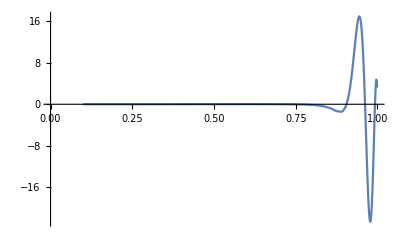

```mathematica
ListLinePlot[Transpose@{Transpose[Flatten[%22,1]][[1]],-Transpose[Flatten[%22,1]][[2]]},PlotRange->{{0,1},Automatic}]
```

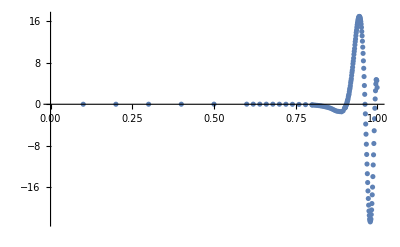

```mathematica
ListPlot[Transpose@{Transpose[Flatten[%22,1]][[1]],-Transpose[Flatten[%22,1]][[2]]},PlotRange->{{0,1},Automatic}]
```

#### Debug

```mathematica
Block[{mQ=√2000,mq=√0.3136},m1=mQ;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
ΦB[x_]=ϕxB;
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
ΦB[x_]=ϕxB;
}
];
m1=mq;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Valsπ,ϕxπ}=Determineϕx[m1,m2,β,Nx];
Φπ[x_]=ϕxπ;
Export[dir<>filename,{Valsπ,ϕxπ}]
},
{
{Valsπ,ϕxπ}=Import[dir<>filename];
Φπ[x_]=ϕxπ;
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M3,ϕ3}={Mn[#][Valsπ],ϕn[#][Φπ]}&[0];
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[2];]
```

```mathematica
Block[{ω=},1/(1-ω)NIntegrate[ϕ1[x]ϕ2[x/ω] ϕ3[p]/(p-(x-ω)/(1-ω))^2,{p,0,1},{x,0,ω},Method->"GlobalAdaptive"]-1/ω NIntegrate[ϕ1[x]ϕ3[(x-ω)/(1-ω)] ϕ2[p]/(p-x/ω)^2,{p,0,1},{x,ω,1},Method->"GlobalAdaptive"]]
```